```mathematica
(*  P(k)~0, Anal~ ns~0.945 , *)
```

```mathematica
{aG, bG}={(*A*)0.130386,(*f*)0.12958}
```

{0.130386,0.12958}

```mathematica
f0=5.85
```

5.85

```mathematica
VM[f_]:=V0(Tanh[f/Sqrt[6]]+aG* Sin[(Tanh[f/Sqrt[6]])/bG])^2;

{VM'[f], VM[f[t]], VM'[f[t]]}
```

{2 V0 (Sech[f/(√6)]^2/(√6)+0.410788 Cos[7.71724 Tanh[f/(√6)]] Sech[f/(√6)]^2) (0.130386 Sin[7.71724 Tanh[f/(√6)]]+Tanh[f/(√6)]),V0 (0.130386 Sin[7.71724 Tanh[f[t]/(√6)]]+Tanh[f[t]/(√6)])^2,2 V0 (Sech[f[t]/(√6)]^2/(√6)+0.410788 Cos[7.71724 Tanh[f[t]/(√6)]] Sech[f[t]/(√6)]^2) (0.130386 Sin[7.71724 Tanh[f[t]/(√6)]]+Tanh[f[t]/(√6)])}

Number of E-folds       (* WE NEED THE SOLUTION OF THE DIFFERENTIAL EQUATION *)

```mathematica
NIntegrate[VM[f]/VM'[f], {f,1.5, f0}]
```

33.4866

```mathematica
H0=(8*Pi^2  *1/2*(VM'[f0]/VM[f0])^2*2.2*10^(-9))^(1/2)  (* From slow-roll expansion. See later, f=7 gives 61 efolds after the solution of the D.E.   *)

V0=3H0^2/(VM[f0]/V0)
```

9.08988×10^-6

2.01509×10^-10

```mathematica
V[t_]:=VM[f[t]];
dV[t_]:=VM'[f[t]];
```

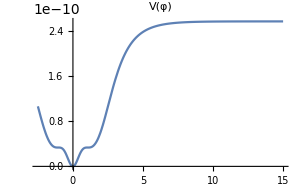
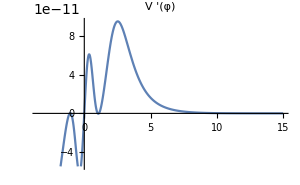

```mathematica
Row[{Plot[VM[ f],{f,-2.5,15}, ImageSize->300, PlotLabel->"V(φ) "] , Plot[VM'[ f],{f,-3.5,15}, ImageSize->300, PlotLabel->"V '(φ) "] }]
```

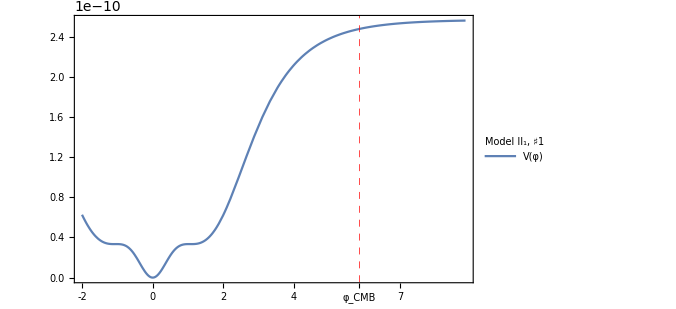

```mathematica
ticksV={{ Automatic, Automatic},{{{-2, "-2"},{-1.5, "",0.005 }, {-1, "-1" }, {-0.5, "",0.005 }, {0, "0" } ,{.5, "",0.005 },{1, "1" }, {1.5, "",0.005 }, {2, "2"}, {2.5, "",0.005 }, {3, "3"}, {3.5, "",0.005 }, {4, "4"}, {4.5, "",0.005 }, {5, "5"}, {5.5, "",0.005 }, (*{6, "6"},*) {6.5, "",0.005 }, {7, "7"}, {7.5, "",0.005 }, {8, "8"}, {f0, "φ_CMB"}, {8.5, "",0.005 }, {9, "9"},{9.5, "",0.005 }, {10, "10"} }, Automatic}} ;

Plot[VM[ f],{f,-2,f0+3},(* PlotLabel->"V(φ) ",*) Frame->True,FrameLabel->{{"", ""} , {" ", " "}},  FrameStyle->Directive[FontSize->27], PlotLegends->Placed[LineLegend[{"V(φ)"},LabelStyle->{GrayLevel[0.1
],29},LegendLabel->"Model II_1,  ♯1 ",LegendLayout->{"Row",1}],{0.87,.3}], ImageSize->500, FrameTicks->ticksV, GridLines->{{f0}, {}}, GridLinesStyle->Directive[Red, Dashed, Thickness->0.00263]]
```

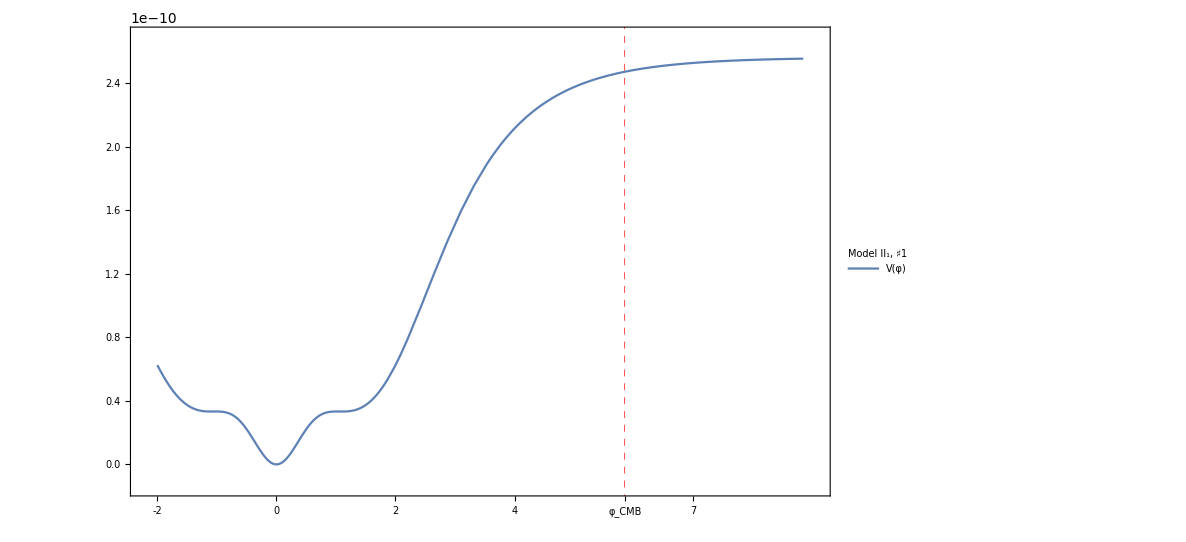

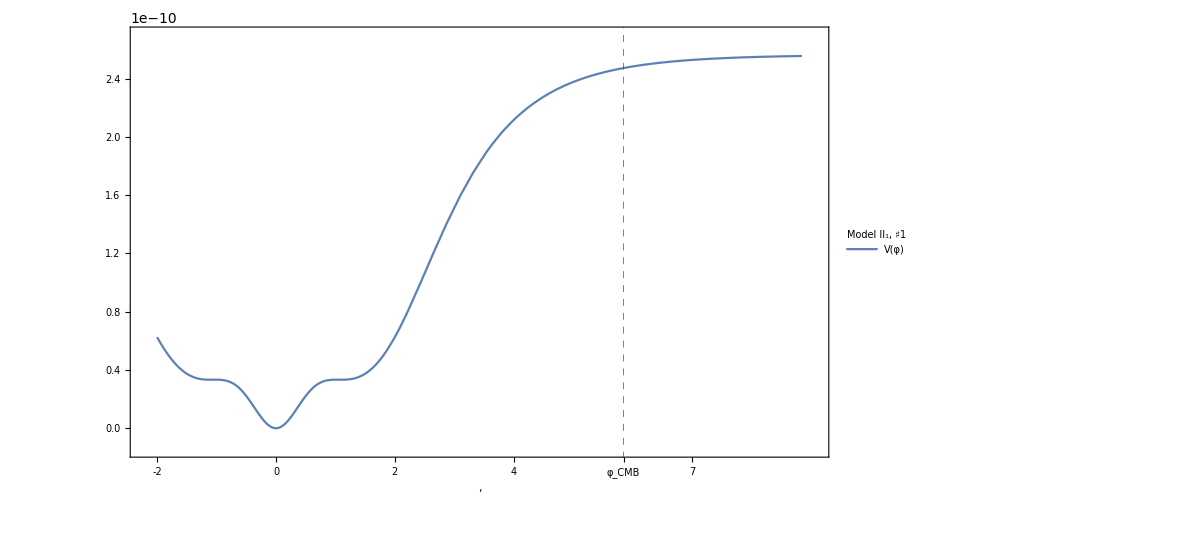

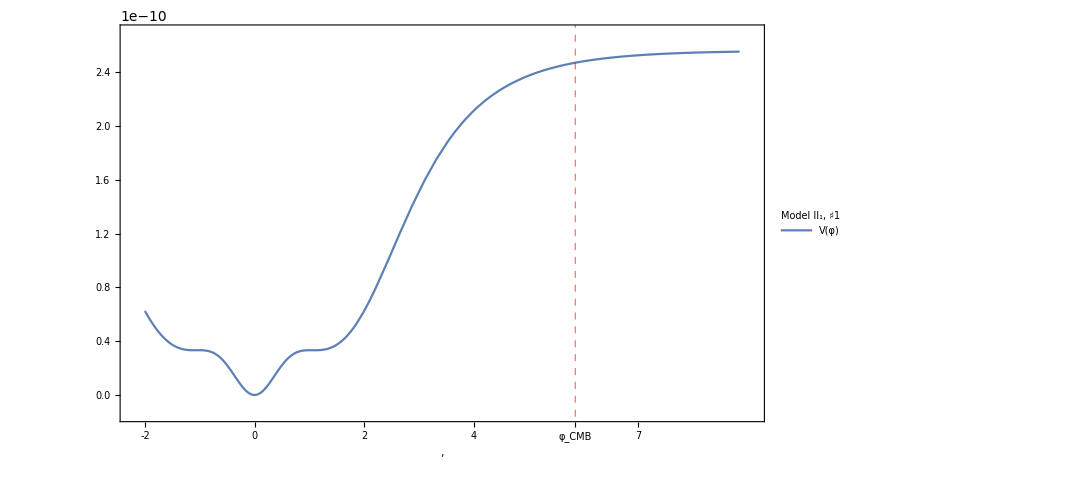

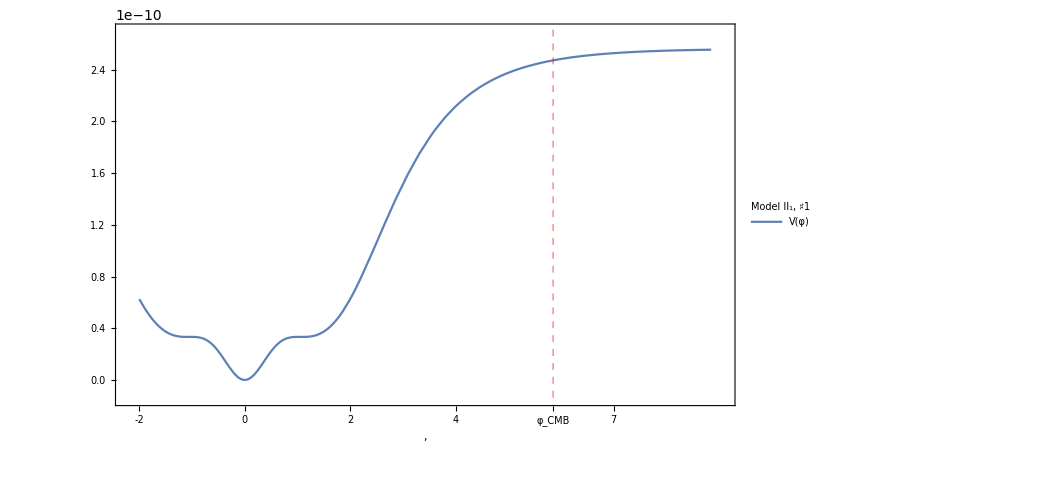

```mathematica
ticksVMag={{{{3.33*10^-11,  3.33Superscript[10,-11]}, {3.34*10^-11,  3.34Superscript[10,-11]}}, Automatic},{{{.9, "",0.005 },{1, "1" }, {1.1, 1.1 },  {1.2, 1.2 } }, Automatic}} ;
```

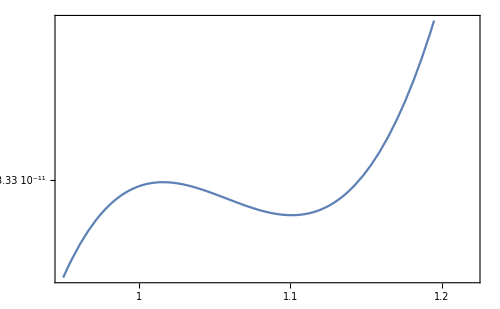

```mathematica
Plot[VM[ f],{f,.95,1.22},(* PlotLabel->"V(φ) ",*) Frame->True,FrameLabel->{{"", ""} , {" "  , " "}},  LabelStyle->{GrayLevel[0.1
],16}, (*PlotLegends->Placed[LineLegend[{"V(φ)"},LabelStyle->{GrayLevel[0.1
],15},LegendLabel->"Model II_1,  ♯1 ",LegendLayout->{"Row",1}],{0.88,.3}],*) ImageSize->500, FrameTicks->ticksVMag, GridLines->{{f0}, {}}, GridLinesStyle->Directive[Red, Dashed, Thickness->0.00263]]
```

```mathematica
BVeloc[f_]:=-VM'[f]/Sqrt[3*VM[f]];
```

```mathematica
EqaB={    f''[t]+3(a'[t]/a[t])f'[t]+dV[t]==0,
         a'[t]== a[t]/(√3)√((f'[t])^2/2+V[t]),
      f[0]==f0, f'[0]==BVeloc[f0], a[0]==1};
```

```mathematica
aBck=NDSolve[EqaB,{f, a},{t, 0 , 10^9}, AccuracyGoal->20, MaxSteps->1000000];//Timing
```

{2.54091,Null}

```mathematica
(*{Evaluate[f[-3/H0]]/.Bck,Evaluate[f[0]]/.Bck, Evaluate[f[c[5]]]/.Bck}*)
```

```mathematica
S1[t_]:=3/2*(f'[t])^2/((f'[t])^2/2+V[t]);
S2[t_]:=S1'[t]/S1[t](a[t]/a'[t]);
S3[t_]:=S2'[t]/S2[t](a[t]/a'[t]);
Z[t_]:=√2 √S1[t] a[t]

H[t_]:=(a'[t]/a[t])
```

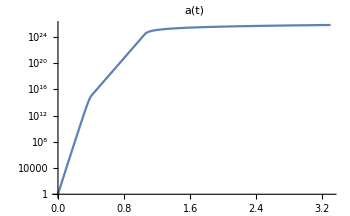
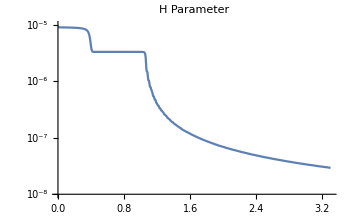
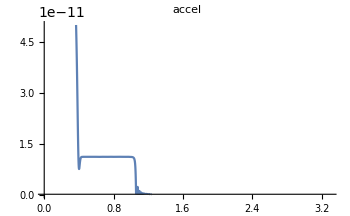
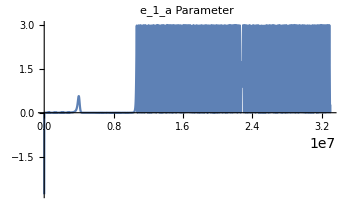
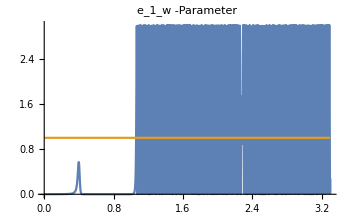
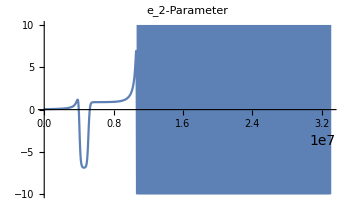
{38.5918,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-}

```mathematica
Row[{LogPlot[Evaluate[{a[t]}]/. aBck, {t,0,3.3*10^7},PlotRange->All, PlotLabel-> "a(t) ", ImageSize->350],

LogPlot[Evaluate[{a'[t]/a[t]}]/. aBck, {t, 0, 3.3*10^7}, PlotRange->{10^-8, 10^-5}, PlotLabel-> "H Parameter", ImageSize->350], 

 Plot[Evaluate[a''[t]/a[t]]/. aBck, {t, 0,3.3*10^7},PlotRange->{10^-13, .5*10^-10}, PlotLabel-> "accel", ImageSize->350], 

Plot[Evaluate[(1-a''[t]a[t]/(a'[t])^2)]/. aBck, {t,0, 3.3*10^7},PlotRange->All, PlotLabel-> "e_1_a Parameter", ImageSize->350], 

 Plot[{Evaluate[{S1[t]}]/. aBck,1}, {t, 0, 3.3*10^7},PlotRange->All, PlotLabel-> "e_1_w -Parameter", ImageSize->350], 

Plot[{Evaluate[{S2[t]}]/. aBck}, {t, 0, 3.3*10^7},PlotLabel-> "e_2-Parameter", ImageSize->350, PlotRange->{-10, 10}]
}]//Timing
```

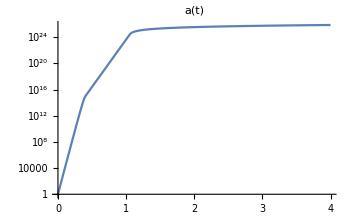
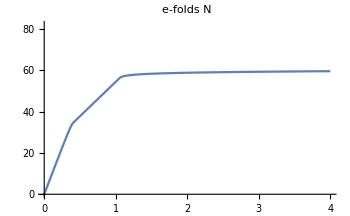

```mathematica
Row[{LogPlot[Evaluate[{a[t]}]/. aBck, {t,0,4 10^7},PlotRange->All, PlotLabel-> "a(t) ", ImageSize->350],

Plot[Evaluate[Log[a[t]]]/. aBck, {t, 0, 4*10^7}, PlotRange->{0, 82}, PlotLabel-> "e-folds N", ImageSize->350]}]
```

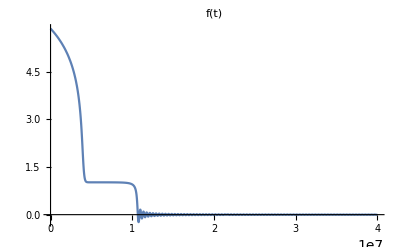
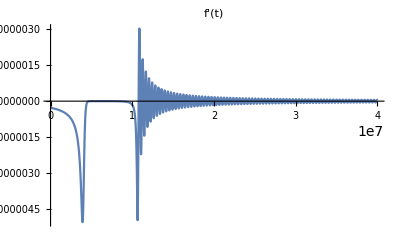

```mathematica
Row[{Plot[Evaluate[{f[t]}]/. aBck, {t,0, 4*10^7},PlotRange->All, PlotLabel-> "f(t) ", ImageSize->400],

Plot[Evaluate[{f'[t]}]/. aBck, {t,0, 4*10^7},PlotRange->All, PlotLabel-> "f'(t) ", ImageSize->400]
}]
```

```mathematica
NIntegrate[Evaluate[a'[t]/a[t]]/.aBck, {t, 0, 5.075*10^7}]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {1.23919×10^6}. NIntegrate obtained 59.8193 and 0.000273305 for the integral and error estimates.

{0.89688,{59.8193}}

The end of Inflation

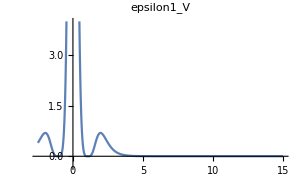
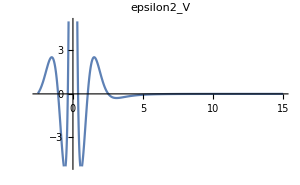
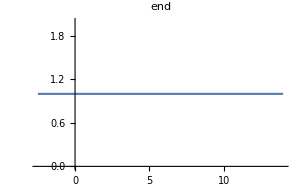

```mathematica
Row[{ploteV1=Plot[1/2*(VM'[ f]/VM[f])^2,{f,-2.5,15},PlotLabel->"epsilon1_V", ImageSize->300, PlotRange->{-.3, 4}], 

ploteV2=Plot[VM''[ f]/VM[f],{f,-2.5,15},PlotLabel->"epsilon2_V", ImageSize->300,  PlotRange->{-5, 5}], 

plotend=Plot[{1}, {f, -2.5,14},PlotLabel->"end", ImageSize->300]}]
```

```mathematica
ptsEnd1=Graphics`Mesh`FindIntersections@Show[ploteV1,plotend] (*  To epsilon pernaei to 1!*)
```

{{-0.613776,1.},{0.613862,1.}}

```mathematica
ptsEnd2=Graphics`Mesh`FindIntersections@Show[ploteV2,plotend]
```

{{-2.08177,1.},{-1.15418,1.},{-0.35228,1.},{0.352395,1.},{1.15421,1.},{2.08264,1.}}

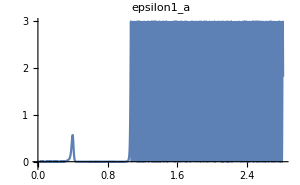
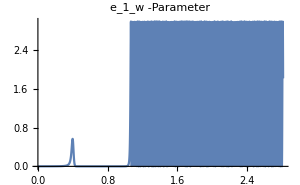
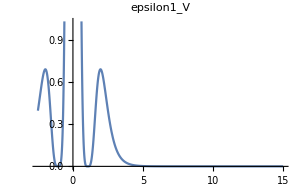
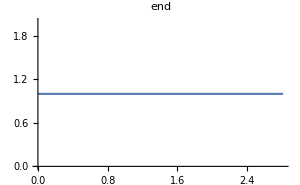

```mathematica
Row[{plote1a=Plot[ Evaluate[(1-a''[t]a[t]/(a'[t])^2)]/.aBck,{t,0, 2.815*10^7},  PlotLabel->"epsilon1_a", ImageSize->300, PlotRange->{-0.1, 3}],

plote1w=Plot[Evaluate[3/2*(f'[t])^2/((f'[t])^2/2+V[t])]/. aBck, {t, 0, 2.815*10^7},PlotRange->All, PlotLabel-> "e_1_w -Parameter", ImageSize->300],

 ploteV1=Plot[1/2*(VM'[ f]/VM[f])^2,{f,-2.5,15},PlotLabel->"epsilon1_V", ImageSize->300], 

plotendtime=Plot[{1}, {t, 0,2.815*10^7},PlotLabel->"end", ImageSize->300]}]
```

```mathematica
ptsEnd1exact=Graphics`Mesh`FindIntersections@Show[plote1w,plotendtime];
```

```mathematica
tend=ptsEnd1exact[[1,1]] (*  To epsilon pernaei to 1!*)
```

1.0598×10^7

```mathematica
Evaluate[H[tend]/.aBck]
```

{2.80826×10^-6}

```mathematica
H0/Evaluate[H[tend]/.aBck]
```

{3.23683}

```mathematica
ρend=3*Evaluate[H[tend]/.aBck]^2
```

{2.3659×10^-11}

```mathematica
1/4Log[1/2(VM'[f0]/VM[f0])^2*3H0^2/ρend]
```

{-1.3254}

```mathematica
(*The number of efolds from the postinf evolution*)
1/4 Log[1/2(VM'[f0]/VM[f0])^2*3H0^2/ρend]
```

{-1.3254}

```mathematica
Treh[Nreh_]:=(30 ρend/Pi^2/200)^(1/4) Exp[-3/4 *Nreh] *2.4*10^(18)

Treh[0]
```

{1.85848×10^15}

Spectral Index

```mathematica
nst[t_]:=1-2S1[t]-S2[t]  (* ???????????????????????????????????????????????  check giati... *)
```

```mathematica
Evaluate[nst[0]/.aBck]
```

{0.998573}

```mathematica
nsf[f_]:=1-(6*1/2(VM'[f]/VM[f])^2-2(VM''[f]/VM[f]))
```

```mathematica
nsf[f0]
```

0.943625

```mathematica
NIntegrate[Evaluate[a'[t]/a[t]]/.aBck, {t, 0, tend}]
```

{56.4403}

```mathematica
Nend1=SetPrecision[NIntegrate[Evaluate[a'[t]/a[t]]/.aBck, {t, 0, tend}]-0.5,2][[1]]  (* Stroggylopoiw ta efolds pros ta katw*)
```

56.

```mathematica
NendR=Round[NIntegrate[Evaluate[a'[t]/a[t]]/.aBck, {t, 0, tend}]-0.5][[1]]
```

56

```mathematica
Nend10=Round[10*NIntegrate[Evaluate[a'[t]/a[t]]/.aBck, {t, 0, tend}]-0.5][[1]]
```

564

```mathematica
Nend=Nend10/10.
```

56.4

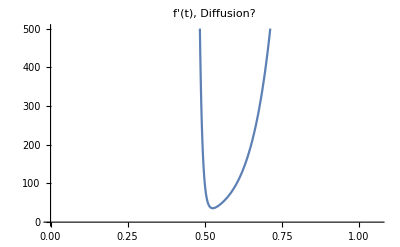

```mathematica
Plot[(Evaluate[-(2*Pi)*f'[t]/H[t]^2])/. aBck, {t,0, tend},PlotRange->{0,500}, PlotLabel-> "f'(t),   Diffusion? ", ImageSize->400(*, Frame->True, FrameStyle->20*)]
```

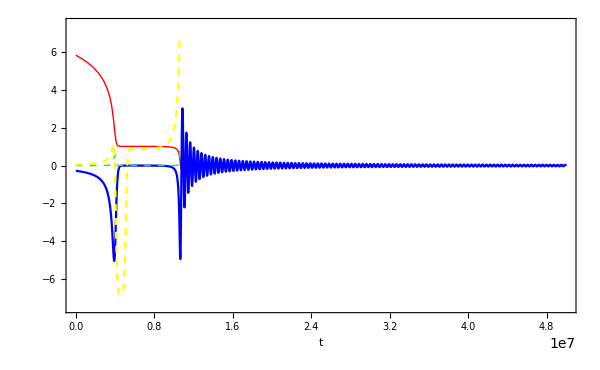

```mathematica
Show[Plot[Evaluate[{f[t]}]/. aBck, {t,0, 5*10^7}, ImageSize->600, PlotStyle->{Red, Thick},PlotRange->{-7.5,7.5},PlotLegends->Placed[{"φ"},{Right,Bottom}], Frame->True,FrameLabel->{"t", "" },  FrameStyle->Directive[Bold, FontSize->20]],

Plot[10^6*Evaluate[{f'[t]}]/. aBck, {t,0, 5*10^7},PlotRange->All, ImageSize->400, PlotStyle->Blue, PlotLegends->Placed[{"dφ / dt"},{Right,Bottom}]], 

Plot[{Evaluate[{S1[t]}]/. aBck}, {t, 0, tend},PlotRange->All, PlotStyle->{Green, Thick, Dashed},PlotLegends->Placed[{"ϵ_H"},{Right,Bottom}]],

Plot[{Evaluate[{S2[t]}]/. aBck}, {t, 0, tend},PlotRange->All, PlotStyle->{Yellow, Dashed},PlotLegends->Placed[{"η_H"},{Right,Bottom}]]]
```

```mathematica
Ne[t_]:=Log[a[t]]/.aBck
```

```mathematica
CCDosc=List[Table[n,{n,0,Nend+4, .05}]];

Row[{plotNe=Plot[{Ne[t]}, {t, 0, 4*tend},PlotLabel->"N(t)", ImageSize->300, PlotRange->{0,Nend+8}],plotNtimeOsc=Plot[CCDosc, {t, 0, 2*tend},PlotLabel->"N-Time", ImageSize->300]}];

ptsNtDense01osc=Graphics`Mesh`FindIntersections@Show[plotNe,plotNtimeOsc];


NTosc           =Insert[ptsNtDense01osc,{0,0},1];
cDosc[r_]:=NTosc[[r+1,1]];

tableOscD        =Table[{N, Evaluate[f[cDosc[20*N]]]/.aBck[[1]]} ,{N, 0, Nend+1,.05}]; 
tableOscDvel =Table[{N, Evaluate[f'[cDosc[20*N]]*10^6]/.aBck[[1]]} ,{N, 0, Nend+1, .05}]; 
tableOscDe1   =Table[{N, Evaluate[S1[cDosc[20*N]]]/.aBck[[1]]} ,{N, 0, Nend+.4,.05}]; 
tableOscDe2   =Table[{N, Evaluate[S2[cDosc[20*N]]]/.aBck[[1]]} ,{N, 0, Nend,.05}]; //Timing
```

{10.3047,Null}

```mathematica
tableOscDe3   =Table[{N, Evaluate[S3[cDosc[20*N]]]/.aBck[[1]]} ,{N, 0, Nend,.05}];
```

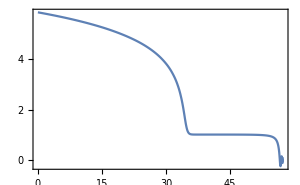
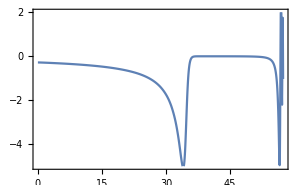
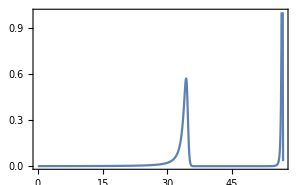
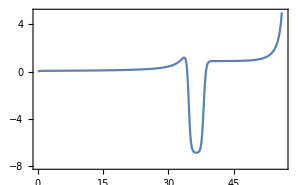

```mathematica
Row[{ListPlot[tableOscD, Joined->True, ImageSize->300,Frame->True],
ListPlot[tableOscDvel, Joined->True, ImageSize->300, PlotRange->{-5, 2},Frame->True], ListPlot[tableOscDe1, Joined->True, ImageSize->300, PlotRange->{0,1},Frame->True], ListPlot[tableOscDe2, Joined->True, ImageSize->300, PlotRange->{-8,5},Frame->True] }]
```

```mathematica
tableOscDe1=Table[{N, Evaluate[S1[cDosc[20*N]]]/.aBck[[1]]} ,{N, 0, Nend+.4,.05}] ;
```

```mathematica
tableOscDe2=Table[{N, Evaluate[S2[cDosc[20*N]]]/.aBck[[1]]} ,{N, 0, Nend,.05}];
```

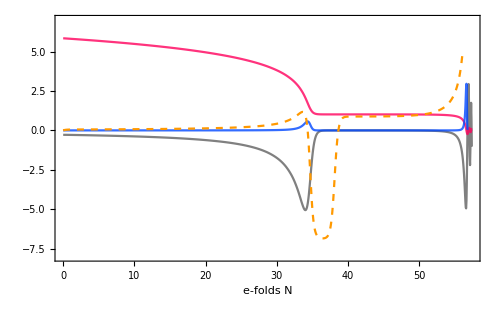

```mathematica
Show[ ListPlot[tableOscDvel, Joined->True, ImageSize->500, PlotRange->{-8,7}, PlotStyle->{Gray}, Frame->True,FrameLabel->{{"", ""} , {"e-folds N", " "}},  FrameStyle->Directive[FontSize->16], PlotLegends->Placed[{"dφ / dN"},{Right,Top}]],

ListPlot[tableOscD, Joined->True, ImageSize->400, PlotRange->{-8,9}, PlotStyle->Hue[.94,1 ,1, .8], PlotLegends->Placed[{"φ"},{Right,Top}]],  

ListPlot[tableOscDe1, Joined->True, ImageSize->300, PlotRange->{0,5}, PlotStyle->Hue[.62,1 ,1, .8], PlotLegends->Placed[{"ϵ_1"},{Right,Bottom}]], 

ListPlot[tableOscDe2, Joined->True, ImageSize->300, PlotRange->{-8,5}, PlotStyle->{Hue[0.1,5,1], Dashed},  PlotLegends->Placed[{"ϵ_2"},{Right,Bottom}]],

(*ListPlot[tableOscDe3, Joined->True, ImageSize->300, PlotRange->{-8,5}, PlotStyle->{Hue[0.2,1,1], Dotted},  PlotLegends->Placed[{"ϵ_3"},{Right,Bottom}]],
*)
ListPlot[{{10, -5}, {10, -5}}, PlotStyle->White,PlotLegends->Placed[LineLegend[{""},LabelStyle->{GrayLevel[0.1
],15},LegendLabel->"Modulated Chaotic Model II_1 ",LegendLayout->{"Row",1}],{0.25,.05}] ]]
```

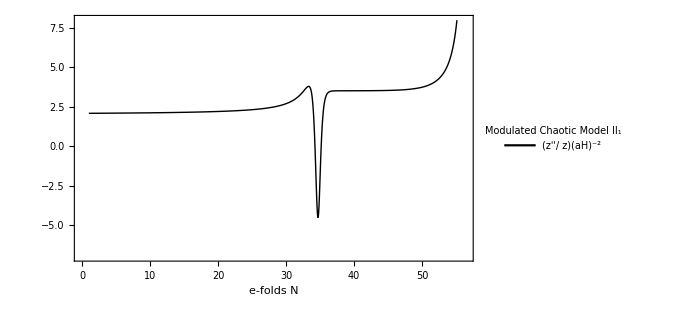

```mathematica
tableNZZ=Table[{N,Evaluate[2-S1[cDosc[20*N]]+3/2 S2[cDosc[20*N]]-1/2*S1[cDosc[20*N]]*S2[cDosc[20*N]]+1/4(S2[cDosc[20*N]])^2+1/2 S2[cDosc[20*N]]*S3[cDosc[20*N]]]/. aBck[[1]]} ,{N, 1, Nend,.05}]; 


ListPlot[tableNZZ, Joined->True, ImageSize->500, PlotRange->{-7,8}, PlotStyle->{Black, Thick}, Frame->True,FrameLabel->{{"", ""} , {"e-folds N", " "}},  FrameStyle->Directive[FontSize->16], PlotLegends->Placed[LineLegend[{"(z''/ z)(aH)^-2"},LabelStyle->{GrayLevel[0.1
],15},LegendLabel->"Modulated Chaotic Model II_1",LegendLayout->{"Row",1}],{0.25,.8}]]
```

```mathematica
tableNDif       =Table[{N,Evaluate[-(2*Pi)*f'[cDosc[20*N]]/H[cDosc[20*N]]^2]/. aBck[[1]]} ,{N, 1, Nend,.05}]; 
tableNDifLog=Table[{N,Log10[Evaluate[-(2*Pi)*f'[cDosc[20*N]]/H[cDosc[20*N]]^2]/. aBck[[1]]]} ,{N, 1, Nend,.05}];
```

```mathematica
ticksDif={{     { {-1, "0.1"},{-.8, "",0.005 }, {-.6, "",0.005 }, {-.4, "",0.005 }, {-.2, "",0.005 } , {0, 1},{.2, "",0.005 },{.4, "",0.005 }, {.6, "",0.005 }, {.8, "",0.005 }, {1, Superscript[10,1]}, {1.2, "",0.005 },{1.4, "",0.005 }, {1.6, "",0.005 }, {1.8, "",0.005 }, {2, Superscript[10,2]}, {2.2, "",0.005 },{2.4, "",0.005 }, {2.6, "",0.005 }, {2.8, "",0.005 },  {3, Superscript[10,3]}, {3.2, "",0.005 },{3.4, "",0.005 }, {3.6, "",0.005 }, {3.8, "",0.005 }, {4, Superscript[10,4]}, {3.2, "",0.005 },{3.4, "",0.005 }, {3.6, "",0.005 }, {3.8, "",0.005 }, {4, Superscript[10,1]}, {4.2, "",0.005 },{4.4, "",0.005 }, {4.6, "",0.005 }, {4.8, "",0.005 }, {5, Superscript[10,5]}, {5.2, "",0.005 },{5.4, "",0.005 }, {5.6, "",0.005 }, {5.8, "",0.005 },{6, Superscript[10,6]}, {6.2, "",0.005 },  {6.4, "",0.005 }, {6.6, "",0.005 }, {6.8, "",0.005 }, {7, Superscript[10,7]},{7.2, "",0.005 }}, Automatic},{Automatic, Automatic}} ;
```

```mathematica
Row[{ListPlot[tableNDif, Joined->True, ImageSize->450, PlotRange->All, PlotStyle->{Hue[1.1,1 ,1, .6], Thick}, Frame->True,, ImageSize->500,FrameLabel->{{"", ""} , {"e-folds N", " "}},  FrameStyle->Directive[FontSize->16], PlotLegends->Placed[{" Z'' / Z "},{Right, Bottom}]] , Show[ListPlot[tableNDifLog, Joined->True, ImageSize->500, PlotRange->{-1, 7.4}, PlotStyle->{Hue[.7,1 ,1, .5], Thick}, Frame->True,FrameLabel->{  "e-folds N", "(2 SuperscriptBox[π, 2] OverscriptBox[φ, .])/H^2"},  FrameStyle->Directive[FontSize->16],FrameTicks->ticksDif, PlotLegends->Placed[LineLegend[{"Classical / Quantum dynamics"},LabelStyle->{GrayLevel[0.1
],15},LegendLabel->"Polynomial Model",LegendLayout->{"Row",1}],{0.3,.22}] ]   
]}];
```

ListPlot::nonopt: Options expected (instead of Null) beyond position 1 in ListPlot[{{1.,21739.7},{1.05,21769.1},{1.1,21799.4},{1.15,21829.4},{1.2,21860.},{1.25,21890.9},{1.3,21921.4},{1.35,21952.8},«36»,{3.2,23186.9},{3.25,23224.2},{3.3,23258.5},{3.35,23293.9},{3.4,23331.2},{3.45,23365.5},«1059»},«9»,«1»]. An option must be a rule or a list of rules.

General::stop: Further output of ListPlot::nonopt will be suppressed during this calculation.

```mathematica
KTDW[j_]=Table[Evaluate[a'[CCDosc[j]]]/.aBck,{j,0, 20*Nend,1}];
KDW[j_]:=KTDW[1][[j+1, 1]]   

NT005=Insert[ptsNtDense01osc,{0,0},1];
cDosc[r_]:=NT005[[r+1,1]];
```

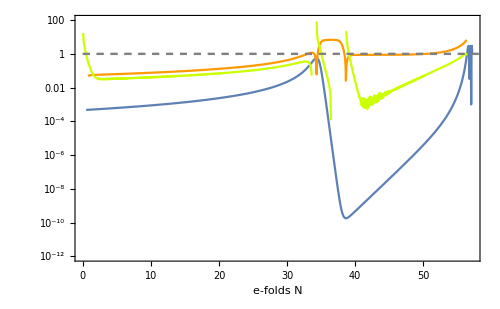
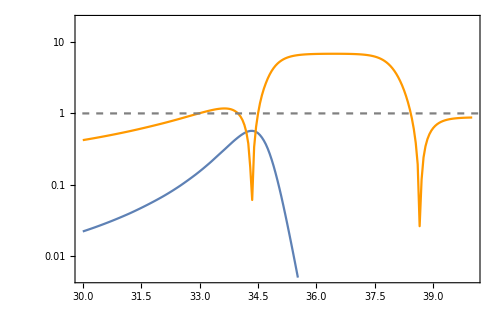

```mathematica
tableOscD=Table[{N, Evaluate[f[cDosc[20*N]]]/.aBck[[1]]} ,{N, 0, Nend+1,.05}]; 
tableOscDvel=Table[{N, Evaluate[f'[cDosc[20*N]]*10^6]/.aBck[[1]]} ,{N, 0, Nend+1,.05}]; 
tableOscDe1=Table[{N, Evaluate[S1[cDosc[20*N]]]/.aBck[[1]]} ,{N, 0.5, Nend+.8,.05}]; 
tableOscDe2=Table[{N, Evaluate[S2[cDosc[20*N]]]/.aBck[[1]]} ,{N, 0, Nend,.05}]; 
tableOscDe2abs=Table[{N, Evaluate[Abs[S2[cDosc[20*N]]]]/.aBck[[1]]} ,{N, .75, Nend,.05}];

tableOscDe1Zoom=Table[{N, Evaluate[S1[cDosc[20*N]]]/.aBck[[1]]} ,{N, 30, 40,.05}]; 
tableOscDe2absZoom=Table[{N, Evaluate[Abs[S2[cDosc[20*N]]]]/.aBck[[1]]} ,{N, 30, 40,.05}];


Row[{Show[ListLogPlot[tableOscDe1, Joined->True, ImageSize->500, PlotRange->{10^-12, 100},  PlotStyle->PlotStyle->Hue[.62,1 ,1, .8], Frame->True,FrameLabel->{{"", ""} , {" e-folds N", " "}},  FrameStyle->Directive[FontSize->16], PlotLegends->Placed[{"ϵ_1"},{Right,Bottom}]], ListLogPlot[tableOscDe2abs, Joined->True, ImageSize->300,  PlotStyle->Hue[0.1,5,1],PlotRange->All,  PlotLegends->Placed[{" |ϵ_2|"},{Right,Bottom}]], LogPlot[1, {x, 0, 60},   PlotStyle->{Gray, Dashed}], ListLogPlot[tableOscDe3, Joined->True, ImageSize->300,  PlotStyle->Hue[0.2,5,1],PlotRange->All,  PlotLegends->Placed[{" ϵ_3"},{Right,Bottom}]], LogPlot[1, {x, 0, 60},   PlotStyle->{Gray, Dashed}]  ], Show[ListLogPlot[tableOscDe1Zoom, Joined->True, ImageSize->500, PlotRange->{5*10^-3, 2*10},  PlotStyle->PlotStyle->Hue[.62,1 ,1, .8], Frame->True,FrameLabel->{{"", ""} , {"  ", " "}},  FrameStyle->Directive[FontSize->12]], ListLogPlot[tableOscDe2absZoom, Joined->True, ImageSize->300,  PlotStyle->Hue[0.1,5,1],PlotRange->All], LogPlot[1, {x, 0, 60},   PlotStyle->{Gray, Dashed}] ]   }]
```

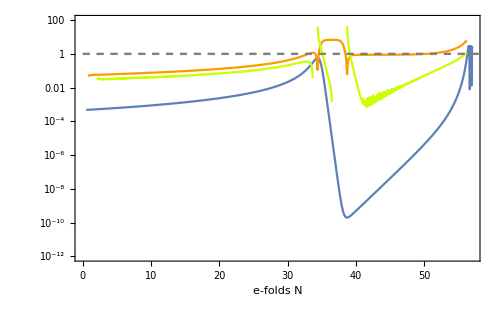
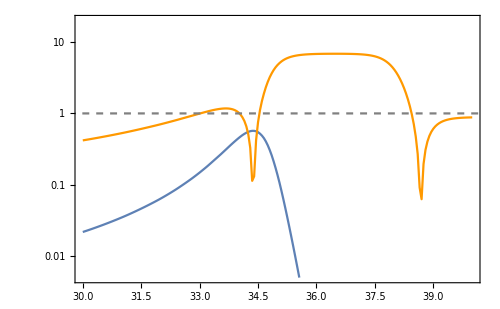

ListLogPlot::lpn: tableOscDe3Zoom is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

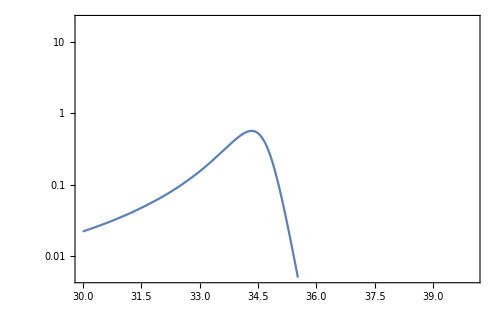
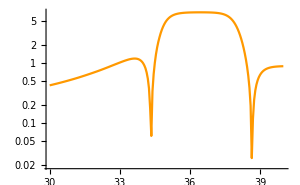
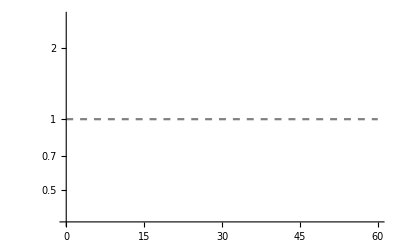
Show[-Graphics-,-Graphics-,-Graphics-,ListLogPlot[tableOscDe3Zoom,Joined→True,ImageSize→300,PlotStyle→Hue[0.2,5,1],PlotRange→All],-Graphics-]

```mathematica
Show[ListLogPlot[tableOscDe1Zoom, Joined->True, ImageSize->500, PlotRange->{5*10^-3, 2*10},  PlotStyle->PlotStyle->Hue[.62,1 ,1, .8], Frame->True,FrameLabel->{{"", ""} , {"  ", " "}},  FrameStyle->Directive[FontSize->12]], ListLogPlot[tableOscDe2absZoom, Joined->True, ImageSize->300,  PlotStyle->Hue[0.1,5,1],PlotRange->All], LogPlot[1, {x, 0, 60},   PlotStyle->{Gray, Dashed}], ListLogPlot[tableOscDe3Zoom, Joined->True, ImageSize->300,  PlotStyle->Hue[0.2,5,1],PlotRange->All], LogPlot[1, {x, 0, 60},   PlotStyle->{Gray, Dashed}]  ]
```

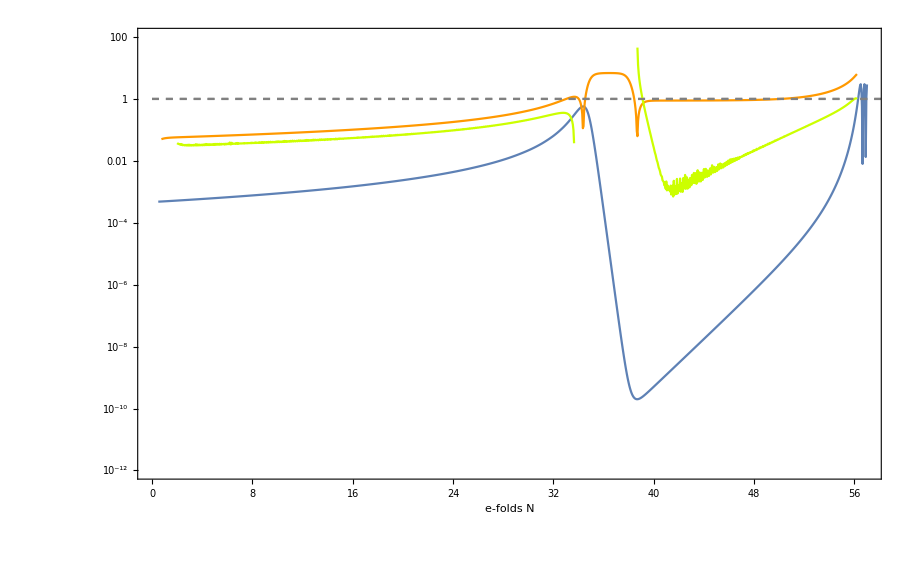
```mathematica
-Graphics--Graphics-
```

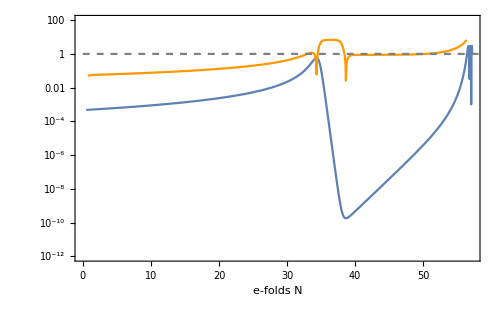

```mathematica
Show[ListLogPlot[tableOscDe1, Joined->True, ImageSize->500, PlotRange->{10^-12, 100},  PlotStyle->PlotStyle->Hue[.62,1 ,1, .8], Frame->True,FrameLabel->{{"", ""} , {" e-folds N", " "}},  FrameStyle->Directive[FontSize->16], PlotLegends->Placed[{"ϵ_1"},{Right,Bottom}]], ListLogPlot[tableOscDe2abs, Joined->True, ImageSize->300,  PlotStyle->Hue[0.1,5,1],PlotRange->All,  PlotLegends->Placed[{" |ϵ_2|"},{Right,Bottom}]], LogPlot[1, {x, 0, 60},   PlotStyle->{Gray, Dashed}] ]
```

```mathematica
tableOscDe3=Table[{N, Evaluate[S3[cDosc[20*N]]]/.aBck[[1]]} ,{N, 2, Nend,.05}]; 
tableOscDe3Zoom=Table[{N, Evaluate[S3[cDosc[20*N]]]/.aBck[[1]]} ,{N, 30, 40,.05}];
```

FITTING

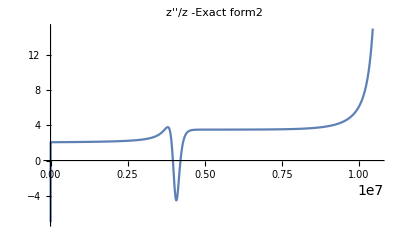
{148.816,-Graphics-}

```mathematica
Row[{Plot[Evaluate[2-S1[t]+3/2 S2[t]-1/2*S1[t]*S2[t]+1/4(S2[t])^2+1/2 S2[t]*S3[t]]/. aBck, {t,0, tend},PlotRange->{-7, 15}, PlotLabel-> "z''/z -Exact form2 ", ImageSize->400]}]//Timing
```

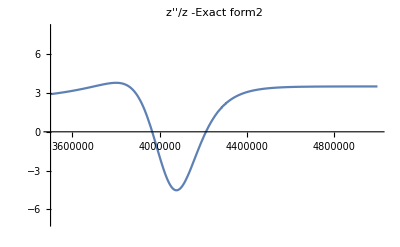
{123.933,-Graphics-}

```mathematica
Plot[Evaluate[2-S1[t]+3/2 S2[t]-1/2*S1[t]*S2[t]+1/4(S2[t])^2+1/2 S2[t]*S3[t]]/. aBck, {t, 3.5*10^6, 5*10^6},PlotRange->{-7, 8}, PlotLabel-> "z''/z -Exact form2 ", ImageSize->400]//Timing
```

```mathematica
dataT1=Evaluate[Table[{t,(2-S1[t]+3/2 S2[t]-1/2*S1[t]*S2[t]+1/4(S2[t])^2+1/2 S2[t]*S3[t])},{t,RandomReal[{500, 3.8*10^6},1000]}]]/.aBck[[1]];
```

```mathematica
q1=Fit[dataT1,{1,x,x^2,x^3,x^4, x^5, x^6, x^7, x^8,x^9,x^10,x^11,x^12,x^13,x^14},x]
```

2.05239+1.08002×10^-6 x-1.16376×10^-11 x^2+6.13702×10^-17 x^3-1.85622×10^-22 x^4+3.55435×10^-28 x^5-4.56798×10^-34 x^6+4.0817×10^-40 x^7-2.58526×10^-46 x^8+1.1679×10^-52 x^9-3.73676×10^-59 x^10+8.26902×10^-66 x^11-1.20324×10^-72 x^12+1.03547×10^-79 x^13-3.99196×10^-87 x^14

```mathematica
Q1[x_]:=2.052390875616991+1.0800249075139153*^-6 x-1.1637574815444876*^-11 x^2+6.13702455281433*^-17 x^3-1.8562159789080699*^-22 x^4+3.554354524504979*^-28 x^5-4.5679769734155355*^-34 x^6+4.081703269777966*^-40 x^7-2.5852601255993303*^-46 x^8+1.167901690089289*^-52 x^9-3.7367592075094474*^-59 x^10+8.269016165393441*^-66 x^11-1.2032410208157513*^-72 x^12+1.0354691912880586*^-79 x^13-3.9919589690638947*^-87 x^14
```

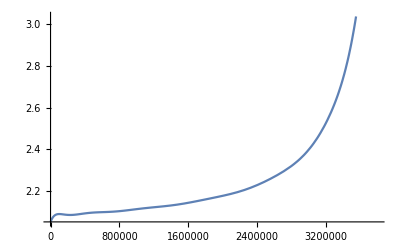

```mathematica
Plot[Q1[t], {t, 0, 3.8*10^6}]
```

```mathematica
dataT2=Evaluate[Table[{t, (2-S1[t]+3/2 S2[t]-1/2*S1[t]*S2[t]+1/4(S2[t])^2+1/2 S2[t]*S3[t])}, {t,RandomReal[{ 3.8*10^6, 4.4*10^6},1000]}]]/.aBck[[1]];
```

```mathematica
q2=Fit[dataT2,{1,x,x^2,x^3,x^4, x^5, x^6,  x^7, x^8, x^9,x^10,x^11},x]
```

-3.11655×10^9+4324.67 x-0.00213231 x^2+3.14619×10^-10 x^3+7.24196×10^-17 x^4-1.98101×10^-23 x^5-3.87681×10^-30 x^6+1.20686×10^-36 x^7+2.00599×10^-43 x^8-1.028×10^-49 x^9+1.33146×10^-56 x^10-5.97944×10^-64 x^11

```mathematica
Q2[x_]:=-3.116546766010632*^9+4324.670164475906 x-0.0021323063445245903 x^2+3.146189828474388*^-10 x^3+7.241959396566396*^-17 x^4-1.9810119104802528*^-23 x^5-3.876805726320487*^-30 x^6+1.2068616786098337*^-36 x^7+2.0059942725737893*^-43 x^8-1.0280015431303924*^-49 x^9+1.3314620247037703*^-56 x^10-5.979439057338035*^-64 x^11
```

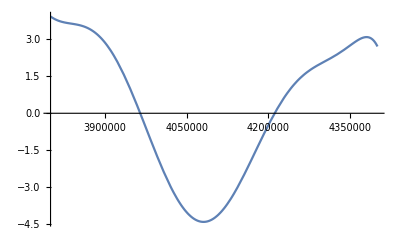

```mathematica
Plot[Q2[t], {t, 3.8*10^6, 4.4*10^6}]
```

```mathematica
dataT3=Evaluate[Table[{t, (2-S1[t]+3/2 S2[t]-1/2*S1[t]*S2[t]+1/4(S2[t])^2+1/2 S2[t]*S3[t])}, {t,RandomReal[{ 4.4*10^6,tend},1000]}]]/.aBck[[1]];
```

```mathematica
q3=Fit[dataT3,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13},x]
```

6.91925×10^6-13.3234 x+0.0000117413 x^2-6.27028×10^-12 x^3+2.26406×10^-18 x^4-5.83711×10^-25 x^5+1.10555×10^-31 x^6-1.55755×10^-38 x^7+1.6324×10^-45 x^8-1.25709×10^-52 x^9+6.91457×10^-60 x^10-2.57273×10^-67 x^11+5.80421×10^-75 x^12-5.99707×10^-83 x^13

```mathematica
Q3[x_]:=6.919246965384993*^6-13.323370326148094 x+0.000011741312022853528 x^2-6.270281922701046*^-12 x^3+2.2640553169740336*^-18 x^4-5.837114573920024*^-25 x^5+1.1055451234850638*^-31 x^6-1.5575534964940629*^-38 x^7+1.632403273102475*^-45 x^8-1.257093936908005*^-52 x^9+6.914573672126531*^-60 x^10-2.5727274482226578*^-67 x^11+5.804206103659414*^-75 x^12-5.9970690903421544*^-83 x^13
```

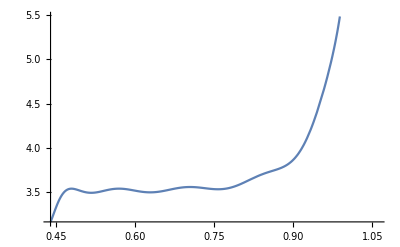

```mathematica
Plot[Q3[t], {t, 4.4*10^6, tend}]
```

```mathematica
FiTa2[t_]=Piecewise[{{Q1[t],t<3.8*10^6},{Q3[t],t>4.4*10^6}},Q2[t]]
```

Piecewise[{{2.05239+1.08002×10^-6 t-1.16376×10^-11 t^2+6.13702×10^-17 t^3-1.85622×10^-22 t^4+3.55435×10^-28 t^5-4.56798×10^-34 t^6+4.0817×10^-40 t^7-2.58526×10^-46 t^8+1.1679×10^-52 t^9-3.73676×10^-59 t^10+8.26902×10^-66 t^11-1.20324×10^-72 t^12+1.03547×10^-79 t^13-3.99196×10^-87 t^14, t<3.8×10^6}, {6.91925×10^6-13.3234 t+0.0000117413 t^2-6.27028×10^-12 t^3+2.26406×10^-18 t^4-5.83711×10^-25 t^5+1.10555×10^-31 t^6-1.55755×10^-38 t^7+1.6324×10^-45 t^8-1.25709×10^-52 t^9+6.91457×10^-60 t^10-2.57273×10^-67 t^11+5.80421×10^-75 t^12-5.99707×10^-83 t^13, t>4.4×10^6}, {-3.11655×10^9+4324.67 t-0.00213231 t^2+3.14619×10^-10 t^3+7.24196×10^-17 t^4-1.98101×10^-23 t^5-3.87681×10^-30 t^6+1.20686×10^-36 t^7+2.00599×10^-43 t^8-1.028×10^-49 t^9+1.33146×10^-56 t^10-5.97944×10^-64 t^11, True}}]

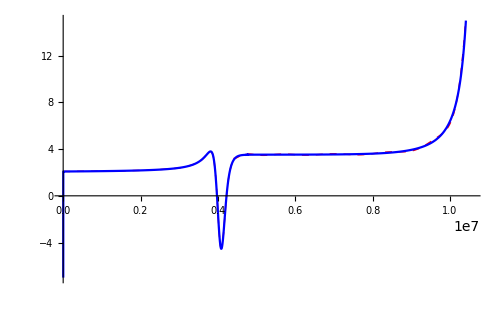
{155.335,-Graphics-}

```mathematica
Plot[{FiTa2[t], Evaluate[2-S1[t]+3/2 S2[t]-1/2*S1[t]*S2[t]+1/4(S2[t])^2+1/2 S2[t]*S3[t]]/. aBck}, {t, 0, tend}, PlotStyle->{{Red, Dashed, Thick}, Blue}, PlotRange->{-7, 15}, ImageSize->500]//Timing
```

PERTURBATIONS

```mathematica
Kapprox[N_]:=H60*Exp[N]
q[N_]:=N/H60
```

FINDING THE TIME WITH  E_FOLDS

```mathematica
Ne[t_]:=Log[a[t]]/.aBck
```

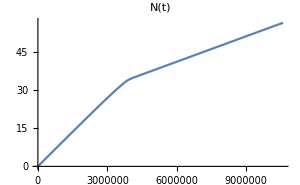

```mathematica
Plot[{Ne[t]}, {t, 0, tend},PlotLabel->"N(t)", ImageSize->300, PlotRange->{0, 57}]
```

```mathematica
CC=List[Table[n,{n,0,Nend, 1}]] (* Bazw kai  to 0  *)
```

{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}}

```mathematica
Length[CC]
```

1

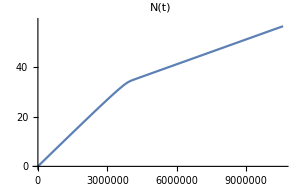
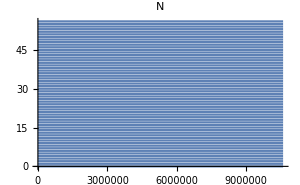

```mathematica
Row[{plotNe=Plot[{Ne[t]}, {t, 0, tend},PlotLabel->"N(t)", ImageSize->300, PlotRange->{0, Nend+2}],plotNeP=Plot[CC, {t, 0, tend},PlotLabel->"N", ImageSize->300]}]
```

```mathematica
ptsNe=Graphics`Mesh`FindIntersections@Show[plotNe,plotNeP]
```

{{110032.,1.},{220121.,2.},{330289.,3.},{440464.,4.},{550759.,5.},{661076.,6.},{771509.,7.},{881989.,8.},{992585.,9.},{1.10323×10^6,10.},{1.21401×10^6,11.},{1.32488×10^6,12.},{1.43589×10^6,13.},{1.54698×10^6,14.},{1.65826×10^6,15.},{1.76964×10^6,16.},{1.88124×10^6,17.},{1.99301×10^6,18.},{2.10499×10^6,19.},{2.21719×10^6,20.},{2.32966×10^6,21.},{2.44249×10^6,22.},{2.55556×10^6,23.},{2.66929×10^6,24.},{2.78321×10^6,25.},{2.89811×10^6,26.},{3.01324×10^6,27.},{3.13024×10^6,28.},{3.2475×10^6,29.},{3.36795×10^6,30.},{3.49009×10^6,31.},{3.61772×10^6,32.},{3.75253×10^6,33.},{3.9143×10^6,34.},{4.16169×10^6,35.},{4.46035×10^6,36.},{4.76002×10^6,37.},{5.0597×10^6,38.},{5.35938×10^6,39.},{5.65907×10^6,40.},{5.95875×10^6,41.},{6.25843×10^6,42.},{6.55811×10^6,43.},{6.8578×10^6,44.},{7.15748×10^6,45.},{7.45716×10^6,46.},{7.75684×10^6,47.},{8.05653×10^6,48.},{8.35621×10^6,49.},{8.65589×10^6,50.},{8.95558×10^6,51.},{9.25526×10^6,52.},{9.55496×10^6,53.},{9.85471×10^6,54.},{1.01546×10^7,55.},{1.04566×10^7,56.}}

```mathematica
NT=Insert[ptsNe,{0,0},1];
```

```mathematica
Length[NT]
```

57

```mathematica
ClearAll[c]
```

```mathematica
c[N_]:=NT[[N+1,1]]
```

```mathematica
PAnaly[t_]:=(a'[t]/a[t])^2*(8 *Pi^2*3/2*(f'[t])^2/((f'[t])^2/2+V[t] ))^-1
```

```mathematica
P[t_]:=(Abs[u[t]+I*v[t]])^2*(2(a[t])^2*3/2*(f'[t])^2/((f'[t])^2/2+V[t]))^(-1)
```

```mathematica
PRhc[t_, N_]:= (K[N])^3/(2Pi^2)(Abs[u[t]+I*v[t]])^2*(2(a[t])^2*3/2*(f'[t])^2/((f'[t])^2/2+V[t]))^(-1)   
 (*  DEN EINAI SWSTO AFOY PAIRNOUME XRONO POLY PERA APO TON ORIZONTA*)
```

```mathematica
Psr[t_]:=1/(12Pi^2) (V[t])^3/(dV[t])^2
```

```mathematica
KT[N_]=Table[Evaluate[a'[c[N]]]/.aBck,{N,0, Nend,1}];
K[N_]:=KT[1][[N+1, 1]]        (* @ Horizon Crossing *)
```

```mathematica
Evaluate[a'[c[33]]]/.aBck
```

{1.49282×10^9}

```mathematica
FBTable[N_]=Table[Evaluate[f[c[N]]] /.aBck, {N, 0,NendR, 1}];
FB[N_]:=FBTable[1][[N+1,1]]

VBTable[N_]=Table[Evaluate[f'[c[N]]] /.aBck,{N, 0, NendR,1}];
VB[N_]:=VBTable[1][[N+1,1]];

aBTable[N_]=Table[Evaluate[a[c[N]]] /.aBck,{N, 0, NendR, 1}];
aB[N_]:=aBTable[1][[N+1,1]];
```

```mathematica
(*    MUKHANOV - SASAKI   *)
```

```mathematica
RangeN=Range[5,NendR,1];


EqA=NDSolve[{u''[t]+(a'[t]/a[t])u'[t]+((K[#])^2/(a[t])^2- (a'[t]/a[t])^2*(FiTa2[t]))u[t]==0,
v''[t]+(a'[t]/a[t])v'[t]+((K[#])^2/(a[t])^2- (a'[t]/a[t])^2*(FiTa2[t]))v[t]==0,
        f''[t]+3(a'[t]/a[t])f'[t]+dV[t]==0,
         a'[t]== a[t]/(√3)√((f'[t])^2/2+V[t]),
u[c[#-5]]==1/√(2*K[#]), u'[c[#-5]]==0, v[c[#-5]]==0, v'[c[#-5]]==√K[#]/(aB[#-5]*√2), 
f[c[#-5]]==FB[#-5],  f'[c[#-5]]==VB[#-5], a[c[#-5]]==aB[#-5]},
{u,v, f, a},{t,c[#-5], c[NendR]},AccuracyGoal->15, MaxSteps->1000000]&/@RangeN ;
```

NDSolve::ndsz: At t == 4.05612×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
EqA[[1,1]]
```

{u→                                      6
InterpolatingFunction[{{0., 4.05612 10 }}, <>],v→                                      6
InterpolatingFunction[{{0., 4.05612 10 }}, <>],f→                                      6
InterpolatingFunction[{{0., 4.05612 10 }}, <>],a→                                      6
InterpolatingFunction[{{0., 4.05612 10 }}, <>]}

```mathematica
MedA=Table[{c[N], (K[N])^3/(2Pi^2)*Evaluate[P[c[N+5]]]/.EqA[[N-4,1]]} ,{N, 5, NendR-5,1}];   (* Time, PS, N-4, is the first element of the list *)
Length[MedA]
```

47

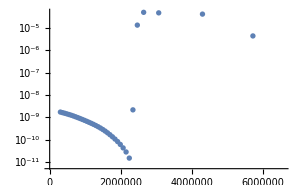
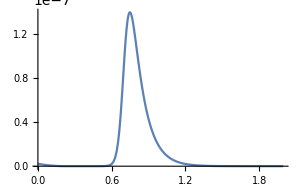
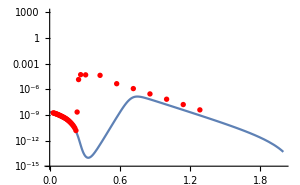

```mathematica
(*Row[{ListLogPlot[MedA, ImageSize->300], Plot[Evaluate[PAnaly[t]]/.aBck,{t, 0, c[NendR]}, ImageSize->300, PlotRange->All], Show[LogPlot[Evaluate[PAnaly[t]]/.aBck,{t, 0, c[NendR]}, ImageSize->300,PlotRange->{10^-15, 100*10^1}, FrameTicks->{{ {0,0},{c[10],10}, {c[20],20}, {c[30],30} , {c[40],40},  {c[25],25}, {c[36],36},{c[38],38}, {c[42],42} }, Automatic}], ListLogPlot[MedA, ImageSize->300,  PlotStyle->Red]]}] *)
```

```mathematica
(* Ta teleytaia 5 shmeia pou leipoun  *)
```

```mathematica
EndA4=Table[{c[N], (K[N])^3/(2Pi^2)*Evaluate[P[c[N+4]]]/.EqA[[N-4,1]]} ,{N, NendR-4, NendR-4,1}][[1]];
EndA3=Table[{c[N], (K[N])^3/(2Pi^2)*Evaluate[P[c[N+3]]]/.EqA[[N-4,1]]} ,{N, NendR-3, NendR-3,1}][[1]];
EndA2=Table[{c[N], (K[N])^3/(2Pi^2)*Evaluate[P[c[N+2]]]/.EqA[[N-4,1]]} ,{N, NendR-2, NendR-2,1}][[1]];
EndA1=Table[{c[N], (K[N])^3/(2Pi^2)*Evaluate[P[c[N+1]]]/.EqA[[N-4,1]]} ,{N, NendR-1, NendR-1,1}][[1]];
EndA0=Table[{c[N], (K[N])^3/(2Pi^2)*Evaluate[P[c[N]]]/.EqA[[N-4,1]]} ,{N, NendR, NendR,1}][[1]];
```

```mathematica
EndA={EndA4, EndA3, EndA2, EndA1, EndA0};
{EndA[[1]],EndA[[2]],EndA[[2]],EndA[[3]],EndA[[4]],EndA[[5]] };
```

```mathematica
PPSafter5=Join[MedA, {EndA4, EndA3, EndA2, EndA1, EndA0}];
```

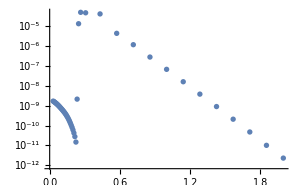
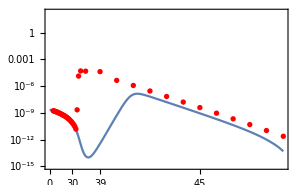
-Graphics--Graphics--Graphics-

```mathematica
(*Row[{ListLogPlot[PPSafter5, ImageSize->300], Plot[Evaluate[PAnaly[t]]/.aBck,{t, 0, c[NendR]}, ImageSize->300, PlotRange->All], Show[LogPlot[Evaluate[PAnaly[t]]/.aBck,{t, 0, c[NendR]}, ImageSize->300,PlotRange->{10^-15, 20*10^1}, Frame->True, FrameTicks->{{ {0,0},{c[10],10}, {c[20],20}, {c[30],30} , {c[40],40}, {c[25],25}, {c[39],39},{c[37],37}, {c[42],42}, {c[45],45}  }, Automatic}], ListLogPlot[PPSafter5, ImageSize->300,  PlotStyle->Red]]}] *)
```

```mathematica
(*  cDense meta!!!!!!!!!!*)
```

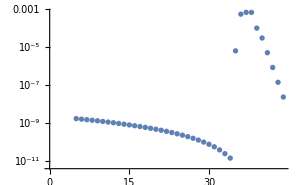
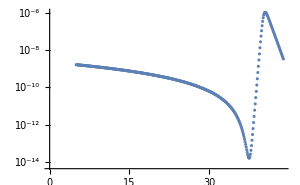
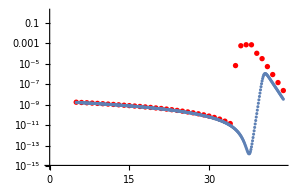

```mathematica
(*MedAN=Table[{N, (K[N])^3/(2Pi^2)*Evaluate[P[c[N+5]]]/.EqA[[N-4,1]]} ,{N, 5, Nend-5,1}];
MedANAnaly=Table[{N, Evaluate[PAnaly[c[N]]]/.aBck[[1]]} ,{N, 5, Nend-5,1}];
MedANAnalyDense=Table[{N, Evaluate[PAnaly[cDense01[10*N]]]/.aBck[[1]]} ,{N, 5, Nend-5,.1}];   (*xreiazetai to cDense01 apo pio katw*)
(* exoyme pinaka me 760 stoixeia me kathe stoixeio na antistoixei se metabolh 0.1 sta efolds *)

Row[{ListLogPlot[MedAN, ImageSize->300],ListLogPlot[MedANAnalyDense, ImageSize->300], Show[ListLogPlot[MedAN, ImageSize->300, PlotStyle->{Red, Thick}, PlotRange->{10^-15, 10^0}],ListLogPlot[MedANAnalyDense, ImageSize->300]]}] 
*)
```

```mathematica
(*    DENSE POINTS    *)
```

```mathematica
CC01=List[Table[n,{n,0,Nend, .1}]];

Row[{plotNe=Plot[{Ne[t]}, {t, 0, tend},PlotLabel->"N(t)", ImageSize->300, PlotRange->{0, Nend+2}],plotNtime=Plot[CC01, {t, 0, tend},PlotLabel->"N-T", ImageSize->300]}];
ptsNtDense01=Graphics`Mesh`FindIntersections@Show[plotNe,plotNtime];

Length[ptsNtDense01]
```

564

```mathematica
ptsNtDense01[[1]]
```

{11000.7,0.1}

```mathematica
ptsNtDense01;
```

```mathematica
NTDense01=Insert[ptsNtDense01,{0,0},1];
{NTDense01[[1]], NTDense01[[2]]}
```

{{0,0},{11000.7,0.1}}

```mathematica
cDense01[r_]:=NTDense01[[r+1,1]]; (* points (0, t1), (0.02, t2),... (75.98, t759), (630, t630) *)
```

```mathematica
{cDense01[0],  cDense01[1], cDense01[2],cDense01[3], cDense01[10*Nend] }
```

{0,11000.7,22001.8,33003.7,1.05839×10^7}

```mathematica
FBDenseTable[j_]=Table[Evaluate[f[cDense01[j]]] /.aBck, {j, 0,10*Nend, 1}];
FBD[j_]:=FBDenseTable[1][[j+1,1]]

VBDenseTable[j_]=Table[Evaluate[f'[cDense01[j]]] /.aBck,{j, 0, 10*Nend,1}];
VBD[j_]:=VBDenseTable[1][[j+1,1]];

aBDenseTable[r_]=Table[Evaluate[a[cDense01[j]]] /.aBck,{j, 0, 10*Nend, 1}];
aBD[j_]:=aBDenseTable[1][[j+1,1]];
```

```mathematica
KTD[j_]=Table[Evaluate[a'[cDense01[j]]]/.aBck,{j,0, 10*Nend,1}];
KD[j_]:=KTD[1][[j+1, 1]]        (* @ Horizon Crossing *)
```

```mathematica
kfinal=KD[Length[ptsNtDense01]]/H0*0.05
```

4.99251×10^22

```mathematica
KD[0]/H0*0.05
```

0.050004

```mathematica
(*   MUKHANOV - SASAKI   *)

RangeND=Range[50,10*Nend,1];
EqAD=NDSolve[{u''[t]+(a'[t]/a[t])u'[t]+((KD[#])^2/(a[t])^2- (a'[t]/a[t])^2*(FiTa2[t]))u[t]==0,
v''[t]+(a'[t]/a[t])v'[t]+((KD[#])^2/(a[t])^2- (a'[t]/a[t])^2*(FiTa2[t]))v[t]==0,
        f''[t]+3(a'[t]/a[t])f'[t]+dV[t]==0,
         a'[t]== a[t]/(√3)√((f'[t])^2/2+V[t]),
u[cDense01[#-50]]==1/√(2*KD[#]), u'[cDense01[#-50]]==0, v[cDense01[#-50]]==0, v'[cDense01[#-50]]==√KD[#]/(aBD[#-50]*√2), 
f[cDense01[#-50]]==FBD[#-50],  f'[cDense01[#-50]]==VBD[#-50], a[cDense01[#-50]]==aBD[#-50]},
{u,v, f, a},{t,cDense01[#-50], cDense01[10*Nend]},AccuracyGoal->15, MaxSteps->1000000]&/@RangeND;
```

NDSolve::ndsz: At t == 4.05612×10^6, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
MedAD=Table[{cDense01[j], (KD[j])^3/(2Pi^2)*Evaluate[P[cDense01[j+50]]]/.EqAD[[j-49,1]]} ,{j, 50, 10*Nend-50,1}];
```

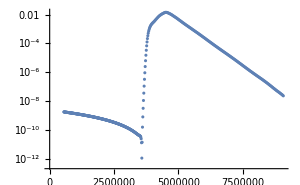
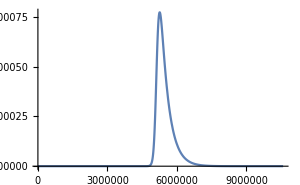
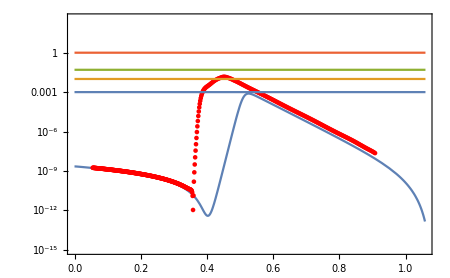

```mathematica
Row[{ListLogPlot[MedAD, ImageSize->300], Plot[Evaluate[PAnaly[t]]/.aBck,{t, 0, cDense01[10*Nend]}, ImageSize->300, PlotRange->All], Show[LogPlot[Evaluate[PAnaly[t]]/.aBck,{t, 0, cDense01[10*Nend]}, ImageSize->450,PlotRange->{10^-15, 40*10^1}, Frame->True
], ListLogPlot[MedAD, ImageSize->300,  PlotStyle->Red], LogPlot[{10^-3, 10^-2, 5*10^-2, 10^0}, {t, 0,tend}, ImageSize->500]]}]
```

```mathematica
(*MedAD=Table[{cDense01[j], (KD[j])^3/(2Pi^2)*Evaluate[P[cDense01[j+50]]]/.EqAD[[j-49,1]]} ,{j, 50, 710,1}]; *)
```

```mathematica
MedDAN         =Table[{j,  (KD[j])^3/(2Pi^2)*Evaluate[P[cDense01[j+50]]]/.EqAD[[j-49,1]]} ,{j, 50, 10*Nend-50,1}];
MedANAnaly=Table[{N, Evaluate[PAnaly[cDense01[j]]]/.aBck [[1]]} ,{j, 50, 10*Nend-50,1}];
MedANAnalyDense=Table[{j, Evaluate[PAnaly[cDense01[j]]]/.aBck[[1]]} ,{j, 50, 10*Nend-50,1}];
MedANAnalyDense=Table[{N, Evaluate[PAnaly[cDense01[10*N]]]/.aBck[[1]]} ,{N, 5, 71,.1}];  
 (*xreiazetai to cDense01 apo pio katw*)
(* exoyme pinaka me 760 stoixeia me kathe stoixeio na antistoixei se metabolh 0.1 sta efolds *) 

(*Row[{ListLogPlot[MedDAN, ImageSize->300],ListLogPlot[MedANAnalyDense, ImageSize->300], Show[ListLogPlot[MedDAN, ImageSize->400, PlotStyle->{Red, Thick}, PlotRange->{10^-15, 3000*10^-1}],ListLogPlot[MedANAnalyDense, ImageSize->400],  LogPlot[{10^-3, 10^-2, 5*10^-2, 0.1}, {N, 0,10*Nend}, ImageSize->500, PlotStyle->{{Thick, Yellow},{Thick, Blue},{Thick, Green}, {Thick, Purple}}]]}] *)
```

TimeConstrained::timc: Number of seconds 1. is not a positive machine-sized number or Infinity.

Part::partw: Part 566. of {{0,0},{11000.7,0.1},{22001.8,0.2},{33003.7,0.3},{44006.,0.4},{55008.8,0.500001},«39»,{495612.,4.5},{506641.,4.6},{517671.,4.7},{528700.,4.8},{539730.,4.9},«515»} does not exist.

TimeConstrained::timc: Number of seconds 1. is not a positive machine-sized number or Infinity.

Part::partw: Part 567. of {{0,0},{11000.7,0.1},{22001.8,0.2},{33003.7,0.3},{44006.,0.4},{55008.8,0.500001},«39»,{495612.,4.5},{506641.,4.6},{517671.,4.7},{528700.,4.8},{539730.,4.9},«515»} does not exist.

TimeConstrained::timc: Number of seconds 1. is not a positive machine-sized number or Infinity.

General::stop: Further output of TimeConstrained::timc will be suppressed during this calculation.

Part::partw: Part 568. of {{0,0},{11000.7,0.1},{22001.8,0.2},{33003.7,0.3},{44006.,0.4},{55008.8,0.500001},«39»,{495612.,4.5},{506641.,4.6},{517671.,4.7},{528700.,4.8},{539730.,4.9},«515»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
MedDAKP=Table[{Log10[KD[j]],  (KD[j])^3/(2Pi^2)*Evaluate[P[cDense01[j+50]]]/.EqAD[[j-49,1]]} ,{j, 50,10*Nend-50 ,1}];
```

```mathematica
MedAKAnaly=Table[{Log10[KD[j]], Evaluate[PAnaly[cDense01[j]]]/.aBck [[1]]} ,{j, 50, 10*Nend-50,1}];
```

```mathematica
MedDAK=Table[{j,  KD[j]} ,{j, 50, 10*Nend-50,1}];
```

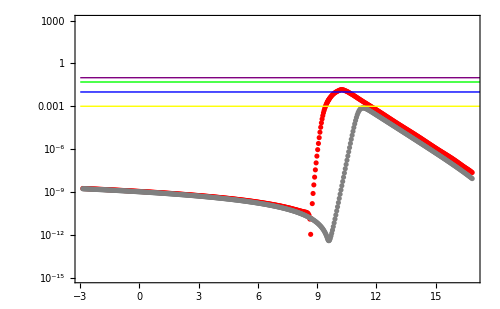

```mathematica
Show[ListLogPlot[MedDAKP, ImageSize->500, PlotStyle->{Red, Thick},  PlotRange->{10^-15, 10^3}, Frame->True,FrameStyle->{20, 20}, GridLines->Automatic ], ListLogPlot[MedAKAnaly, ImageSize->300, PlotStyle->{Gray, Thin}], LogPlot[{10^-3, 10^-2, 5*10^-2, 0.1}, {k, -3,20}, ImageSize->500, PlotStyle->{{Thick, Yellow},{Thick, Blue},{Thick, Green}, {Thick, Purple}}]]
```

```mathematica
KD[0]
```

9.0906×10^-6

```mathematica
Graphics[Circle[],Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed]];
```

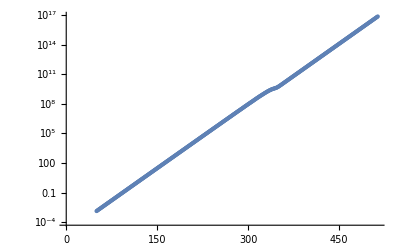

```mathematica
ListLogPlot[MedDAK]
```

```mathematica
EndKP4=Table[{ K[N]/H0*0.05, (K[N])^3/(2Pi^2)*Evaluate[P[c[N+4]]]/.EqA[[N-4,1]]} ,{N, NendR-4, NendR-4,1}][[1]];
EndKP3=Table[{ K[N]/H0*0.05, (K[N])^3/(2Pi^2)*Evaluate[P[c[N+3]]]/.EqA[[N-4,1]]} ,{N, NendR-3, NendR-3,1}][[1]];
EndKP2=Table[{ K[N]/H0*0.05, (K[N])^3/(2Pi^2)*Evaluate[P[c[N+2]]]/.EqA[[N-4,1]]} ,{N, NendR-2, NendR-2,1}][[1]];
EndKP1=Table[{ K[N]/H0*0.05, (K[N])^3/(2Pi^2)*Evaluate[P[c[N+1]]]/.EqA[[N-4,1]]} ,{N, NendR-1, NendR-1,1}][[1]];
EndKP0=Table[{ K[N]/H0*0.05, (K[N])^3/(2Pi^2)*Evaluate[P[c[N]]]/.EqA[[N-4,1]]} ,{N, NendR, NendR,1}][[1]];


EndKP4Log=Table[{Log10[ K[N]/H0*0.05], (K[N])^3/(2Pi^2)*Evaluate[P[c[N+4]]]/.EqA[[N-4,1]]} ,{N, NendR-4, NendR-4,1}][[1]];
EndKP3Log=Table[{Log10[ K[N]/H0*0.05], (K[N])^3/(2Pi^2)*Evaluate[P[c[N+3]]]/.EqA[[N-4,1]]} ,{N, NendR-3, NendR-3,1}][[1]];
EndKP2Log=Table[{ Log10[K[N]/H0*0.05], (K[N])^3/(2Pi^2)*Evaluate[P[c[N+2]]]/.EqA[[N-4,1]]} ,{N, NendR-2, NendR-2,1}][[1]];
EndKP1Log=Table[{Log10[ K[N]/H0*0.05], (K[N])^3/(2Pi^2)*Evaluate[P[c[N+1]]]/.EqA[[N-4,1]]} ,{N, NendR-1, NendR-1,1}][[1]];
EndKP0Log=Table[{ Log10[K[N]/H0*0.05], (K[N])^3/(2Pi^2)*Evaluate[P[c[N]]]/.EqA[[N-4,1]]} ,{N, NendR, NendR,1}][[1]];


KMpcPS=Table[{ KD[j]/H0*0.05, (KD[j])^3/(2Pi^2)*Evaluate[P[cDense01[j+50]]]/.EqAD[[j-49,1]]} ,{j, 50, 10*Nend-50,1}];
```

```mathematica
AllKPAnalyMpcLog=Table[{Log10[KD[j]/H0*0.05], Evaluate[PAnaly[cDense01[j]]]/.aBck [[1]]} ,{j, 0, 10*Nend,1}];
```

```mathematica
KPPS5Mpc=Join[KMpcPS, {EndKP4, EndKP3, EndKP2, EndKP1, EndKP0}];
KPPS5MpcLog=Join[MedDAKPMpc, {EndKP4Log, EndKP3Log, EndKP2Log, EndKP1Log, EndKP0Log}];
KMpcPSEnd6=Table[{ KD[j]/H0*0.05, (KD[j])^3/(2Pi^2)*Evaluate[P[cDense01[j+60]]]/.EqAD[[j-49,1]]} ,{j, 50, 10*Nend-60,1}];
KPPS5Mpc6=Join[KMpcPSEnd6, {EndKP4, EndKP3, EndKP2, EndKP1, EndKP0}];
```

```mathematica
MedDAKPMpc6=Table[{Log10[KD[j]/H0*0.05],  (KD[j])^3/(2Pi^2)*Evaluate[P[cDense01[j+60]]]/.EqAD[[j-49,1]]} ,{j, 50, 10*Nend-60,1}];
```

```mathematica
KPPS5MpcLog6=Join[MedDAKPMpc6, {EndKP4Log, EndKP3Log, EndKP2Log, EndKP1Log, EndKP0Log}];
```

```mathematica
A5PolMpc=Table[{ KD[j]/H0*0.05, (KD[j])^3/(2Pi^2)*Evaluate[P[cDense01[j+50]]]/.EqAD[[j-49,1]]} ,{j, 50, 10*Nend-50,1}];
```

```mathematica
MedDAKPMpc=Table[{Log10[KD[j]/H0*0.05],  (KD[j])^3/(2Pi^2)*Evaluate[P[cDense01[j+50]]]/.EqAD[[j-49,1]]} ,{j, 50, 10*Nend-50,1}];  (* k, PS *)
```

```mathematica
MedAKAnalyMpc=Table[{Log10[KD[j]/H0*0.05], Evaluate[PAnaly[cDense01[j]]]/.aBck [[1]]} ,{j, 50, 10*Nend-50,1}];
```

```mathematica
AllKPAnalyMpc=Table[{KD[j]/H0*0.05, Evaluate[PAnaly[cDense01[j]]]/.aBck [[1]]} ,{j, 0, 10*Nend,1}];
KPAnalyMpcLog=Table[{Log10[KD[j]/H0*0.05], Evaluate[PAnaly[cDense01[j]]]/.aBck [[1]]} ,{j, 0, 10*Nend,1}];
```

NDSolve::ioppf: Value of option MaxSteps -> 1.×10^6 should be a positive integer or Infinity.

General::stop: Further output of NDSolve::ioppf will be suppressed during this calculation.

Part::pkspec1: The expression 42.4 cannot be used as a part specification.

ReplaceAll::reps: {{NDSolve[{Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,Times[«3»]+Times[«4»]+(«1»)^(«1»)[«1»]==0,a'[t]==0.5773502691896258 a[«1»] Power[«2»],u[0]==14.2759,u'[0]==0,v[0]==0,v'[0]==0.0350241,f[0]==10.166,f'[0]==-9.38262×10^-7,a[0]==1.},{u,v,f,a},{t,0,«1»},AccuracyGoal→15.,MaxSteps→1.×10^6],«44»,NDSolve[{Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,«9»,a[1.28262×10^7]==3.49344×10^19},«3»,MaxSteps→1.×10^6]}⟦«1»⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression 43.4 cannot be used as a part specification.

ReplaceAll::reps: {{NDSolve[{Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,Times[«3»]+Times[«4»]+(«1»)^(«1»)[«1»]==0,a'[t]==0.5773502691896258 a[«1»] Power[«2»],u[0]==14.2759,u'[0]==0,v[0]==0,v'[0]==0.0350241,f[0]==10.166,f'[0]==-9.38262×10^-7,a[0]==1.},{u,v,f,a},{t,0,«1»},AccuracyGoal→15.,MaxSteps→1.×10^6],«44»,NDSolve[{Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,«9»,a[1.28262×10^7]==3.49344×10^19},«3»,MaxSteps→1.×10^6]}⟦«1»⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression 44.4 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ReplaceAll::reps: {{NDSolve[{Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,Times[«3»]+Times[«4»]+(«1»)^(«1»)[«1»]==0,a'[t]==0.5773502691896258 a[«1»] Power[«2»],u[0]==14.2759,u'[0]==0,v[0]==0,v'[0]==0.0350241,f[0]==10.166,f'[0]==-9.38262×10^-7,a[0]==1.},{u,v,f,a},{t,0,«1»},AccuracyGoal→15.,MaxSteps→1.×10^6],«44»,NDSolve[{Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,«9»,a[1.28262×10^7]==3.49344×10^19},«3»,MaxSteps→1.×10^6]}⟦«1»⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

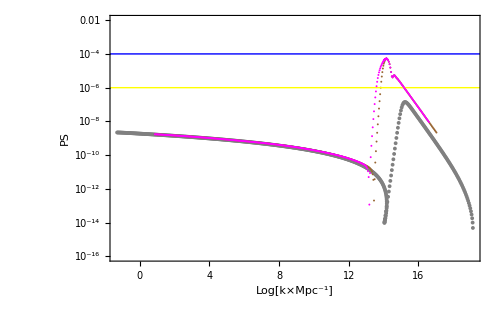

```mathematica
(*Show[ListLogPlot[KPAnalyMpcLog, ImageSize->500, PlotStyle->{Gray, Thin}, Frame->True, FrameLabel->{" Log[k×Mpc^-1]", "PS"}, FrameStyle->20, PlotRange->{10^-16, .01}],
ListLogPlot[KPPS5MpcLog, ImageSize->500, PlotStyle->{Brown}, Frame->True, FrameLabel->{" Log[k×Mpc^-1]", "PS"}, FrameStyle->20], (*ListLogPlot[MedD3040KPMpc, ImageSize->300, PlotStyle->{Red, Thick},  PlotRange->{10^-17, 10^-1}, Frame->True],   *)LogPlot[{10^-6, 10^-4, 5*10^-2, 1}, {k, -3,25}, ImageSize->300, PlotStyle->{{Thick, Yellow},{Thick, Blue},{Thick, Green}, {Thick, Purple}}], ListLogPlot[KPPS5MpcLog6, ImageSize->300, PlotStyle->{Magenta}]]*)
```

```mathematica
(*   POINTS Mukhnov-Sasaki   *)
```

```mathematica
KPPS5Mpc6=Join[KMpcPSEnd6, {EndKP4, EndKP3, EndKP2, EndKP1, EndKP0}]
```

{{7.40308,1.74356×10^-9},{8.18136,1.7324×10^-9},{9.04111,1.72127×10^-9},{9.99062,1.71017×10^-9},{11.0411,1.69907×10^-9},{12.2004,1.68803×10^-9},{13.4824,1.677×10^-9},{14.8989,1.66601×10^-9},{16.463,1.65508×10^-9},{18.1946,1.64416×10^-9},{20.1071,1.63329×10^-9},{22.2214,1.62246×10^-9},{24.5588,1.61169×10^-9},{27.1392,1.60096×10^-9},{29.9943,1.59028×10^-9},{33.1461,1.57965×10^-9},{36.6302,1.56908×10^-9},{40.4802,1.55855×10^-9},{44.7345,1.54807×10^-9},{49.4356,1.53764×10^-9},{54.6303,1.52726×10^-9},{60.3705,1.51694×10^-9},{66.7133,1.50665×10^-9},{73.7221,1.49641×10^-9},{81.4664,1.48622×10^-9},{90.0233,1.47606×10^-9},{99.4777,1.46595×10^-9},{109.924,1.45588×10^-9},{121.483,1.44583×10^-9},{134.258,1.43582×10^-9},{148.375,1.42584×10^-9},{163.977,1.4159×10^-9},{181.219,1.40599×10^-9},{200.272,1.39611×10^-9},{221.324,1.38627×10^-9},{244.585,1.37645×10^-9},{270.288,1.36667×10^-9},{298.688,1.35691×10^-9},{330.085,1.34718×10^-9},{364.769,1.33748×10^-9},{403.081,1.32781×10^-9},{445.424,1.31817×10^-9},{492.23,1.30855×10^-9},{543.92,1.29897×10^-9},{601.029,1.28941×10^-9},{664.165,1.27987×10^-9},{733.908,1.27037×10^-9},{810.939,1.2609×10^-9},{896.153,1.25144×10^-9},{990.444,1.242×10^-9},{1094.52,1.2326×10^-9},{1209.66,1.22322×10^-9},{1336.8,1.21388×10^-9},{1477.27,1.20457×10^-9},{1632.65,1.19528×10^-9},{1804.12,1.18604×10^-9},{1993.79,1.17682×10^-9},{2203.27,1.16763×10^-9},{2434.64,1.15849×10^-9},{2690.58,1.14936×10^-9},{2973.04,1.14029×10^-9},{3285.36,1.13124×10^-9},{3630.43,1.12223×10^-9},{4011.42,1.11326×10^-9},{4432.9,1.10432×10^-9},{4898.04,1.09542×10^-9},{5412.18,1.08655×10^-9},{5981.31,1.07771×10^-9},{6609.94,1.0689×10^-9},{7305.47,1.06012×10^-9},{8073.29,1.05139×10^-9},{8921.84,1.04269×10^-9},{9860.19,1.03402×10^-9},{10895.9,1.0254×10^-9},{12041.6,1.0168×10^-9},{13306.6,1.00825×10^-9},{14704.1,9.99738×10^-10},{16249.8,9.91252×10^-10},{17955.6,9.82815×10^-10},{19842.1,9.74404×10^-10},{21925.8,9.66032×10^-10},{24227.,9.577×10^-10},{26771.6,9.49396×10^-10},{29581.6,9.4113×10^-10},{32685.2,9.32901×10^-10},{36116.3,9.24704×10^-10},{39906.3,9.1654×10^-10},{44094.9,9.08408×10^-10},{48732.7,9.00296×10^-10},{53858.7,8.92213×10^-10},{59519.4,8.84171×10^-10},{65775.6,8.76159×10^-10},{72692.3,8.68178×10^-10},{80330.2,8.60237×10^-10},{88770.7,8.52329×10^-10},{98096.6,8.44453×10^-10},{108401.,8.36612×10^-10},{119787.,8.28803×10^-10},{132367.,8.2103×10^-10},{146265.,8.1329×10^-10},{161619.,8.05585×10^-10},{178583.,7.97913×10^-10},{197326.,7.90276×10^-10},{218033.,7.82672×10^-10},{240907.,7.75105×10^-10},{266181.,7.67569×10^-10},{294095.,7.60071×10^-10},{324960.,7.526×10^-10},{359129.,7.45152×10^-10},{396892.,7.37736×10^-10},{438620.,7.30355×10^-10},{484716.,7.23013×10^-10},{535644.,7.15706×10^-10},{591909.,7.08437×10^-10},{654107.,7.01199×10^-10},{722808.,6.93998×10^-10},{798683.,6.86838×10^-10},{882533.,6.79711×10^-10},{975204.,6.72619×10^-10},{1.07752×10^6,6.65566×10^-10},{1.19056×10^6,6.58551×10^-10},{1.3155×10^6,6.51568×10^-10},{1.45348×10^6,6.44623×10^-10},{1.60585×10^6,6.37717×10^-10},{1.77421×10^6,6.30846×10^-10},{1.96027×10^6,6.24008×10^-10},{2.16613×10^6,6.17197×10^-10},{2.39408×10^6,6.10408×10^-10},{2.6457×10^6,6.03663×10^-10},{2.92374×10^6,5.96953×10^-10},{3.23118×10^6,5.90274×10^-10},{3.57046×10^6,5.8364×10^-10},{3.94575×10^6,5.77034×10^-10},{4.36004×10^6,5.70469×10^-10},{4.81768×10^6,5.63942×10^-10},{5.32375×10^6,5.57445×10^-10},{5.88212×10^6,5.50992×10^-10},{6.49961×10^6,5.44568×10^-10},{7.18135×10^6,5.38183×10^-10},{7.93416×10^6,5.31836×10^-10},{8.76665×10^6,5.25519×10^-10},{9.68505×10^6,5.19245×10^-10},{1.07004×10^7,5.13002×10^-10},{1.18215×10^7,5.06796×10^-10},{1.30591×10^7,5.0063×10^-10},{1.44276×10^7,4.94493×10^-10},{1.59418×10^7,4.88383×10^-10},{1.76182×10^7,4.823×10^-10},{1.94706×10^7,4.76252×10^-10},{2.15155×10^7,4.70247×10^-10},{2.37771×10^7,4.64271×10^-10},{2.62737×10^7,4.58338×10^-10},{2.90313×10^7,4.52444×10^-10},{3.20805×10^7,4.46583×10^-10},{3.54452×10^7,4.40766×10^-10},{3.91636×10^7,4.34984×10^-10},{4.32721×10^7,4.29239×10^-10},{4.78061×10^7,4.23537×10^-10},{5.2819×10^7,4.17869×10^-10},{5.83522×10^7,4.12243×10^-10},{6.44628×10^7,4.06655×10^-10},{7.12123×10^7,4.01106×10^-10},{7.86659×10^7,3.95596×10^-10},{8.6897×10^7,3.90125×10^-10},{9.59862×10^7,3.84695×10^-10},{1.06079×10^8,3.79279×10^-10},{1.1723×10^8,3.73901×10^-10},{1.29548×10^8,3.68565×10^-10},{1.43156×10^8,3.63267×10^-10},{1.58188×10^8,3.5801×10^-10},{1.74792×10^8,3.52791×10^-10},{1.93129×10^8,3.47613×10^-10},{2.13384×10^8,3.42472×10^-10},{2.35756×10^8,3.3737×10^-10},{2.60463×10^8,3.32305×10^-10},{2.87746×10^8,3.2728×10^-10},{3.17874×10^8,3.2229×10^-10},{3.51146×10^8,3.17336×10^-10},{3.87884×10^8,3.12419×10^-10},{4.28446×10^8,3.07538×10^-10},{4.73219×10^8,3.02694×10^-10},{5.22679×10^8,2.97883×10^-10},{5.77266×10^8,2.93108×10^-10},{6.37881×10^8,2.88342×10^-10},{7.04954×10^8,2.83603×10^-10},{7.7907×10^8,2.78896×10^-10},{8.60891×10^8,2.74226×10^-10},{9.51257×10^8,2.69589×10^-10},{1.05111×10^9,2.64982×10^-10},{1.16136×10^9,2.60411×10^-10},{1.28305×10^9,2.55875×10^-10},{1.41755×10^9,2.51368×10^-10},{1.56595×10^9,2.46899×10^-10},{1.72977×10^9,2.42465×10^-10},{1.91081×10^9,2.38063×10^-10},{2.11042×10^9,2.33701×10^-10},{2.331×10^9,2.2937×10^-10},{2.57432×10^9,2.25081×10^-10},{2.84281×10^9,2.2083×10^-10},{3.13943×10^9,2.16614×10^-10},{3.46636×10^9,2.12445×10^-10},{3.82749×10^9,2.08314×10^-10},{4.22655×10^9,2.04221×10^-10},{4.67074×10^9,2.00139×10^-10},{5.16181×10^9,1.961×10^-10},{5.70342×10^9,1.92114×10^-10},{6.30195×10^9,1.88173×10^-10},{6.9626×10^9,1.84283×10^-10},{7.69151×10^9,1.80445×10^-10},{8.49708×10^9,1.76651×10^-10},{9.38518×10^9,1.72912×10^-10},{1.03659×10^10,1.69218×10^-10},{1.14483×10^10,1.65572×10^-10},{1.26417×10^10,1.61973×10^-10},{1.396×10^10,1.58414×10^-10},{1.54127×10^10,1.54902×10^-10},{1.70156×10^10,1.51426×10^-10},{1.87844×10^10,1.47984×10^-10},{2.07335×10^10,1.44578×10^-10},{2.28834×10^10,1.41199×10^-10},{2.52578×10^10,1.37843×10^-10},{2.7916×10^10,1.34468×10^-10},{3.08502×10^10,1.31132×10^-10},{3.40893×10^10,1.27846×10^-10},{3.76653×10^10,1.24664×10^-10},{4.1611×10^10,1.21481×10^-10},{4.59633×10^10,1.18193×10^-10},{5.07645×10^10,1.1491×10^-10},{5.60615×10^10,1.11776×10^-10},{6.19022×10^10,1.0884×10^-10},{6.83424×10^10,1.0608×10^-10},{7.54419×10^10,1.03396×10^-10},{8.32661×10^10,1.00658×10^-10},{9.18882×10^10,9.77775×10^-11},{1.01388×10^11,9.47755×10^-11},{1.11852×10^11,9.1747×10^-11},{1.23376×10^11,8.88681×10^-11},{1.36063×10^11,8.62702×10^-11},{1.50027×10^11,8.39274×10^-11},{1.65396×10^11,8.16872×10^-11},{1.82707×10^11,7.93055×10^-11},{2.01923×10^11,7.67824×10^-11},{2.23114×10^11,7.42682×10^-11},{2.46465×10^11,7.19542×10^-11},{2.72196×10^11,6.99228×10^-11},{3.00549×10^11,6.81024×10^-11},{3.31775×10^11,6.64031×10^-11},{3.66137×10^11,6.49488×10^-11},{4.03947×10^11,6.40148×10^-11},{4.45545×10^11,6.36567×10^-11},{4.91288×10^11,6.41304×10^-11},{5.41544×10^11,6.57081×10^-11},{5.96752×10^11,6.88437×10^-11},{6.57367×10^11,7.42424×10^-11},{7.23882×10^11,8.29849×10^-11},{7.96832×10^11,9.67462×10^-11},{8.76793×10^11,1.18056×10^-10},{9.64384×10^11,1.50683×10^-10},{1.06245×10^12,1.99193×10^-10},{1.17412×10^12,2.6738×10^-10},{1.29684×10^12,3.56051×10^-10},{1.43158×10^12,4.50646×10^-10},{1.57934×10^12,5.02532×10^-10},{1.74127×10^12,4.14894×10^-10},{1.91857×10^12,1.24166×10^-10},{2.11235×10^12,1.48703×10^-10},{2.32392×10^12,3.76112×10^-9},{2.55468×10^12,2.38285×10^-8},{2.80594×10^12,1.00682×10^-7},{3.07902×10^12,3.39813×10^-7},{3.37537×10^12,9.75796×10^-7},{3.69643×10^12,2.44522×10^-6},{4.04343×10^12,5.41443×10^-6},{4.41768×10^12,0.000010754},{4.82377×10^12,0.0000195257},{5.28196×10^12,0.0000331193},{5.77892×10^12,0.0000526972},{6.31929×10^12,0.0000792961},{6.89743×10^12,0.000114484},{7.53571×10^12,0.000160944},{8.21142×10^12,0.000219259},{8.92222×10^12,0.000291438},{9.66902×10^12,0.000377772},{1.04755×10^13,0.000485961},{1.13248×10^13,0.000612125},{1.22078×10^13,0.000759175},{1.31331×10^13,0.000935457},{1.40809×10^13,0.00112451},{1.50036×10^13,0.00132906},{1.59015×10^13,0.00153708},{1.68124×10^13,0.00176028},{1.77001×10^13,0.00199209},{1.85659×10^13,0.00223065},{1.94079×10^13,0.00246261},{2.02314×10^13,0.00270425},{2.1165×10^13,0.00298089},{2.22558×10^13,0.0033066},{2.36156×10^13,0.00371808},{2.5249×10^13,0.00423409},{2.72825×10^13,0.00483387},{2.97118×10^13,0.00556063},{3.25494×10^13,0.0063601},{3.57788×10^13,0.00720536},{3.94349×10^13,0.0080785},{4.35134×10^13,0.00895364},{4.80436×10^13,0.00980922},{5.30685×10^13,0.0106242},{5.86381×10^13,0.0114067},{6.47981×10^13,0.0121912},{7.16086×10^13,0.01301},{7.91368×10^13,0.0138276},{8.74575×10^13,0.0144024},{9.66536×10^13,0.0145196},{1.06817×10^14,0.0142536},{1.18051×10^14,0.0136805},{1.30467×10^14,0.012941},{1.44188×10^14,0.0121907},{1.59353×10^14,0.0114493},{1.76112×10^14,0.0107279},{1.94634×10^14,0.010004},{2.15103×10^14,0.00923061},{2.37726×10^14,0.00847459},{2.62728×10^14,0.00777395},{2.9036×10^14,0.00718285},{3.20897×10^14,0.00664712},{3.54646×10^14,0.006128},{3.91945×10^14,0.00560479},{4.33167×10^14,0.00511407},{4.78721×10^14,0.00468758},{5.29068×10^14,0.00429177},{5.8471×10^14,0.00391352},{6.46205×10^14,0.00357955},{7.14168×10^14,0.00327634},{7.89277×10^14,0.00299198},{8.72286×10^14,0.00274281},{9.64024×10^14,0.00250827},{1.06541×10^15,0.00230037},{1.17746×10^15,0.00210605},{1.3013×10^15,0.00193322},{1.43816×10^15,0.00177361},{1.58941×10^15,0.00162739},{1.75657×10^15,0.00149447},{1.94131×10^15,0.00137251},{2.14548×10^15,0.00126167},{2.37112×10^15,0.00115708},{2.6205×10^15,0.00106039},{2.89611×10^15,0.000971856},{3.2007×10^15,0.0008917},{3.53734×10^15,0.000816442},{3.9093×10^15,0.000747508},{4.32047×10^15,0.000685674},{4.77484×10^15,0.000628529},{5.27703×10^15,0.000575707},{5.83202×10^15,0.00052688},{6.44536×10^15,0.000479933},{7.12326×10^15,0.000440967},{7.87238×10^15,0.000402541},{8.70035×10^15,0.000367697},{9.61542×10^15,0.000335751},{1.06265×10^16,0.00030655},{1.17444×10^16,0.000279822},{1.29797×10^16,0.000255405},{1.43447×10^16,0.000233114},{1.58531×10^16,0.000212782},{1.75201×10^16,0.000194247},{1.93629×10^16,0.000177353},{2.13997×10^16,0.000161968},{2.36504×10^16,0.000147962},{2.61374×10^16,0.000135213},{2.88858×10^16,0.000123612},{3.1925×10^16,0.000113046},{3.52821×10^16,0.000103433},{3.89916×10^16,0.0000946809},{4.30928×10^16,0.0000867051},{4.76263×10^16,0.0000794344},{5.2634×10^16,0.0000728082},{5.81685×10^16,0.0000667613},{6.42886×10^16,0.0000612364},{7.10494×10^16,0.0000561894},{7.85184×10^16,0.000051575},{8.67808×10^16,0.0000473467},{9.59063×10^16,0.0000434752},{1.05989×10^17,0.0000399259},{1.17143×10^17,0.000036665},{1.29457×10^17,0.0000336734},{1.43073×10^17,0.0000309222},{1.58125×10^17,0.0000283912},{1.74746×10^17,0.0000260639},{1.93134×10^17,0.000023919},{2.13443×10^17,0.0000219449},{2.35882×10^17,0.0000201269},{2.60706×10^17,0.00001845},{2.88116×10^17,0.0000169068},{3.18411×10^17,0.0000154851},{3.51907×10^17,0.0000141754},{3.88923×10^17,0.0000129699},{4.29817×10^17,0.0000118612},{4.75014×10^17,0.0000108418},{5.24987×10^17,9.90476×10^-6},{5.80205×10^17,9.0447×10^-6},{6.41209×10^17,8.25613×10^-6},{7.08636×10^17,7.53333×10^-6},{7.83189×10^17,6.87133×10^-6},{8.65544×10^17,6.26613×10^-6},{9.56579×10^17,5.71301×10^-6},{1.05718×10^18,5.20814×10^-6},{1.16836×10^18,4.74769×10^-6},{1.29125×10^18,4.32809×10^-6},{1.42704×10^18,3.94608×10^-6},{1.57713×10^18,3.59854×10^-6},{1.74299×10^18,3.28251×10^-6},{1.92628×10^18,2.99536×10^-6},{2.12886×10^18,2.73446×10^-6},{2.3528×10^18,2.49744×10^-6},{2.60028×10^18,2.28219×10^-6},{2.87374×10^18,2.08674×10^-6},{3.17594×10^18,1.90914×10^-6},{3.50992×10^18,1.74772×10^-6},{3.87906×10^18,1.60087×10^-6},{4.28718×10^18,1.46714×10^-6},{4.73797×10^18,1.34534×10^-6},{5.23614×10^18,1.23422×10^-6},{5.78701×10^18,1.13264×10^-6},{6.39569×10^18,1.03973×10^-6},{7.06814×10^18,9.54636×10^-7},{7.81145×10^18,8.76517×10^-7},{8.63332×10^18,8.04671×10^-7},{9.54117×10^18,7.38569×10^-7},{1.05443×10^19,6.77645×10^-7},{1.16535×10^19,6.21387×10^-7},{1.28794×10^19,5.6941×10^-7},{1.42331×10^19,5.21403×10^-7},{1.57311×10^19,4.76959×10^-7},{1.73848×10^19,4.35925×10^-7},{1.92132×10^19,3.97997×10^-7},{2.12346×10^19,3.6299×10^-7},{2.34665×10^19,3.30772×10^-7},{2.59361×10^19,3.01116×10^-7},{2.86629×10^19,2.7395×10^-7},{3.16766×10^19,2.4911×10^-7},{3.50101×10^19,2.26455×10^-7},{3.86897×10^19,2.05901×10^-7},{4.2761×10^19,1.87275×10^-7},{4.72574×10^19,1.7048×10^-7},{5.22254×10^19,1.55369×10^-7},{5.77217×10^19,1.41776×10^-7},{6.37886×10^19,1.29572×10^-7},{7.04996×10^19,1.18563×10^-7},{7.79146×10^19,1.08582×10^-7},{8.61051×10^19,9.94381×10^-8},{9.51654×10^19,9.09126×10^-8},{1.05174×10^20,8.28143×10^-8},{1.16231×10^20,7.49865×10^-8},{1.28461×10^20,6.74077×10^-8},{1.41971×10^20,6.04868×10^-8},{7.03159×10^20,1.29365×10^-8},{1.91127×10^21,4.65984×10^-9},{5.1942×10^21,1.47258×10^-9},{1.40993×10^22,3.96713×10^-10},{3.75274×10^22,1.04146×10^-10}}

```mathematica
(*   POINTS ANALYTIC   *)
```

```mathematica
AllKPAnalyMpc=Table[{KD[j]/H0*0.05, Evaluate[PAnaly[cDense01[j]]]/.aBck [[1]]} ,{j, 0, 10*Nend,1}]
```

{{0.050004,2.2007×10^-9},{0.0552603,2.19874×10^-9},{0.0610691,2.19407×10^-9},{0.0674889,2.18743×10^-9},{0.074583,2.1793×10^-9},{0.0824234,2.17013×10^-9},{0.0910876,2.16013×10^-9},{0.100663,2.14962×10^-9},{0.111245,2.1387×10^-9},{0.122938,2.12747×10^-9},{0.135861,2.11601×10^-9},{0.150145,2.10444×10^-9},{0.16593,2.09279×10^-9},{0.183374,2.08108×10^-9},{0.20265,2.06931×10^-9},{0.223949,2.0575×10^-9},{0.247488,2.04573×10^-9},{0.273501,2.03397×10^-9},{0.302246,2.02222×10^-9},{0.334014,2.01048×10^-9},{0.369142,1.99875×10^-9},{0.407962,1.98704×10^-9},{0.450862,1.97535×10^-9},{0.498269,1.96368×10^-9},{0.550655,1.95203×10^-9},{0.608569,1.94056×10^-9},{0.672536,1.92892×10^-9},{0.743221,1.91731×10^-9},{0.821375,1.90594×10^-9},{0.907719,1.8945×10^-9},{1.0031,1.88297×10^-9},{1.10852,1.87155×10^-9},{1.22506,1.86032×10^-9},{1.35379,1.84894×10^-9},{1.49601,1.83755×10^-9},{1.65323,1.82635×10^-9},{1.82697,1.8152×10^-9},{2.01881,1.80381×10^-9},{2.23103,1.79285×10^-9},{2.46533,1.78164×10^-9},{2.72445,1.77041×10^-9},{3.01114,1.75955×10^-9},{3.32761,1.74833×10^-9},{3.67756,1.73737×10^-9},{4.06432,1.72648×10^-9},{4.49137,1.71535×10^-9},{4.96381,1.70463×10^-9},{5.48548,1.69368×10^-9},{6.06187,1.68272×10^-9},{6.69941,1.67211×10^-9},{7.40315,1.66118×10^-9},{8.18122,1.65046×10^-9},{9.04119,1.63985×10^-9},{9.99067,1.629×10^-9},{11.0409,1.61851×10^-9},{12.2007,1.60786×10^-9},{13.4819,1.59715×10^-9},{14.899,1.5868×10^-9},{16.4634,1.57617×10^-9},{18.1941,1.56563×10^-9},{20.1083,1.55533×10^-9},{22.2217,1.54476×10^-9},{24.5587,1.53443×10^-9},{27.1411,1.52413×10^-9},{29.9929,1.51365×10^-9},{33.1474,1.50352×10^-9},{36.631,1.49321×10^-9},{40.4809,1.48298×10^-9},{44.735,1.47278×10^-9},{49.4359,1.46261×10^-9},{54.6304,1.45248×10^-9},{60.3703,1.44239×10^-9},{66.713,1.43234×10^-9},{73.7215,1.42232×10^-9},{81.4658,1.41235×10^-9},{90.0228,1.4024×10^-9},{99.4773,1.39247×10^-9},{109.926,1.38256×10^-9},{121.486,1.37266×10^-9},{134.263,1.36285×10^-9},{148.383,1.35309×10^-9},{163.985,1.34333×10^-9},{181.224,1.33357×10^-9},{200.272,1.32384×10^-9},{221.323,1.31416×10^-9},{244.586,1.30454×10^-9},{270.296,1.29499×10^-9},{298.702,1.28544×10^-9},{330.079,1.27583×10^-9},{364.762,1.26634×10^-9},{403.096,1.25696×10^-9},{445.431,1.24748×10^-9},{492.208,1.23803×10^-9},{543.923,1.22876×10^-9},{601.046,1.21943×10^-9},{664.141,1.21007×10^-9},{733.878,1.20082×10^-9},{810.958,1.19167×10^-9},{896.209,1.18238×10^-9},{990.454,1.17322×10^-9},{1094.63,1.16416×10^-9},{1209.64,1.15491×10^-9},{1336.89,1.146×10^-9},{1477.35,1.13688×10^-9},{1632.6,1.12784×10^-9},{1804.26,1.11898×10^-9},{1993.73,1.10991×10^-9},{2203.34,1.10114×10^-9},{2434.75,1.09222×10^-9},{2690.43,1.08333×10^-9},{2973.2,1.07466×10^-9},{3285.25,1.06577×10^-9},{3630.41,1.05714×10^-9},{4011.56,1.04843×10^-9},{4432.54,1.03968×10^-9},{4898.18,1.03119×10^-9},{5412.28,1.02248×10^-9},{5981.66,1.01397×10^-9},{6610.74,1.00545×10^-9},{7305.46,9.9684×10^-10},{8074.07,9.88509×10^-10},{8922.39,9.7998×10^-10},{9860.27,9.71587×10^-10},{10896.9,9.63286×10^-10},{12041.3,9.54842×10^-10},{13307.3,9.4667×10^-10},{14704.8,9.3834×10^-10},{16249.2,9.30079×10^-10},{17956.8,9.21982×10^-10},{19841.4,9.13713×10^-10},{21926.1,9.0569×10^-10},{24227.6,8.97562×10^-10},{26770.,8.89448×10^-10},{29581.8,8.81541×10^-10},{32684.3,8.73447×10^-10},{36115.9,8.65585×10^-10},{39904.6,8.57643×10^-10},{44099.,8.49678×10^-10},{48739.6,8.41927×10^-10},{53861.,8.33996×10^-10},{59525.9,8.26272×10^-10},{65782.4,8.18504×10^-10},{72692.7,8.10705×10^-10},{80337.1,8.03128×10^-10},{88772.7,7.95382×10^-10},{98101.8,7.87813×10^-10},{108406.,7.80238×10^-10},{119785.,7.72609×10^-10},{132373.,7.65205×10^-10},{146266.,7.57681×10^-10},{161620.,7.50238×10^-10},{178583.,7.42829×10^-10},{197323.,7.35451×10^-10},{218025.,7.28106×10^-10},{240897.,7.20799×10^-10},{266164.,7.13533×10^-10},{294082.,7.06305×10^-10},{325009.,6.99095×10^-10},{359181.,6.91915×10^-10},{396937.,6.8476×10^-10},{438656.,6.77648×10^-10},{484751.,6.70568×10^-10},{535682.,6.63525×10^-10},{591957.,6.56525×10^-10},{654138.,6.49573×10^-10},{722836.,6.42651×10^-10},{798729.,6.35756×10^-10},{882570.,6.28889×10^-10},{975192.,6.22055×10^-10},{1.0775×10^6,6.15244×10^-10},{1.19057×10^6,6.08511×10^-10},{1.31548×10^6,6.0182×10^-10},{1.4534×10^6,5.95107×10^-10},{1.60577×10^6,5.88444×10^-10},{1.77417×10^6,5.8188×10^-10},{1.96047×10^6,5.75284×10^-10},{2.16658×10^6,5.68691×10^-10},{2.39441×10^6,5.62182×10^-10},{2.64618×10^6,5.55722×10^-10},{2.92421×10^6,5.49243×10^-10},{3.23138×10^6,5.42795×10^-10},{3.57108×10^6,5.3649×10^-10},{3.94592×10^6,5.30085×10^-10},{4.36041×10^6,5.23813×10^-10},{4.81818×10^6,5.17547×10^-10},{5.32362×10^6,5.11261×10^-10},{5.88266×10^6,5.05135×10^-10},{6.49946×10^6,4.98921×10^-10},{7.18128×10^6,4.92813×10^-10},{7.93445×10^6,4.86745×10^-10},{8.76576×10^6,4.80638×10^-10},{9.68515×10^6,4.74689×10^-10},{1.06995×10^7,4.68668×10^-10},{1.18203×10^7,4.62724×10^-10},{1.30587×10^7,4.56852×10^-10},{1.44285×10^7,4.50916×10^-10},{1.59466×10^7,4.45116×10^-10},{1.76222×10^7,4.39265×10^-10},{1.94737×10^7,4.33467×10^-10},{2.15207×10^7,4.27762×10^-10},{2.37798×10^7,4.22012×10^-10},{2.62772×10^7,4.16356×10^-10},{2.90361×10^7,4.10738×10^-10},{3.20816×10^7,4.051×10^-10},{3.54489×10^7,3.99576×10^-10},{3.91663×10^7,3.94045×10^-10},{4.3271×10^7,3.88527×10^-10},{4.78092×10^7,3.83122×10^-10},{5.2817×10^7,3.77687×10^-10},{5.83481×10^7,3.72295×10^-10},{6.44615×10^7,3.66998×10^-10},{7.12077×10^7,3.61679×10^-10},{7.86593×10^7,3.56417×10^-10},{8.68879×10^7,3.51191×10^-10},{9.60221×10^7,3.45978×10^-10},{1.06116×10^8,3.40801×10^-10},{1.17266×10^8,3.35661×10^-10},{1.29584×10^8,3.3056×10^-10},{1.4319×10^8,3.25494×10^-10},{1.58219×10^8,3.20464×10^-10},{1.7482×10^8,3.15477×10^-10},{1.93157×10^8,3.10531×10^-10},{2.13409×10^8,3.05621×10^-10},{2.35773×10^8,3.00742×10^-10},{2.60478×10^8,2.95918×10^-10},{2.87754×10^8,2.91119×10^-10},{3.17871×10^8,2.86353×10^-10},{3.51127×10^8,2.81626×10^-10},{3.87853×10^8,2.76948×10^-10},{4.28409×10^8,2.72315×10^-10},{4.73175×10^8,2.6771×10^-10},{5.22592×10^8,2.63136×10^-10},{5.77482×10^8,2.58569×10^-10},{6.38221×10^8,2.54063×10^-10},{7.05302×10^8,2.49584×10^-10},{7.79366×10^8,2.45125×10^-10},{8.61193×10^8,2.4072×10^-10},{9.51601×10^8,2.36372×10^-10},{1.05139×10^9,2.32035×10^-10},{1.16158×10^9,2.27738×10^-10},{1.28333×10^9,2.23507×10^-10},{1.41772×10^9,2.19298×10^-10},{1.56605×10^9,2.15116×10^-10},{1.72988×10^9,2.10989×10^-10},{1.91079×10^9,2.06913×10^-10},{2.1103×10^9,2.02838×10^-10},{2.33082×10^9,1.98855×10^-10},{2.57393×10^9,1.94864×10^-10},{2.8424×10^9,1.90937×10^-10},{3.13871×10^9,1.87053×10^-10},{3.46543×10^9,1.8318×10^-10},{3.82756×10^9,1.79382×10^-10},{4.22973×10^9,1.75553×10^-10},{4.67416×10^9,1.71787×10^-10},{5.16496×10^9,1.68065×10^-10},{5.70647×10^9,1.64357×10^-10},{6.3051×10^9,1.60732×10^-10},{6.96519×10^9,1.57109×10^-10},{7.69426×10^9,1.53545×10^-10},{8.49915×10^9,1.50028×10^-10},{9.38674×10^9,1.46527×10^-10},{1.03675×10^10,1.43103×10^-10},{1.14485×10^10,1.39689×10^-10},{1.26416×10^10,1.36324×10^-10},{1.39586×10^10,1.33017×10^-10},{1.54101×10^10,1.29725×10^-10},{1.70121×10^10,1.26492×10^-10},{1.87789×10^10,1.23301×10^-10},{2.0726×10^10,1.20134×10^-10},{2.2884×10^10,1.17018×10^-10},{2.52916×10^10,1.13896×10^-10},{2.79487×10^10,1.1081×10^-10},{3.08844×10^10,1.07788×10^-10},{3.41223×10^10,1.04791×10^-10},{3.76958×10^10,1.01841×10^-10},{4.16392×10^10,9.89358×10^-11},{4.59895×10^10,9.60738×10^-11},{5.07881×10^10,9.32547×10^-11},{5.60803×10^10,9.04785×10^-11},{6.19156×10^10,8.77449×10^-11},{6.83486×10^10,8.50541×10^-11},{7.54395×10^10,8.24063×10^-11},{8.32545×10^10,7.98024×10^-11},{9.18646×10^10,7.72404×10^-11},{1.01352×10^11,7.47255×10^-11},{1.11802×10^11,7.22543×10^-11},{1.23307×10^11,6.98225×10^-11},{1.35971×10^11,6.74334×10^-11},{1.49917×10^11,6.50896×10^-11},{1.65709×10^11,6.27296×10^-11},{1.83124×10^11,6.04129×10^-11},{2.02326×10^11,5.81405×10^-11},{2.23491×10^11,5.59132×10^-11},{2.46832×10^11,5.37388×10^-11},{2.72537×10^11,5.16057×10^-11},{3.00839×10^11,4.9516×10^-11},{3.32021×10^11,4.7479×10^-11},{3.66328×10^11,4.54849×10^-11},{4.04059×10^11,4.3534×10^-11},{4.45581×10^11,4.16347×10^-11},{4.91214×10^11,3.97794×10^-11},{5.41338×10^11,3.79674×10^-11},{5.96422×10^11,3.62057×10^-11},{6.56884×10^11,3.44891×10^-11},{7.2321×10^11,3.28169×10^-11},{7.95958×10^11,3.11918×10^-11},{8.75688×10^11,2.96125×10^-11},{9.66118×10^11,2.80277×10^-11},{1.06751×10^12,2.64618×10^-11},{1.17898×10^12,2.4947×10^-11},{1.30141×10^12,2.34829×10^-11},{1.43576×10^12,2.20692×10^-11},{1.58308×10^12,2.07061×10^-11},{1.74444×10^12,1.93933×10^-11},{1.921×10^12,1.81306×10^-11},{2.11399×10^12,1.69178×10^-11},{2.32467×10^12,1.57546×10^-11},{2.55435×10^12,1.46408×10^-11},{2.80442×10^12,1.3576×10^-11},{3.07626×10^12,1.25599×10^-11},{3.37129×10^12,1.15923×10^-11},{3.69091×10^12,1.06724×10^-11},{4.03649×10^12,9.79999×10^-12},{4.41591×10^12,8.96078×10^-12},{4.84032×10^12,8.14143×10^-12},{5.30201×10^12,7.36586×10^-12},{5.80384×10^12,6.63343×10^-12},{6.34611×10^12,5.94667×10^-12},{6.94206×10^12,5.29332×10^-12},{7.57684×10^12,4.69191×10^-12},{8.24943×10^12,4.14096×10^-12},{8.96366×10^12,3.63511×10^-12},{9.73801×10^12,3.16184×10^-12},{1.05605×10^13,2.72927×10^-12},{1.14244×10^13,2.33879×10^-12},{1.23401×10^13,1.9837×10^-12},{1.32934×10^13,1.66722×10^-12},{1.42424×10^13,1.39735×10^-12},{1.51793×10^13,1.16837×10^-12},{1.6149×10^13,9.65359×10^-13},{1.71085×10^13,7.94691×10^-13},{1.80235×10^13,6.58015×10^-13},{1.89168×10^13,5.48956×10^-13},{1.97906×10^13,4.67106×10^-13},{2.06585×10^13,4.12528×10^-13},{2.15914×10^13,3.84415×10^-13},{2.26643×10^13,3.86783×10^-13},{2.39442×10^13,4.27667×10^-13},{2.55135×10^13,5.2393×10^-13},{2.74786×10^13,7.15739×10^-13},{2.98509×10^13,1.07606×10^-12},{3.26293×10^13,1.74596×10^-12},{3.58334×10^13,3.01013×10^-12},{3.94653×10^13,5.42225×10^-12},{4.3525×10^13,1.0054×10^-11},{4.80392×10^13,1.90244×10^-11},{5.30633×10^13,3.66017×10^-11},{5.86288×10^13,7.11481×10^-11},{6.47855×10^13,1.39268×10^-10},{7.15931×10^13,2.73941×10^-10},{7.91184×10^13,5.40678×10^-10},{8.74362×10^13,1.06966×10^-9},{9.6629×10^13,2.11956×10^-9},{1.0679×10^14,4.20478×10^-9},{1.18021×10^14,8.34713×10^-9},{1.30433×10^14,1.65748×10^-8},{1.44151×10^14,3.29099×10^-8},{1.59311×10^14,6.53159×10^-8},{1.76066×10^14,1.2952×10^-7},{1.94583×10^14,2.56466×10^-7},{2.15048×10^14,5.06729×10^-7},{2.37665×10^14,9.97837×10^-7},{2.62661×10^14,1.95526×10^-6},{2.90285×10^14,3.80391×10^-6},{3.20815×10^14,7.324×10^-6},{3.54556×10^14,0.0000138943},{3.91845×10^14,0.0000258162},{4.33054×10^14,0.0000466147},{4.78598×10^14,0.0000810216},{5.28932×10^14,0.000134093},{5.84559×10^14,0.000209023},{6.46037×10^14,0.000304096},{7.13981×10^14,0.000410739},{7.89071×10^14,0.000515036},{8.72064×10^14,0.000602675},{9.63779×10^14,0.000664099},{1.06514×10^15,0.000696665},{1.17716×10^15,0.000703351},{1.30097×10^15,0.000689988},{1.43779×10^15,0.00066286},{1.589×10^15,0.000627371},{1.75612×10^15,0.000587596},{1.94081×10^15,0.00054636},{2.14492×10^15,0.000505474},{2.3705×10^15,0.000466041},{2.61981×10^15,0.000428676},{2.89534×10^15,0.000393678},{3.19983×10^15,0.000361137},{3.53636×10^15,0.000331044},{3.90831×10^15,0.000303298},{4.31936×10^15,0.000277786},{4.77362×10^15,0.000254358},{5.27569×10^15,0.000232871},{5.83051×10^15,0.000213171},{6.44372×10^15,0.000195125},{7.12144×10^15,0.000178597},{7.87036×10^15,0.00016346},{8.69815×10^15,0.000149604},{9.61299×10^15,0.000136919},{1.0624×10^16,0.000125307},{1.17413×10^16,0.000114676},{1.29761×10^16,0.000104946},{1.43408×10^16,0.0000960417},{1.58489×10^16,0.0000878925},{1.75157×10^16,0.000080432},{1.93578×10^16,0.0000736043},{2.13941×10^16,0.0000673585},{2.36443×10^16,0.000061641},{2.61309×10^16,0.0000564061},{2.88787×10^16,0.0000516144},{3.19155×10^16,0.0000472299},{3.52724×10^16,0.0000432186},{3.89828×10^16,0.0000395483},{4.30825×10^16,0.0000361874},{4.76122×10^16,0.00003311},{5.26204×10^16,0.0000302965},{5.8156×10^16,0.0000277221},{6.42706×10^16,0.0000253635},{7.10289×10^16,0.0000232055},{7.85023×10^16,0.0000212331},{8.67579×10^16,0.0000194262},{9.58797×10^16,0.0000177718},{1.05965×10^17,0.0000162593},{1.17113×10^17,0.0000148757},{1.29424×10^17,0.0000136077},{1.43038×10^17,0.000012449},{1.58084×10^17,0.0000113886},{1.747×10^17,0.0000104167},{1.93087×10^17,9.5298×10^-6},{2.13384×10^17,8.71623×10^-6},{2.35825×10^17,7.97243×10^-6},{2.60638×10^17,7.2926×10^-6},{2.88032×10^17,6.66912×10^-6},{3.18345×10^17,6.10023×10^-6},{3.51815×10^17,5.57864×10^-6},{3.88806×10^17,5.10148×10^-6},{4.29722×10^17,4.66573×10^-6},{4.74888×10^17,4.26601×10^-6},{5.24859×10^17,3.90121×10^-6},{5.80049×10^17,3.56701×10^-6},{6.41026×10^17,3.26109×10^-6},{7.08491×10^17,2.9819×10^-6},{7.82958×10^17,2.72579×10^-6},{8.65329×10^17,2.49198×10^-6},{9.56341×10^17,2.27798×10^-6},{1.05687×10^18,2.08198×10^-6},{1.16811×10^18,1.90318×10^-6},{1.2909×10^18,1.73923×10^-6},{1.42666×10^18,1.58942×10^-6},{1.57677×10^18,1.45254×10^-6},{1.7425×10^18,1.3271×10^-6},{1.92584×10^18,1.21262×10^-6},{2.12838×10^18,1.10783×10^-6},{2.35212×10^18,1.01192×10^-6},{2.59966×10^18,9.24426×10^-7},{2.87297×10^18,8.44253×10^-7},{3.17507×10^18,7.7098×10^-7},{3.50918×10^18,7.04096×10^-7},{3.87805×10^18,6.42808×10^-7},{4.28603×10^18,5.86879×10^-7},{4.73676×10^18,5.35725×10^-7},{5.23494×10^18,4.88969×10^-7},{5.7855×10^18,4.46235×10^-7},{6.39397×10^18,4.07179×10^-7},{7.06644×10^18,3.71489×10^-7},{7.80963×10^18,3.38876×10^-7},{8.63098×10^18,3.09078×10^-7},{9.5387×10^18,2.81853×10^-7},{1.05419×10^19,2.56982×10^-7},{1.16506×10^19,2.34264×10^-7},{1.2876×10^19,2.13515×10^-7},{1.423×10^19,1.94559×10^-7},{1.57264×10^19,1.77249×10^-7},{1.73803×10^19,1.61448×10^-7},{1.92086×10^19,1.47029×10^-7},{2.12289×10^19,1.33862×10^-7},{2.34613×10^19,1.2184×10^-7},{2.59284×10^19,1.10868×10^-7},{2.86549×10^19,1.00856×10^-7},{3.16697×10^19,9.17309×10^-8},{3.50003×10^19,8.34006×10^-8},{3.86803×10^19,7.5799×10^-8},{4.27485×10^19,6.88699×10^-8},{4.72461×10^19,6.2558×10^-8},{5.22145×10^19,5.67989×10^-8},{5.77045×10^19,5.15487×10^-8},{6.37739×10^19,4.67685×10^-8},{7.04831×10^19,4.24154×10^-8},{7.78944×10^19,3.84471×10^-8},{8.60842×10^19,3.4834×10^-8},{9.51401×10^19,3.1548×10^-8},{1.05147×10^20,2.85568×10^-8},{1.16203×10^20,2.58336×10^-8},{1.28422×10^20,2.33574×10^-8},{1.41933×10^20,2.11083×10^-8},{1.5686×10^20,1.90627×10^-8},{1.73353×10^20,1.72031×10^-8},{1.91584×10^20,1.55151×10^-8},{2.11741×10^20,1.39839×10^-8},{2.34007×10^20,1.25931×10^-8},{2.58611×10^20,1.13313×10^-8},{2.85813×10^20,1.01883×10^-8},{3.15872×10^20,9.15229×10^-9},{3.49093×10^20,8.21407×10^-9},{3.85807×10^20,7.36486×10^-9},{4.26384×10^20,6.59665×10^-9},{4.71227×10^20,5.90217×10^-9},{5.20786×10^20,5.27478×10^-9},{5.75557×10^20,4.7084×10^-9},{6.36082×10^20,4.19744×10^-9},{7.02968×10^20,3.73694×10^-9},{7.76898×10^20,3.32227×10^-9},{8.58604×10^20,2.94921×10^-9},{9.48902×10^20,2.61388×10^-9},{1.04869×10^21,2.31277×10^-9},{1.15896×10^21,2.04268×10^-9},{1.28084×10^21,1.80076×10^-9},{1.41552×10^21,1.58431×10^-9},{1.5644×10^21,1.39087×10^-9},{1.72892×10^21,1.21832×10^-9},{1.91074×10^21,1.06464×10^-9},{2.11169×10^21,9.27964×10^-10},{2.33375×10^21,8.06624×10^-10},{2.57914×10^21,6.99105×10^-10},{2.8503×10^21,6.04034×10^-10},{3.14998×10^21,5.20151×10^-10},{3.48117×10^21,4.4632×10^-10},{3.84717×10^21,3.81511×10^-10},{4.25162×10^21,3.24782×10^-10},{4.69858×10^21,2.75276×10^-10},{5.19238×10^21,2.32203×10^-10},{5.73801×10^21,1.94868×10^-10},{6.34121×10^21,1.62615×10^-10},{7.00774×10^21,1.34882×10^-10},{7.7441×10^21,1.11149×10^-10},{8.55751×10^21,9.09393×10^-11},{9.4559×10^21,7.38262×10^-11},{1.04479×10^22,5.94222×10^-11},{1.15432×10^22,4.73814×10^-11},{1.27532×10^22,3.73815×10^-11},{1.40915×10^22,2.9137×10^-11},{1.55675×10^22,2.24198×10^-11},{1.71942×10^22,1.70039×10^-11},{1.89848×10^22,1.26883×10^-11},{2.09527×10^22,9.29536×10^-12},{2.31099×10^22,6.66827×10^-12},{2.54711×10^22,4.66602×10^-12},{2.80505×10^22,3.16708×10^-12},{3.08421×10^22,2.07378×10^-12},{3.38066×10^22,1.30202×10^-12},{3.6867×10^22,7.75525×10^-13},{3.98576×10^22,4.29944×10^-13},{4.23443×10^22,2.17348×10^-13}}

```mathematica
CC3040=List[Table[n,{n,25,Nend, .01}]]; 

Row[{plotNe=Plot[{Ne[t]}, {t, 0, 5*tend},PlotLabel->"N(t)", ImageSize->300, PlotRange->{0, Nend+8}],plotNtime=Plot[CC3040, {t, 0,5* tend},PlotLabel->"N-T", ImageSize->300]}];

ptsNtDense3040=Graphics`Mesh`FindIntersections@Show[plotNe,plotNtime];

Length[ptsNtDense3040]
```

3141

```mathematica
cD3040[r_]:=ptsNtDense3040[[r,1]]; (* points (1, t2500), (3001, t3001),... (75.98, t759), (1000, t4499) *)

FBDenseTable3040[j_]=Table[Evaluate[f[cD3040[j]]] /.aBck, {j, 1,Length[ptsNtDense3040], 1}];
FBD3040[j_]:=FBDenseTable3040[1][[j,1]]

VBDenseTable3040[j_]=Table[Evaluate[f'[cD3040[j]]] /.aBck,{j, 1,Length[ptsNtDense3040],1}];
VBD3040[j_]:=VBDenseTable3040[1][[j,1]];

aBDenseTable3040[r_]=Table[Evaluate[a[cD3040[j]]] /.aBck,{j, 1,Length[ptsNtDense3040], 1}];
aBD3040[j_]:=aBDenseTable3040[1][[j,1]];


KTD3040[j_]=Table[Evaluate[a'[cD3040[j]]]/.aBck,{j,1, Length[ptsNtDense3040],1}];
KD3040[j_]:=KTD3040[1][[j, 1]]        (* @ Horizon Crossing *)
```

```mathematica
KD3040[2000];
```

```mathematica
RangeND3040=Range[501,Length[ptsNtDense3040],1];

EqAD3040=NDSolve[{u''[t]+(a'[t]/a[t])u'[t]+((KD3040[#])^2/(a[t])^2- (a'[t]/a[t])^2*(FiTa2[t]))u[t]==0,
v''[t]+(a'[t]/a[t])v'[t]+((KD3040[#])^2/(a[t])^2- (a'[t]/a[t])^2*(FiTa2[t]))v[t]==0,
        f''[t]+3(a'[t]/a[t])f'[t]+dV[t]==0,
         a'[t]== a[t]/(√3)√((f'[t])^2/2+V[t]),
u[cD3040[#-500]]==1/√(2*KD3040[#]), u'[cD3040[#-500]]==0, v[cD3040[#-500]]==0, v'[cD3040[#-500]]==√KD3040[#]/(aBD3040[#-500]*√2), 
f[cD3040[#-500]]==FBD3040[#-500],  f'[cD3040[#-500]]==VBD3040[#-500], a[cD3040[#-500]]==aBD3040[#-500]},
{u,v, f, a},{t,cD3040[#-500], cD3040[Length[ptsNtDense3040]]},AccuracyGoal->15, MaxSteps->1000000]&/@RangeND3040;
```

```mathematica
MedD3040=Table[{cD3040[j], (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+499]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-499,1}];
```

```mathematica
MedD3040end6=Table[{cD3040[j], (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+599]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-599,1}];
MedD3040End=Table[{cD3040[j], (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[Length[ptsNtDense3040]]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040],1}];
```

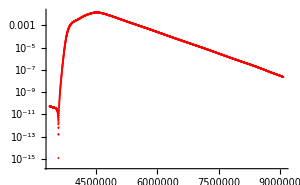
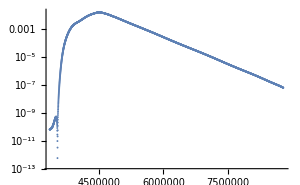
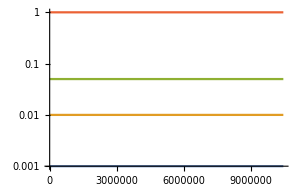
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{ListLogPlot[MedAD, ImageSize->300], Plot[Evaluate[PAnaly[t]]/.aBck,{t, 0, cDense01[10*Nend]}, ImageSize->300, PlotRange->All], ListLogPlot[MedD3040, ImageSize->300,  PlotStyle->Red],ListLogPlot[MedD3040end6, ImageSize->300], LogPlot[{10^-3, 10^-2, 5*10^-2, 1}, {t, 0, c[NendR]}  , ImageSize->300 ]  }]
```

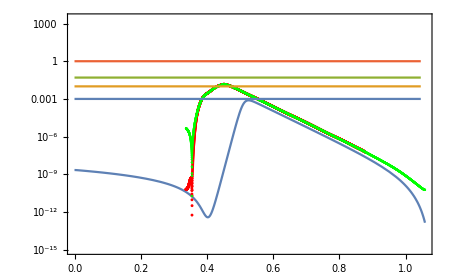
-Graphics--Graphics--Graphics-

```mathematica
Row[{ListLogPlot[MedAD, ImageSize->300], Plot[Evaluate[PAnaly[t]]/.aBck,{t, 0, cDense01[10*Nend]}, ImageSize->300, PlotRange->All], Show[LogPlot[Evaluate[PAnaly[t]]/.aBck,{t, 0, cDense01[10*Nend]}, ImageSize->450,PlotRange->{10^-15, 250*10^1}, Frame->True
], ListLogPlot[MedD3040end6, ImageSize->300,  PlotStyle->Red],  ListLogPlot[MedD3040End, ImageSize->300,  PlotStyle->Green], LogPlot[{10^-3, 10^-2, 5*10^-2, 1}, {t, 0, c[NendR]}, ImageSize->500]]}]
```

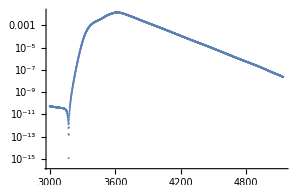
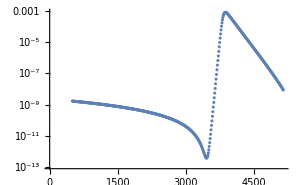
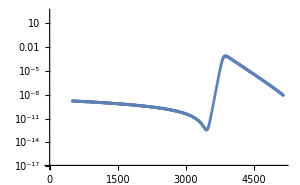

```mathematica
MedD3040N=Table[{j+2499,  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+499]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-499,1}]; (* 100*E-folds, PS  *)
(*MedANAnaly=Table[{j, Evaluate[PAnaly[cDense01[j]]]/.aBck [[1]]} ,{j, 50, 570,1}];*)
MedANAnalyDense=Table[{10*j, Evaluate[PAnaly[cDense01[j]]]/.aBck[[1]]} ,{j, 50, 10*Nend-50,1}];
(*MedANAnalyDense=Table[{N, Evaluate[PAnaly[cDense01[10*N]]]/.aBck[[1]]} ,{N, 5, 71,.1}];   (*xreiazetai to cDense01 apo pio katw*)
(* exoyme pinaka me 760 stoixeia me kathe stoixeio na antistoixei se metabolh 0.1 sta efolds *) *)

Row[{ListLogPlot[MedD3040N, ImageSize->300],ListLogPlot[MedANAnalyDense, ImageSize->300], Show[ListLogPlot[MedANAnalyDense, ImageSize->300, PlotRange->{10^-17, 2500*10^-1}], ListLogPlot[MedD3040end6, ImageSize->300,  PlotStyle->Red]]} ]
```

```mathematica
MedD3040KP=Table[{ Log10[ KD3040[j] ],  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+499]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-499,1}]; (* k, PS  *)
MedAKAnaly=Table[{Log10[KD[j]], Evaluate[PAnaly[cDense01[j]]]/.aBck [[1]]} ,{j, 50, 10*Nend-50,1}];
```

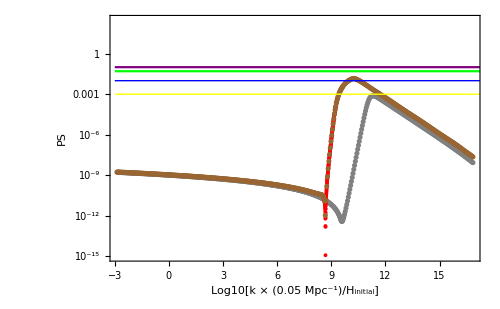

```mathematica
Show[ ListLogPlot[MedAKAnaly, ImageSize->500, PlotStyle->{Gray, Thin}, Frame->True, FrameLabel->{"Log10[k × (0.05 Mpc^-1)/H_initial]", "PS"}, FrameStyle->20,  PlotRange->{10^-15, 3000*10^-1}],ListLogPlot[MedD3040KP, ImageSize->300, PlotStyle->{Red, Thick},  PlotRange->{10^-15, 3000*10^-1}, Frame->True],   ListLogPlot[MedDAKP, ImageSize->500, PlotStyle->{Brown}], LogPlot[{10^-3, 10^-2, 5*10^-2, 0.1}, {k, -3,20}, ImageSize->300, PlotStyle->{{Thick, Yellow},{Thick, Blue},{ Green}, { Purple}} ]]
```

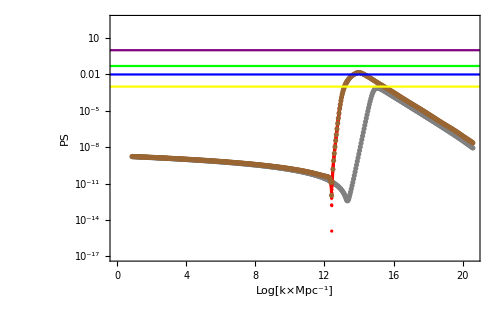
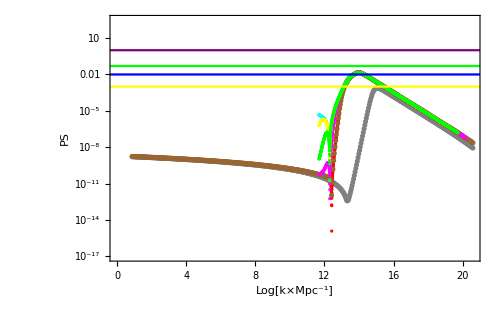

```mathematica
MedD3040KPMpc=Table[{ Log10[ KD3040[j]/H0*0.05 ],  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+499]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-499,1}]; 
MedD3040KPMpcEnd7=Table[{ Log10[ KD3040[j]/H0*0.05 ],  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+699]]]/.EqAD3040[[j-500,1]]} ,{j, 501,Length[ptsNtDense3040]-699 ,1}]; 
MedD3040KPMpcEnd8=Table[{ Log10[ KD3040[j]/H0*0.05 ],  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+799]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-799,1}]; 
MedD3040KPMpcEnd9=Table[{ Log10[ KD3040[j]/H0*0.05 ],  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+899]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-899,1}]; 
MedD3040KPMpcEnd10=Table[{ Log10[ KD3040[j]/H0*0.05 ],  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+999]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-999,1}]; 
MedD3040Nend6=Table[{j+2499,  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+599]]]/.EqAD3040[[j-500,1]]} ,{j, 501,Length[ptsNtDense3040]-599,1}]; 
MedD3040KPMpcEnd6=Table[{ Log10[ KD3040[j]/H0*0.05 ],  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+599]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-599,1}]; 


Row[{Show[ ListLogPlot[MedAKAnalyMpc, ImageSize->500, PlotStyle->{Gray, Thin}, Frame->True, FrameLabel->{" Log[k×Mpc^-1]", "PS"}, FrameStyle->20,  PlotRange->{10^-17,3000 10^-1}],ListLogPlot[MedD3040KPMpc, ImageSize->300, PlotStyle->{Red, Thick},  PlotRange->{10^-17, 10^-1}, Frame->True],   ListLogPlot[MedDAKPMpc, ImageSize->500, PlotStyle->{Brown}], LogPlot[{10^-3, 10^-2, 5*10^-2, 1}, {k, -3,25}, ImageSize->300,  PlotStyle->{{Yellow},{Blue},{Green},{Purple}}]] , Show[ ListLogPlot[MedAKAnalyMpc, ImageSize->500, PlotStyle->{Gray, Thin}, Frame->True, FrameLabel->{" Log[k×Mpc^-1]", "PS"}, FrameStyle->20,  PlotRange->{10^-17,3000 10^-1}],ListLogPlot[MedD3040KPMpc, ImageSize->300, PlotStyle->{Red},  PlotRange->{10^-17, 10^-1}, Frame->True],   ListLogPlot[MedDAKPMpc, ImageSize->500, PlotStyle->{Brown}], 
ListLogPlot[MedD3040KPMpcEnd10, ImageSize->300, PlotStyle->{Cyan}], 
ListLogPlot[MedD3040KPMpcEnd6, ImageSize->300, PlotStyle->{Magenta}],
ListLogPlot[MedD3040KPMpcEnd8, ImageSize->300, PlotStyle->{Yellow}],
ListLogPlot[MedD3040KPMpcEnd7, ImageSize->300, PlotStyle->{Green}], 
LogPlot[{10^-3, 10^-2, 5*10^-2, 1}, {k, -3,25}, ImageSize->300,  PlotStyle->{{ Yellow},{Blue},{Green},{Purple}}]]  }]
```

```mathematica
(*Dense shmeia 30-50 efolds ypologismena 7e-fodls  after horizon crossing *)
```

```mathematica
MedD3040KPMpc=Table[{  KD3040[j]/H0*0.05 ,  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[j+499]]]/.EqAD3040[[j-500,1]]} ,{j, 501, Length[ptsNtDense3040]-499,1}]
```

{{4.87832×10^11,5.54906×10^-11},{4.92673×10^11,5.5282×10^-11},{4.97558×10^11,5.50724×10^-11},{5.02488×10^11,5.48623×10^-11},{5.07466×10^11,5.46513×10^-11},{5.12493×10^11,5.44395×10^-11},{5.1757×10^11,5.42271×10^-11},{5.22697×10^11,5.40141×10^-11},{5.27873×10^11,5.3801×10^-11},{5.331×10^11,5.35874×10^-11},{5.38376×10^11,5.33738×10^-11},{5.437×10^11,5.31603×10^-11},{5.49076×10^11,5.29468×10^-11},{5.54501×10^11,5.27338×10^-11},{5.59976×10^11,5.25212×10^-11},{5.65506×10^11,5.23092×10^-11},{5.71089×10^11,5.20979×10^-11},{5.76727×10^11,5.18873×10^-11},{5.8242×10^11,5.16778×10^-11},{5.88166×10^11,5.14694×10^-11},{5.93967×10^11,5.12622×10^-11},{5.99821×10^11,5.10565×10^-11},{6.0573×10^11,5.08523×10^-11},{6.11693×10^11,5.06496×10^-11},{6.17713×10^11,5.04488×10^-11},{6.23791×10^11,5.02497×10^-11},{6.29928×10^11,5.00522×10^-11},{6.36126×10^11,4.98566×10^-11},{6.42382×10^11,4.96629×10^-11},{6.48697×10^11,4.94711×10^-11},{6.55071×10^11,4.92813×10^-11},{6.61504×10^11,4.90936×10^-11},{6.67997×10^11,4.89079×10^-11},{6.74548×10^11,4.87246×10^-11},{6.81163×10^11,4.8543×10^-11},{6.8784×10^11,4.83634×10^-11},{6.94582×10^11,4.81855×10^-11},{7.01391×10^11,4.80095×10^-11},{7.08263×10^11,4.78351×10^-11},{7.15198×10^11,4.76623×10^-11},{7.222×10^11,4.74908×10^-11},{7.29265×10^11,4.73209×10^-11},{7.36395×10^11,4.71525×10^-11},{7.43591×10^11,4.69853×10^-11},{7.50852×10^11,4.68192×10^-11},{7.58185×10^11,4.66537×10^-11},{7.65589×10^11,4.64895×10^-11},{7.73063×10^11,4.63256×10^-11},{7.80607×10^11,4.61625×10^-11},{7.88221×10^11,4.6×10^-11},{7.95905×10^11,4.58378×10^-11},{8.0366×10^11,4.56763×10^-11},{8.11487×10^11,4.5515×10^-11},{8.19383×10^11,4.53542×10^-11},{8.27352×10^11,4.51935×10^-11},{8.354×10^11,4.50327×10^-11},{8.43524×10^11,4.48726×10^-11},{8.51724×10^11,4.47127×10^-11},{8.6×10^11,4.45531×10^-11},{8.68355×10^11,4.43941×10^-11},{8.76785×10^11,4.42355×10^-11},{8.85291×10^11,4.40775×10^-11},{8.93876×10^11,4.39206×10^-11},{9.02534×10^11,4.37647×10^-11},{9.11276×10^11,4.36098×10^-11},{9.20103×10^11,4.34562×10^-11},{9.29012×10^11,4.33039×10^-11},{9.38004×10^11,4.3154×10^-11},{9.47079×10^11,4.30055×10^-11},{9.56237×10^11,4.28589×10^-11},{9.65479×10^11,4.27155×10^-11},{9.74806×10^11,4.2574×10^-11},{9.84212×10^11,4.2435×10^-11},{9.93704×10^11,4.22991×10^-11},{1.00329×10^12,4.21659×10^-11},{1.01296×10^12,4.20345×10^-11},{1.02272×10^12,4.19065×10^-11},{1.03258×10^12,4.17802×10^-11},{1.04252×10^12,4.16555×10^-11},{1.05255×10^12,4.15323×10^-11},{1.06268×10^12,4.14095×10^-11},{1.0729×10^12,4.12861×10^-11},{1.0832×10^12,4.11636×10^-11},{1.0936×10^12,4.10433×10^-11},{1.10409×10^12,4.09247×10^-11},{1.11469×10^12,4.08088×10^-11},{1.12538×10^12,4.0694×10^-11},{1.13617×10^12,4.05819×10^-11},{1.14705×10^12,4.04702×10^-11},{1.15804×10^12,4.03611×10^-11},{1.16913×10^12,4.02531×10^-11},{1.18031×10^12,4.01467×10^-11},{1.19167×10^12,4.00404×10^-11},{1.20326×10^12,3.99326×10^-11},{1.21495×10^12,3.98264×10^-11},{1.22675×10^12,3.97196×10^-11},{1.23866×10^12,3.96149×10^-11},{1.25069×10^12,3.95107×10^-11},{1.26282×10^12,3.94064×10^-11},{1.27506×10^12,3.93033×10^-11},{1.28742×10^12,3.92002×10^-11},{1.29988×10^12,3.90983×10^-11},{1.31245×10^12,3.89963×10^-11},{1.32513×10^12,3.88927×10^-11},{1.33794×10^12,3.87901×10^-11},{1.35089×10^12,3.86861×10^-11},{1.364×10^12,3.85793×10^-11},{1.37723×10^12,3.84734×10^-11},{1.39058×10^12,3.83647×10^-11},{1.40406×10^12,3.82546×10^-11},{1.41765×10^12,3.81428×10^-11},{1.43138×10^12,3.80284×10^-11},{1.44522×10^12,3.79126×10^-11},{1.45918×10^12,3.77926×10^-11},{1.47327×10^12,3.76706×10^-11},{1.48748×10^12,3.75456×10^-11},{1.50181×10^12,3.74125×10^-11},{1.51627×10^12,3.7279×10^-11},{1.53092×10^12,3.71388×10^-11},{1.54577×10^12,3.69938×10^-11},{1.56076×10^12,3.68383×10^-11},{1.57587×10^12,3.66767×10^-11},{1.59115×10^12,3.65073×10^-11},{1.60655×10^12,3.63331×10^-11},{1.62209×10^12,3.61467×10^-11},{1.63778×10^12,3.59523×10^-11},{1.6536×10^12,3.57472×10^-11},{1.66956×10^12,3.55318×10^-11},{1.68566×10^12,3.53027×10^-11},{1.7019×10^12,3.50641×10^-11},{1.71827×10^12,3.48075×10^-11},{1.73481×10^12,3.45392×10^-11},{1.75147×10^12,3.42526×10^-11},{1.76831×10^12,3.39488×10^-11},{1.7853×10^12,3.36282×10^-11},{1.80244×10^12,3.32844×10^-11},{1.81974×10^12,3.29239×10^-11},{1.83719×10^12,3.25359×10^-11},{1.8548×10^12,3.21278×10^-11},{1.87255×10^12,3.16963×10^-11},{1.89048×10^12,3.12338×10^-11},{1.90854×10^12,3.07498×10^-11},{1.92677×10^12,3.02294×10^-11},{1.94515×10^12,2.9686×10^-11},{1.96394×10^12,2.9092×10^-11},{1.983×10^12,2.84706×10^-11},{2.00223×10^12,2.78031×10^-11},{2.02163×10^12,2.71035×10^-11},{2.0412×10^12,2.63629×10^-11},{2.06097×10^12,2.55887×10^-11},{2.08091×10^12,2.47632×10^-11},{2.10102×10^12,2.38985×10^-11},{2.12131×10^12,2.2994×10^-11},{2.14177×10^12,2.20383×10^-11},{2.16243×10^12,2.10383×10^-11},{2.18326×10^12,2.00086×10^-11},{2.20426×10^12,1.89298×10^-11},{2.22545×10^12,1.78083×10^-11},{2.24681×10^12,1.66533×10^-11},{2.26836×10^12,1.54572×10^-11},{2.2901×10^12,1.42289×10^-11},{2.31204×10^12,1.29734×10^-11},{2.33418×10^12,1.1694×10^-11},{2.35651×10^12,1.0417×10^-11},{2.37906×10^12,9.11608×10^-12},{2.40181×10^12,7.83251×10^-12},{2.42473×10^12,6.57092×10^-12},{2.44785×10^12,5.34776×10^-12},{2.47116×10^12,4.1776×10^-12},{2.49467×10^12,3.09662×10^-12},{2.51838×10^12,2.11856×10^-12},{2.54228×10^12,1.28023×10^-12},{2.5664×10^12,6.17592×10^-13},{2.59072×10^12,1.7569×10^-13},{2.61527×10^12,1.21818×10^-15},{2.64001×10^12,1.53086×10^-13},{2.66498×10^12,6.95237×10^-13},{2.69015×10^12,1.70522×10^-12},{2.71554×10^12,3.27082×10^-12},{2.74117×10^12,5.49403×10^-12},{2.76699×10^12,8.48295×10^-12},{2.79303×10^12,1.23759×10^-11},{2.81928×10^12,1.72862×10^-11},{2.84575×10^12,2.34354×10^-11},{2.87245×10^12,3.10027×10^-11},{2.89935×10^12,4.01798×10^-11},{2.92647×10^12,5.12324×10^-11},{2.95385×10^12,6.44601×10^-11},{2.98144×10^12,8.01262×10^-11},{3.00926×10^12,9.86445×10^-11},{3.03732×10^12,1.20407×10^-10},{3.06561×10^12,1.45866×10^-10},{3.09414×10^12,1.75702×10^-10},{3.1229×10^12,2.10135×10^-10},{3.15256×10^12,2.5064×10^-10},{3.1834×10^12,2.98034×10^-10},{3.21452×10^12,3.52885×10^-10},{3.24587×10^12,4.16211×10^-10},{3.27752×10^12,4.89146×10^-10},{3.30943×10^12,5.72836×10^-10},{3.34159×10^12,6.68529×10^-10},{3.37403×10^12,7.78443×10^-10},{3.40681×10^12,9.04103×10^-10},{3.43981×10^12,1.04749×10^-9},{3.47313×10^12,1.21114×10^-9},{3.5067×10^12,1.39731×10^-9},{3.54055×10^12,1.60947×10^-9},{3.57474×10^12,1.85003×10^-9},{3.60915×10^12,2.12284×10^-9},{3.64384×10^12,2.43244×10^-9},{3.67885×10^12,2.78366×10^-9},{3.71414×10^12,3.18106×10^-9},{3.74971×10^12,3.63027×10^-9},{3.78556×10^12,4.13789×10^-9},{3.82171×10^12,4.7105×10^-9},{3.85822×10^12,5.35843×10^-9},{3.89497×10^12,6.08805×10^-9},{3.93202×10^12,6.90945×10^-9},{3.9694×10^12,7.8355×10^-9},{4.00704×10^12,8.88185×10^-9},{4.04505×10^12,1.00538×10^-8},{4.0833×10^12,1.13721×10^-8},{4.12185×10^12,1.28518×10^-8},{4.16073×10^12,1.45101×10^-8},{4.19993×10^12,1.63749×10^-8},{4.23942×10^12,1.84676×10^-8},{4.27925×10^12,2.08086×10^-8},{4.31936×10^12,2.34389×10^-8},{4.35982×10^12,2.63819×10^-8},{4.4006×10^12,2.96829×10^-8},{4.44166×10^12,3.33592×10^-8},{4.48306×10^12,3.74824×10^-8},{4.52475×10^12,4.20839×10^-8},{4.56679×10^12,4.7227×10^-8},{4.60915×10^12,5.29651×10^-8},{4.6518×10^12,5.93734×10^-8},{4.69482×10^12,6.65321×10^-8},{4.73817×10^12,7.44994×10^-8},{4.7818×10^12,8.33865×10^-8},{4.82581×10^12,9.3271×10^-8},{4.8701×10^12,1.04265×10^-7},{4.91472×10^12,1.16571×10^-7},{4.95975×10^12,1.30223×10^-7},{5.00502×10^12,1.45398×10^-7},{5.05067×10^12,1.62197×10^-7},{5.09661×10^12,1.80936×10^-7},{5.14293×10^12,2.01737×10^-7},{5.18959×10^12,2.24813×10^-7},{5.23655×10^12,2.50396×10^-7},{5.28384×10^12,2.78771×10^-7},{5.33151×10^12,3.10345×10^-7},{5.37952×10^12,3.45118×10^-7},{5.42787×10^12,3.83622×10^-7},{5.47652×10^12,4.26372×10^-7},{5.5255×10^12,4.73581×10^-7},{5.57491×10^12,5.25628×10^-7},{5.62458×10^12,5.83193×10^-7},{5.67459×10^12,6.46582×10^-7},{5.72499×10^12,7.16531×10^-7},{5.77573×10^12,7.93781×10^-7},{5.82682×10^12,8.79002×10^-7},{5.87821×10^12,9.73241×10^-7},{5.92994×10^12,1.07616×10^-6},{5.98206×10^12,1.1899×10^-6},{6.03453×10^12,1.3148×10^-6},{6.08729×10^12,1.45198×10^-6},{6.14044×10^12,1.60345×10^-6},{6.1939×10^12,1.76859×10^-6},{6.24779×10^12,1.95005×10^-6},{6.30194×10^12,2.14852×10^-6},{6.35643×10^12,2.36673×10^-6},{6.41131×10^12,2.60511×10^-6},{6.46654×10^12,2.86691×10^-6},{6.52206×10^12,3.15084×10^-6},{6.57798×10^12,3.46185×10^-6},{6.63419×10^12,3.80045×10^-6},{6.6908×10^12,4.17051×10^-6},{6.74775×10^12,4.57739×10^-6},{6.80499×10^12,5.01295×10^-6},{6.86263×10^12,5.49028×10^-6},{6.92055×10^12,6.01211×10^-6},{6.97886×10^12,6.5729×10^-6},{7.03751×10^12,7.18679×10^-6},{7.09645×10^12,7.84984×10^-6},{7.15578×10^12,8.56607×10^-6},{7.2154×10^12,9.33864×10^-6},{7.2754×10^12,0.0000101804},{7.33575×10^12,0.0000110881},{7.39638×10^12,0.0000120749},{7.45734×10^12,0.0000131232},{7.52151×10^12,0.0000142822},{7.5869×10^12,0.0000155512},{7.6526×10^12,0.0000168741},{7.71872×10^12,0.0000183369},{7.78521×10^12,0.0000198719},{7.852×10^12,0.0000215487},{7.91928×10^12,0.0000233329},{7.98681×10^12,0.0000252696},{8.05476×10^12,0.0000273126},{8.123×10^12,0.0000295047},{8.19164×10^12,0.0000318341},{8.26116×10^12,0.0000343704},{8.33167×10^12,0.0000370827},{8.40254×10^12,0.000039899},{8.47375×10^12,0.0000429133},{8.54532×10^12,0.0000461482},{8.61724×10^12,0.0000495561},{8.68951×10^12,0.0000531966},{8.76214×10^12,0.0000569893},{8.83508×10^12,0.0000611014},{8.90834×10^12,0.0000653821},{8.98191×10^12,0.0000699403},{9.05682×10^12,0.0000747166},{9.13322×10^12,0.0000797973},{9.20996×10^12,0.0000853135},{9.28703×10^12,0.0000907797},{9.36443×10^12,0.0000968609},{9.44217×10^12,0.000103093},{9.52021×10^12,0.000109284},{9.59869×10^12,0.000116212},{9.67738×10^12,0.000123425},{9.75628×10^12,0.000130646},{9.83548×10^12,0.000138277},{9.91496×10^12,0.000146254},{9.99473×10^12,0.000154608},{1.00748×10^13,0.000163437},{1.01552×10^13,0.000172509},{1.02357×10^13,0.000181929},{1.03165×10^13,0.000191913},{1.03975×10^13,0.000201968},{1.04788×10^13,0.000212076},{1.05603×10^13,0.000222525},{1.0642×10^13,0.000233903},{1.07241×10^13,0.000245168},{1.08088×10^13,0.000256882},{1.08938×10^13,0.000269464},{1.09792×10^13,0.000282281},{1.10647×10^13,0.000295027},{1.11504×10^13,0.00030856},{1.12362×10^13,0.000322203},{1.13223×10^13,0.000336469},{1.14085×10^13,0.000350694},{1.14949×10^13,0.000365742},{1.15815×10^13,0.000380333},{1.1669×10^13,0.000396252},{1.17578×10^13,0.000412076},{1.18467×10^13,0.000429159},{1.19359×10^13,0.000444559},{1.2025×10^13,0.000461577},{1.21144×10^13,0.000478267},{1.22037×10^13,0.000496327},{1.22932×10^13,0.000514453},{1.23826×10^13,0.00053241},{1.2472×10^13,0.000551724},{1.25626×10^13,0.000571168},{1.2656×10^13,0.000588629},{1.27492×10^13,0.000608819},{1.28426×10^13,0.000629678},{1.29359×10^13,0.000649352},{1.30288×10^13,0.000669272},{1.31219×10^13,0.000689692},{1.32152×10^13,0.000711282},{1.33079×10^13,0.000731806},{1.34007×10^13,0.000753632},{1.34933×10^13,0.000774853},{1.35858×10^13,0.00079733},{1.36782×10^13,0.000818509},{1.37704×10^13,0.000842228},{1.38622×10^13,0.000863225},{1.39541×10^13,0.000886022},{1.40457×10^13,0.000907823},{1.41368×10^13,0.000930137},{1.42279×10^13,0.000953572},{1.43187×10^13,0.000976741},{1.44132×10^13,0.00100046},{1.45079×10^13,0.00102364},{1.46022×10^13,0.00104757},{1.46962×10^13,0.00107153},{1.47896×10^13,0.00109618},{1.48829×10^13,0.00111983},{1.49758×10^13,0.00114663},{1.50682×10^13,0.00116823},{1.51602×10^13,0.00119108},{1.52536×10^13,0.00121719},{1.53478×10^13,0.00124293},{1.54418×10^13,0.00126768},{1.5535×10^13,0.00129228},{1.56279×10^13,0.00131705},{1.57201×10^13,0.00134236},{1.5812×10^13,0.00136804},{1.59031×10^13,0.00139595},{1.59938×10^13,0.00141634},{1.60875×10^13,0.00144887},{1.61821×10^13,0.00146809},{1.6276×10^13,0.00149275},{1.63694×10^13,0.00151995},{1.6462×10^13,0.0015439},{1.65539×10^13,0.001578},{1.66454×10^13,0.00159774},{1.67359×10^13,0.00162656},{1.68257×10^13,0.00165333},{1.69147×10^13,0.00167332},{1.70032×10^13,0.00169876},{1.70909×10^13,0.00172444},{1.71778×10^13,0.00174831},{1.72642×10^13,0.00177404},{1.73496×10^13,0.00180531},{1.74344×10^13,0.00182248},{1.75185×10^13,0.00184713},{1.76108×10^13,0.00187336},{1.77039×10^13,0.00190309},{1.77963×10^13,0.00192632},{1.78879×10^13,0.00195262},{1.7979×10^13,0.00198036},{1.80689×10^13,0.00200781},{1.8158×10^13,0.00202917},{1.82464×10^13,0.00205771},{1.8334×10^13,0.00208265},{1.84209×10^13,0.00210829},{1.85071×10^13,0.00213337},{1.85925×10^13,0.0021588},{1.86774×10^13,0.0021843},{1.87619×10^13,0.00220868},{1.88456×10^13,0.00223301},{1.89287×10^13,0.00225442},{1.9011×10^13,0.0022804},{1.90934×10^13,0.00230724},{1.91751×10^13,0.00233085},{1.92565×10^13,0.00235337},{1.93374×10^13,0.00238315},{1.94182×10^13,0.00240326},{1.94987×10^13,0.00243318},{1.95786×10^13,0.00245198},{1.96586×10^13,0.00247302},{1.97384×10^13,0.0024985},{1.98185×10^13,0.00252618},{1.98982×10^13,0.00254777},{1.9978×10^13,0.00256968},{2.00578×10^13,0.00259322},{2.01448×10^13,0.00262707},{2.02335×10^13,0.00264704},{2.03225×10^13,0.00267422},{2.0412×10^13,0.00269982},{2.05019×10^13,0.00272937},{2.05922×10^13,0.00275494},{2.06835×10^13,0.0027808},{2.07783×10^13,0.00280795},{2.08738×10^13,0.00284062},{2.09702×10^13,0.00287849},{2.10675×10^13,0.00289763},{2.11657×10^13,0.00292578},{2.12649×10^13,0.00295761},{2.1368×10^13,0.00298877},{2.14745×10^13,0.00301862},{2.15826×10^13,0.00305856},{2.16918×10^13,0.00308484},{2.1803×10^13,0.00311739},{2.19154×10^13,0.00315186},{2.20294×10^13,0.00319245},{2.21451×10^13,0.00322127},{2.22631×10^13,0.00325795},{2.23826×10^13,0.0032971},{2.25044×10^13,0.00333162},{2.26278×10^13,0.00336757},{2.2755×10^13,0.00340538},{2.28924×10^13,0.00345217},{2.30314×10^13,0.00349558},{2.31741×10^13,0.00353738},{2.33188×10^13,0.00357936},{2.34662×10^13,0.00362379},{2.36169×10^13,0.00366889},{2.37693×10^13,0.00371559},{2.39256×10^13,0.00377236},{2.40843×10^13,0.00381429},{2.42459×10^13,0.0038668},{2.44105×10^13,0.00391383},{2.45781×10^13,0.00396337},{2.47493×10^13,0.00401377},{2.4923×10^13,0.00406551},{2.50998×10^13,0.00412281},{2.52797×10^13,0.00417407},{2.54629×10^13,0.00422874},{2.56491×10^13,0.00428606},{2.58393×10^13,0.00434795},{2.60313×10^13,0.00440588},{2.62279×10^13,0.00446685},{2.64271×10^13,0.00452478},{2.66297×10^13,0.00458345},{2.6849×10^13,0.00465156},{2.70712×10^13,0.00472036},{2.72963×10^13,0.00478757},{2.75259×10^13,0.00485374},{2.77584×10^13,0.00492138},{2.79954×10^13,0.00500136},{2.82354×10^13,0.0050636},{2.84808×10^13,0.00513341},{2.87283×10^13,0.00521101},{2.89804×10^13,0.00529588},{2.92353×10^13,0.00535707},{2.94949×10^13,0.00543499},{2.97573×10^13,0.00550984},{3.00244×10^13,0.00558454},{3.02944×10^13,0.00566672},{3.05701×10^13,0.00574142},{3.08475×10^13,0.00582982},{3.11298×10^13,0.00590187},{3.14148×10^13,0.00598373},{3.17047×10^13,0.00606567},{3.19972×10^13,0.0061482},{3.22947×10^13,0.00622709},{3.25959×10^13,0.00631052},{3.2901×10^13,0.00639154},{3.32099×10^13,0.00647537},{3.35215×10^13,0.00655866},{3.3838×10^13,0.00664258},{3.41573×10^13,0.00672651},{3.44815×10^13,0.00681143},{3.48097×10^13,0.00689315},{3.51417×10^13,0.00698121},{3.54764×10^13,0.00706529},{3.58162×10^13,0.00715298},{3.61587×10^13,0.00723655},{3.65064×10^13,0.00732297},{3.68567×10^13,0.00741037},{3.72123×10^13,0.00750483},{3.75719×10^13,0.00758271},{3.79355×10^13,0.00766954},{3.83017×10^13,0.00775348},{3.86734×10^13,0.00784261},{3.90478×10^13,0.0079296},{3.94276×10^13,0.00801472},{3.98122×10^13,0.00810444},{4.02048×10^13,0.0081877},{4.06016×10^13,0.00827374},{4.10028×10^13,0.00836493},{4.14082×10^13,0.00845579},{4.18181×10^13,0.00854415},{4.22324×10^13,0.00863177},{4.26514×10^13,0.00871842},{4.30748×10^13,0.00880772},{4.35026×10^13,0.00889401},{4.39351×10^13,0.00897974},{4.4372×10^13,0.00906541},{4.48138×10^13,0.00915635},{4.52604×10^13,0.00924243},{4.57115×10^13,0.00932638},{4.61673×10^13,0.00941471},{4.6628×10^13,0.0095002},{4.70934×10^13,0.00958319},{4.75636×10^13,0.00967792},{4.80386×10^13,0.00975558},{4.85187×10^13,0.00983911},{4.90036×10^13,0.00992437},{4.94935×10^13,0.0100106},{4.99884×10^13,0.0100941},{5.04885×10^13,0.0101763},{5.09941×10^13,0.0102593},{5.15045×10^13,0.01034},{5.20206×10^13,0.0104217},{5.25415×10^13,0.0105117},{5.30681×10^13,0.0105863},{5.35999×10^13,0.0106661},{5.41373×10^13,0.0107468},{5.46798×10^13,0.0108275},{5.52282×10^13,0.0109072},{5.57818×10^13,0.0109907},{5.63414×10^13,0.011065},{5.69065×10^13,0.0111593},{5.74773×10^13,0.0112342},{5.80538×10^13,0.011306},{5.86365×10^13,0.0113817},{5.92246×10^13,0.0114614},{5.98188×10^13,0.0115385},{6.04193×10^13,0.0116194},{6.10255×10^13,0.0116973},{6.16382×10^13,0.0117757},{6.22568×10^13,0.0118552},{6.28818×10^13,0.0119317},{6.35129×10^13,0.0120202},{6.41506×10^13,0.0121061},{6.47953×10^13,0.0121768},{6.54459×10^13,0.0122571},{6.61027×10^13,0.0123407},{6.6767×10^13,0.0124243},{6.74375×10^13,0.0125053},{6.81153×10^13,0.0125884},{6.87995×10^13,0.0126798},{6.949×10^13,0.0127593},{7.01884×10^13,0.0128438},{7.08935×10^13,0.0129312},{7.16061×10^13,0.013017},{7.23248×10^13,0.0131054},{7.30513×10^13,0.0131899},{7.37857×10^13,0.0132769},{7.4527×10^13,0.0133642},{7.52751×10^13,0.0134485},{7.60319×10^13,0.0135366},{7.67957×10^13,0.0136211},{7.75677×10^13,0.013706},{7.8347×10^13,0.0137832},{7.91336×10^13,0.0138614},{7.99292×10^13,0.0139411},{8.07322×10^13,0.0140119},{8.15433×10^13,0.0140825},{8.23632×10^13,0.0141495},{8.31901×10^13,0.0142118},{8.40265×10^13,0.0142739},{8.48707×10^13,0.0143226},{8.57235×10^13,0.014376},{8.65848×10^13,0.0144205},{8.74547×10^13,0.0144597},{8.83334×10^13,0.0144942},{8.92216×10^13,0.0145256},{9.01175×10^13,0.0145489},{9.10236×10^13,0.0145685},{9.19381×10^13,0.014582},{9.28619×10^13,0.0145925},{9.37957×10^13,0.014597},{9.47374×10^13,0.0145978},{9.56892×10^13,0.0145946},{9.66514×10^13,0.0145875},{9.76226×10^13,0.0145765},{9.86043×10^13,0.0145622},{9.95942×10^13,0.0145447},{1.00595×10^14,0.0145242},{1.01607×10^14,0.0144991},{1.02628×10^14,0.0144728},{1.03659×10^14,0.0144439},{1.04699×10^14,0.0144118},{1.05751×10^14,0.0143781},{1.06815×10^14,0.014338},{1.07889×10^14,0.0142956},{1.08973×10^14,0.0142517},{1.10068×10^14,0.0142033},{1.11174×10^14,0.014153},{1.12291×10^14,0.0140998},{1.13421×10^14,0.0140433},{1.14561×10^14,0.013984},{1.15711×10^14,0.0139207},{1.16873×10^14,0.0138554},{1.18048×10^14,0.0137878},{1.19234×10^14,0.0137196},{1.20434×10^14,0.0136476},{1.21644×10^14,0.0135764},{1.22867×10^14,0.0135025},{1.24101×10^14,0.0134286},{1.25347×10^14,0.013355},{1.26606×10^14,0.0132808},{1.2788×10^14,0.0132058},{1.29166×10^14,0.0131319},{1.30464×10^14,0.0130577},{1.31774×10^14,0.0129837},{1.33099×10^14,0.0129095},{1.34436×10^14,0.012834},{1.35789×10^14,0.0127595},{1.37152×10^14,0.012684},{1.3853×10^14,0.0126078},{1.39922×10^14,0.0125312},{1.41328×10^14,0.0124545},{1.42748×10^14,0.012378},{1.44183×10^14,0.0122998},{1.45634×10^14,0.012222},{1.47097×10^14,0.0121446},{1.48575×10^14,0.0120679},{1.50066×10^14,0.0119928},{1.51575×10^14,0.0119174},{1.53098×10^14,0.0118444},{1.54638×10^14,0.0117712},{1.56192×10^14,0.0117002},{1.57762×10^14,0.0116288},{1.59347×10^14,0.0115578},{1.60949×10^14,0.0114878},{1.62564×10^14,0.011418},{1.642×10^14,0.0113474},{1.6585×10^14,0.0112766},{1.67516×10^14,0.0112055},{1.692×10^14,0.0111335},{1.709×10^14,0.0110616},{1.72617×10^14,0.0109895},{1.74355×10^14,0.0109169},{1.76107×10^14,0.0108446},{1.77874×10^14,0.0107722},{1.79662×10^14,0.0107},{1.81467×10^14,0.0106273},{1.8329×10^14,0.0105547},{1.85135×10^14,0.0104813},{1.86996×10^14,0.0104073},{1.88875×10^14,0.0103326},{1.90773×10^14,0.0102568},{1.9269×10^14,0.0101801},{1.94623×10^14,0.0101029},{1.96582×10^14,0.0100246},{1.98557×10^14,0.00994664},{2.00553×10^14,0.00986896},{2.02568×10^14,0.00979126},{2.04604×10^14,0.00971399},{2.0666×10^14,0.00963695},{2.08739×10^14,0.00955966},{2.10837×10^14,0.00948287},{2.12953×10^14,0.00940572},{2.15093×10^14,0.00932807},{2.17254×10^14,0.00925008},{2.19438×10^14,0.00917197},{2.21646×10^14,0.00909378},{2.23873×10^14,0.00901593},{2.26123×10^14,0.00893851},{2.28395×10^14,0.00886197},{2.30687×10^14,0.00878607},{2.33006×10^14,0.00871053},{2.3535×10^14,0.00863529},{2.37715×10^14,0.00856014},{2.40104×10^14,0.00848566},{2.42517×10^14,0.00841099},{2.44954×10^14,0.00833688},{2.47416×10^14,0.0082635},{2.49905×10^14,0.00819101},{2.52413×10^14,0.0081202},{2.5495×10^14,0.00805036},{2.57527×10^14,0.00798169},{2.60114×10^14,0.00791443},{2.62729×10^14,0.00784848},{2.65369×10^14,0.0077833},{2.68028×10^14,0.00771919},{2.70721×10^14,0.00765612},{2.73442×10^14,0.00759431},{2.7619×10^14,0.00753376},{2.78966×10^14,0.00747483},{2.81769×10^14,0.00741685},{2.84608×10^14,0.00735973},{2.87469×10^14,0.00730301},{2.90358×10^14,0.00724658},{2.93276×10^14,0.00719042},{2.96222×10^14,0.00713447},{2.99199×10^14,0.00707915},{3.02206×10^14,0.00702423},{3.05243×10^14,0.00696985},{3.08311×10^14,0.00691566},{3.11409×10^14,0.00686153},{3.14529×10^14,0.00680758},{3.1769×10^14,0.0067536},{3.20901×10^14,0.00669954},{3.24116×10^14,0.00664654},{3.27374×10^14,0.00659395},{3.30664×10^14,0.0065418},{3.33987×10^14,0.00648976},{3.37343×10^14,0.00643763},{3.40733×10^14,0.00638513},{3.44157×10^14,0.00633239},{3.47616×10^14,0.00627951},{3.51109×10^14,0.00622657},{3.54637×10^14,0.00617337},{3.58201×10^14,0.00611962},{3.61811×10^14,0.00606523},{3.65447×10^14,0.00601055},{3.6912×10^14,0.00595563},{3.72829×10^14,0.00590099},{3.76576×10^14,0.00584694},{3.80349×10^14,0.00579338},{3.84172×10^14,0.00574024},{3.88032×10^14,0.00568754},{3.91931×10^14,0.00563535},{3.9587×10^14,0.00558384},{3.99849×10^14,0.00553311},{4.03866×10^14,0.00548289},{4.07925×10^14,0.00543303},{4.12036×10^14,0.00538292},{4.16177×10^14,0.00533301},{4.20359×10^14,0.00528346},{4.24583×10^14,0.00523456},{4.2885×10^14,0.00518622},{4.3316×10^14,0.00513849},{4.37513×10^14,0.00509145},{4.41909×10^14,0.00504537},{4.4635×10^14,0.00500048},{4.50823×10^14,0.00495682},{4.55354×10^14,0.0049139},{4.5993×10^14,0.00487143},{4.64564×10^14,0.00482906},{4.69233×10^14,0.00478712},{4.73949×10^14,0.00474527},{4.78712×10^14,0.00470349},{4.83522×10^14,0.00466146},{4.88381×10^14,0.00461945},{4.93289×10^14,0.00457778},{4.98247×10^14,0.00453677},{5.03254×10^14,0.00449634},{5.0831×10^14,0.00445642},{5.13419×10^14,0.00441687},{5.18579×10^14,0.00437776},{5.23805×10^14,0.00433876},{5.29068×10^14,0.00429963},{5.34385×10^14,0.00426017},{5.3974×10^14,0.00422063},{5.45165×10^14,0.00418106},{5.50643×10^14,0.00414157},{5.56176×10^14,0.00410228},{5.61765×10^14,0.00406334},{5.67411×10^14,0.00402516},{5.73113×10^14,0.00398792},{5.78872×10^14,0.00395133},{5.84689×10^14,0.00391534},{5.90582×10^14,0.00387982},{5.96517×10^14,0.00384488},{6.02512×10^14,0.00381015},{6.08566×10^14,0.00377539},{6.14682×10^14,0.00374089},{6.2086×10^14,0.00370676},{6.27099×10^14,0.00367303},{6.334×10^14,0.00363969},{6.39747×10^14,0.00360724},{6.46176×10^14,0.00357552},{6.5267×10^14,0.00354436},{6.59229×10^14,0.00351361},{6.65872×10^14,0.00348311},{6.72564×10^14,0.00345277},{6.79323×10^14,0.00342213},{6.8615×10^14,0.0033913},{6.93045×10^14,0.00336044},{7.00009×10^14,0.00332942},{7.07044×10^14,0.0032984},{7.1415×10^14,0.0032678},{7.21326×10^14,0.00323767},{7.28574×10^14,0.00320799},{7.35896×10^14,0.00317886},{7.43292×10^14,0.00315011},{7.50762×10^14,0.00312148},{7.58327×10^14,0.00309282},{7.65948×10^14,0.00306433},{7.73624×10^14,0.00303591},{7.81398×10^14,0.00300768},{7.8925×10^14,0.00297994},{7.97181×10^14,0.00295292},{8.05193×10^14,0.00292666},{8.13285×10^14,0.00290122},{8.21458×10^14,0.00287627},{8.29712×10^14,0.00285165},{8.3805×10^14,0.00282709},{8.46472×10^14,0.00280243},{8.55004×10^14,0.00277754},{8.63596×10^14,0.00275269},{8.72273×10^14,0.00272797},{8.81039×10^14,0.00270355},{8.89894×10^14,0.00267952},{8.98837×10^14,0.00265585},{9.07844×10^14,0.00263246},{9.16965×10^14,0.00260902},{9.2618×10^14,0.00258553},{9.35489×10^14,0.00256194},{9.4489×10^14,0.0025383},{9.54386×10^14,0.00251481},{9.64003×10^14,0.00249158},{9.7369×10^14,0.00246894},{9.83476×10^14,0.00244701},{9.9336×10^14,0.00242576},{1.00334×10^15,0.00240504},{1.01342×10^15,0.00238456},{1.02361×10^15,0.00236407},{1.0339×10^15,0.00234353},{1.04429×10^15,0.002323},{1.05478×10^15,0.00230258},{1.06538×10^15,0.00228241},{1.07605×10^15,0.00226256},{1.08693×10^15,0.00224273},{1.09782×10^15,0.0022232},{1.10886×10^15,0.00220373},{1.12×10^15,0.00218429},{1.13125×10^15,0.00216484},{1.14262×10^15,0.00214529},{1.1541×10^15,0.00212568},{1.1657×10^15,0.00210633},{1.17742×10^15,0.00208755},{1.18925×10^15,0.00206949},{1.2012×10^15,0.00205205},{1.21327×10^15,0.00203491},{1.2255×10^15,0.00201758},{1.23781×10^15,0.00200019},{1.25025×10^15,0.00198285},{1.26282×10^15,0.00196568},{1.27551×10^15,0.00194871},{1.28829×10^15,0.00193187},{1.30124×10^15,0.00191493},{1.31431×10^15,0.00189815},{1.32752×10^15,0.00188163},{1.34086×10^15,0.00186528},{1.35434×10^15,0.00184901},{1.36795×10^15,0.00183258},{1.38169×10^15,0.00181619},{1.39561×10^15,0.00180021},{1.40964×10^15,0.00178489},{1.42381×10^15,0.0017701},{1.43812×10^15,0.00175548},{1.45257×10^15,0.00174071},{1.46716×10^15,0.00172593},{1.48191×10^15,0.00171115},{1.4968×10^15,0.00169643},{1.51184×10^15,0.00168162},{1.52699×10^15,0.0016668},{1.54234×10^15,0.00165213},{1.55784×10^15,0.00163778},{1.57353×10^15,0.00162373},{1.58935×10^15,0.00160996},{1.60532×10^15,0.00159646},{1.62146×10^15,0.00158324},{1.63775×10^15,0.00156997},{1.6542×10^15,0.00155659},{1.6709×10^15,0.0015431},{1.68769×10^15,0.00153003},{1.70465×10^15,0.00151743},{1.72179×10^15,0.00150468},{1.73909×10^15,0.00149146},{1.75657×10^15,0.00147806},{1.77422×10^15,0.0014657},{1.79205×10^15,0.00145412},{1.81006×10^15,0.00144198},{1.82826×10^15,0.00142904},{1.84663×10^15,0.00141649},{1.86518×10^15,0.00140575},{1.88393×10^15,0.00139485},{1.90287×10^15,0.00138249},{1.92199×10^15,0.00136929},{1.94131×10^15,0.00135774},{1.96082×10^15,0.00134767},{1.98052×10^15,0.00133658},{2.00043×10^15,0.00132395},{2.02053×10^15,0.00131162},{2.04084×10^15,0.00130192},{2.06135×10^15,0.00129241},{2.08207×10^15,0.00128111},{2.10299×10^15,0.00126851},{2.12413×10^15,0.00125745},{2.14548×10^15,0.00124811},{2.16704×10^15,0.00123794},{2.18882×10^15,0.00122623},{2.21081×10^15,0.0012145},{2.23303×10^15,0.00120502},{2.25548×10^15,0.00119596},{2.27815×10^15,0.00118573},{2.30104×10^15,0.0011745},{2.32417×10^15,0.00116405},{2.34752×10^15,0.00115467},{2.37111×10^15,0.00114488},{2.39495×10^15,0.00113442},{2.41902×10^15,0.00112433},{2.44333×10^15,0.00111497},{2.46789×10^15,0.00110554},{2.49268×10^15,0.00109599},{2.51774×10^15,0.00108655},{2.54304×10^15,0.00107692},{2.5686×10^15,0.00106737},{2.59442×10^15,0.00105845},{2.62049×10^15,0.00104981},{2.64682×10^15,0.00104044},{2.67342×10^15,0.00103125},{2.7003×10^15,0.00102297},{2.72744×10^15,0.00101459},{2.75485×10^15,0.00100508},{2.78253×10^15,0.000996155},{2.81049×10^15,0.00098837},{2.83874×10^15,0.00098017},{2.86727×10^15,0.000971176},{2.89609×10^15,0.000962916},{2.9252×10^15,0.000955424},{2.95459×10^15,0.000947093},{2.98428×10^15,0.000938417},{3.01428×10^15,0.000930631},{3.04458×10^15,0.000923429},{3.07518×10^15,0.000914135},{3.10608×10^15,0.000904326},{3.13729×10^15,0.000896837},{3.16882×10^15,0.000891452},{3.20067×10^15,0.000884267},{3.23284×10^15,0.000874249},{3.26534×10^15,0.000865529},{3.29816×10^15,0.000859681},{3.3313×10^15,0.000854565},{3.36477×10^15,0.000844993},{3.39858×10^15,0.00083412},{3.43274×10^15,0.000826979},{3.46725×10^15,0.000823408},{3.5021×10^15,0.000817914},{3.5373×10^15,0.000810509},{3.57284×10^15,0.00080358},{3.60874×10^15,0.000797192},{3.64501×10^15,0.000789137},{3.68165×10^15,0.000780496},{3.71865×10^15,0.00077507},{3.75603×10^15,0.000769939},{3.79378×10^15,0.000761719},{3.8319×10^15,0.000754838},{3.8704×10^15,0.000750099},{3.9093×10^15,0.000742901},{3.9486×10^15,0.000735024},{3.98829×10^15,0.000730036},{4.02838×10^15,0.000724688},{4.06886×10^15,0.000717156},{4.10975×10^15,0.000711272},{4.15104×10^15,0.000706445},{4.19276×10^15,0.000699339},{4.2349×10^15,0.000692773},{4.27747×10^15,0.00068811},{4.32047×10^15,0.00068238},{4.36389×10^15,0.000675841},{4.40774×10^15,0.000670451},{4.45202×10^15,0.000665273},{4.49677×10^15,0.000659158},{4.54197×10^15,0.000653522},{4.58762×10^15,0.000648369},{4.63374×10^15,0.000642746},{4.68031×10^15,0.000637238},{4.72733×10^15,0.000631932},{4.77483×10^15,0.000626536},{4.82282×10^15,0.000621295},{4.8713×10^15,0.000616001},{4.92027×10^15,0.000610611},{4.96972×10^15,0.000605586},{5.01967×10^15,0.000600526},{5.0701×10^15,0.000595094},{5.12104×10^15,0.000590045},{5.17251×10^15,0.000585342},{5.22451×10^15,0.000580063},{5.27702×10^15,0.000574782},{5.33007×10^15,0.000570302},{5.38364×10^15,0.000565422},{5.43773×10^15,0.000560035},{5.49236×10^15,0.000555449},{5.54756×10^15,0.000550985},{5.60332×10^15,0.000545808},{5.65965×10^15,0.000540912},{5.71654×10^15,0.000536701},{5.77399×10^15,0.000531919},{5.83201×10^15,0.000526861},{5.89061×10^15,0.000522639},{5.9498×10^15,0.000518251},{6.00961×10^15,0.000513309},{6.07002×10^15,0.000509551},{6.13103×10^15,0.000507525},{6.19266×10^15,0.000503903},{6.25489×10^15,0.000497849},{6.31773×10^15,0.000491437},{6.38121×10^15,0.000486003},{6.44535×10^15,0.00048071},{6.51014×10^15,0.000477676},{6.57558×10^15,0.000474461},{6.64167×10^15,0.000471582},{6.70842×10^15,0.000467358},{6.77582×10^15,0.000462014},{6.8439×10^15,0.000457252},{6.91269×10^15,0.000453013},{6.98217×10^15,0.00044984},{7.05236×10^15,0.000446274},{7.12325×10^15,0.000442391},{7.19484×10^15,0.000438084},{7.26713×10^15,0.000434181},{7.34014×10^15,0.000430372},{7.41391×10^15,0.000426602},{7.48843×10^15,0.000422867},{7.56371×10^15,0.000419134},{7.63974×10^15,0.000415404},{7.71652×10^15,0.000411784},{7.79407×10^15,0.000408126},{7.87237×10^15,0.000404486},{7.95148×10^15,0.000400935},{8.0314×10^15,0.00039737},{8.11213×10^15,0.000393849},{8.19368×10^15,0.000390385},{8.27604×10^15,0.000386899},{8.3592×10^15,0.000383479},{8.44319×10^15,0.000380081},{8.52803×10^15,0.000376699},{8.61374×10^15,0.000373363},{8.70033×10^15,0.000370044},{8.78778×10^15,0.000366756},{8.87611×10^15,0.000363493},{8.96532×10^15,0.000360268},{9.0554×10^15,0.000357055},{9.14638×10^15,0.000353884},{9.2383×10^15,0.000350735},{9.33116×10^15,0.000347606},{9.42496×10^15,0.000344506},{9.5197×10^15,0.000341414},{9.61538×10^15,0.000338385},{9.712×10^15,0.000335384},{9.80957×10^15,0.000332387},{9.90815×10^15,0.00032942},{1.00077×10^16,0.000326488},{1.01083×10^16,0.000323572},{1.021×10^16,0.000320681},{1.03126×10^16,0.000317816},{1.04162×10^16,0.000314975},{1.05208×10^16,0.000312161},{1.06265×10^16,0.00030937},{1.07332×10^16,0.000306604},{1.08411×10^16,0.00030386},{1.09501×10^16,0.000301138},{1.10603×10^16,0.000298439},{1.11715×10^16,0.000295763},{1.12838×10^16,0.000293111},{1.13973×10^16,0.000290482},{1.15118×10^16,0.000287878},{1.16275×10^16,0.000285297},{1.17443×10^16,0.000282738},{1.18622×10^16,0.000280204},{1.19813×10^16,0.00027769},{1.21017×10^16,0.000275197},{1.22233×10^16,0.000272724},{1.23462×10^16,0.000270274},{1.24704×10^16,0.000267846},{1.25958×10^16,0.00026544},{1.27225×10^16,0.000263051},{1.28504×10^16,0.000260682},{1.29795×10^16,0.000258336},{1.311×10^16,0.000256015},{1.32417×10^16,0.000253712},{1.33746×10^16,0.000251429},{1.35089×10^16,0.000249167},{1.36446×10^16,0.000246925},{1.37818×10^16,0.0002447},{1.39203×10^16,0.000242495},{1.40603×10^16,0.000240309},{1.42017×10^16,0.000238143},{1.43445×10^16,0.000235996},{1.44887×10^16,0.000233867},{1.46344×10^16,0.000231758},{1.47815×10^16,0.000229669},{1.49299×10^16,0.000227599},{1.50798×10^16,0.000225547},{1.52313×10^16,0.000223514},{1.53843×10^16,0.0002215},{1.55389×10^16,0.000219502},{1.56951×10^16,0.000217521},{1.58529×10^16,0.000215556},{1.60124×10^16,0.00021361},{1.61734×10^16,0.00021168},{1.6336×10^16,0.000209769},{1.65002×10^16,0.000207874},{1.66661×10^16,0.000205998},{1.68335×10^16,0.000204138},{1.70025×10^16,0.000202297},{1.71732×10^16,0.000200472},{1.73457×10^16,0.000198662},{1.75201×10^16,0.000196868},{1.76962×10^16,0.00019509},{1.78741×10^16,0.000193327},{1.80539×10^16,0.000191579},{1.82354×10^16,0.000189847},{1.84188×10^16,0.000188132},{1.8604×10^16,0.000186433},{1.87909×10^16,0.000184749},{1.89797×10^16,0.00018308},{1.91703×10^16,0.000181427},{1.93628×10^16,0.00017979},{1.95573×10^16,0.000178167},{1.97538×10^16,0.000176559},{1.99524×10^16,0.000174965},{2.0153×10^16,0.000173383},{2.03557×10^16,0.000171816},{2.05604×10^16,0.000170262},{2.07671×10^16,0.000168724},{2.09759×10^16,0.000167202},{2.11867×10^16,0.000165692},{2.13996×10^16,0.000164195},{2.16145×10^16,0.000162713},{2.18315×10^16,0.000161245},{2.20508×10^16,0.000159791},{2.22724×10^16,0.00015835},{2.24962×10^16,0.00015692},{2.27224×10^16,0.000155502},{2.29509×10^16,0.000154098},{2.31817×10^16,0.000152707},{2.34148×10^16,0.000151329},{2.36502×10^16,0.000149964},{2.3888×10^16,0.00014861},{2.4128×10^16,0.000147269},{2.43703×10^16,0.000145942},{2.46149×10^16,0.000144629},{2.4862×10^16,0.000143326},{2.51118×10^16,0.000142035},{2.53642×10^16,0.000140754},{2.56192×10^16,0.000139485},{2.58769×10^16,0.000138227},{2.61371×10^16,0.00013698},{2.64×10^16,0.000135745},{2.66655×10^16,0.000134523},{2.69337×10^16,0.000133311},{2.72045×10^16,0.000132111},{2.74779×10^16,0.000130922},{2.77539×10^16,0.000129744},{2.80326×10^16,0.000128578},{2.83139×10^16,0.000127423},{2.85982×10^16,0.000126278},{2.88855×10^16,0.000125143},{2.91758×10^16,0.000124018},{2.94691×10^16,0.000122903},{2.97655×10^16,0.000121798},{3.00649×10^16,0.000120703},{3.03673×10^16,0.000119618},{3.06727×10^16,0.000118543},{3.09811×10^16,0.000117478},{3.12926×10^16,0.000116422},{3.16071×10^16,0.000115379},{3.19246×10^16,0.000114344},{3.22451×10^16,0.000113319},{3.25687×10^16,0.000112305},{3.28957×10^16,0.000111299},{3.32262×10^16,0.000110302},{3.35601×10^16,0.000109314},{3.38976×10^16,0.000108334},{3.42384×10^16,0.000107364},{3.45828×10^16,0.000106402},{3.49307×10^16,0.000105449},{3.5282×10^16,0.000104505},{3.56368×10^16,0.000103569},{3.5995×10^16,0.000102643},{3.63568×10^16,0.000101725},{3.6722×10^16,0.000100817},{3.70907×10^16,0.000099917},{3.74629×10^16,0.0000990259},{3.78391×10^16,0.0000981424},{3.82192×10^16,0.0000972669},{3.86033×10^16,0.0000963989},{3.89915×10^16,0.0000955385},{3.93836×10^16,0.000094686},{3.97797×10^16,0.0000938413},{4.01798×10^16,0.0000930043},{4.05839×10^16,0.0000921753},{4.09921×10^16,0.0000913537},{4.14042×10^16,0.00009054},{4.18203×10^16,0.0000897343},{4.22404×10^16,0.0000889363},{4.26645×10^16,0.000088146},{4.30926×10^16,0.0000873634},{4.35253×10^16,0.0000865875},{4.39625×10^16,0.0000858183},{4.44044×10^16,0.000085056},{4.48509×10^16,0.0000843005},{4.53019×10^16,0.0000835517},{4.57576×10^16,0.0000828097},{4.62178×10^16,0.0000820745},{4.66827×10^16,0.0000813461},{4.71521×10^16,0.0000806246},{4.76261×10^16,0.0000799101},{4.81047×10^16,0.0000792021},{4.8588×10^16,0.000078501},{4.90758×10^16,0.0000778067},{4.95683×10^16,0.0000771194},{5.0066×10^16,0.0000764378},{5.0569×10^16,0.0000757621},{5.10772×10^16,0.0000750924},{5.15908×10^16,0.0000744285},{5.21096×10^16,0.0000737706},{5.26337×10^16,0.0000731185},{5.31631×10^16,0.0000724727},{5.36978×10^16,0.0000718328},{5.42378×10^16,0.0000711986},{5.47832×10^16,0.0000705705},{5.53337×10^16,0.0000699486},{5.58896×10^16,0.0000693325},{5.64507×10^16,0.0000687224},{5.70172×10^16,0.0000681182},{5.75897×10^16,0.0000675192},{5.81682×10^16,0.0000669251},{5.87529×10^16,0.0000663365},{5.93436×10^16,0.000065753},{5.99404×10^16,0.0000651746},{6.05433×10^16,0.0000646017},{6.11522×10^16,0.0000640337},{6.17673×10^16,0.000063471},{6.23884×10^16,0.0000629134},{6.30156×10^16,0.0000623615},{6.36489×10^16,0.0000618145},{6.42882×10^16,0.0000612729},{6.49336×10^16,0.0000607364},{6.55853×10^16,0.000060205},{6.62438×10^16,0.0000596781},{6.69093×10^16,0.0000591558},{6.75818×10^16,0.0000586379},{6.82613×10^16,0.0000581247},{6.89478×10^16,0.000057616},{6.96413×10^16,0.0000571118},{7.03417×10^16,0.0000566122},{7.10492×10^16,0.0000561172},{7.17636×10^16,0.0000556268},{7.24851×10^16,0.0000551409},{7.32135×10^16,0.0000546597},{7.39489×10^16,0.0000541829},{7.46914×10^16,0.0000537107},{7.54407×10^16,0.0000532432},{7.61978×10^16,0.0000527797},{7.69631×10^16,0.0000523197},{7.77365×10^16,0.0000518645},{7.85181×10^16,0.0000514124},{7.93077×10^16,0.0000509646},{8.01055×10^16,0.0000505207},{8.09114×10^16,0.0000500807},{8.17255×10^16,0.0000496446},{8.25476×10^16,0.0000492125},{8.33779×10^16,0.0000487845},{8.42163×10^16,0.0000483604},{8.50628×10^16,0.0000479399},{8.59175×10^16,0.0000475239},{8.67803×10^16,0.0000471117},{8.76512×10^16,0.0000467033},{8.85303×10^16,0.0000462989},{8.94189×10^16,0.0000458978},{9.03169×10^16,0.0000455001},{9.12245×10^16,0.0000451057},{9.21417×10^16,0.0000447147},{9.30684×10^16,0.000044327},{9.40046×10^16,0.0000439426},{9.49503×10^16,0.0000435617},{9.59056×10^16,0.0000431841},{9.68704×10^16,0.0000428101},{9.78447×10^16,0.0000424394},{9.88286×10^16,0.0000420721},{9.9822×10^16,0.0000417082},{1.00825×10^17,0.0000413476},{1.01837×10^17,0.0000409906},{1.02859×10^17,0.0000406369},{1.03891×10^17,0.0000402864},{1.04934×10^17,0.000039939},{1.05988×10^17,0.0000395944},{1.07053×10^17,0.0000392525},{1.08129×10^17,0.0000389136},{1.09217×10^17,0.0000385775},{1.10315×10^17,0.0000382445},{1.11425×10^17,0.0000379142},{1.12546×10^17,0.0000375869},{1.13678×10^17,0.0000372625},{1.14822×10^17,0.0000369411},{1.15976×10^17,0.0000366225},{1.17142×10^17,0.0000363069},{1.18319×10^17,0.0000359942},{1.19507×10^17,0.0000356845},{1.20707×10^17,0.0000353776},{1.21917×10^17,0.0000350735},{1.23141×10^17,0.0000347721},{1.24378×10^17,0.000034473},{1.25628×10^17,0.0000341763},{1.26891×10^17,0.0000338821},{1.28167×10^17,0.0000335905},{1.29456×10^17,0.0000333014},{1.30758×10^17,0.0000330147},{1.32074×10^17,0.0000327305},{1.33403×10^17,0.0000324488},{1.34744×10^17,0.0000321695},{1.36099×10^17,0.000031893},{1.37467×10^17,0.0000316188},{1.38849×10^17,0.0000313472},{1.40243×10^17,0.0000310781},{1.4165×10^17,0.0000308115},{1.43071×10^17,0.0000305473},{1.44507×10^17,0.0000302854},{1.45958×10^17,0.0000300253},{1.47425×10^17,0.0000297676},{1.48907×10^17,0.000029512},{1.50405×10^17,0.0000292584},{1.51918×10^17,0.000029007},{1.53446×10^17,0.0000287578},{1.5499×10^17,0.0000285106},{1.56549×10^17,0.0000282657},{1.58124×10^17,0.000028023},{1.59714×10^17,0.0000277822},{1.61319×10^17,0.0000275439},{1.6294×10^17,0.0000273075},{1.64576×10^17,0.0000270735},{1.66228×10^17,0.0000268415},{1.67895×10^17,0.0000266117},{1.6958×10^17,0.0000263837},{1.71283×10^17,0.0000261574},{1.73005×10^17,0.0000259331},{1.74744×10^17,0.0000257106},{1.76501×10^17,0.0000254899},{1.78277×10^17,0.000025271},{1.8007×10^17,0.0000250537},{1.81882×10^17,0.0000248388},{1.83712×10^17,0.0000246255},{1.8556×10^17,0.0000244141},{1.87426×10^17,0.0000242045},{1.8931×10^17,0.0000239968},{1.91212×10^17,0.000023791},{1.93132×10^17,0.0000235871},{1.9507×10^17,0.000023385},{1.97027×10^17,0.0000231847},{1.99004×10^17,0.000022986},{2.01003×10^17,0.0000227889},{2.03023×10^17,0.0000225934},{2.05064×10^17,0.0000223995},{2.07126×10^17,0.0000222071},{2.0921×10^17,0.0000220163},{2.11314×10^17,0.0000218271},{2.1344×10^17,0.0000216395},{2.15588×10^17,0.0000214536},{2.17756×10^17,0.0000212692},{2.19946×10^17,0.0000210863},{2.22157×10^17,0.0000209054},{2.24389×10^17,0.0000207259},{2.26642×10^17,0.000020548},{2.28917×10^17,0.0000203717},{2.31213×10^17,0.000020197},{2.33533×10^17,0.0000200237},{2.35879×10^17,0.0000198518},{2.38249×10^17,0.0000196812},{2.40644×10^17,0.0000195119},{2.43064×10^17,0.0000193441},{2.45509×10^17,0.0000191776},{2.47979×10^17,0.0000190125},{2.50474×10^17,0.0000188488},{2.52994×10^17,0.0000186865},{2.55539×10^17,0.0000185256},{2.58108×10^17,0.0000183661},{2.60703×10^17,0.0000182079},{2.63322×10^17,0.0000180512},{2.65967×10^17,0.000017896},{2.68636×10^17,0.0000177421},{2.71331×10^17,0.0000175895},{2.74056×10^17,0.0000174381},{2.76809×10^17,0.0000172878},{2.79591×10^17,0.0000171389},{2.82403×10^17,0.0000169911},{2.85243×10^17,0.0000168444},{2.88111×10^17,0.0000166991},{2.91009×10^17,0.0000165549},{2.93936×10^17,0.000016412},{2.96891×10^17,0.0000162703},{2.99875×10^17,0.0000161298},{3.02889×10^17,0.0000159906},{3.05931×10^17,0.0000158526},{3.09001×10^17,0.0000157158},{3.12103×10^17,0.0000155802},{3.15238×10^17,0.0000154456},{3.18406×10^17,0.0000153121},{3.21607×10^17,0.0000151796},{3.24841×10^17,0.0000150482},{3.28108×10^17,0.000014918},{3.31408×10^17,0.0000147888},{3.34741×10^17,0.0000146606},{3.38107×10^17,0.0000145337},{3.41506×10^17,0.0000144078},{3.44938×10^17,0.0000142829},{3.48403×10^17,0.0000141592},{3.51901×10^17,0.0000140365},{3.55433×10^17,0.000013915},{3.59002×10^17,0.0000137944},{3.62609×10^17,0.0000136747},{3.66254×10^17,0.000013556},{3.69937×10^17,0.0000134382},{3.73657×10^17,0.0000133214},{3.77415×10^17,0.0000132056},{3.81211×10^17,0.0000130908},{3.85045×10^17,0.0000129768},{3.88916×10^17,0.0000128639},{3.92825×10^17,0.000012752},{3.96772×10^17,0.0000126411},{4.00757×10^17,0.0000125312},{4.0478×10^17,0.0000124221},{4.08843×10^17,0.000012314},{4.1295×10^17,0.0000122067},{4.171×10^17,0.0000121003},{4.21293×10^17,0.0000119948},{4.25529×10^17,0.0000118901},{4.29809×10^17,0.0000117862},{4.34132×10^17,0.0000116833},{4.38498×10^17,0.0000115811},{4.42907×10^17,0.0000114799},{4.4736×10^17,0.0000113795},{4.51856×10^17,0.0000112801},{4.56395×10^17,0.0000111814},{4.60977×10^17,0.0000110837},{4.65604×10^17,0.0000109868},{4.70279×10^17,0.0000108907},{4.75004×10^17,0.0000107953},{4.79779×10^17,0.0000107007},{4.84603×10^17,0.0000106069},{4.89477×10^17,0.0000105138},{4.94399×10^17,0.0000104215},{4.99372×10^17,0.0000103299},{5.04394×10^17,0.0000102392},{5.09465×10^17,0.0000101492},{5.14586×10^17,0.00001006},{5.19756×10^17,9.97156×10^-6},{5.24976×10^17,9.88397×10^-6},{5.30245×10^17,9.79714×10^-6},{5.35568×10^17,9.71102×10^-6},{5.40948×10^17,9.62558×10^-6},{5.46385×10^17,9.54079×10^-6},{5.51878×10^17,9.45671×10^-6},{5.57427×10^17,9.37325×10^-6},{5.63034×10^17,9.29054×10^-6},{5.68696×10^17,9.20856×10^-6},{5.74416×10^17,9.12722×10^-6},{5.80192×10^17,9.04658×10^-6},{5.86024×10^17,8.9666×10^-6},{5.91913×10^17,8.88737×10^-6},{5.97859×10^17,8.80883×10^-6},{6.03862×10^17,8.73096×10^-6},{6.09922×10^17,8.65385×10^-6},{6.16048×10^17,8.57733×10^-6},{6.22237×10^17,8.50139×10^-6},{6.28492×10^17,8.42607×10^-6},{6.34812×10^17,8.35135×10^-6},{6.41196×10^17,8.27726×10^-6},{6.47645×10^17,8.20372×10^-6},{6.54158×10^17,8.13093×10^-6},{6.60737×10^17,8.05868×10^-6},{6.6738×10^17,7.98711×10^-6},{6.74088×10^17,7.91614×10^-6},{6.8086×10^17,7.84579×10^-6},{6.87698×10^17,7.77607×10^-6},{6.946×10^17,7.707×10^-6},{7.01574×10^17,7.63848×10^-6},{7.08621×10^17,7.57052×10^-6},{7.15743×10^17,7.50308×10^-6},{7.22939×10^17,7.43623×10^-6},{7.30209×10^17,7.36987×10^-6},{7.37553×10^17,7.30411×10^-6},{7.44971×10^17,7.23892×10^-6},{7.52463×10^17,7.17423×10^-6},{7.60029×10^17,7.11017×10^-6},{7.67669×10^17,7.04663×10^-6},{7.75384×10^17,6.98368×10^-6},{7.83172×10^17,6.92126×10^-6},{7.91035×10^17,6.85945×10^-6},{7.98981×10^17,6.79811×10^-6},{8.07011×10^17,6.73728×10^-6},{8.15122×10^17,6.67693×10^-6},{8.23316×10^17,6.61714×10^-6},{8.31592×10^17,6.55781×10^-6},{8.3995×10^17,6.49901×10^-6},{8.4839×10^17,6.44074×10^-6},{8.56914×10^17,6.38299×10^-6},{8.65525×10^17,6.32568×10^-6},{8.74224×10^17,6.26891×10^-6},{8.83012×10^17,6.21258×10^-6},{8.91888×10^17,6.15676×10^-6},{9.00853×10^17,6.10142×10^-6},{9.09906×10^17,6.04655×10^-6},{9.19047×10^17,5.99217×10^-6},{9.28282×10^17,5.93826×10^-6},{9.37612×10^17,5.8848×10^-6},{9.47037×10^17,5.83179×10^-6},{9.56556×10^17,5.77924×10^-6},{9.66171×10^17,5.72716×10^-6},{9.75881×10^17,5.67555×10^-6},{9.85686×10^17,5.62438×10^-6},{9.9559×10^17,5.57364×10^-6},{1.0056×10^18,5.52332×10^-6},{1.0157×10^18,5.47348×10^-6},{1.02591×10^18,5.42403×10^-6},{1.03623×10^18,5.37501×10^-6},{1.04664×10^18,5.32643×10^-6},{1.05716×10^18,5.2783×10^-6},{1.06778×10^18,5.23058×10^-6},{1.07851×10^18,5.18329×10^-6},{1.08935×10^18,5.13635×10^-6},{1.1003×10^18,5.08986×10^-6},{1.11136×10^18,5.04375×10^-6},{1.12253×10^18,4.99806×10^-6},{1.13381×10^18,4.95279×10^-6},{1.1452×10^18,4.9079×10^-6},{1.15671×10^18,4.86342×10^-6},{1.16833×10^18,4.8193×10^-6},{1.18008×10^18,4.77559×10^-6},{1.19194×10^18,4.73224×10^-6},{1.20392×10^18,4.68928×10^-6},{1.21602×10^18,4.64671×10^-6},{1.22824×10^18,4.60451×10^-6},{1.24058×10^18,4.5627×10^-6},{1.25305×10^18,4.52122×10^-6},{1.26564×10^18,4.48013×10^-6},{1.27836×10^18,4.43939×10^-6},{1.29121×10^18,4.39899×10^-6},{1.30419×10^18,4.35897×10^-6},{1.3173×10^18,4.31933×10^-6},{1.33053×10^18,4.28003×10^-6},{1.3439×10^18,4.24108×10^-6},{1.35741×10^18,4.20245×10^-6},{1.37106×10^18,4.16416×10^-6},{1.38484×10^18,4.12624×10^-6},{1.39876×10^18,4.08864×10^-6},{1.41281×10^18,4.05136×10^-6},{1.427×10^18,4.01446×10^-6},{1.44134×10^18,3.97786×10^-6},{1.45583×10^18,3.94156×10^-6},{1.47047×10^18,3.90561×10^-6},{1.48525×10^18,3.86996×10^-6},{1.50018×10^18,3.83465×10^-6},{1.51525×10^18,3.79965×10^-6},{1.53047×10^18,3.76498×10^-6},{1.54585×10^18,3.73061×10^-6},{1.56139×10^18,3.69655×10^-6},{1.57709×10^18,3.66279×10^-6},{1.59294×10^18,3.6293×10^-6},{1.60895×10^18,3.59615×10^-6},{1.62512×10^18,3.56329×10^-6},{1.64145×10^18,3.53074×10^-6},{1.65793×10^18,3.4985×10^-6},{1.67458×10^18,3.46654×10^-6},{1.69141×10^18,3.43485×10^-6},{1.70842×10^18,3.40343×10^-6},{1.7256×10^18,3.3723×10^-6},{1.74295×10^18,3.3414×10^-6},{1.76048×10^18,3.31085×10^-6},{1.77818×10^18,3.28056×10^-6},{1.79605×10^18,3.25053×10^-6},{1.8141×10^18,3.2208×10^-6},{1.83233×10^18,3.19134×10^-6},{1.85073×10^18,3.16215×10^-6},{1.86931×10^18,3.13326×10^-6},{1.88809×10^18,3.10459×10^-6},{1.90706×10^18,3.07618×10^-6},{1.92623×10^18,3.04803×10^-6},{1.9456×10^18,3.02012×10^-6},{1.96516×10^18,2.99245×10^-6},{1.98493×10^18,2.96504×10^-6},{2.00489×10^18,2.9379×10^-6},{2.02504×10^18,2.91099×10^-6},{2.04539×10^18,2.88435×10^-6},{2.06594×10^18,2.85795×10^-6},{2.08669×10^18,2.83181×10^-6},{2.10764×10^18,2.8059×10^-6},{2.12881×10^18,2.78024×10^-6},{2.1502×10^18,2.75479×10^-6},{2.17182×10^18,2.72957×10^-6},{2.19365×10^18,2.70458×10^-6},{2.21571×10^18,2.67982×10^-6},{2.23799×10^18,2.65528×10^-6},{2.2605×10^18,2.63095×10^-6},{2.28322×10^18,2.60687×10^-6},{2.30617×10^18,2.58301×10^-6},{2.32934×10^18,2.55938×10^-6},{2.35274×10^18,2.53598×10^-6},{2.37643×10^18,2.51274×10^-6},{2.4003×10^18,2.48977×10^-6},{2.42442×10^18,2.46699×10^-6},{2.44879×10^18,2.44442×10^-6},{2.47341×10^18,2.42206×10^-6},{2.49828×10^18,2.39989×10^-6},{2.52341×10^18,2.37793×10^-6},{2.54878×10^18,2.35619×10^-6},{2.57441×10^18,2.33464×10^-6},{2.60029×10^18,2.3133×10^-6},{2.62641×10^18,2.29216×10^-6},{2.65279×10^18,2.27123×10^-6},{2.67942×10^18,2.25052×10^-6},{2.70633×10^18,2.22997×10^-6},{2.73353×10^18,2.2096×10^-6},{2.761×10^18,2.18944×10^-6},{2.78876×10^18,2.16943×10^-6},{2.81681×10^18,2.14962×10^-6},{2.84514×10^18,2.12999×10^-6},{2.87375×10^18,2.11056×10^-6},{2.90264×10^18,2.09129×10^-6},{2.93182×10^18,2.07221×10^-6},{2.96128×10^18,2.05332×10^-6},{2.99102×10^18,2.03461×10^-6},{3.02105×10^18,2.01609×10^-6},{3.05139×10^18,1.99773×10^-6},{3.08205×10^18,1.97956×10^-6},{3.11303×10^18,1.96152×10^-6},{3.14432×10^18,1.94365×10^-6},{3.17594×10^18,1.92595×10^-6},{3.20788×10^18,1.90842×10^-6},{3.24014×10^18,1.89104×10^-6},{3.27272×10^18,1.87381×10^-6},{3.30562×10^18,1.8568×10^-6},{3.33884×10^18,1.83992×10^-6},{3.37238×10^18,1.82321×10^-6},{3.40623×10^18,1.80666×10^-6},{3.44044×10^18,1.79027×10^-6},{3.475×10^18,1.77402×10^-6},{3.50993×10^18,1.75792×10^-6},{3.54522×10^18,1.74197×10^-6},{3.58087×10^18,1.72617×10^-6},{3.61688×10^18,1.71051×10^-6},{3.65325×10^18,1.695×10^-6},{3.68998×10^18,1.67964×10^-6},{3.72708×10^18,1.66442×10^-6},{3.76453×10^18,1.64935×10^-6},{3.80235×10^18,1.63443×10^-6},{3.84053×10^18,1.61967×10^-6},{3.87908×10^18,1.60503×10^-6},{3.91804×10^18,1.59053×10^-6},{3.95741×10^18,1.57617×10^-6},{3.99719×10^18,1.56193×10^-6},{4.03739×10^18,1.54782×10^-6},{4.07799×10^18,1.53384×10^-6},{4.11901×10^18,1.51999×10^-6},{4.16044×10^18,1.50628×10^-6},{4.20228×10^18,1.4927×10^-6},{4.24453×10^18,1.47923×10^-6},{4.2872×10^18,1.46592×10^-6},{4.33027×10^18,1.45272×10^-6},{4.37376×10^18,1.43965×10^-6},{4.41766×10^18,1.42672×10^-6},{4.462×10^18,1.41392×10^-6},{4.50682×10^18,1.40122×10^-6},{4.55211×10^18,1.38864×10^-6},{4.59787×10^18,1.37616×10^-6},{4.64411×10^18,1.36381×10^-6},{4.69082×10^18,1.35158×10^-6},{4.738×10^18,1.33944×10^-6},{4.78565×10^18,1.32743×10^-6},{4.83378×10^18,1.31553×10^-6},{4.88238×10^18,1.30376×10^-6},{4.93146×10^18,1.29208×10^-6},{4.981×10^18,1.28053×10^-6},{5.03102×10^18,1.2691×10^-6},{5.08151×10^18,1.25777×10^-6},{5.13253×10^18,1.24655×10^-6},{5.18408×10^18,1.23544×10^-6},{5.23618×10^18,1.22442×10^-6},{5.28882×10^18,1.2135×10^-6},{5.34201×10^18,1.20267×10^-6},{5.39574×10^18,1.19196×10^-6},{5.45001×10^18,1.18133×10^-6},{5.50482×10^18,1.17083×10^-6},{5.56018×10^18,1.1604×10^-6},{5.61609×10^18,1.15008×10^-6},{5.67253×10^18,1.13986×10^-6},{5.72952×10^18,1.12975×10^-6},{5.78705×10^18,1.11973×10^-6},{5.84513×10^18,1.10981×10^-6},{5.90381×10^18,1.09998×10^-6},{5.96312×10^18,1.09024×10^-6},{6.02305×10^18,1.08059×10^-6},{6.0836×10^18,1.07102×10^-6},{6.14478×10^18,1.06154×10^-6},{6.20659×10^18,1.05216×10^-6},{6.26902×10^18,1.04285×10^-6},{6.33207×10^18,1.03363×10^-6},{6.39574×10^18,1.0245×10^-6},{6.46005×10^18,1.01548×10^-6},{6.52497×10^18,1.00651×10^-6},{6.59052×10^18,9.97646×10^-7},{6.6567×10^18,9.88863×10^-7},{6.7235×10^18,9.80175×10^-7},{6.79101×10^18,9.71563×10^-7},{6.85923×10^18,9.63015×10^-7},{6.92817×10^18,9.54557×10^-7},{6.99782×10^18,9.46166×10^-7},{7.0682×10^18,9.37861×10^-7},{7.13929×10^18,9.29619×10^-7},{7.2111×10^18,9.21466×10^-7},{7.28363×10^18,9.13382×10^-7},{7.35687×10^18,9.0538×10^-7},{7.43083×10^18,8.9745×10^-7},{7.50551×10^18,8.89599×10^-7},{7.58091×10^18,8.81819×10^-7},{7.65703×10^18,8.74122×10^-7},{7.73387×10^18,8.66496×10^-7},{7.81152×10^18,8.5894×10^-7},{7.89×10^18,8.51446×10^-7},{7.9693×10^18,8.44014×10^-7},{8.04943×10^18,8.36653×10^-7},{8.13038×10^18,8.29364×10^-7},{8.21216×10^18,8.22134×10^-7},{8.29476×10^18,8.14972×10^-7},{8.37818×10^18,8.07879×10^-7},{8.46243×10^18,8.00848×10^-7},{8.54751×10^18,7.93885×10^-7},{8.6334×10^18,7.86992×10^-7},{8.72013×10^18,7.8016×10^-7},{8.80768×10^18,7.734×10^-7},{8.89607×10^18,7.66695×10^-7},{8.9854×10^18,7.60059×10^-7},{9.07567×10^18,7.53473×10^-7},{9.16689×10^18,7.46943×10^-7},{9.25906×10^18,7.40473×10^-7},{9.35218×10^18,7.34064×10^-7},{9.44625×10^18,7.27704×10^-7},{9.54126×10^18,7.21407×10^-7},{9.63722×10^18,7.1517×10^-7},{9.73413×10^18,7.08988×10^-7},{9.83199×10^18,7.0286×10^-7},{9.93079×10^18,6.96799×10^-7},{1.00305×10^19,6.90791×10^-7},{1.01312×10^19,6.84837×10^-7},{1.02329×10^19,6.78946×10^-7},{1.03357×10^19,6.73096×10^-7},{1.04395×10^19,6.67301×10^-7},{1.05445×10^19,6.61555×10^-7},{1.06505×10^19,6.55857×10^-7},{1.07576×10^19,6.50209×10^-7},{1.08658×10^19,6.4461×10^-7},{1.09751×10^19,6.39062×10^-7},{1.10855×10^19,6.33569×10^-7},{1.11969×10^19,6.28121×10^-7},{1.13095×10^19,6.22725×10^-7},{1.14231×10^19,6.17378×10^-7},{1.15379×10^19,6.12078×10^-7},{1.16537×10^19,6.06834×10^-7},{1.17706×10^19,6.01637×10^-7},{1.18887×10^19,5.96483×10^-7},{1.20082×10^19,5.9137×10^-7},{1.21288×10^19,5.86298×10^-7},{1.22508×10^19,5.81274×10^-7},{1.2374×10^19,5.76289×10^-7},{1.24985×10^19,5.71343×10^-7},{1.26242×10^19,5.66449×10^-7},{1.27513×10^19,5.61589×10^-7},{1.28795×10^19,5.56776×10^-7},{1.30091×10^19,5.52007×10^-7},{1.31399×10^19,5.47279×10^-7},{1.3272×10^19,5.42591×10^-7},{1.34054×10^19,5.3795×10^-7},{1.354×10^19,5.33353×10^-7},{1.36759×10^19,5.28796×10^-7},{1.3813×10^19,5.24283×10^-7},{1.39516×10^19,5.19807×10^-7},{1.40917×10^19,5.15364×10^-7},{1.42333×10^19,5.10957×10^-7},{1.43764×10^19,5.06587×10^-7},{1.4521×10^19,5.02252×10^-7},{1.46671×10^19,4.97953×10^-7},{1.48146×10^19,4.93693×10^-7},{1.49637×10^19,4.89464×10^-7},{1.51143×10^19,4.85276×10^-7},{1.52663×10^19,4.81121×10^-7},{1.54198×10^19,4.77007×10^-7},{1.55749×10^19,4.72926×10^-7},{1.57314×10^19,4.68881×10^-7},{1.58894×10^19,4.64874×10^-7},{1.60489×10^19,4.60901×10^-7},{1.62099×10^19,4.56965×10^-7},{1.63725×10^19,4.53065×10^-7},{1.65369×10^19,4.49191×10^-7},{1.6703×10^19,4.45348×10^-7},{1.68709×10^19,4.41538×10^-7},{1.70405×10^19,4.37758×10^-7},{1.72119×10^19,4.34007×10^-7},{1.73851×10^19,4.30282×10^-7},{1.756×10^19,4.26595×10^-7},{1.77367×10^19,4.22934×10^-7},{1.79151×10^19,4.19308×10^-7},{1.80953×10^19,4.15709×10^-7},{1.82773×10^19,4.12142×10^-7},{1.8461×10^19,4.08608×10^-7},{1.86465×10^19,4.05101×10^-7},{1.88337×10^19,4.01625×10^-7},{1.90227×10^19,3.98185×10^-7},{1.92135×10^19,3.9477×10^-7},{1.94063×10^19,3.91384×10^-7},{1.96012×10^19,3.88022×10^-7},{1.97982×10^19,3.84689×10^-7},{1.99972×10^19,3.81375×10^-7},{2.01983×10^19,3.7809×10^-7},{2.04015×10^19,3.7483×10^-7},{2.06068×10^19,3.71598×10^-7},{2.08141×10^19,3.68389×10^-7},{2.10235×10^19,3.65212×10^-7},{2.1235×10^19,3.62057×10^-7},{2.14486×10^19,3.5893×10^-7},{2.16642×10^19,3.55826×10^-7},{2.18819×10^19,3.52752×10^-7},{2.21017×10^19,3.49703×10^-7},{2.23235×10^19,3.46681×10^-7},{2.25474×10^19,3.43686×10^-7},{2.27736×10^19,3.40709×10^-7},{2.30023×10^19,3.37762×10^-7},{2.32334×10^19,3.34833×10^-7},{2.34669×10^19,3.31925×10^-7},{2.37029×10^19,3.29039×10^-7},{2.39414×10^19,3.26177×10^-7},{2.41822×10^19,3.23337×10^-7},{2.44255×10^19,3.20516×10^-7},{2.46713×10^19,3.17723×10^-7},{2.49195×10^19,3.14947×10^-7},{2.51701×10^19,3.12197×10^-7},{2.54232×10^19,3.09471×10^-7},{2.56787×10^19,3.06765×10^-7},{2.59367×10^19,3.0408×10^-7},{2.61971×10^19,3.01422×10^-7},{2.64599×10^19,2.98784×10^-7},{2.67253×10^19,2.96169×10^-7},{2.69936×10^19,2.93572×10^-7},{2.72647×10^19,2.90994×10^-7},{2.75387×10^19,2.88434×10^-7},{2.78156×10^19,2.85894×10^-7},{2.80954×10^19,2.83372×10^-7},{2.8378×10^19,2.80872×10^-7},{2.86635×10^19,2.78388×10^-7},{2.89519×10^19,2.75926×10^-7},{2.92432×10^19,2.73483×10^-7},{2.95374×10^19,2.71058×10^-7},{2.98344×10^19,2.68653×10^-7},{3.01343×10^19,2.66268×10^-7},{3.04371×10^19,2.63902×10^-7},{3.07427×10^19,2.61557×10^-7},{3.10513×10^19,2.59233×10^-7},{3.13627×10^19,2.56925×10^-7},{3.16774×10^19,2.54637×10^-7},{3.19955×10^19,2.52365×10^-7},{3.2317×10^19,2.5011×10^-7},{3.26419×10^19,2.47867×10^-7},{3.29702×10^19,2.45646×10^-7},{3.33018×10^19,2.4344×10^-7},{3.36369×10^19,2.4125×10^-7},{3.39753×10^19,2.39076×10^-7},{3.43171×10^19,2.36923×10^-7},{3.46624×10^19,2.34783×10^-7},{3.5011×10^19,2.32663×10^-7},{3.5363×10^19,2.30559×10^-7},{3.57183×10^19,2.28471×10^-7},{3.60771×10^19,2.26403×10^-7},{3.64393×10^19,2.24351×10^-7},{3.68048×10^19,2.22316×10^-7},{3.7174×10^19,2.20299×10^-7},{3.75472×10^19,2.18295×10^-7},{3.79244×10^19,2.16306×10^-7},{3.83056×10^19,2.14332×10^-7},{3.86908×10^19,2.12371×10^-7},{3.90799×10^19,2.10425×10^-7},{3.94731×10^19,2.08495×10^-7},{3.98703×10^19,2.0658×10^-7},{4.02714×10^19,2.0468×10^-7},{4.06766×10^19,2.02793×10^-7},{4.10857×10^19,2.00925×10^-7},{4.14988×10^19,1.9907×10^-7},{4.19159×10^19,1.97231×10^-7},{4.23371×10^19,1.95408×10^-7},{4.27622×10^19,1.93601×10^-7},{4.31913×10^19,1.91808×10^-7},{4.36245×10^19,1.9003×10^-7},{4.40623×10^19,1.88265×10^-7},{4.45048×10^19,1.86514×10^-7},{4.4952×10^19,1.84775×10^-7},{4.5404×10^19,1.83049×10^-7},{4.58606×10^19,1.81336×10^-7},{4.6322×10^19,1.79637×10^-7},{4.6788×10^19,1.77952×10^-7},{4.72588×10^19,1.7628×10^-7},{4.77342×10^19,1.74621×10^-7},{4.82144×10^19,1.72978×10^-7},{4.86993×10^19,1.71348×10^-7},{4.91889×10^19,1.69731×10^-7},{4.96832×10^19,1.68127×10^-7},{5.01821×10^19,1.66537×10^-7},{5.06858×10^19,1.64962×10^-7},{5.11942×10^19,1.63402×10^-7},{5.17079×10^19,1.61852×10^-7},{5.2227×10^19,1.60315×10^-7},{5.27518×10^19,1.5879×10^-7},{5.3282×10^19,1.57277×10^-7},{5.38178×10^19,1.55775×10^-7},{5.43592×10^19,1.54285×10^-7},{5.49061×10^19,1.52808×10^-7},{5.54585×10^19,1.51342×10^-7},{5.60165×10^19,1.4989×10^-7},{5.658×10^19,1.4845×10^-7},{5.71491×10^19,1.47022×10^-7},{5.77237×10^19,1.45606×10^-7},{5.83038×10^19,1.44204×10^-7},{5.88895×10^19,1.42813×10^-7},{5.94808×10^19,1.41434×10^-7},{6.00776×10^19,1.40071×10^-7},{6.06802×10^19,1.38717×10^-7},{6.12892×10^19,1.37375×10^-7},{6.19049×10^19,1.36043×10^-7},{6.2527×10^19,1.34722×10^-7},{6.31557×10^19,1.33413×10^-7},{6.37909×10^19,1.32113×10^-7},{6.44326×10^19,1.30831×10^-7},{6.50809×10^19,1.2955×10^-7},{6.57357×10^19,1.28284×10^-7},{6.63971×10^19,1.2703×10^-7},{6.70649×10^19,1.25787×10^-7},{6.77393×10^19,1.2456×10^-7},{6.84203×10^19,1.23336×10^-7},{6.91077×10^19,1.22127×10^-7},{6.98018×10^19,1.2093×10^-7},{7.05023×10^19,1.19744×10^-7},{7.12095×10^19,1.18569×10^-7},{7.19243×10^19,1.17404×10^-7},{7.26467×10^19,1.16249×10^-7},{7.33767×10^19,1.15105×10^-7},{7.41144×10^19,1.13972×10^-7},{7.48598×10^19,1.12847×10^-7},{7.56128×10^19,1.11732×10^-7},{7.63734×10^19,1.10627×10^-7},{7.71417×10^19,1.09535×10^-7},{7.79177×10^19,1.08451×10^-7},{7.87012×10^19,1.07377×10^-7},{7.94925×10^19,1.06315×10^-7},{8.02914×10^19,1.05261×10^-7},{8.10979×10^19,1.0422×10^-7},{8.19121×10^19,1.03188×10^-7},{8.27339×10^19,1.02167×10^-7},{8.35642×10^19,1.01156×10^-7},{8.44035×10^19,1.00153×10^-7},{8.52516×10^19,9.91595×10^-8},{8.61087×10^19,9.81756×10^-8},{8.69746×10^19,9.72015×10^-8},{8.78494×10^19,9.62351×10^-8},{8.87332×10^19,9.52789×10^-8},{8.96258×10^19,9.43309×10^-8},{9.05273×10^19,9.33942×10^-8},{9.14378×10^19,9.24657×10^-8},{9.23571×10^19,9.15472×10^-8},{9.32853×10^19,9.06377×10^-8},{9.42224×10^19,8.97394×10^-8},{9.51685×10^19,8.88477×10^-8},{9.61234×10^19,8.79675×10^-8},{9.70847×10^19,8.70986×10^-8},{9.80597×10^19,8.62348×10^-8},{9.9045×10^19,8.53793×10^-8},{1.00041×10^20,8.45318×10^-8},{1.01047×10^20,8.36941×10^-8},{1.02063×10^20,8.28641×10^-8},{1.0309×10^20,8.20414×10^-8},{1.04127×10^20,8.12286×10^-8},{1.05174×10^20,8.04242×10^-8},{1.06232×10^20,7.96288×10^-8},{1.073×10^20,7.88411×10^-8},{1.08379×10^20,7.80615×10^-8},{1.09468×10^20,7.72911×10^-8},{1.10567×10^20,7.65294×10^-8},{1.11676×10^20,7.57763×10^-8},{1.12797×10^20,7.50306×10^-8},{1.1393×10^20,7.42918×10^-8},{1.15074×10^20,7.35622×10^-8},{1.16231×10^20,7.28395×10^-8},{1.174×10^20,7.21235×10^-8},{1.18581×10^20,7.14156×10^-8},{1.19774×10^20,7.07153×10^-8},{1.20979×10^20,7.00221×10^-8},{1.22196×10^20,6.93375×10^-8},{1.23425×10^20,6.86594×10^-8},{1.24666×10^20,6.79893×10^-8},{1.25919×10^20,6.73271×10^-8},{1.27184×10^20,6.66724×10^-8},{1.28461×10^20,6.60247×10^-8},{1.29751×10^20,6.53848×10^-8},{1.31052×10^20,6.47526×10^-8},{1.32368×10^20,6.41265×10^-8},{1.33698×10^20,6.3507×10^-8},{1.35042×10^20,6.28942×10^-8},{1.364×10^20,6.22876×10^-8},{1.37772×10^20,6.1688×10^-8},{1.39158×10^20,6.10948×10^-8},{1.40558×10^20,6.05087×10^-8},{1.41972×10^20,5.99285×10^-8},{1.434×10^20,5.93552×10^-8},{1.44842×10^20,5.87883×10^-8},{1.46298×10^20,5.8228×10^-8},{1.47768×10^20,5.76749×10^-8},{1.49252×10^20,5.71277×10^-8},{1.5075×10^20,5.65872×10^-8},{1.52262×10^20,5.60524×10^-8},{1.53791×10^20,5.55235×10^-8},{1.55336×10^20,5.50006×10^-8},{1.56897×10^20,5.44827×10^-8},{1.58475×10^20,5.39711×10^-8},{1.60069×10^20,5.34646×10^-8},{1.61679×10^20,5.29652×10^-8},{1.63305×10^20,5.24688×10^-8},{1.64948×10^20,5.1979×10^-8},{1.66607×10^20,5.14953×10^-8},{1.68283×10^20,5.10163×10^-8},{1.69975×10^20,5.05431×10^-8},{1.71683×10^20,5.00757×10^-8},{1.73407×10^20,4.96134×10^-8},{1.75148×10^20,4.9152×10^-8},{1.76905×10^20,4.8705×10^-8},{1.78681×10^20,4.82582×10^-8},{1.80476×10^20,4.78154×10^-8},{1.82289×10^20,4.7378×10^-8},{1.84122×10^20,4.69443×10^-8},{1.85974×10^20,4.65158×10^-8},{1.87845×10^20,4.60913×10^-8},{1.89734×10^20,4.56716×10^-8},{1.91643×10^20,4.5256×10^-8},{1.93571×10^20,4.48449×10^-8},{1.95517×10^20,4.44381×10^-8},{1.97483×10^20,4.40355×10^-8},{1.99468×10^20,4.36371×10^-8},{2.01471×10^20,4.32436×10^-8},{2.03494×10^20,4.28535×10^-8},{2.05535×10^20,4.24678×10^-8},{2.07599×10^20,4.20863×10^-8},{2.09684×10^20,4.17071×10^-8},{2.11791×10^20,4.13316×10^-8},{2.1392×10^20,4.09597×10^-8},{2.16072×10^20,4.05897×10^-8},{2.18245×10^20,4.02236×10^-8},{2.20441×10^20,3.98623×10^-8},{2.22658×10^20,3.95033×10^-8},{2.24898×10^20,3.91481×10^-8},{2.2716×10^20,3.87957×10^-8},{2.29444×10^20,3.84464×10^-8},{2.31749×10^20,3.80993×10^-8},{2.34077×10^20,3.77556×10^-8},{2.36427×10^20,3.74151×10^-8},{2.38801×10^20,3.70772×10^-8},{2.41201×10^20,3.67415×10^-8},{2.43625×10^20,3.64082×10^-8},{2.46074×10^20,3.60771×10^-8},{2.48548×10^20,3.57485×10^-8},{2.51046×10^20,3.54219×10^-8},{2.53569×10^20,3.50976×10^-8},{2.56117×10^20,3.47758×10^-8},{2.5869×10^20,3.44554×10^-8},{2.6129×10^20,3.41372×10^-8},{2.63916×10^20,3.38205×10^-8},{2.66569×10^20,3.35054×10^-8},{2.69249×10^20,3.31921×10^-8},{2.71955×10^20,3.28805×10^-8},{2.74688×10^20,3.25706×10^-8},{2.77448×10^20,3.22621×10^-8},{2.80236×10^20,3.19552×10^-8},{2.83053×10^20,3.16488×10^-8},{2.85898×10^20,3.13446×10^-8},{2.88772×10^20,3.10408×10^-8},{2.91675×10^20,3.07384×10^-8},{2.94606×10^20,3.04372×10^-8},{2.97566×10^20,3.01366×10^-8},{3.00556×10^20,2.98375×10^-8},{3.03577×10^20,2.95393×10^-8},{3.06628×10^20,2.92417×10^-8},{3.09711×10^20,2.89453×10^-8},{3.12824×10^20,2.86499×10^-8},{3.15968×10^20,2.83552×10^-8},{3.19143×10^20,2.80623×10^-8},{3.22349×10^20,2.77697×10^-8},{3.25589×10^20,2.74785×10^-8},{3.28862×10^20,2.71885×10^-8},{3.32167×10^20,2.68993×10^-8},{3.35507×10^20,2.66119×10^-8},{3.38879×10^20,2.63256×10^-8},{3.42284×10^20,2.60412×10^-8},{3.45723×10^20,2.57579×10^-8},{3.49197×10^20,2.5476×10^-8},{3.52707×10^20,2.51962×10^-8},{3.56252×10^20,2.49186×10^-8},{3.59834×10^20,2.46437×10^-8},{3.63451×10^20,2.43717×10^-8},{3.67103×10^20,2.41025×10^-8},{3.70791×10^20,2.38369×10^-8},{3.74517×10^20,2.3576×10^-8},{3.78281×10^20,2.33198×10^-8},{3.82084×10^20,2.30689×10^-8},{3.85925×10^20,2.28236×10^-8},{3.89804×10^20,2.25857×10^-8}}

```mathematica
MedD3040KPMpc=Table[{  KD3040[j]/H0*0.05 ,  (KD3040[j])^3/(2Pi^2)*Evaluate[P[cD3040[ Length[ptsNtDense3040]]]]/.EqAD3040[[j-500,1]]} ,{j, Length[ptsNtDense3040]-699, Length[ptsNtDense3040],1}]
```

{{3.19928×10^19,1.6338×10^-7},{3.2314×10^19,1.61862×10^-7},{3.26386×10^19,1.60354×10^-7},{3.29666×10^19,1.5886×10^-7},{3.3298×10^19,1.57378×10^-7},{3.36328×10^19,1.55907×10^-7},{3.3971×10^19,1.54451×10^-7},{3.43126×10^19,1.53007×10^-7},{3.46576×10^19,1.51574×10^-7},{3.50061×10^19,1.50152×10^-7},{3.53579×10^19,1.48746×10^-7},{3.57132×10^19,1.47351×10^-7},{3.60719×10^19,1.45972×10^-7},{3.6434×10^19,1.44602×10^-7},{3.67999×10^19,1.43241×10^-7},{3.71697×10^19,1.41894×10^-7},{3.75433×10^19,1.40559×10^-7},{3.79208×10^19,1.39236×10^-7},{3.83021×10^19,1.37921×10^-7},{3.86873×10^19,1.36621×10^-7},{3.90763×10^19,1.35331×10^-7},{3.94692×10^19,1.34052×10^-7},{3.9866×10^19,1.32784×10^-7},{4.02665×10^19,1.31527×10^-7},{4.0671×10^19,1.30284×10^-7},{4.10793×10^19,1.29053×10^-7},{4.14918×10^19,1.27827×10^-7},{4.19087×10^19,1.26615×10^-7},{4.23299×10^19,1.25416×10^-7},{4.27555×10^19,1.2422×10^-7},{4.31855×10^19,1.23038×10^-7},{4.36198×10^19,1.21869×10^-7},{4.40584×10^19,1.20708×10^-7},{4.45014×10^19,1.19556×10^-7},{4.49487×10^19,1.18416×10^-7},{4.54004×10^19,1.17288×10^-7},{4.58564×10^19,1.16168×10^-7},{4.63168×10^19,1.15059×10^-7},{4.67817×10^19,1.13962×10^-7},{4.72516×10^19,1.12871×10^-7},{4.77264×10^19,1.11792×10^-7},{4.82062×10^19,1.1072×10^-7},{4.8691×10^19,1.09659×10^-7},{4.91807×10^19,1.08605×10^-7},{4.96754×10^19,1.07561×10^-7},{5.0175×10^19,1.06529×10^-7},{5.06796×10^19,1.05504×10^-7},{5.11892×10^19,1.0449×10^-7},{5.17037×10^19,1.03485×10^-7},{5.22231×10^19,1.02488×10^-7},{5.27476×10^19,1.01503×10^-7},{5.32769×10^19,1.00522×10^-7},{5.38117×10^19,9.95557×10^-8},{5.43522×10^19,9.85946×10^-8},{5.48984×10^19,9.76441×10^-8},{5.54503×10^19,9.6699×10^-8},{5.60079×10^19,9.57628×10^-8},{5.65712×10^19,9.48358×10^-8},{5.71403×10^19,9.39173×10^-8},{5.7715×10^19,9.30066×10^-8},{5.82954×10^19,9.21039×10^-8},{5.88815×10^19,9.12125×10^-8},{5.94733×10^19,9.03269×10^-8},{6.00708×10^19,8.94505×10^-8},{6.06741×10^19,8.85832×10^-8},{6.1283×10^19,8.77231×10^-8},{6.18982×10^19,8.68709×10^-8},{6.25199×10^19,8.60272×10^-8},{6.31482×10^19,8.51893×10^-8},{6.37829×10^19,8.43602×10^-8},{6.44243×10^19,8.35384×10^-8},{6.50723×10^19,8.27232×10^-8},{6.57268×10^19,8.19152×10^-8},{6.63879×10^19,8.11155×10^-8},{6.70556×10^19,8.03227×10^-8},{6.77298×10^19,7.95389×10^-8},{6.84106×10^19,7.87619×10^-8},{6.90979×10^19,7.79923×10^-8},{6.97918×10^19,7.72299×10^-8},{7.04922×10^19,7.64757×10^-8},{7.11999×10^19,7.57278×10^-8},{7.19151×10^19,7.49862×10^-8},{7.26379×10^19,7.42526×10^-8},{7.33682×10^19,7.35243×10^-8},{7.4106×10^19,7.28035×10^-8},{7.48513×10^19,7.20881×10^-8},{7.56043×10^19,7.13807×10^-8},{7.63647×10^19,7.06792×10^-8},{7.71327×10^19,6.99851×10^-8},{7.79082×10^19,6.92974×10^-8},{7.86913×10^19,6.8617×10^-8},{7.94819×10^19,6.79424×10^-8},{8.028×10^19,6.72743×10^-8},{8.10857×10^19,6.66136×10^-8},{8.18998×10^19,6.59598×10^-8},{8.27225×10^19,6.53103×10^-8},{8.35538×10^19,6.46675×10^-8},{8.43939×10^19,6.40296×10^-8},{8.52426×10^19,6.3399×10^-8},{8.61×10^19,6.27739×10^-8},{8.6966×10^19,6.21543×10^-8},{8.78408×10^19,6.15404×10^-8},{8.87241×10^19,6.0934×10^-8},{8.96162×10^19,6.0332×10^-8},{9.05169×10^19,5.97375×10^-8},{9.14263×10^19,5.91483×10^-8},{9.23444×10^19,5.85654×10^-8},{9.32712×10^19,5.79869×10^-8},{9.42076×10^19,5.74141×10^-8},{9.51539×10^19,5.68473×10^-8},{9.61102×10^19,5.6286×10^-8},{9.70765×10^19,5.57296×10^-8},{9.80528×10^19,5.51782×10^-8},{9.9039×10^19,5.46324×10^-8},{1.00035×10^20,5.40923×10^-8},{1.01041×10^20,5.35561×10^-8},{1.02058×10^20,5.30265×10^-8},{1.03084×10^20,5.2501×10^-8},{1.0412×10^20,5.19816×10^-8},{1.05166×10^20,5.14679×10^-8},{1.06222×10^20,5.09587×10^-8},{1.07288×10^20,5.0455×10^-8},{1.08365×10^20,4.99562×10^-8},{1.09454×10^20,4.94608×10^-8},{1.10554×10^20,4.89714×10^-8},{1.11665×10^20,4.84877×10^-8},{1.12788×10^20,4.8007×10^-8},{1.13923×10^20,4.75308×10^-8},{1.15068×10^20,4.70592×10^-8},{1.16226×10^20,4.6592×10^-8},{1.17395×10^20,4.61304×10^-8},{1.18575×10^20,4.56741×10^-8},{1.19767×10^20,4.52212×10^-8},{1.2097×10^20,4.47735×10^-8},{1.22185×10^20,4.433×10^-8},{1.23411×10^20,4.38916×10^-8},{1.2465×10^20,4.34571×10^-8},{1.25902×10^20,4.30261×10^-8},{1.27167×10^20,4.26001×10^-8},{1.28446×10^20,4.21775×10^-8},{1.29738×10^20,4.17601×10^-8},{1.31043×10^20,4.13454×10^-8},{1.32361×10^20,4.09353×10^-8},{1.33692×10^20,4.05302×10^-8},{1.35037×10^20,4.01278×10^-8},{1.36394×10^20,3.97296×10^-8},{1.37765×10^20,3.93372×10^-8},{1.39149×10^20,3.89473×10^-8},{1.40546×10^20,3.85618×10^-8},{1.41957×10^20,3.81798×10^-8},{1.43383×10^20,3.78021×10^-8},{1.44823×10^20,3.74284×10^-8},{1.46279×10^20,3.70579×10^-8},{1.4775×10^20,3.66893×10^-8},{1.49236×10^20,3.63266×10^-8},{1.50736×10^20,3.59671×10^-8},{1.52252×10^20,3.56111×10^-8},{1.53783×10^20,3.52579×10^-8},{1.55329×10^20,3.49094×10^-8},{1.5689×10^20,3.45638×10^-8},{1.58466×10^20,3.42225×10^-8},{1.60057×10^20,3.38847×10^-8},{1.61664×10^20,3.35489×10^-8},{1.63288×10^20,3.32179×10^-8},{1.64929×10^20,3.28892×10^-8},{1.66588×10^20,3.25644×10^-8},{1.68263×10^20,3.22419×10^-8},{1.69955×10^20,3.19234×10^-8},{1.71664×10^20,3.16079×10^-8},{1.7339×10^20,3.12952×10^-8},{1.75134×10^20,3.09864×10^-8},{1.76894×10^20,3.06803×10^-8},{1.78671×10^20,3.03771×10^-8},{1.80465×10^20,3.00781×10^-8},{1.82277×10^20,2.9781×10^-8},{1.84108×10^20,2.94874×10^-8},{1.85958×10^20,2.91972×10^-8},{1.87827×10^20,2.89094×10^-8},{1.89716×10^20,2.86239×10^-8},{1.91623×10^20,2.8342×10^-8},{1.93551×10^20,2.80621×10^-8},{1.95497×10^20,2.77856×10^-8},{1.97463×10^20,2.75117×10^-8},{1.99448×10^20,2.72407×10^-8},{2.01452×10^20,2.69722×10^-8},{2.03476×10^20,2.67071×10^-8},{2.05518×10^20,2.64443×10^-8},{2.07582×10^20,2.61846×10^-8},{2.09667×10^20,2.59268×10^-8},{2.11775×10^20,2.56726×10^-8},{2.13904×10^20,2.54185×10^-8},{2.16055×10^20,2.51684×10^-8},{2.18228×10^20,2.4922×10^-8},{2.20422×10^20,2.46765×10^-8},{2.22639×10^20,2.44338×10^-8},{2.24877×10^20,2.41941×10^-8},{2.27137×10^20,2.39568×10^-8},{2.29419×10^20,2.37209×10^-8},{2.31723×10^20,2.34887×10^-8},{2.34049×10^20,2.3258×10^-8},{2.364×10^20,2.30307×10^-8},{2.38776×10^20,2.28043×10^-8},{2.41176×10^20,2.25812×10^-8},{2.43601×10^20,2.23599×10^-8},{2.46051×10^20,2.21407×10^-8},{2.48525×10^20,2.19234×10^-8},{2.51024×10^20,2.17085×10^-8},{2.53548×10^20,2.14959×10^-8},{2.56097×10^20,2.12852×10^-8},{2.5867×10^20,2.10776×10^-8},{2.61268×10^20,2.08717×10^-8},{2.63891×10^20,2.06672×10^-8},{2.66541×10^20,2.0466×10^-8},{2.69219×10^20,2.02657×10^-8},{2.71925×10^20,2.00676×10^-8},{2.74659×10^20,1.98716×10^-8},{2.77421×10^20,1.96774×10^-8},{2.80211×10^20,1.94848×10^-8},{2.83029×10^20,1.92948×10^-8},{2.85875×10^20,1.91063×10^-8},{2.88749×10^20,1.89199×10^-8},{2.91651×10^20,1.87352×10^-8},{2.94581×10^20,1.85525×10^-8},{2.97538×10^20,1.8372×10^-8},{3.00526×10^20,1.8193×10^-8},{3.03544×10^20,1.8016×10^-8},{3.06595×10^20,1.78399×10^-8},{3.09677×10^20,1.76667×10^-8},{3.1279×10^20,1.74941×10^-8},{3.15936×10^20,1.73235×10^-8},{3.19113×10^20,1.71549×10^-8},{3.22322×10^20,1.69878×10^-8},{3.25563×10^20,1.68222×10^-8},{3.28835×10^20,1.66584×10^-8},{3.32139×10^20,1.64964×10^-8},{3.35475×10^20,1.63357×10^-8},{3.38843×10^20,1.61768×10^-8},{3.42246×10^20,1.60201×10^-8},{3.45684×10^20,1.58639×10^-8},{3.49159×10^20,1.57097×10^-8},{3.52669×10^20,1.55572×10^-8},{3.56216×10^20,1.54058×10^-8},{3.59798×10^20,1.5256×10^-8},{3.63416×10^20,1.51073×10^-8},{3.6707×10^20,1.49607×10^-8},{3.70761×10^20,1.4815×10^-8},{3.74487×10^20,1.46712×10^-8},{3.78248×10^20,1.45287×10^-8},{3.82046×10^20,1.43873×10^-8},{3.85884×10^20,1.42479×10^-8},{3.89762×10^20,1.41094×10^-8},{3.9368×10^20,1.39725×10^-8},{3.97637×10^20,1.38366×10^-8},{4.01635×10^20,1.37022×10^-8},{4.05672×10^20,1.3569×10^-8},{4.09749×10^20,1.34372×10^-8},{4.13866×10^20,1.33067×10^-8},{4.18024×10^20,1.31774×10^-8},{4.22224×10^20,1.30492×10^-8},{4.26467×10^20,1.29224×10^-8},{4.30754×10^20,1.2797×10^-8},{4.35085×10^20,1.26727×10^-8},{4.39458×10^20,1.25495×10^-8},{4.43876×10^20,1.24273×10^-8},{4.48336×10^20,1.23066×10^-8},{4.5284×10^20,1.2187×10^-8},{4.57389×10^20,1.20686×10^-8},{4.61986×10^20,1.19514×10^-8},{4.66629×10^20,1.18351×10^-8},{4.7132×10^20,1.17198×10^-8},{4.76058×10^20,1.16059×10^-8},{4.80844×10^20,1.1493×10^-8},{4.85676×10^20,1.13811×10^-8},{4.90556×10^20,1.12703×10^-8},{4.95483×10^20,1.11606×10^-8},{5.00462×10^20,1.1052×10^-8},{5.05492×10^20,1.09443×10^-8},{5.10574×10^20,1.08374×10^-8},{5.15706×10^20,1.0732×10^-8},{5.2089×10^20,1.06273×10^-8},{5.26126×10^20,1.05237×10^-8},{5.31412×10^20,1.04211×10^-8},{5.3675×10^20,1.03192×10^-8},{5.42143×10^20,1.02187×10^-8},{5.47591×10^20,1.0119×10^-8},{5.53096×10^20,1.00199×10^-8},{5.58656×10^20,9.92196×10^-9},{5.64272×10^20,9.82504×10^-9},{5.69943×10^20,9.72886×10^-9},{5.75671×10^20,9.63387×10^-9},{5.81454×10^20,9.53944×10^-9},{5.87295×10^20,9.44618×10^-9},{5.93197×10^20,9.35338×10^-9},{5.99159×10^20,9.26162×10^-9},{6.05182×10^20,9.17079×10^-9},{6.11266×10^20,9.08097×10^-9},{6.1741×10^20,8.9917×10^-9},{6.23615×10^20,8.90334×10^-9},{6.29881×10^20,8.81572×10^-9},{6.36208×10^20,8.7295×10^-9},{6.426×10^20,8.64326×10^-9},{6.49058×10^20,8.55818×10^-9},{6.55582×10^20,8.47392×10^-9},{6.62173×10^20,8.39033×10^-9},{6.68829×10^20,8.30741×10^-9},{6.75551×10^20,8.22555×10^-9},{6.8234×10^20,8.14412×10^-9},{6.89194×10^20,8.06365×10^-9},{6.96118×10^20,7.98381×10^-9},{7.03113×10^20,7.90476×10^-9},{7.1018×10^20,7.82656×10^-9},{7.17319×10^20,7.74887×10^-9},{7.2453×10^20,7.67206×10^-9},{7.31812×10^20,7.59572×10^-9},{7.39167×10^20,7.52022×10^-9},{7.46593×10^20,7.44546×10^-9},{7.54092×10^20,7.37138×10^-9},{7.61669×10^20,7.29785×10^-9},{7.69324×10^20,7.22512×10^-9},{7.77057×10^20,7.15297×10^-9},{7.84868×10^20,7.08148×10^-9},{7.92758×10^20,7.01063×10^-9},{8.00725×10^20,6.94049×10^-9},{8.08771×10^20,6.8709×10^-9},{8.16895×10^20,6.80195×10^-9},{8.25101×10^20,6.73385×10^-9},{8.33393×10^20,6.66604×10^-9},{8.41769×10^20,6.59903×10^-9},{8.50231×10^20,6.53253×10^-9},{8.58778×10^20,6.46668×10^-9},{8.67409×10^20,6.40127×10^-9},{8.76126×10^20,6.33676×10^-9},{8.84928×10^20,6.2726×10^-9},{8.93813×10^20,6.20927×10^-9},{9.02792×10^20,6.14623×10^-9},{9.11864×10^20,6.08384×10^-9},{9.2103×10^20,6.02206×10^-9},{9.30289×10^20,5.96083×10^-9},{9.39643×10^20,5.90018×10^-9},{9.4909×10^20,5.83966×10^-9},{9.58631×10^20,5.78017×10^-9},{9.68265×10^20,5.72126×10^-9},{9.77994×10^20,5.66261×10^-9},{9.87816×10^20,5.60456×10^-9},{9.97734×10^20,5.54718×10^-9},{1.00775×10^21,5.49017×10^-9},{1.01788×10^21,5.43381×10^-9},{1.02811×10^21,5.37774×10^-9},{1.03845×10^21,5.32223×10^-9},{1.04889×10^21,5.26723×10^-9},{1.05943×10^21,5.21274×10^-9},{1.07008×10^21,5.15871×10^-9},{1.08084×10^21,5.1053×10^-9},{1.0917×10^21,5.05228×10^-9},{1.10266×10^21,4.99974×10^-9},{1.11373×10^21,4.94778×10^-9},{1.12492×10^21,4.89601×10^-9},{1.13622×10^21,4.84501×10^-9},{1.14764×10^21,4.79428×10^-9},{1.15918×10^21,4.74407×10^-9},{1.17083×10^21,4.69427×10^-9},{1.1826×10^21,4.64494×10^-9},{1.19449×10^21,4.59604×10^-9},{1.2065×10^21,4.54745×10^-9},{1.21862×10^21,4.49947×10^-9},{1.23086×10^21,4.45199×10^-9},{1.24322×10^21,4.40496×10^-9},{1.2557×10^21,4.35814×10^-9},{1.26832×10^21,4.31197×10^-9},{1.28106×10^21,4.26602×10^-9},{1.29394×10^21,4.22054×10^-9},{1.30695×10^21,4.17549×10^-9},{1.32009×10^21,4.13087×10^-9},{1.33336×10^21,4.08651×10^-9},{1.34676×10^21,4.04276×10^-9},{1.36029×10^21,3.99928×10^-9},{1.37395×10^21,3.95643×10^-9},{1.38775×10^21,3.91367×10^-9},{1.40168×10^21,3.87147×10^-9},{1.41577×10^21,3.82955×10^-9},{1.42999×10^21,3.78804×10^-9},{1.44437×10^21,3.74694×10^-9},{1.45889×10^21,3.70609×10^-9},{1.47355×10^21,3.66579×10^-9},{1.48837×10^21,3.62581×10^-9},{1.50332×10^21,3.58617×10^-9},{1.51843×10^21,3.5469×10^-9},{1.53368×10^21,3.50805×10^-9},{1.54908×10^21,3.46947×10^-9},{1.56463×10^21,3.43144×10^-9},{1.58035×10^21,3.39357×10^-9},{1.59623×10^21,3.35602×10^-9},{1.61227×10^21,3.31889×10^-9},{1.62848×10^21,3.28215×10^-9},{1.64485×10^21,3.24567×10^-9},{1.66138×10^21,3.20951×10^-9},{1.67808×10^21,3.17374×10^-9},{1.69494×10^21,3.13826×10^-9},{1.71197×10^21,3.10322×10^-9},{1.72915×10^21,3.0684×10^-9},{1.74651×10^21,3.03406×10^-9},{1.76406×10^21,2.99988×10^-9},{1.78178×10^21,2.96612×10^-9},{1.79969×10^21,2.93267×10^-9},{1.81778×10^21,2.89938×10^-9},{1.83605×10^21,2.86658×10^-9},{1.85451×10^21,2.83399×10^-9},{1.87315×10^21,2.80171×10^-9},{1.89197×10^21,2.76982×10^-9},{1.91097×10^21,2.73817×10^-9},{1.93015×10^21,2.70694×10^-9},{1.94953×10^21,2.67588×10^-9},{1.96911×10^21,2.64525×10^-9},{1.98887×10^21,2.61491×10^-9},{2.00886×10^21,2.58468×10^-9},{2.02906×10^21,2.55482×10^-9},{2.04946×10^21,2.52524×10^-9},{2.07006×10^21,2.49603×10^-9},{2.09087×10^21,2.46697×10^-9},{2.11188×10^21,2.4383×10^-9},{2.13309×10^21,2.40982×10^-9},{2.15451×10^21,2.38173×10^-9},{2.17614×10^21,2.35385×10^-9},{2.19799×10^21,2.32625×10^-9},{2.22008×10^21,2.29899×10^-9},{2.24239×10^21,2.27191×10^-9},{2.26493×10^21,2.24514×10^-9},{2.2877×10^21,2.21859×10^-9},{2.3107×10^21,2.19236×10^-9},{2.33392×10^21,2.16639×10^-9},{2.35737×10^21,2.14065×10^-9},{2.38106×10^21,2.11516×10^-9},{2.40497×10^21,2.08996×10^-9},{2.4291×10^21,2.06502×10^-9},{2.4535×10^21,2.04033×10^-9},{2.47815×10^21,2.01586×10^-9},{2.50305×10^21,1.99164×10^-9},{2.52821×10^21,1.96764×10^-9},{2.55362×10^21,1.94397×10^-9},{2.57929×10^21,1.9205×10^-9},{2.60522×10^21,1.89722×10^-9},{2.63139×10^21,1.87424×10^-9},{2.65782×10^21,1.85147×10^-9},{2.68451×10^21,1.82894×10^-9},{2.71147×10^21,1.80672×10^-9},{2.73869×10^21,1.78465×10^-9},{2.7662×10^21,1.76278×10^-9},{2.79399×10^21,1.74122×10^-9},{2.82208×10^21,1.71985×10^-9},{2.85044×10^21,1.69867×10^-9},{2.87908×10^21,1.67774×10^-9},{2.90802×10^21,1.65702×10^-9},{2.93725×10^21,1.63656×10^-9},{2.96675×10^21,1.61627×10^-9},{2.99654×10^21,1.59623×10^-9},{3.02661×10^21,1.5764×10^-9},{3.05701×10^21,1.55679×10^-9},{3.08772×10^21,1.53743×10^-9},{3.11874×10^21,1.51822×10^-9},{3.15006×10^21,1.4992×10^-9},{3.18172×10^21,1.48041×10^-9},{3.2137×10^21,1.46179×10^-9},{3.24599×10^21,1.44344×10^-9},{3.27859×10^21,1.42522×10^-9},{3.31151×10^21,1.40728×10^-9},{3.34477×10^21,1.38953×10^-9},{3.37837×10^21,1.3719×10^-9},{3.41232×10^21,1.35449×10^-9},{3.44659×10^21,1.33732×10^-9},{3.48122×10^21,1.32028×10^-9},{3.5162×10^21,1.30346×10^-9},{3.55153×10^21,1.28682×10^-9},{3.5872×10^21,1.27036×10^-9},{3.62321×10^21,1.25414×10^-9},{3.6596×10^21,1.23805×10^-9},{3.69636×10^21,1.22215×10^-9},{3.7335×10^21,1.20641×10^-9},{3.77101×10^21,1.19086×10^-9},{3.80887×10^21,1.17549×10^-9},{3.84714×10^21,1.16032×10^-9},{3.88578×10^21,1.14533×10^-9},{3.9248×10^21,1.13048×10^-9},{3.9642×10^21,1.11582×10^-9},{4.004×10^21,1.10137×10^-9},{4.04422×10^21,1.087×10^-9},{4.08484×10^21,1.07286×10^-9},{4.12591×10^21,1.05885×10^-9},{4.16736×10^21,1.04502×10^-9},{4.20916×10^21,1.03135×10^-9},{4.25147×10^21,1.01783×10^-9},{4.29415×10^21,1.00449×10^-9},{4.33725×10^21,9.91278×10^-10},{4.38079×10^21,9.7828×10^-10},{4.42478×10^21,9.65406×10^-10},{4.46922×10^21,9.52667×10^-10},{4.51411×10^21,9.40096×10^-10},{4.55945×10^21,9.27673×10^-10},{4.60521×10^21,9.15395×10^-10},{4.65145×10^21,9.03268×10^-10},{4.69814×10^21,8.9129×10^-10},{4.74528×10^21,8.79479×10^-10},{4.79291×10^21,8.67796×10^-10},{4.84102×10^21,8.56236×10^-10},{4.88963×10^21,8.44833×10^-10},{4.93873×10^21,8.33559×10^-10},{4.98833×10^21,8.22414×10^-10},{5.03843×10^21,8.11414×10^-10},{5.08904×10^21,8.00564×10^-10},{5.14013×10^21,7.89828×10^-10},{5.19172×10^21,7.79232×10^-10},{5.24376×10^21,7.68795×10^-10},{5.29645×10^21,7.58444×10^-10},{5.34965×10^21,7.48246×10^-10},{5.4033×10^21,7.38182×10^-10},{5.45766×10^21,7.28225×10^-10},{5.51239×10^21,7.18406×10^-10},{5.56774×10^21,7.08702×10^-10},{5.62373×10^21,6.99086×10^-10},{5.68009×10^21,6.89652×10^-10},{5.73719×10^21,6.80296×10^-10},{5.79471×10^21,6.71084×10^-10},{5.85291×10^21,6.61978×10^-10},{5.9116×10^21,6.53005×10^-10},{5.97098×10^21,6.44128×10^-10},{6.03094×10^21,6.35362×10^-10},{6.09149×10^21,6.26709×10^-10},{6.15254×10^21,6.18175×10^-10},{6.21427×10^21,6.09759×10^-10},{6.27653×10^21,6.01467×10^-10},{6.33949×10^21,5.93246×10^-10},{6.40316×10^21,5.85141×10^-10},{6.46739×10^21,5.77151×10^-10},{6.53236×10^21,5.69252×10^-10},{6.59788×10^21,5.61462×10^-10},{6.66413×10^21,5.53762×10^-10},{6.73094×10^21,5.4618×10^-10},{6.79838×10^21,5.38704×10^-10},{6.8666×10^21,5.31309×10^-10},{6.93543×10^21,5.24028×10^-10},{7.00506×10^21,5.1682×10^-10},{7.07529×10^21,5.09719×10^-10},{7.14632×10^21,5.02703×10^-10},{7.21795×10^21,4.95793×10^-10},{7.2904×10^21,4.88958×10^-10},{7.36344×10^21,4.82236×10^-10},{7.43729×10^21,4.75587×10^-10},{7.51178×10^21,4.6905×10^-10},{7.58714×10^21,4.62569×10^-10},{7.66315×10^21,4.56188×10^-10},{7.74003×10^21,4.49894×10^-10},{7.81757×10^21,4.43686×10^-10},{7.89586×10^21,4.37571×10^-10},{7.97494×10^21,4.31521×10^-10},{8.05483×10^21,4.25559×10^-10},{8.13566×10^21,4.19668×10^-10},{8.21731×10^21,4.13857×10^-10},{8.29965×10^21,4.08124×10^-10},{8.38293×10^21,4.02477×10^-10},{8.46704×10^21,3.96893×10^-10},{8.55183×10^21,3.91398×10^-10},{8.63758×10^21,3.85972×10^-10},{8.72418×10^21,3.8062×10^-10},{8.81153×10^21,3.75343×10^-10},{8.89989×10^21,3.70128×10^-10},{8.989×10^21,3.65003×10^-10},{9.07925×10^21,3.59924×10^-10},{9.17011×10^21,3.54933×10^-10},{9.26185×10^21,3.50005×10^-10},{9.35476×10^21,3.4514×10^-10},{9.44833×10^21,3.40358×10^-10},{9.54299×10^21,3.35616×10^-10},{9.63845×10^21,3.30966×10^-10},{9.73498×10^21,3.26357×10^-10},{9.83246×10^21,3.21825×10^-10},{9.93074×10^21,3.17351×10^-10},{1.00301×10^22,3.12941×10^-10},{1.01305×10^22,3.08586×10^-10},{1.02317×10^22,3.04305×10^-10},{1.03342×10^22,3.00063×10^-10},{1.04375×10^22,2.95889×10^-10},{1.05417×10^22,2.91783×10^-10},{1.06471×10^22,2.87721×10^-10},{1.07535×10^22,2.83716×10^-10},{1.08609×10^22,2.79764×10^-10},{1.09693×10^22,2.75877×10^-10},{1.10789×10^22,2.7204×10^-10},{1.11896×10^22,2.68251×10^-10},{1.13012×10^22,2.64524×10^-10},{1.14138×10^22,2.60842×10^-10},{1.15279×10^22,2.57207×10^-10},{1.16427×10^22,2.53635×10^-10},{1.17589×10^22,2.50103×10^-10},{1.18761×10^22,2.46617×10^-10},{1.19944×10^22,2.43188×10^-10},{1.2114×10^22,2.39807×10^-10},{1.22345×10^22,2.36467×10^-10},{1.23565×10^22,2.33167×10^-10},{1.24794×10^22,2.29929×10^-10},{1.26036×10^22,2.2673×10^-10},{1.27294×10^22,2.23561×10^-10},{1.28561×10^22,2.20453×10^-10},{1.2984×10^22,2.17375×10^-10},{1.31135×10^22,2.14338×10^-10},{1.32434×10^22,2.11362×10^-10},{1.33755×10^22,2.08408×10^-10},{1.35089×10^22,2.05492×10^-10},{1.36428×10^22,2.02636×10^-10},{1.37788×10^22,1.99802×10^-10},{1.39156×10^22,1.97016×10^-10},{1.40537×10^22,1.94272×10^-10},{1.41928×10^22,1.91568×10^-10},{1.43343×10^22,1.8888×10^-10},{1.44763×10^22,1.86251×10^-10},{1.462×10^22,1.83647×10^-10},{1.47646×10^22,1.81087×10^-10},{1.4911×10^22,1.78556×10^-10},{1.50588×10^22,1.76063×10^-10},{1.52075×10^22,1.73611×10^-10},{1.5358×10^22,1.71186×10^-10},{1.55099×10^22,1.68797×10^-10},{1.56632×10^22,1.66438×10^-10},{1.58175×10^22,1.64121×10^-10},{1.59745×10^22,1.61815×10^-10},{1.61323×10^22,1.59554×10^-10},{1.62919×10^22,1.57319×10^-10},{1.64525×10^22,1.5512×10^-10},{1.6615×10^22,1.52948×10^-10},{1.67784×10^22,1.5081×10^-10},{1.69438×10^22,1.48699×10^-10},{1.71102×10^22,1.46623×10^-10},{1.72785×10^22,1.44569×10^-10},{1.74478×10^22,1.42553×10^-10},{1.76186×10^22,1.40564×10^-10},{1.77913×10^22,1.386×10^-10},{1.7965×10^22,1.36667×10^-10},{1.81407×10^22,1.34758×10^-10},{1.83173×10^22,1.32882×10^-10},{1.84959×10^22,1.31027×10^-10},{1.86755×10^22,1.29203×10^-10},{1.88571×10^22,1.27405×10^-10},{1.90396×10^22,1.25634×10^-10},{1.92235×10^22,1.23889×10^-10},{1.94095×10^22,1.22165×10^-10},{1.95969×10^22,1.20466×10^-10},{1.97857×10^22,1.18794×10^-10},{1.99751×10^22,1.17151×10^-10},{2.01669×10^22,1.15526×10^-10},{2.03613×10^22,1.13915×10^-10},{2.05559×10^22,1.12338×10^-10},{2.07525×10^22,1.10781×10^-10},{2.09524×10^22,1.09229×10^-10},{2.11523×10^22,1.07712×10^-10},{2.13529×10^22,1.06225×10^-10},{2.15554×10^22,1.04755×10^-10},{2.17592×10^22,1.03306×10^-10},{2.19649×10^22,1.01878×10^-10},{2.21709×10^22,1.00477×10^-10},{2.23796×10^22,9.90901×10^-11},{2.25895×10^22,9.77209×10^-11},{2.28004×10^22,9.63786×10^-11},{2.30124×10^22,9.50564×10^-11},{2.32254×10^22,9.37556×10^-11},{2.34393×10^22,9.24787×10^-11},{2.36535×10^22,9.12271×10^-11},{2.38691×10^22,8.99946×10^-11},{2.40854×10^22,8.87827×10^-11},{2.43024×10^22,8.75948×10^-11},{2.45206×10^22,8.64246×10^-11},{2.47434×10^22,8.52562×10^-11},{2.49667×10^22,8.4109×10^-11},{2.51901×10^22,8.2987×10^-11},{2.54137×10^22,8.18852×10^-11},{2.56379×10^22,8.08039×10^-11},{2.5862×10^22,7.97447×10^-11},{2.60851×10^22,7.87087×10^-11},{2.63077×10^22,7.76963×10^-11},{2.65297×10^22,7.67046×10^-11},{2.67514×10^22,7.57301×10^-11},{2.69714×10^22,7.47843×10^-11},{2.71901×10^22,7.38589×10^-11},{2.74072×10^22,7.29609×10^-11},{2.76225×10^22,7.20889×10^-11},{2.7837×10^22,7.12384×10^-11},{2.80478×10^22,7.04167×10^-11},{2.82559×10^22,6.96216×10^-11},{2.84609×10^22,6.88482×10^-11},{2.86626×10^22,6.80968×10^-11},{2.8861×10^22,6.73669×10^-11},{2.90547×10^22,6.6665×10^-11},{2.92436×10^22,6.59968×10^-11},{2.94333×10^22,6.5341×10^-11},{2.96184×10^22,6.47113×10^-11},{2.97963×10^22,6.41081×10^-11},{2.99676×10^22,6.35297×10^-11},{3.01305×10^22,6.29863×10^-11},{3.02879×10^22,6.24789×10^-11},{3.04365×10^22,6.20086×10^-11},{3.05756×10^22,6.15655×10^-11},{3.07025×10^22,6.11546×10^-11},{3.08173×10^22,6.07993×10^-11}}

```mathematica
kfinal
```

3.41112×10^22

```mathematica
KNtab=Table[{n, K[n]/H0*0.05 }, {n, 1, Nend,1}]
```

{{1,0.135861},{2,0.369142},{3,1.0031},{4,2.72445},{5,7.40315},{6,20.1083},{7,54.6303},{8,148.383},{9,403.097},{10,1094.63},{11,2973.2},{12,8074.07},{13,21926.},{14,59525.8},{15,161620.},{16,438656.},{17,1.19057×10^6},{18,3.23138×10^6},{19,8.76578×10^6},{20,2.37798×10^7},{21,6.44615×10^7},{22,1.7482×10^8},{23,4.73175×10^8},{24,1.28333×10^9},{25,3.46542×10^9},{26,9.38675×10^9},{27,2.52915×10^10},{28,6.83487×10^10},{29,1.83123×10^11},{30,4.91215×10^11},{31,1.3014×10^12},{32,3.37133×10^12},{33,8.24946×10^12},{34,1.71085×10^13},{35,2.98508×10^13},{36,7.91191×10^13},{37,2.15048×10^14},{38,5.84562×10^14},{39,1.589×10^15},{40,4.31936×10^15},{41,1.17412×10^16},{42,3.19155×10^16},{43,8.67574×10^16},{44,2.35826×10^17},{45,6.41029×10^17},{46,1.74252×10^18},{47,4.73672×10^18},{48,1.28757×10^19},{49,3.49992×10^19},{50,9.51409×10^19},{51,2.58613×10^20},{52,7.02975×10^20},{53,1.91077×10^21},{54,5.1924×10^21},{55,1.40915×10^22},{56,3.6867×10^22}}

```mathematica
ticksPSR={{ {{10^-16, Superscript[10,-16]}, {10^-15,"",0.005},{10^-14, Superscript[10,-14]},  {10^-13, "",0.005}, {10^-12, Superscript[10,-12]},{10^-11,"",0.005}, {10^-10, Superscript[10,-10]}, {10^-9, "",0.005}, {10^-8, Superscript[10,-8]}, {10^-7, "",0.005}, {10^-6, Superscript[10,-6]}, {10^-5, "",0.005}, {10^-4, Superscript[10,-4]}, {10^-3,"",0.005}, {10^-2, Superscript[10,-2]}, {10^-1, "",0.005}, {1, "1"}}, Automatic},  {{ {10^-2, Superscript[10,-2]},{10^0, 1},  {10^2,Superscript[10,2]}, {10^4, Superscript[10,4]}, (*{10^6, Superscript[10,6]},*) {5*10^5, "k_BBN"}, {10^8, Superscript[10,8]}, {10^10, Superscript[10,10]}, {10^12, Superscript[10,12]}, (* {2*10^14, "k_rh"}, *){10^14, Superscript[10,14]}, {10^16, Superscript[10,16]}, {10^18, Superscript[10,18]}, {10^20, Superscript[10,20]}, {10^22, Superscript[10,22]}},{ {KNtab[[1,2]], KNtab[[1,1]] }, {KNtab[[5,2]], KNtab[[5,1]]},{KNtab[[10,2]], KNtab[[10,1]]},{KNtab[[15,2]], KNtab[[15,1]]},{KNtab[[20,2]], KNtab[[20,1]]}, {KNtab[[25,2]], KNtab[[25,1]]},{KNtab[[30,2]], KNtab[[30,1]]}, {KNtab[[35,2]], KNtab[[35,1]]},{KNtab[[40,2]], KNtab[[40,1]]}, {KNtab[[45,2]], KNtab[[45,1]]}, {KNtab[[50,2]], KNtab[[50,1]]},  {KNtab[[55,2]], KNtab[[55,1]]}}}} ;
```

```mathematica
ListLogLogPlot[{PSmed,PSend, PSbeg, AnalCle},PlotStyle->{{Blue, Thick},{Blue, Thick}, {Blue, Thick}, Dashed},  Joined->True, Frame->True, FrameStyle->Directive[FontSize->16],FrameLabel->{{"P_R(k)", " "}, {"k [Mpc^-1]","e-folds"}}, FrameTicks->ticksPSR, GridLines->{{0.05,1.1*10^14, 4.3*10^22 },{1.42*10^-2}},PlotRange->{{0.001,10^23.2},{10^-17,5}}, ImageSize->600]
```

```mathematica
PSbeg={{0.05, 2.1955111882664715*^-9},{7.4031495540248216,1.7445081231809513*^-9},{8.181225550825138,1.7330380642243157*^-9},{9.041197184833718,1.7216104007602955*^-9},{9.990680926923044,1.710252091170363*^-9},{11.040927797732925,1.6989381488729463*^-9},{12.200733921863078,1.6876974033140657*^-9},{13.481917201296895,1.6765327874386388*^-9},{14.899037208829299,1.6654212739953375*^-9},{16.463376843603783,1.6544017923085772*^-9},{18.194059099325347,1.64343390794556*^-9},{20.108339233882013,1.6325326457730452*^-9},{22.22164383530401,1.6217171770631162*^-9},{24.55864240069684,1.610968611114138*^-9},{27.14110006526823,1.6002873585520459*^-9},{29.992861921202298,1.589686390392645*^-9},{33.14739901868031,1.579132677476269*^-9},{36.630932173184696,1.5686518152267288*^-9},{40.48083885770113,1.5582291521259283*^-9},{44.73498438163901,1.5478608738465948*^-9},{49.43583662700151,1.5375460033406635*^-9},{54.630319084644476,1.5272825986265482*^-9},{60.37021752290832,1.5170595314696507*^-9},{66.71287736638303,1.5068829785243757*^-9},{73.72143036008144,1.4967393223262397*^-9},{81.46573440466746,1.4866314681776982*^-9},{90.02268629073052,1.4765584159452153*^-9},{99.47716655042687,1.466510373680697*^-9},{109.92642019993156,1.456485890805436*^-9},{121.48616892257037,1.446478017149668*^-9},{134.26287988389277,1.4364832345836757*^-9},{148.38335710830938,1.4265141415876877*^-9},{163.9850338717349,1.4165649091902506*^-9},{181.22386914914264,1.4066341491354312*^-9},{200.272712848402,1.3967240852529384*^-9},{221.32301561719453,1.3868304863425944*^-9},{244.58690358389774,1.3769503844471357*^-9},{270.296909896376,1.367092373103017*^-9},{298.70281332379403,1.3572497649425851*^-9},{330.0799564614153,1.3474303171123366*^-9},{364.762474237376,1.33762661096707*^-9},{403.09711473946766,1.3278461957071038*^-9},{445.4319724740483,1.3180949924129258*^-9},{492.20922496121824,1.308367968253743*^-9},{543.9251732172038,1.2986586392695965*^-9},{601.0477758238402,1.2889792414622383*^-9},{664.1434912868623,1.2793351367246726*^-9},{733.8807306709597,1.2697182958228708*^-9},{810.9575982755662,1.2601314854567147*^-9},{896.2089843090384,1.2505670881536237*^-9},{990.4539733474081,1.2410368205638096*^-9},{1094.628996893044,1.2315423544373124*^-9},{1209.6394767751276,1.2220970482249445*^-9},{1336.8894929934577,1.212678950110771*^-9},{1477.3547803904669,1.203313871653842*^-9},{1632.6029179816862,1.1939918084362599*^-9},{1804.2618187756743,1.1847041481914791*^-9},{1993.7300857410846,1.1754783503843932*^-9},{2203.33784411065,1.1662865995369683*^-9},{2434.7502325143764,1.1571489638236453*^-9},{2690.42942096101,1.1480601589981459*^-9},{2973.1983684927995,1.1390075509523215*^-9},{3285.2540581031712,1.1300180614128572*^-9},{3630.4131488704534,1.1210659444557914*^-9},{4011.5637266781396,1.1121653280240328*^-9},{4432.542179971074,1.1033170199278711*^-9},{4898.187470219078,1.094502613277621*^-9},{5412.275321387317,1.0857413430017797*^-9},{5981.662572860985,1.0770039442241873*^-9},{6610.739733170998,1.0683103724999429*^-9},{7305.4516515659925,1.0596707510145721*^-9},{8074.066366681399,1.0510556321478037*^-9},{8922.386757258333,1.042497277053857*^-9},{9860.258820627,1.033969362068458*^-9},{10896.882526172862,1.0254786471632166*^-9},{12041.259277739078,1.0170339192268112*^-9},{13307.320459439316,1.0086102866303122*^-9},{14704.804067610787,1.0002342924821856*^-9},{16249.194864552346,9.918857646201076*^-10},{17956.779272727526,9.835656945350164*^-10},{19841.35778532602,9.752855135014532*^-10},{21926.023368940878,9.67021496265068*^-10},{24227.49150109686,9.587943915466024*^-10},{26769.968977010794,9.505953200763463*^-10},{29581.67287527109,9.42415817181684*^-10},{32684.209643268896,9.342698637787245*^-10},{36115.80615682285,9.261362961394799*^-10},{39904.43723070765,9.180336442793042*^-10},{44099.01726280432,9.099409508291979*^-10},{48739.58050619153,9.018592424478477*^-10},{53860.918903317215,8.938112222532972*^-10},{59525.80173114751,8.857756653532447*^-10},{65782.27327379146,8.777706660604927*^-10},{72692.60770555674,8.697899154852494*^-10},{80336.93847164094,8.618243795650299*^-10},{88772.57001916651,8.53892423902632*^-10},{98101.54773582896,8.459790249977769*^-10},{108406.20721744602,8.380915619691576*^-10},{119785.03644008891,8.30233300762032*^-10},{132372.43870054244,8.22394740407842*^-10},{146265.7424979649,8.145923591655323*^-10},{161619.67784012924,8.068138928290161*^-10},{178582.4115892106,7.990638067510776*^-10},{197322.0997349179,7.91346916487046*^-10},{218024.53282858833,7.836609410181303*^-10},{240895.77118785086,7.760075413580079*^-10},{266163.17960673507,7.683876902533837*^-10},{294082.2078381777,7.607990134646232*^-10},{325009.01862494176,7.532283151496443*^-10},{359181.1576430686,7.456952044114045*^-10},{396936.8651449806,7.382014784272832*^-10},{438656.1234933012,7.307472096487084*^-10},{484750.99202582985,7.233316167275441*^-10},{535681.2650122035,7.159575198631326*^-10},{591956.2876906373,7.086256822725607*^-10},{654137.692491206,7.013358519894575*^-10},{722835.5745195877,6.940874007016544*^-10},{798728.2486373114,6.868844670805915*^-10},{882569.1553606833,6.797258922433901*^-10},{975190.9363209697,6.72611084573238*^-10},{1.0775011440303915*^6,6.655406894990052*^-10},{1.190566629675551*^6,6.585138382310707*^-10},{1.315477510148308*^6,6.515304858013428*^-10},{1.4533967921920214*^6,6.445954950428724*^-10},{1.6057655228390433*^6,6.377051359730775*^-10},{1.7741688560102293*^6,6.308550874876368*^-10},{1.960470176685019*^6,6.240395494405694*^-10},{2.1665794807841904*^6,6.172581629142977*^-10},{2.3944120857892144*^6,6.10518036106808*^-10},{2.646177953033725*^6,6.038198163578755*^-10},{2.9242115027265586*^6,5.971671316632443*^-10},{3.23137731438898*^6,5.905553841836746*^-10},{3.571082273887846*^6,5.839767717393055*^-10},{3.9459202378765754*^6,5.774469800691493*^-10},{4.360412633430015*^6,5.709502391440436*^-10},{4.818190258310291*^6,5.644938114142943*^-10},{5.323632285389591*^6,5.580792804177965*^-10},{5.882672790842615*^6,5.516917952495262*^-10},{6.499472308122071*^6,5.45349648539569*^-10},{7.18129190965674*^6,5.390386668631809*^-10},{7.93446557593853*^6,5.327603991762974*^-10},{8.765775952891609*^6,5.265227092707972*^-10},{9.685168963619653*^6,5.203096439918481*^-10},{1.0699498749849977*^7,5.14137689116584*^-10},{1.1820327875168398*^7,5.079942413230559*^-10},{1.3058713989270307*^7,5.018814201413535*^-10},{1.4428453948791165*^7,4.957925543794525*^-10},{1.5946563623938167*^7,4.897197457239234*^-10},{1.762216682479174*^7,4.836824326686775*^-10},{1.9473734368810847*^7,4.776774332325375*^-10},{2.152065524034694*^7,4.717011734700042*^-10},{2.3779817097889364*^7,4.657616554260323*^-10},{2.6277213969135925*^7,4.5985288621229233*^-10},{2.903611725308848*^7,4.5397697221025887*^-10},{3.208158580021121*^7,4.4813734650144415*^-10},{3.544887928230276*^7,4.4232757332854686*^-10},{3.916628736277677*^7,4.365554010340591*^-10},{4.3270953392636925*^7,4.3082115304148353*^-10},{4.780912818978161*^7,4.251158534511462*^-10},{5.2816964711768895*^7,4.1945211642808503*^-10},{5.834810976585483*^7,4.1382507474088344*^-10},{6.4461493921126105*^7,4.0822969700932*^-10},{7.120763913341343*^7,4.026783095487417*^-10},{7.86592438963692*^7,3.971650912175778*^-10},{8.68878741311233*^7,3.9169287572424213*^-10},{9.602207833912583*^7,3.862376186671669*^-10},{1.0611555117384976*^8,3.8082394035791656*^-10},{1.1726608171488023*^8,3.75453055620816*^-10},{1.2958389224339217*^8,3.701248926063516*^-10},{1.431900568744856*^8,3.64840652818533*^-10},{1.5821884335190484*^8,3.5959946364494175*^-10},{1.7482016320302558*^8,3.5440132522620846*^-10},{1.9315715641564986*^8,3.492456382425399*^-10},{2.1340913001417586*^8,3.441341260128816*^-10},{2.3577302479382348*^8,3.3906474951229765*^-10},{2.6047797966508928*^8,3.340365003709984*^-10},{2.877540780288611*^8,3.290491584487297*^-10},{3.1787066126194686*^8,3.241018687468757*^-10},{3.5112638444722426*^8,3.1919422336797587*^-10},{3.8785241608408546*^8,3.14323134134423*^-10},{4.2840843512050986*^8,3.0949313750985963*^-10},{4.731751368988205*^8,3.046991940388271*^-10},{5.2259119194137406*^8,2.9994094392451116*^-10},{5.774817387701501*^8,2.951895149702736*^-10},{6.382205852153107*^8,2.904617953269332*^-10},{7.053010282026244*^8,2.8576538037842875*^-10},{7.793651562627676*^8,2.8109888459618*^-10},{8.611916319782896*^8,2.76458265190233*^-10},{9.51599831462406*^8,2.7184160455790885*^-10},{1.0513863931980447*^9,2.672514975106262*^-10},{1.161578740316622*^9,2.6268432746584035*^-10},{1.28333185050971*^9,2.5813627057764734*^-10},{1.417718042462711*^9,2.5361171563825525*^-10},{1.5660502261009321*^9,2.491092527362496*^-10},{1.729875134571559*^9,2.446260366820368*^-10},{1.910780842622141*^9,2.4016286554153397*^-10},{2.1102953283257115*^9,2.357248276803305*^-10},{2.3308168495414624*^9,2.3130408241544085*^-10},{2.5739182786685457*^9,2.2691136904644296*^-10},{2.8423870109649296*^9,2.2254015139570535*^-10},{3.138700243069739*^9,2.1819500144008264*^-10},{3.4654203657826004*^9,2.1388239250745274*^-10},{3.827556502426723*^9,2.0958391507465497*^-10},{4.229724420769236*^9,2.052968564496832*^-10},{4.674156799856204*^9,2.010475384353972*^-10},{5.164960380517989*^9,1.9684288170514737*^-10},{5.706470402886635*^9,1.9269014836764977*^-10},{6.305102525706308*^9,1.8858610130965406*^-10},{6.965193130864243*^9,1.845442073270988*^-10},{7.694270792069057*^9,1.805616632192956*^-10},{8.499164304148604*^9,1.7664389295501157*^-10},{9.386753103877636*^9,1.7279762397502022*^-10},{1.0367513039830013*^10,1.6901757403974914*^-10},{1.1448565602102087*^10,1.653143774830888*^-10},{1.2641625534705578*^10,1.6168314904681716*^-10},{1.3958687611199959*^10,1.5812435137797046*^-10},{1.541018113083113*^10,1.5464435707654574*^-10},{1.7012175468651707*^10,1.5123430740922265*^-10},{1.8779025563853256*^10,1.4789314987617994*^-10},{2.0726054014355118*^10,1.446192625430541*^-10},{2.288393058655414*^10,1.413824203640419*^-10},{2.529152119621917*^10,1.3815381130892347*^-10},{2.794861784608553*^10,1.349641260765147*^-10},{3.088440171923071*^10,1.3180058543461922*^-10},{3.412220984741575*^10,1.2865690693526035*^-10},{3.769577944463537*^10,1.2552060642629223*^-10},{4.163912036433883*^10,1.223865246633701*^-10},{4.598949918900126*^10,1.192559482824737*^-10},{5.078812118509492*^10,1.1614387497317812*^-10},{5.608024577369211*^10,1.1307641352075118*^-10},{6.1915571237725235*^10,1.100929893281785*^-10},{6.834865090870542*^10,1.0721970027837426*^-10},{7.543958004660297*^10,1.0429491608186542*^-10},{8.325455803692813*^10,1.0139464531415521*^-10},{9.186468396824298*^10,9.861164409474266*^-11},{1.0135236692019186*^11,9.590421281719233*^-11},{1.1180255610166287*^11,9.318168310831227*^-11},{1.2330686748519649*^11,9.041403308549463*^-11},{1.3597135481576642*^11,8.766401707322983*^-11},{1.4991607319849908*^11,8.500754282489676*^-11},{1.6570796613369513*^11,8.238405631573005*^-11},{1.8312344787667834*^11,7.980821190690296*^-11},{2.0232506471014935*^11,7.722894028787392*^-11},{2.23490688332621*^11,7.465547183119933*^-11},{2.4683192635463693*^11,7.213086620700109*^-11},{2.725365006036648*^11,6.967980200248326*^-11},{3.008385939992701*^11,6.728141807786628*^-11},{3.3202061155764154*^11,6.490799348463652*^-11},{3.6632781242503516*^11,6.256858488551082*^-11},{4.040592832909485*^11,6.027983499138918*^-11},{4.455811082984207*^11,5.8108477233413037*^-11}};
```

```mathematica
AnalCle={{0.05000395323250448,2.2006958514412253*^-9},{0.055260278832301404,2.198737563157811*^-9},{0.06106912136541577,2.1940729281875646*^-9},{0.06748890420976554,2.1874308934729317*^-9},{0.0745829664065652,2.1792977807439267*^-9},{0.0824233506812866,2.1701280223740664*^-9},{0.09108758677035238,2.1601324622774485*^-9},{0.10066300932759709,2.1496161343974024*^-9},{0.11124465843802578,2.1386986650782995*^-9},{0.12293755323250205,2.12747234478058*^-9},{0.13586068135322757,2.116011957961605*^-9},{0.15014456431266407,2.1044395065524393*^-9},{0.16593008329065018,2.0927917702227825*^-9},{0.18337409183674713,2.0810797043133597*^-9},{0.202649722150118,2.0693081826613183*^-9},{0.22394942100864196,2.057503121801055*^-9},{0.2474884353041584,2.0457264702416864*^-9},{0.2735010341868975,2.0339690467439*^-9},{0.30224583878063527,2.022221441961874*^-9},{0.33401377695080814,2.0104785201386176*^-9},{0.36914214589602484,1.998746977726005*^-9},{0.4079622885063131,1.987036395447633*^-9},{0.4508617959290768,1.975348135433318*^-9},{0.4982688991929869,1.963683028628009*^-9},{0.550654567452069,1.952026307961993*^-9},{0.6085687856540565,1.94055784118966*^-9},{0.6725355894879002,1.9289210720459767*^-9},{0.7432212178097976,1.9173107241182235*^-9},{0.8213750920764457,1.9059365084417155*^-9},{0.9077187973492574,1.8945004959203624*^-9},{1.0030993280704472,1.8829675003604475*^-9},{1.1085196724551112,1.8715462814233245*^-9},{1.2250649855534528,1.8603224323697663*^-9},{1.3537869641935503,1.8489448314231558*^-9},{1.4960060055813493,1.8375499533236778*^-9},{1.6532292879633559,1.8263506602142355*^-9},{1.8269707256695296,1.8152025586564568*^-9},{2.018809041117267,1.8038121239589256*^-9},{2.2310251327248456,1.792854190439087*^-9},{2.465328831012531,1.781637704947346*^-9},{2.7244542051718135,1.770414129536444*^-9},{3.011144429405112,1.7595523899921555*^-9},{3.327613114705399,1.7483343862236554*^-9},{3.6775566049571036,1.7373684572636064*^-9},{4.064317482645313,1.7264809867657125*^-9},{4.491373341877282,1.7153512731584078*^-9},{4.9638141459592475,1.7046294440817427*^-9},{5.485484648495588,1.6936804794840568*^-9},{6.061868957243866,1.6827168901177303*^-9},{6.6994143538805595,1.672113963056817*^-9},{7.403145035198519,1.6611754766133943*^-9},{8.181220094133675,1.6504570150998396*^-9},{9.04119060933501,1.6398462493716125*^-9},{9.990673078820343,1.6289955806371822*^-9},{11.040918493044899,1.6185086021806706*^-9},{12.20072290522429,1.6078593703409876*^-9},{13.481904254742535,1.5971503782613408*^-9},{14.899022031832548,1.5867996626655425*^-9},{16.46335908965645,1.5761723032299991*^-9},{18.194061031544678,1.565631440838563*^-9},{20.108343122679845,1.5553334679961955*^-9},{22.221650069306882,1.544755846838355*^-9},{24.558651403693922,1.5344294104522925*^-9},{27.141112403839898,1.5241301936627862*^-9},{29.992878159732797,1.5136533058459578*^-9},{33.14741982023817,1.503516740000311*^-9},{36.63095835831757,1.493208460984324*^-9},{40.480871305409345,1.482977384610502*^-9},{44.735024116306754,1.472776534624181*^-9},{49.43588484103167,1.4626099260594413*^-9},{54.63037712069999,1.4524806124865785*^-9},{60.37028691154599,1.4423880219396317*^-9},{66.7129598537026,1.4323372892675752*^-9},{73.7215279336463,1.4223234463370306*^-9},{81.46584929963906,1.4123462990140407*^-9},{90.02282103844006,1.402397065024313*^-9},{99.47732401492377,1.3924676969267154*^-9},{109.9264220046615,1.3825588311742875*^-9},{121.48614440930595,1.3726634686041344*^-9},{134.26282355264695,1.3628504875289363*^-9},{148.38326247002541,1.3530944541305635*^-9},{163.984893439385,1.3433308462730863*^-9},{181.22367436397374,1.333574633454119*^-9},{200.27245391283142,1.3238447310706426*^-9},{221.3226813430198,1.3141609913794955*^-9},{244.5864812250462,1.3045442166134658*^-9},{270.29638416316646,1.2949912555455329*^-9},{298.7021665416841,1.2854382721233739*^-9},{330.0791698146359,1.2758308435007522*^-9},{364.7615270782662,1.2663436046304912*^-9},{403.09597901817756,1.2569644748641587*^-9},{445.43061947959717,1.2474802909704276*^-9},{492.2076240051256,1.238031128897404*^-9},{543.9232872513089,1.2287582969481118*^-9},{601.045557840946,1.2194327881891635*^-9},{664.1408959396749,1.2100670755101579*^-9},{733.8777082431048,1.2008154077715498*^-9},{810.9576621226929,1.1916697410928201*^-9},{896.2089896135512,1.1823803184263244*^-9},{990.4539072308357,1.1732157952449265*^-9},{1094.6288438722356,1.1641561301891156*^-9},{1209.6392197217313,1.154914372044763*^-9},{1336.8891119129141,1.1459975474436012*^-9},{1477.354250984854,1.1368759311871917*^-9},{1632.6022158693338,1.1278383409911648*^-9},{1804.2609099179826,1.118983958808757*^-9},{1993.7289365469676,1.1099141293656196*^-9},{2203.336415970136,1.101143694038082*^-9},{2434.7484740002014,1.0922249739268766*^-9},{2690.4272864991144,1.0833258014859313*^-9},{2973.195790360553,1.0746629621614885*^-9},{3285.2509697212527,1.0657721788345198*^-9},{3630.4094800129724,1.0571407229549675*^-9},{4011.559371178129,1.0484283785348455*^-9},{4432.537053480776,1.0396778778936842*^-9},{4898.181445878212,1.0311946247553128*^-9},{5412.27615927229,1.0224848871467993*^-9},{5981.66440049408,1.0139685222601813*^-9},{6610.742760635191,1.0054503165910634*^-9},{7305.456099320207,9.968400373717012*^-10},{8074.072503635443,9.885093892920485*^-10},{8922.39489862021,9.799802890859286*^-10},{9860.269279001746,9.715867487767756*^-10},{10896.895766092404,9.632858022243164*^-10},{12041.275721109288,9.548415467475993*^-10},{13307.340626451476,9.466695664566473*^-10},{14704.828614615868,9.383395591098486*^-10},{16249.224374358484,9.300785624829546*^-10},{17956.814662423552,9.219821214033503*^-10},{19841.399885422627,9.137126305850497*^-10},{21926.073124175353,9.056897968478492*^-10},{24227.55025845005,8.975620750510541*^-10},{26770.037801011356,8.894482480731195*^-10},{29581.75350007857,8.815406534160724*^-10},{32684.303679196513,8.734468811751094*^-10},{36115.915299959386,8.655847014571292*^-10},{39904.56412909628,8.576431185769674*^-10},{44099.03342444003,8.49678220768093*^-10},{48739.60875710852,8.419269612450211*^-10},{53860.96159899207,8.3399644563163*^-10},{59525.86144215547,8.26271925874248*^-10},{65782.35342515454,8.185036800753626*^-10},{72692.7115745172,8.107045568209153*^-10},{80337.0704035934,8.031282911856875*^-10},{88772.73477801077,7.953822970493739*^-10},{98101.75010490435,7.878129889630685*^-10},{108406.45449995532,7.802379620657855*^-10},{119785.3347362187,7.726092431138501*^-10},{132372.79649167866,7.65205318440146*^-10},{146266.16892495903,7.576810194772812*^-10},{161620.18320048854,7.502383765492696*^-10},{178583.00768723816,7.428285893325336*^-10},{197322.799966397,7.354510332616206*^-10},{218025.35265320248,7.281060896934905*^-10},{240896.728271091,7.207993122709065*^-10},{266164.2936958816,7.135334839490671*^-10},{294082.2716300913,7.063051277344354*^-10},{325009.1263071124,6.990947924255195*^-10},{359181.31767431495,6.919147923341466*^-10},{396937.08731568605,6.847602411966231*^-10},{438656.4192693755,6.776477280394843*^-10},{484751.37437726813,6.705678217306822*^-10},{535681.7485669453,6.635245607239998*^-10},{591956.8892882274,6.565253471112846*^-10},{654138.4316252419,6.495730785487295*^-10},{722836.4742243937,6.42651292137022*^-10},{798729.3343523284,6.357555146337155*^-10},{882570.4560165391,6.288890747246628*^-10},{975192.4847743316,6.220553323809861*^-10},{1.0775029775202773*^6,6.152435835750725*^-10},{1.1905687867963878*^6,6.085111491935014*^-10},{1.3154800479105394*^6,6.018204501058995*^-10},{1.4533997628488117*^6,5.951074203078681*^-10},{1.6057689837826*^6,5.884441283603108*^-10},{1.7741728808752326*^6,5.818797798245645*^-10},{1.9604706090049506*^6,5.752838137579142*^-10},{2.166579601014312*^6,5.686908855840471*^-10},{2.394411824324414*^6,5.621821277472719*^-10},{2.6461772274956764*^6,5.55722308657396*^-10},{2.924210218528085*^6,5.492431732405832*^-10},{3.2313753655330366*^6,5.427950973810221*^-10},{3.571079530717575*^6,5.364895467867329*^-10},{3.9459165551120276*^6,5.300853072748842*^-10},{4.360407858799307*^6,5.238130551654585*^-10},{4.818184175246998*^6,5.175473759652995*^-10},{5.323624698349753*^6,5.112612755111513*^-10},{5.882663439491168*^6,5.051351694352909*^-10},{6.4994608980930345*^6,4.98921451794501*^-10},{7.1812781696962435*^6,4.92812803142374*^-10},{7.9344490428470075*^6,4.86744700903344*^-10},{8.765756267060092*^6,4.806384898036373*^-10},{9.685145634723075*^6,4.7468928775823*^-10},{1.0699471189487066*^7,4.686677086061634*^-10},{1.1820295586527057*^7,4.627241548913655*^-10},{1.3058676085066305*^7,4.568524595091425*^-10},{1.4428460014887203*^7,4.509155815005716*^-10},{1.594657044364538*^7,4.451161791706353*^-10},{1.7622174508579127*^7,4.392649600995158*^-10},{1.947374298909164*^7,4.334665853355175*^-10},{2.1520664945113745*^7,4.2776224617510524*^-10},{2.3779828007043023*^7,4.2201235098430734*^-10},{2.6277226188135255*^7,4.1635556523249104*^-10},{2.903613101437007*^7,4.107380175664497*^-10},{3.2081601244162217*^7,4.0509993596938185*^-10},{3.544889658958997*^7,3.9957596647198325*^-10},{3.916630682095724*^7,3.940454888410467*^-10},{4.327097519583469*^7,3.885267066637676*^-10},{4.78091526336227*^7,3.831223015713638*^-10},{5.281699215298254*^7,3.776871631489741*^-10},{5.834814046737769*^7,3.7229460453644995*^-10},{6.446152835807639*^7,3.6699761083339525*^-10},{7.120767771625727*^7,3.6167935219678976*^-10},{7.865928710847528*^7,3.564167306673275*^-10},{8.688792251658458*^7,3.511914264162002*^-10},{9.60221336578871*^7,3.4597774027713626*^-10},{1.0611561305305141*^8,3.408006469757942*^-10},{1.172661509190111*^8,3.3566138562458565*^-10},{1.2958396962464398*^8,3.305600201991044*^-10},{1.4319014335197145*^8,3.254938412439262*^-10},{1.5821894002280518*^8,3.20463916974651*^-10},{1.7482027128251177*^8,3.154771459358262*^-10},{1.9315727718594053*^8,3.105307216723048*^-10},{2.1340926489595932*^8,3.0562060928683854*^-10},{2.3577317530841213*^8,3.007418255093755*^-10},{2.604781478971605*^8,2.9591812821772836*^-10},{2.8775426601096934*^8,2.9111931715629393*^-10},{3.178708711618104*^8,2.863526667215545*^-10},{3.511266186465459*^8,2.8162605153124823*^-10},{3.878526771956809*^8,2.7694751950103336*^-10},{4.284087266259568*^8,2.7231532721345137*^-10},{4.73175462383091*^8,2.67709552604525*^-10},{5.2259155510922986*^8,2.6313566450258094*^-10},{5.774823213765105*^8,2.585694893746277*^-10},{6.382213134633813*^8,2.5406259964535107*^-10},{7.053019287222776*^8,2.4958440359235316*^-10},{7.793662556563249*^8,2.451253957537884*^-10},{8.611929596271687*^8,2.4071974028482367*^-10},{9.516014266353747*^8,2.363718061106615*^-10},{1.0513882971885086*^9,2.3203539519822716*^-10},{1.1615809965372515*^9,2.277379050647288*^-10},{1.2833345115752923*^9,2.235068980081577*^-10},{1.4177211747053711*^9,2.1929783620597942*^-10},{1.5660538932563725*^9,2.15115584618607*^-10},{1.72987940345887*^9,2.1098893343455487*^-10},{1.9107858244550476*^9,2.0691282957434594*^-10},{2.1103011045024643*^9,2.0283761805897103*^-10},{2.330823534220966*^9,1.988553864929895*^-10},{2.5739260092580442*^9,1.9486437706473588*^-10},{2.8423958922714357*^9,1.9093667854611314*^-10},{3.138710494107923*^9,1.8705349036795354*^-10},{3.4654321265607257*^9,1.8318000171526977*^-10},{3.8275610840251217*^9,1.793818037641671*^-10},{4.229728085558849*^9,1.7555250787813404*^-10},{4.674159291950179*^9,1.717870735003438*^-10},{5.164961433541233*^9,1.6806486878410604*^-10},{5.706469680613834*^9,1.6435723525883808*^-10},{6.30509964893288*^9,1.6073198361031884*^-10},{6.965187652979772*^9,1.5710926590331382*^-10},{7.694262235378504*^9,1.535452163011284*^-10},{8.499152031321604*^9,1.5002810683317618*^-10},{9.386736483334108*^9,1.4652663402386914*^-10},{1.0367491299097984*^10,1.4310297214110276*^-10},{1.1448537821461699*^10,1.3968923827477771*^-10},{1.2641590803293642*^10,1.363237289981808*^-10},{1.3958644665105295*^10,1.3301651841766827*^-10},{1.5410128689726028*^10,1.297254877810361*^-10},{1.7012112235771233*^10,1.2649203028805737*^-10},{1.877894949630084*^10,1.2330073773588565*^-10},{2.07259633932068*^10,1.2013417669343154*^-10},{2.2883981834150482*^10,1.170180695763865*^-10},{2.5291572042212326*^10,1.1389644136532925*^-10},{2.7948667481448475*^10,1.1081033430727944*^-10},{3.088444936481017*^10,1.0778751413048162*^-10},{3.4122254648693813*^10,1.0479131786569647*^-10},{3.7695820175447044*^10,1.0184104559580228*^-10},{4.163915574751869*^10,9.893584217602365*^-11},{4.5989527674517456*^10,9.607379588799038*^-11},{5.078814096786483*^10,9.325472158556265*^-11},{5.608025475927512*^10,9.04784705845646*^-11},{6.191556700398765*^10,8.774494131668814*^-11},{6.8348630663009865*^10,8.505405106624432*^-11},{7.54395405496272*^10,8.240626128257575*^-11},{8.32544955654632*^10,7.980238039542207*^-11},{9.186459427276982*^10,7.72404003659081*^-11},{1.0135224530375171*^11,7.472552955289276*^-11},{1.1180239668624767*^11,7.225426888452474*^-11},{1.2330666398086401*^11,6.982249174974455*^-11},{1.3597110015784163*^11,6.743344570597024*^-11},{1.4991670868326157*^11,6.508955769761652*^-11},{1.6570859137848233*^11,6.272961888977758*^-11},{1.8312405432475684*^11,6.041292537498037*^-11},{2.023256412068546*^11,5.814051367690222*^-11},{2.2349122175411108*^11,5.5913168218003215*^-11},{2.4683240157433804*^11,5.373881924288209*^-11},{2.7253690135300485*^11,5.160571197083145*^-11},{3.008388990854995*^11,4.9515962821426546*^-11},{3.320207974679431*^11,4.7479039094702734*^-11},{3.6632785253222955*^11,4.5484881995471995*^-11},{4.0405914617124475*^11,4.3533987441843796*^-11},{4.455807587733569*^11,4.1634660952504587*^-11},{4.912144552296586*^11,3.977937423756165*^-11},{5.4133839501814886*^11,3.7967355732533053*^-11},{5.964220214871244*^11,3.620568700456469*^-11},{6.56884274071638*^11,3.448905019150072*^-11},{7.232102535638032*^11,3.28168662767662*^-11},{7.959576755790038*^11,3.119178964709527*^-11},{8.756884586311134*^11,2.9612497231358813*^-11},{9.661182944916956*^11,2.802770152303369*^-11},{1.0675139979776405*^12,2.646179401924461*^-11},{1.1789785004130454*^12,2.4946970900841586*^-11},{1.3014082192654114*^12,2.348287156032617*^-11},{1.4357633720296155*^12,2.2069249136773804*^-11},{1.5830758444201777*^12,2.0706119020208408*^-11},{1.7444376893705854*^12,1.939330719632929*^-11},{1.921003978944899*^12,1.8130616384837023*^-11},{2.1139903690618154*^12,1.69178231106198*^-11},{2.324666842700322*^12,1.5754649532063623*^-11},{2.554352383003397*^12,1.464078041820696*^-11},{2.8044175799257227*^12,1.357599275284366*^-11},{3.0762590550509375*^12,1.2559945435689616*^-11},{3.371294451680492*^12,1.1592289425813963*^-11},{3.6909091008403223*^12,1.0672441645121015*^-11},{4.0364881887967656*^12,9.799987056909866*^-12},{4.415913896865007*^12,8.960777603392447*^-12},{4.840318646796651*^12,8.141427340336158*^-12},{5.3020108094980625*^12,7.365863016364685*^-12},{5.803839358851238*^12,6.633429379277617*^-12},{6.346113142670364*^12,5.9466713310288846*^-12},{6.942063722006052*^12,5.29332364601908*^-12},{7.576836428034977*^12,4.691910822342182*^-12},{8.249428060479562*^12,4.1409636339455514*^-12},{8.963658189884523*^12,3.635106428182985*^-12},{9.738005132477404*^12,3.161843424925529*^-12},{1.056050118308604*^13,2.7292673622359487*^-12},{1.1424438801045406*^13,2.338793921973629*^-12},{1.2340065544963648*^13,1.9836993245992477*^-12},{1.3293392187813736*^13,1.6672221804269879*^-12},{1.4242432084096842*^13,1.3973496475911775*^-12},{1.5179257773110469*^13,1.1683718906285866*^-12},{1.6148952461382508*^13,9.6535914858233*^-13},{1.7108481562701266*^13,7.946906556452092*^-13},{1.802351845298355*^13,6.580146365952115*^-13},{1.8916766683668535*^13,5.489564252563754*^-13},{1.9790613392385137*^13,4.671060618239896*^-13},{2.0658495271356035*^13,4.125280798120719*^-13},{2.1591354746135734*^13,3.844147775143109*^-13},{2.266433486223559*^13,3.8678271969787113*^-13},{2.3944176444311035*^13,4.276672106696881*^-13},{2.5513501973110934*^13,5.239298322598595*^-13},{2.747856428276098*^13,7.157393508421877*^-13},{2.9850859618825477*^13,1.0760575096916929*^-12},{3.2629306433813746*^13,1.7459565169248882*^-12},{3.583335366614896*^13,3.0101303685156193*^-12},{3.9465328191555055*^13,5.422252210891287*^-12},{4.35250240567213*^13,1.0054008356295465*^-11},{4.803920270624298*^13,1.9024362755382925*^-11},{5.306329104861459*^13,3.6601660628485396*^-11},{5.862877109719941*^13,7.114813571430883*^-11},{6.478550555699672*^13,1.3926849380111626*^-10},{7.159306440843898*^13,2.7394127378098593*^-10},{7.911841981685892*^13,5.406780576874955*^-10},{8.743615978699369*^13,1.0696550802081888*^-9},{9.662901912149181*^13,2.119563502510607*^-9},{1.0679018853811975*^14,4.204780335282003*^-9},{1.1802113599517762*^14,8.34713197808827*^-9},{1.304333565514492*^14,1.657477294490435*^-8},{1.4415085927111716*^14,3.290990922577118*^-8},{1.593110878079017*^14,6.531592530045675*^-8},{1.7606597333540678*^14,1.2951999942093555*^-7},{1.9458271562282128*^14,2.5646592948340654*^-7},{2.1504825514477306*^14,5.06728713377319*^-7},{2.376652967440093*^14,9.978368254641553*^-7},{2.6266093055834125*^14,1.95526189703604*^-6},{2.902854216012258*^14,3.803906654370016*^-6},{3.2081527235716944*^14,7.323995624259352*^-6},{3.5455624430384875*^14,0.000013894288889925224},{3.918454082565054*^14,0.000025816244495992406},{4.3305368759149025*^14,0.00004661472242036688},{4.7859794220527944*^14,0.00008102159519739584},{5.2893226370314525*^14,0.00013409263092233273},{5.845592720351592*^14,0.0002090228999178554},{6.460372274726051*^14,0.00030409604664433196},{7.13981439876196*^14,0.00041073880216518455},{7.890710013358036*^14,0.0005150355056200991},{8.720637959564095*^14,0.0006026753492125887},{9.63778790410736*^14,0.0006640987423503505},{1.0651392659928845*^15,0.0006966648719373304},{1.1771613765137955*^15,0.000703351269816196},{1.3009650371241508*^15,0.0006899880910186435},{1.4377869130379498*^15,0.0006628603762145973},{1.5889975542569662*^15,0.0006273708821974428},{1.756116385599501*^15,0.0005875959985208125},{1.9408114459522632*^15,0.0005463599694140768},{2.1449248154318552*^15,0.0005054740807311513},{2.3705003616949155*^15,0.0004660406008540972},{2.6198054646465405*^15,0.000428676458972437},{2.895336670164286*^15,0.00039367784149305313},{3.1998251039312185*^15,0.0003611368913631069},{3.5363631099019085*^15,0.0003310444033319928},{3.9083117100718345*^15,0.00030329814689775055},{4.319361447658934*^15,0.0002777864947186739},{4.773616802657651*^15,0.0002543577589984385},{5.275689404922338*^15,0.0002328710151512334},{5.830509847725572*^15,0.00021317108303777168},{6.443720550104628*^15,0.0001951249651708162},{7.121436295380952*^15,0.00017859718850085992},{7.870364107133356*^15,0.0001634596914023017},{8.698145420432556*^15,0.0001496039286187269},{9.612985532441964*^15,0.00013691939358448992},{1.0623984236538994*^16,0.00012530660874607888},{1.1741267838248512*^16,0.00011467619840520199},{1.2976065213621156*^16,0.00010494644528573613},{1.434077387911444*^16,0.00009604173038538642},{1.584894510306345*^16,0.00008789249367731342},{1.751568093598186*^16,0.00008043197775631147},{1.9357766671439404*^16,0.00007360432753539566},{2.1394050738677104*^16,0.00006735846916573431},{2.364434908853462*^16,0.00006164097484248272},{2.6130873826671284*^16,0.00005640609440408411},{2.887869877013371*^16,0.00005161443116248483},{3.1915495780869404*^16,0.00004722989089532015},{3.527243505334659*^16,0.00004321864316675379},{3.89828111819707*^16,0.00003954825147959349},{4.308250065047572*^16,0.00003618742601418037},{4.761216981584994*^16,0.00003311000299688885},{5.262043103911202*^16,0.000030296472033240653},{5.815597370977239*^16,0.00002772207622801524},{6.427056196394387*^16,0.000025363476108973994},{7.102892699270888*^16,0.000023205499364330193},{7.850228669996827*^16,0.000021233080086901407},{8.6757946090378*^16,0.000019426159917923582},{9.587969817906336*^16,0.000017771821425216485},{1.0596492252500698*^17,0.000016259345844050072},{1.171126419676517*^17,0.00001487571183895811},{1.2942448949771552*^17,0.000013607698550469424},{1.4303759211799616*^17,0.000012448965468060928},{1.5808401957805578*^17,0.000011388611159803043},{1.7470006317302378*^17,0.000010416670379235003},{1.9308679179047446*^17,9.529801557797502*^-6},{2.1338443143696896*^17,8.716227647891434*^-6},{2.358249572840685*^17,7.972431829479333*^-6},{2.606377418530167*^17,7.292604972034262*^-6},{2.8803229560466496*^17,6.669124288989635*^-6},{3.183450660023656*^17,6.100232990029151*^-6},{3.5181490717833734*^17,5.578639622247046*^-6},{3.8880605426205875*^17,5.101475584767946*^-6},{4.2972214169382746*^17,4.665732034172034*^-6},{4.748877044405198*^17,4.266006355730523*^-6},{5.248587738229345*^17,3.901209232685811*^-6},{5.800485452944392*^17,3.567010084116099*^-6},{6.410264232995968*^17,3.261086694251436*^-6},{7.084907711759437*^17,2.981901032280085*^-6},{7.829577146115543*^17,2.725792319349991*^-6},{8.653292570177683*^17,2.4919772752557077*^-6},{9.563413345367469*^17,2.2779801689856915*^-6},{1.0568655009536797*^18,2.0819842658015*^-6},{1.1681095543598886*^18,1.9031808630292593*^-6},{1.29089992963148*^18,1.7392280772199163*^-6},{1.426658670277422*^18,1.5894163598661462*^-6},{1.5767671276650716*^18,1.4525443755968861*^-6},{1.7425031360056*^18,1.3271015208761293*^-6},{1.9258434276098115*^18,1.2126235021214295*^-6},{2.1283788404722435*^18,1.1078348375573293*^-6},{2.3521234462025866*^18,1.011918886454563*^-6},{2.5996632901653335*^18,9.244260008451951*^-7},{2.872971638530968*^18,8.44253431691902*^-7},{3.175068452845615*^18,7.709797293155225*^-7},{3.509182395970979*^18,7.040959234112337*^-7},{3.878047856910396*^18,6.428084526869365*^-7},{4.286025799124052*^18,5.868794259631016*^-7},{4.736762200781241*^18,5.357248495914842*^-7},{5.234936090632691*^18,4.8896858727174*^-7},{5.785503387400232*^18,4.4623450977740106*^-7},{6.393974379485866*^18,4.0717934139289037*^-7},{7.066438793669106*^18,3.7148897701351726*^-7},{7.809626831464532*^18,3.3887602270526096*^-7},{8.630976512030342*^18,3.090775235633097*^-7},{9.53870442954529*^18,2.8185298794960777*^-7},{1.0541902377798679*^19,2.569820844702752*^-7},{1.1650607218091244*^19,2.3426353417272962*^-7},{1.2875978199411591*^19,2.1351532543756566*^-7},{1.4229983905339013*^19,1.9455949235185423*^-7},{1.5726360549154988*^19,1.7724947081045347*^-7},{1.7380297207758758*^19,1.6144830240096397*^-7},{1.9208588116307436*^19,1.4702883407264228*^-7},{2.122890597840047*^19,1.33862005018071*^-7},{2.3461330914373566*^19,1.2183994850425632*^-7},{2.592839067090088*^19,1.1086752054451855*^-7},{2.8654938127690437*^19,1.0085608956872016*^-7},{3.1669657966018003*^19,9.173087973197964*^-8},{3.5000330813348213*^19,8.340060790010713*^-8},{3.868029324203582*^19,7.579899695262659*^-8},{4.274849568281154*^19,6.886990906139358*^-8},{4.724608411004837*^19,6.25580302860553*^-8},{5.221445070245647*^19,5.6798854108605576*^-8},{5.770446141759567*^19,5.154873462810909*^-8},{6.377393716545947*^19,4.676849380232772*^-8},{7.048307829846361*^19,4.241542351486918*^-8},{7.789439978580946*^19,3.844708471158953*^-8},{8.608424830281777*^19,3.4833980224323534*^-8},{9.514008546447743*^19,3.1547978465324874*^-8},{1.0514726354349277*^20,2.855683602607007*^-8},{1.1620272720978063*^20,2.583361618445826*^-8},{1.2842181840934845*^20,2.33574457389208*^-8},{1.4193267327320005*^20,2.110829734845691*^-8},{1.5685950260636952*^20,1.9062680084169837*^-8},{1.7335315648384922*^20,1.7203095400096958*^-8},{1.915840858823595*^20,1.5515112458629728*^-8},{2.11740561686471*^20,1.3983859076412623*^-8},{2.3400683802173712*^20,1.259309457353921*^-8},{2.5861083443812785*^20,1.1331326001786042*^-8},{2.8581270959251204*^20,1.0188262462575849*^-8},{3.158723066808058*^20,9.152286280206015*^-9},{3.49093391665682*^20,8.214065481155402*^-9},{3.858072396399688*^20,7.364861764143244*^-9},{4.263835165525821*^20,6.5966460347916996*^-9},{4.712268474548671*^20,5.902168498944028*^-9},{5.2078590465750335*^20,5.274778068199617*^-9},{5.7555652646939564*^20,4.708402966892205*^-9},{6.360820538415113*^20,4.19743904237481*^-9},{7.029683888547478*^20,3.736942459603812*^-9},{7.768978984572095*^20,3.3222744447885195*^-9},{8.586043577536457*^20,2.9492114853854338*^-9},{9.489019352575031*^20,2.6138830426996573*^-9},{1.0486893797418184*^21,2.3127692527417996*^-9},{1.1589630199368732*^21,2.042683153539678*^-9},{1.2808390178412878*^21,1.8007610284093213*^-9},{1.4155244780731276*^21,1.584306090500733*^-9},{1.5643986113427687*^21,1.390870234424*^-9},{1.72891608896683*^21,1.2183235135667334*^-9},{1.9107428430955988*^21,1.0646354885707733*^-9},{2.1116926587693338*^21,9.279639932345427*^-10},{2.3337512321189358*^21,8.066237556860464*^-10},{2.579135723494211*^21,6.99105355331018*^-10},{2.850297311369003*^21,6.040342246369679*^-10},{3.1499766557590715*^21,5.201507005373756*^-10},{3.4811704532236365*^21,4.463197210188969*^-10},{3.8471663569279207*^21,3.8151118149598694*^-10},{4.2516224275905816*^21,3.247821208166809*^-10},{4.698581507303287*^21,2.752757658422761*^-10},{5.192384761773816*^21,2.3220282884000704*^-10},{5.738008868286196*^21,1.9486825800533238*^-10},{6.341205895802511*^21,1.6261528020470608*^-10},{7.00773820283783*^21,1.3488236141190044*^-10},{7.744099807596498*^21,1.1114858398478666*^-10},{8.557511807255086*^21,9.093933485566466*^-11},{9.45590439511731*^21,7.382616542909036*^-11},{1.0447913318537056*^22,5.94221774296287*^-11},{1.1543187313474813*^22,4.73813869143106*^-11},{1.2753205313087256*^22,3.738151283945647*^-11},{1.4091479330407278*^22,2.913701161986089*^-11},{1.5567549895386696*^22,2.241984575123059*^-11},{1.7194224519689666*^22,1.700385300742734*^-11},{1.898484719510809*^22,1.2688303131137241*^-11},{2.095268482523629*^22,9.295361872574574*^-12},{2.3109930369441514*^22,6.6682745306126075*^-12},{2.54711059894686*^22,4.666022920598492*^-12},{2.805051701923097*^22,3.167077082278102*^-12},{3.0842070626885526*^22,2.0737828210465994*^-12},{3.3806598753734504*^22,1.302018687147931*^-12},{3.686698945984454*^22,7.755250620279924*^-13},{3.985759342354795*^22,4.299444145842901*^-13},{4.234433702689713*^22,2.1734809772240558*^-13}};
```

```mathematica
PSmed={{4.886605702205242*^11,5.582631716693631*^-11},{4.9349791049319946*^11,5.5607400067032074*^-11},{4.9837966279390015*^11,5.5388759099824773*^-11},{5.0330765549427466*^11,5.51701214351752*^-11},{5.082819140561038*^11,5.495163061104474*^-11},{5.132996322674627*^11,5.473326771300787*^-11},{5.183636158341017*^11,5.451519555946103*^-11},{5.2347442418780725*^11,5.4297261749237857*^-11},{5.2863889861684125*^11,5.407924212844339*^-11},{5.338541533489433*^11,5.38612039468186*^-11},{5.3912015932088916*^11,5.364335171714035*^-11},{5.444398894946103*^11,5.342543796293922*^-11},{5.49809360545383*^11,5.320768602452025*^-11},{5.552315744983633*^11,5.299023854947769*^-11},{5.607055306784984*^11,5.2773005005398225*^-11},{5.662312290857885*^11,5.255585099214543*^-11},{5.718086697202335*^11,5.2339225752314695*^-11},{5.774378525818334*^11,5.212300779341133*^-11},{5.831187776705883*^11,5.1907194053740025*^-11},{5.88851444986498*^11,5.1691738819601234*^-11},{5.946347666666508*^11,5.14771180607291*^-11},{6.004710115925287*^11,5.126288923257458*^-11},{6.063650878037201*^11,5.104889803113367*^-11},{6.12315907443406*^11,5.0835532739742415*^-11},{6.183267971096625*^11,5.06226554004139*^-11},{6.243955059544633*^11,5.0410292385065846*^-11},{6.305254599238201*^11,5.019824595367014*^-11},{6.367132330717189*^11,4.9986962655256574*^-11},{6.42958792280114*^11,4.97760079562255*^-11},{6.492656628491566*^11,4.956565936366344*^-11},{6.556303194786956*^11,4.9356033828662884*^-11},{6.620527290506852*^11,4.9147131965895206*^-11},{6.68535296961969*^11,4.893862797804172*^-11},{6.750768260337994*^11,4.8731074244023853*^-11},{6.816773162661768*^11,4.852400613721466*^-11},{6.883367676591006*^11,4.83174377994749*^-11},{6.950590661833271*^11,4.8111531986971235*^-11},{7.018509414679331*^11,4.7905864937147854*^-11},{7.087055180654227*^11,4.770075698213574*^-11},{7.156266285345181*^11,4.749606658025353*^-11},{7.226143095292275*^11,4.729186195718982*^-11},{7.296646185288019*^11,4.708786057851821*^-11},{7.367814980539902*^11,4.6884163856536344*^-11},{7.439636339312095*^11,4.6681091371613854*^-11},{7.512110628911576*^11,4.6478390720150885*^-11},{7.585268375166179*^11,4.6275638582822784*^-11},{7.659114673448853*^11,4.607330592084773*^-11},{7.733677181549213*^11,4.5871011471292734*^-11},{7.808956294026339*^11,4.566861044679495*^-11},{7.884909537798075*^11,4.5466647610054816*^-11},{7.961579385946606*^11,4.526443009570089*^-11},{8.038951680777864*^11,4.5062387431010903*^-11},{8.117026422291844*^11,4.486076331169875*^-11},{8.195814904564163*^11,4.4658772173118504*^-11},{8.275340853661279*^11,4.4456620006207914*^-11},{8.35565232735507*^11,4.425470376087415*^-11},{8.436704435939121*^11,4.4052679276857966*^-11},{8.518496754999576*^11,4.385006219794524*^-11},{8.601059918363802*^11,4.364790973637918*^-11},{8.684378679853759*^11,4.344546883100871*^-11},{8.768453039469446*^11,4.324234102979965*^-11},{8.853283874502837*^11,4.303956397319323*^-11},{8.938907868502968*^11,4.283664881906282*^-11},{9.02534402660023*^11,4.263363272706539*^-11},{9.112575937199717*^11,4.243050690195579*^-11},{9.200636271428994*^11,4.222653079590482*^-11},{9.289525485474598*^11,4.202265285237194*^-11},{9.379193432178843*^11,4.181895426368642*^-11},{9.469690258699409*^11,4.1614781640571025*^-11},{9.560999249317076*^11,4.141016820162076*^-11},{9.653135348179156*^11,4.120553601690389*^-11},{9.746141150939553*^11,4.100018028879823*^-11},{9.840001561734166*^11,4.079503462584831*^-11},{9.934769556103671*^11,4.0588312802580837*^-11},{1.0030392158507349*^12,4.0381914228748953*^-11},{1.0126868878999639*^12,4.017542600075064*^-11},{1.0224235851183691*^12,3.9967788584999275*^-11},{1.0322475089915513*^12,3.9759500418318906*^-11},{1.0421588284991891*^12,3.95507928438042*^-11},{1.0521618762464819*^12,3.934014456130713*^-11},{1.0624276080793623*^12,3.9125207038196574*^-11},{1.0727829220168973*^12,3.890980346207049*^-11},{1.0832388480900807*^12,3.869342936452924*^-11},{1.0937914628166123*^12,3.847658383675914*^-11},{1.1044366955612927*^12,3.8259405686007104*^-11},{1.115182650802796*^12,3.804269103827638*^-11},{1.1260252946976475*^12,3.782351716559081*^-11},{1.1369672963330813*^12,3.760604918721265*^-11},{1.1480086861025935*^12,3.738534795831782*^-11},{1.1591579206272258*^12,3.716498087499426*^-11},{1.1704108165880588*^12,3.6942790062905824*^-11},{1.1817630329012358*^12,3.671831861941338*^-11},{1.1932232122894878*^12,3.6492595656716796*^-11},{1.2048299776506997*^12,3.626355162368344*^-11},{1.2165459864511235*^12,3.6031207468621724*^-11},{1.2283616047840762*^12,3.579738923973349*^-11},{1.2402971283156174*^12,3.556018637568795*^-11},{1.2523455910059797*^12,3.5319858922800206*^-11},{1.264502324207913*^12,3.5077404893717196*^-11},{1.2767766220599546*^12,3.483025742111272*^-11},{1.2891543492019346*^12,3.457898160433826*^-11},{1.3016544390596858*^12,3.432501654284969*^-11},{1.314262626854631*^12,3.406534907276171*^-11},{1.326988551874066*^12,3.379937976066312*^-11},{1.3398274160523218*^12,3.353117026243285*^-11},{1.3527838043992346*^12,3.325757363731469*^-11},{1.3659469824289446*^12,3.297418512036734*^-11},{1.3792346099109004*^12,3.268648860677234*^-11},{1.3926466868450923*^12,3.239043991816027*^-11},{1.4061832132315254*^12,3.2089988882697914*^-11},{1.4198441890701997*^12,3.1782926563004426*^-11},{1.4336189541593325*^12,3.146871788583566*^-11},{1.4475394891042769*^12,3.114514727504606*^-11},{1.4615738132996746*^12,3.0813934742808853*^-11},{1.475721639333401*^12,3.047282534528086*^-11},{1.4900047937347012*^12,3.012525509764198*^-11},{1.504418525100246*^12,2.976600387273616*^-11},{1.5189785311854597*^12,2.939930170044365*^-11},{1.5336510560608784*^12,2.9021147433148262*^-11},{1.5484698556559592*^12,2.8628877041436954*^-11},{1.563423677994219*^12,2.8228722705508226*^-11},{1.5785125230756572*^12,2.7817675196411606*^-11},{1.5937363909002798*^12,2.7395904022131312*^-11},{1.6090952814680752*^12,2.6955958907295872*^-11},{1.624589194779049*^12,2.6503403687952938*^-11},{1.6402060473878943*^12,2.6037419125431314*^-11},{1.6559743555909238*^12,2.5558330263850833*^-11},{1.671901133503079*^12,2.50633012333257*^-11},{1.68796193450377*^12,2.4553295378946894*^-11},{1.7041564209066782*^12,2.4030283668657263*^-11},{1.7205095456954778*^12,2.3484448016334195*^-11},{1.737074538177781*^12,2.292809715517669*^-11},{1.7539937329135725*^12,2.234520591424236*^-11},{1.7710773870988884*^12,2.1749754206967852*^-11},{1.7882987657506416*^12,2.1129260187618782*^-11},{1.8056848404877188*^12,2.0494598287281068*^-11},{1.8232120835805818*^12,1.9841651895082233*^-11},{1.8409161678174602*^12,1.916873501298952*^-11},{1.8587837236705264*^12,1.8477648053663953*^-11},{1.876800578448593*^12,1.7769158165241634*^-11},{1.894994949621959*^12,1.7038448146456876*^-11},{1.9133383639962883*^12,1.6286948592924703*^-11},{1.9318595504899473*^12,1.5522473644348182*^-11},{1.950529524460545*^12,1.4738405124232565*^-11},{1.969377526274504*^12,1.3938599305592924*^-11},{1.9883740598413572*^12,1.3122527239288676*^-11},{2.0075525324593228*^12,1.228804871467129*^-11},{2.0268916773663604*^12,1.1446725335140417*^-11},{2.0464068012713137*^12,1.0592830813994401*^-11},{2.0661133929457676*^12,9.732720195968202*^-12},{2.08598061265313*^12,8.867897793975108*^-12},{2.1060395758510598*^12,7.994255374484694*^-12},{2.126258891360831*^12,7.135663763817856*^-12},{2.1466702260822295*^12,6.280005342150908*^-12},{2.167241637394417*^12,5.440745755105567*^-12},{2.1880053436392903*^12,4.6217597525055185*^-12},{2.2089470945219775*^12,3.8321287191277106*^-12},{2.2300614554284185*^12,3.0789885312181553*^-12},{2.2513825772490083*^12,2.377153581699478*^-12},{2.2728770935959307*^12,1.7376018877210324*^-12},{2.294578668551152*^12,1.1681133236322549*^-12},{2.316453340338549*^12,6.960502270662869*^-13},{2.338535368428402*^12,3.2498670306146676*^-13},{2.3607901956562646*^12,8.650331694277387*^-14},{2.3832350262099604*^12,8.192388453767701*^-16},{2.4058876595490947*^12,9.250444384208975*^-14},{2.428712645543256*^12,3.9156810036394334*^-13},{2.4517486671509355*^12,9.360976307081683*^-13},{2.474970914158779*^12,1.7582939762270997*^-12},{2.498416839894855*^12,2.905957943228249*^-12},{2.522049752769579*^12,4.4180844887635*^-12},{2.5459066659589546*^12,6.365753157189143*^-12},{2.5699502447005684*^12,8.806904701574228*^-12},{2.594218145343252*^12,1.1798726318240084*^-11},{2.618672389951739*^12,1.541763451902392*^-11},{2.6433512780477383*^12,1.9793208834864953*^-11},{2.6682357402984565*^12,2.4970633220270794*^-11},{2.693306064072414*^12,3.10688094434962*^-11},{2.7186035920781943*^12,3.82258423454296*^-11},{2.74410046836012*^12,4.660528651153713*^-11},{2.769818215293125*^12,5.6296833653819476*^-11},{2.795756832877188*^12,6.758748042115079*^-11},{2.822802794521936*^12,8.075547538919038*^-11},{2.8505059430346567*^12,9.591348076323781*^-11},{2.8784524291098955*^12,1.1340712997762167*^-10},{2.906642252747634*^12,1.3337204453869105*^-10},{2.9350519699987183*^12,1.5616756388829552*^-10},{2.9637282689769404*^12,1.8236174841252276*^-10},{2.992647905517681*^12,2.1202123744391753*^-10},{3.0217917191928613*^12,2.458773984698447*^-10},{3.0512195542135234*^12,2.843413564283471*^-10},{3.0809080996281206*^12,3.279657352477179*^-10},{3.1108573554366323*^12,3.774021624068462*^-10},{3.141067321639078*^12,4.331817860245383*^-10},{3.1715379982354385*^12,4.962167181131864*^-10},{3.202269385225734*^12,5.676579821804499*^-10},{3.2332359306020938*^12,6.479042464063237*^-10},{3.264462758452242*^12,7.388928205855458*^-10},{3.295975848528414*^12,8.410958458374099*^-10},{3.3277508930971187*^12,9.557785958840913*^-10},{3.359801136744486*^12,1.0849305122902943*^-9},{3.3921276778484287*^12,1.23004147653887*^-9},{3.4247305164089253*^12,1.3932951497410725*^-9},{3.4576096524259985*^12,1.5761882678617481*^-9},{3.490737751360408*^12,1.7822427788801337*^-9},{3.524169255445397*^12,2.0126362390889218*^-9},{3.5578770569869644*^12,2.270556919482463*^-9},{3.5918611559850845*^12,2.56017299465865*^-9},{3.626123812263636*^12,2.883534811184119*^-9},{3.660646756519336*^12,3.2459073982592534*^-9},{3.695487968679613*^12,3.651445656185816*^-9},{3.7305902382154385*^12,4.104979182811779*^-9},{3.766011251683186*^12,4.6123569842696865*^-9},{3.801722284860367*^12,5.179267562971305*^-9},{3.837723337747006*^12,5.81291112229656*^-9},{3.8740144103430767*^12,6.5215153842882186*^-9},{3.9105955026486064*^12,7.309266306416541*^-9},{3.9474726052303887*^12,8.189882022431505*^-9},{3.9846221635346846*^12,9.17343978884279*^-9},{4.0221052407528477*^12,1.0267593545764058*^-8},{4.0598914357970884*^12,1.1488697465729958*^-8},{4.097949352323134*^12,1.28482655584929*^-8},{4.1363415341543423*^12,1.4367431119469794*^-8},{4.1750368338116533*^12,1.6057403786818095*^-8},{4.21403525129504*^12,1.7934310228621905*^-8},{4.253337539359179*^12,2.0029937741597728*^-8},{4.292919938341225*^12,2.2353961952812176*^-8},{4.332850070886272*^12,2.494749131930421*^-8},{4.3730955418757925*^12,2.7828833002831092*^-8},{4.413656351309814*^12,3.1028786799853765*^-8},{4.45453249918831*^12,3.4595210632674856*^-8},{4.495723985511307*^12,3.853976277430448*^-8},{4.537196603082943*^12,4.2937873464012794*^-8},{4.578984041514495*^12,4.780283720424219*^-8},{4.62112407857613*^12,5.3226801066598075*^-8},{4.663590083548114*^12,5.9237289168991754*^-8},{4.706382410085929*^12,6.590630638427229*^-8},{4.749501058189542*^12,7.330414695345454*^-8},{4.792946027858986*^12,8.149966374076847*^-8},{4.8367173190942295*^12,9.057564159587468*^-8},{4.880778593110714*^12,1.0068998257244509*^-7},{4.925202259561702*^12,1.1183870669366894*^-7},{4.969952346204211*^12,1.2419356661410444*^-7},{5.015034716045937*^12,1.3787231824038472*^-7},{5.060415317971501*^12,1.5298659006852217*^-7},{5.1061687297983545*^12,1.697790754410036*^-7},{5.15225780040871*^12,1.882692326612854*^-7},{5.198682529802597*^12,2.0876403238186293*^-7},{5.245404389178854*^12,2.3134669092123555*^-7},{5.2925001605578545*^12,2.563954922413982*^-7},{5.339931590720355*^12,2.8400497170441863*^-7},{5.387699826561492*^12,3.144693479832865*^-7},{5.435810289682184*^12,3.4808302764658567*^-7},{5.484263640915313*^12,3.851684347850111*^-7},{5.533059880260851*^12,4.260236810123592*^-7},{5.582118038441321*^12,4.7111214008623915*^-7},{5.631599490977053*^12,5.206911905096636*^-7},{5.681423831625189*^12,5.752795202665549*^-7},{5.731591060385768*^12,6.353488070490068*^-7},{5.782101177258749*^12,7.014153145408794*^-7},{5.832956592272754*^12,7.743971821800928*^-7},{5.884159545941477*^12,8.537164247971006*^-7},{5.935709989520258*^12,9.416551675208486*^-7},{5.987565171337634*^12,1.0379109118667656*^-6},{6.039810309441006*^12,1.1435874298679119*^-6},{6.092402937454399*^12,1.2597813770764527*^-6},{6.1453430553778545*^12,1.3862633288797394*^-6},{6.198586770592183*^12,1.5260273034383554*^-6},{6.252221883260624*^12,1.678714668942034*^-6},{6.306206190733375*^12,1.8455066030419481*^-6},{6.360494638350323*^12,2.0285916519840357*^-6},{6.415176442952294*^12,2.226463761795335*^-6},{6.470207139342087*^12,2.4437154858565355*^-6},{6.525586727519739*^12,2.6814624049148507*^-6},{6.581315207485212*^12,2.940018961448482*^-6},{6.637392579238544*^12,3.2249227553892695*^-6},{6.693818842779695*^12,3.5325851161295284*^-6},{6.75054751050648*^12,3.8669472387159985*^-6},{6.808245896553746*^12,4.2296918416193775*^-6},{6.868736872562701*^12,4.636264761697551*^-6},{6.929664383354596*^12,5.073531169690782*^-6},{6.990976267203172*^12,5.545728467976221*^-6},{7.052619033808215*^12,6.06319874579592*^-6},{7.114645509326536*^12,6.625026284191021*^-6},{7.177109847914586*^12,7.233008850745251*^-6},{7.239904102418697*^12,7.890445879379573*^-6},{7.303131590263102*^12,8.6011220807766*^-6},{7.366680676177408*^12,9.370052326210693*^-6},{7.430661306677031*^12,0.00001020793866384376},{7.494962884302192*^12,0.000011104026007778485},{7.560355287021441*^12,0.000012074844749410796},{7.626436833076336*^12,0.000013138058739148179},{7.692906355261621*^12,0.000014269589716823512},{7.759763892422664*^12,0.00001547383110983184},{7.827000804886153*^12,0.000016785860768709466},{7.894611962119961*^12,0.000018189578507307086},{7.962657217230869*^12,0.000019697632799347025},{8.031017192578383*^12,0.00002131934017006778},{8.099751412696169*^12,0.00002307886765522721},{8.168859877584254*^12,0.000024891755335421355},{8.23828141984338*^12,0.00002687924139294094},{8.308965117464944*^12,0.000029024990800743525},{8.381099360621194*^12,0.000031254014280604676},{8.453475902256836*^12,0.000033680120534312806},{8.526355793919711*^12,0.000036275008523205824},{8.599476641760463*^12,0.00003899474187575891},{8.673102181930013*^12,0.00004190362481278996},{8.746967335975874*^12,0.00004500938267929131},{8.821338524652053*^12,0.000048312559637223107},{8.895947863251281*^12,0.00005174025177999383},{8.971044682755092*^12,0.000055431311053678466},{9.046349257760787*^12,0.00005930443974965541},{9.122133200802197*^12,0.00006342787984785983},{9.198123662399459*^12,0.00006771693669579},{9.274594728978475*^12,0.0000722517822745641},{9.351271077167252*^12,0.00007705372620784396},{9.428429267283893*^12,0.00008206321989734983},{9.505789766423576*^12,0.00008731029675394401},{9.583603861818232*^12,0.00009280939041543632},{9.661583475336867*^12,0.00009860961018971339},{9.74000986798407*^12,0.00010467496642696205},{9.818600676509947*^12,0.00011093410533768323},{9.897639366409645*^12,0.0001175779448671737},{9.97774833631053*^12,0.000124441594834568},{1.005987775475001*^13,0.00013168270599266653},{1.0142172878316633*^13,0.0001392659381026006},{1.0224594984661791*^13,0.00014709555841037748},{1.0307445728349883*^13,0.00015528190975187787},{1.0390572164183863*^13,0.00016377835210027033},{1.0473974292163729*^13,0.00017253193399829919},{1.055765211228951*^13,0.0001817754635525932},{1.064160562456115*^13,0.00019085608532436394},{1.0725834864280447*^13,0.00020068441311465952},{1.0810315352428062*^13,0.00021080340635154418},{1.089660154877277*^13,0.00022117384637196916},{1.0983405351884766*^13,0.00023175014971249286},{1.107043652879174*^13,0.00024290439463720958},{1.1157695079493674*^13,0.00025434587633256956},{1.1245347227571477*^13,0.00026634749101935246},{1.1332894302282537*^13,0.0002782115621188271},{1.1420995603046912*^13,0.0002906066203135103},{1.1508931364398447*^13,0.00030330077616607184},{1.1597191650376252*^13,0.0003161799884305336},{1.168577735754083*^13,0.00032959015489148993},{1.1775266428526361*^13,0.0003433893500280148},{1.1867318621364645*^13,0.000357215689654188},{1.195990442459314*^13,0.00037205029556092064},{1.2052295993199922*^13,0.0003867328655947191},{1.2144807272369438*^13,0.0004015238406648963},{1.2237586733196262*^13,0.00041713023306520156},{1.233045199212111*^13,0.0004327883051447241},{1.2423219990341562*^13,0.00044834129610647137},{1.2516256676568588*^13,0.00046488968871642874},{1.2609195764635877*^13,0.00048248448620572334},{1.2702220313345896*^13,0.0004977917751921852},{1.2795660043190785*^13,0.0005148823228734825},{1.2888727379168352*^13,0.0005320932665465048},{1.2981789171482836*^13,0.0005495416567449875},{1.3075028957553047*^13,0.0005675842080835418},{1.3168263178070088*^13,0.0005853373049731341},{1.3261308317526744*^13,0.0006034530617297487},{1.3354531417893297*^13,0.0006213733051834508},{1.3447540374302422*^13,0.0006403622474115305},{1.354063520617243*^13,0.000659152372923255},{1.363425246092618*^13,0.0006779328837684239},{1.3731230987505121*^13,0.0006978626535682769},{1.382790038117543*^13,0.0007165130812249804},{1.3924459889539375*^13,0.0007364913868460982},{1.402090951259693*^13,0.0007574529740955113},{1.4117418737773156*^13,0.0007770563560881452},{1.4213518674372357*^13,0.0007977751765469781},{1.4309601201647938*^13,0.0008175177213425733},{1.4405271730165516*^13,0.0008381521843477629},{1.4500727775304172*^13,0.0008588877569690287},{1.4598026340532004*^13,0.0008807318500342141},{1.4696347456867613*^13,0.0009013194357103076},{1.4793978584790469*^13,0.0009233796047091989},{1.4891688914686562*^13,0.0009448754168400199},{1.4988856018242572*^13,0.0009661575990454394},{1.5085892494624373*^13,0.0009913726430666777},{1.518218265617311*^13,0.0010101531317121219},{1.5278545993625406*^13,0.0010325086544996115},{1.5374365599199744*^13,0.001052372670558372},{1.5470894646602129*^13,0.001074337828424753},{1.5571174335681281*^13,0.0010979649302169854},{1.5670526994199129*^13,0.0011199236604816415},{1.576984367738903*^13,0.0011444047211240501},{1.5868457706001*^13,0.001166304852063759},{1.5966591306451672*^13,0.0011921351340470634},{1.6064207264042447*^13,0.001212111001365005},{1.6161470000035316*^13,0.0012346518652166657},{1.6257945438891203*^13,0.0012600797630780685},{1.6353851322018445*^13,0.0012807369058773302},{1.644940029127939*^13,0.001304189243911377},{1.6544165788775523*^13,0.0013262672935209527},{1.6638348604953264*^13,0.0013516451992656596},{1.6731900480515904*^13,0.0013705738759669552},{1.6825026248139576*^13,0.0013937342600783243},{1.6917104422839041*^13,0.0014160196335844311},{1.700896081784029*^13,0.0014371257153782968},{1.7099978198289586*^13,0.0014607655230393902},{1.7195867098810092*^13,0.0014847435388087218},{1.7296731407577238*^13,0.0015086854778735635},{1.739650435735254*^13,0.0015337558676019574},{1.7495936729928719*^13,0.0015569673441928713},{1.759427774351308*^13,0.0015793971611538626},{1.7691526873805688*^13,0.0016026671801389408},{1.7788174141993492*^13,0.0016287737689125088},{1.78837373395144*^13,0.0016527630376422793},{1.7978697893056176*^13,0.0016744145269850064},{1.807304867575028*^13,0.0016993935423437936},{1.8166090761293152*^13,0.0017224707929654386},{1.8258552138496074*^13,0.0017461654211230026},{1.83499681773229*^13,0.0017673590769858145},{1.84407994119742*^13,0.0017894771770787256},{1.8531042547580562*^13,0.001811612082655967},{1.8620068105553918*^13,0.001836209049571574},{1.8708563453193746*^13,0.001856992286913453},{1.87960838902607*^13,0.0018844343323164072},{1.8883070325757586*^13,0.0019035729744942599},{1.8969551471240383*^13,0.0019255203183448024},{1.9054937470936004*^13,0.001944018829048231},{1.9139876267440227*^13,0.0019665968719888164},{1.9223941032629934*^13,0.001990421597316197},{1.9307562546602332*^13,0.0020102636086024926},{1.939082574456398*^13,0.0020311949958374824},{1.947313161526448*^13,0.0020519941402160125},{1.9555104157605387*^13,0.002072085700242707},{1.9636331449263355*^13,0.002098012660408811},{1.9717273218960082*^13,0.0021150591749973077},{1.9798021343710234*^13,0.002136912273837531},{1.987797210708096*^13,0.002154511665888136},{1.9957731154420945*^13,0.002177426314224661},{2.0045714905376363*^13,0.0022001201255720613},{2.013325387705298*^13,0.0022219523101551825},{2.0220776159007945*^13,0.0022467296167409463},{2.0307794161926766*^13,0.002266011641595006},{2.039479401990394*^13,0.0022887050827376685},{2.048135927248128*^13,0.0023112219509519964},{2.0568156074531246*^13,0.0023359940308364103},{2.065787383808066*^13,0.0023571794765113617},{2.0748167138621754*^13,0.0023789909059433014},{2.0838465961453043*^13,0.0024045594584278613},{2.0928704993065902*^13,0.002426963849870293},{2.1019503516664496*^13,0.0024507551052984763},{2.1110335163996074*^13,0.002473242419352072},{2.1201680337960383*^13,0.0025007888552297038},{2.1298739102361992*^13,0.00252169266200875},{2.139613863526437*^13,0.0025464236858908184},{2.1494174119875297*^13,0.0025719578415295532},{2.159316231965518*^13,0.002600518686726638},{2.1692691643235613*^13,0.0026230963580609343},{2.1793128165402258*^13,0.0026507944157542307},{2.189478415214121*^13,0.002677731793069138},{2.199713379247818*^13,0.0027033448696761535},{2.2100968497342094*^13,0.002733982540666759},{2.2205655836232547*^13,0.00275557055588516},{2.2311531679167887*^13,0.00278445991306925},{2.241911001100346*^13,0.002820199844747212},{2.2529561760739426*^13,0.002846301664915021},{2.2649408533295723*^13,0.002872896190467811},{2.27710782154642*^13,0.0029030915965797596},{2.289510912710923*^13,0.002936602857789476},{2.3021097608833664*^13,0.0029696443197991516},{2.314913887138609*^13,0.003008342250848514},{2.327894424438473*^13,0.003040189481603214},{2.3410938551178566*^13,0.003073730528904208},{2.3546081635883594*^13,0.0031098188542110026},{2.3682731282051266*^13,0.00314358876649734},{2.3822255717400895*^13,0.003176426120135029},{2.396373055559696*^13,0.003224627172647949},{2.4107788593448184*^13,0.0032640017367246525},{2.4255471051825047*^13,0.0032968477110970084},{2.4404815373141113*^13,0.0033341360440614838},{2.4557306735494594*^13,0.003374953641171126},{2.4712007982640918*^13,0.003417283710018222},{2.4869560717774188*^13,0.003457526254223679},{2.503104828124213*^13,0.003506422840715617},{2.5194324658912297*^13,0.0035504420487673903},{2.5361013718346926*^13,0.0035894323701854158},{2.553011428370247*^13,0.003632875555699744},{2.570279689247837*^13,0.0036781608108737126},{2.5878501004149953*^13,0.003723979555833827},{2.6061554363681375*^13,0.003770023204154668},{2.625916136650262*^13,0.0038232658193186474},{2.6458981797544234*^13,0.0038764226929807613},{2.666316786224508*^13,0.0039357744065064305},{2.6870258836865754*^13,0.003992603274005121},{2.708258593292367*^13,0.004045034689373687},{2.7297100143703074*^13,0.004101879777243289},{2.7516112957104914*^13,0.0041573124950579346},{2.773968990673703*^13,0.004218289669497762},{2.7965425527561266*^13,0.004273722100395439},{2.819575266990699*^13,0.004335469740338241},{2.8429010378456863*^13,0.004397618586628731},{2.8667779184879957*^13,0.004459009210838264},{2.8908629628780902*^13,0.0045221918565682894},{2.9154159000861457*^13,0.004595443629481601},{2.940350693455664*^13,0.004654717701262628},{2.9656687296994902*^13,0.004715248457198049},{2.991276586885583*^13,0.004790734805513735},{3.0173598306177812*^13,0.004848839784555742},{3.0438271017647312*^13,0.004913910142104393},{3.070678971484136*^13,0.0049825691257979615},{3.097816421460634*^13,0.005055209941272272},{3.12553663289735*^13,0.00512291815737204},{3.1534415103904695*^13,0.005193991390064322},{3.1818323934795195*^13,0.005266001950675787},{3.210609018326483*^13,0.005338839507892057},{3.2397721781259477*^13,0.005410618524556764},{3.2693219897117715*^13,0.0054852300916487205},{3.2991499918031613*^13,0.005559845862535628},{3.3295834770121133*^13,0.00562893290651274},{3.3601846180691406*^13,0.0057041430487662385},{3.3912846065951156*^13,0.005779737973624063},{3.4226600096823727*^13,0.0058447869231174334},{3.4546539876232332*^13,0.005933203509295043},{3.4868074790119484*^13,0.006005786893898779},{3.519468931913596*^13,0.006081655978265648},{3.5525226295702055*^13,0.0061594594717833545},{3.585970597090301*^13,0.006237436727314523},{3.61969083767922*^13,0.006312623744228214},{3.653927999421122*^13,0.0063914255155785},{3.688689106188601*^13,0.0064725194531578345},{3.723597524852281*^13,0.006545284970273696},{3.7590311671484195*^13,0.006632307269942334},{3.79486780342828*^13,0.006702875417811155},{3.831500418673323*^13,0.006784917026366915},{3.8688460997282586*^13,0.006863565684255775},{3.906615814414772*^13,0.0069437558141843166},{3.944810433176446*^13,0.007025119072262344},{3.9834304531420875*^13,0.007110612617478679},{4.022480989430868*^13,0.007187023876954966},{4.062000408645587*^13,0.007269366111492598},{4.101970679008836*^13,0.007339804665536867},{4.14237995243623*^13,0.007430547801887134},{4.1832301666944195*^13,0.0075129797675778},{4.224517785329159*^13,0.007590680540396104},{4.266256189540243*^13,0.007674957385209413},{4.3084729396694375*^13,0.007755769917774934},{4.351168021537999*^13,0.007835695087607975},{4.394320203698592*^13,0.00791945690480068},{4.437925132107217*^13,0.00799847668841049},{4.481990588947596*^13,0.008084071209118596},{4.526522526141675*^13,0.008164934166584472},{4.571533734476509*^13,0.008240019005719464},{4.617007933526374*^13,0.008324312481264981},{4.662966725556575*^13,0.008410087034732292},{4.7094089590724914*^13,0.0084852889042549},{4.756326106257808*^13,0.008565672338683945},{4.803733280074965*^13,0.008646669264070019},{4.8516859784943484*^13,0.008726709249652171},{4.900136965063056*^13,0.00880924205513797},{4.949086257313391*^13,0.008897193785108982},{4.998560026250159*^13,0.008968764489279144},{5.048529173658728*^13,0.009051368656106134},{5.0989931421262914*^13,0.009126394376709528},{5.149991192759213*^13,0.009210932624004244},{5.2015169204699234*^13,0.00929773618955447},{5.253590635002053*^13,0.009372057954910936},{5.3061747589224055*^13,0.009450118895601076},{5.359298183645107*^13,0.009527115049864473},{5.412967427410934*^13,0.009606948420371257},{5.467182490219868*^13,0.00969680063788134},{5.521967054002972*^13,0.009766692514665344},{5.5772943158635164*^13,0.009848069829234144},{5.633185072215469*^13,0.009925555687370712},{5.689619097670312*^13,0.010011196052230761},{5.7466493514214805*^13,0.010086255557874449},{5.804261660294104*^13,0.01016604728845358},{5.862477199341368*^13,0.010257079722548168},{5.9212588429160125*^13,0.010325477299083652},{5.980641207792875*^13,0.010409173053459866},{6.040625063818044*^13,0.010485382697783478},{6.101269503969964*^13,0.010566134057514534},{6.162444493779768*^13,0.010645474840625729},{6.224332550112533*^13,0.010726139255156942},{6.286799909279091*^13,0.01080537788985481},{6.349937638614214*^13,0.010885576301845841},{6.413670839955058*^13,0.010964829015667192},{6.478099699854599*^13,0.011043831028275214},{6.543130910767678*^13,0.011122713039776825},{6.6088590845435766*^13,0.011202089299406526},{6.675157387691473*^13,0.011278466476780998},{6.7422271779264516*^13,0.011356711423783323},{6.809923490461168*^13,0.011432418310182137},{6.878344651804874*^13,0.011511320494392612},{6.947408232416566*^13,0.011587660918236627},{7.0171739427685*^13,0.011663338362307176},{7.087693101092122*^13,0.011740284474493717},{7.158811852439036*^13,0.011812836347293213},{7.230752979517516*^13,0.011885503039850535},{7.303372928306244*^13,0.011958364021014006},{7.376776945107816*^13,0.012031193823884435},{7.450858751065425*^13,0.012097481895944567},{7.525741881015084*^13,0.01217013111430651},{7.601331497944875*^13,0.012236225543495936},{7.677737152024292*^13,0.012302389901771934},{7.754848188752002*^13,0.012368410121678315},{7.832735308547086*^13,0.012432093144702703},{7.911413947090711*^13,0.012491524720020363},{7.9909419784433*^13,0.01255100872882337},{8.071204228048244*^13,0.012612020605605697},{8.152332040976956*^13,0.012671468537883633},{8.234225325590186*^13,0.012722247586976583},{8.31700278913493*^13,0.0127698888447325},{8.400544551142638*^13,0.012817016038458326},{8.484924599168511*^13,0.012866036201541971},{8.57016228814217*^13,0.012904930119466298},{8.656320419451575*^13,0.01294607417092601},{8.743274216657481*^13,0.012992555428557888},{8.831161146161262*^13,0.01302549628220731},{8.919879575835198*^13,0.013050428000401812},{9.009558741312967*^13,0.013079434419042772},{9.100068766902338*^13,0.013103902619126336},{9.191409315703698*^13,0.013125497155574171},{9.283809545537427*^13,0.01314577338547095},{9.377080702566356*^13,0.013164006305757816},{9.471357962380419*^13,0.01317584750204086},{9.566504790207912*^13,0.01318741720261148},{9.662675648341119*^13,0.0131955862271627},{9.759763811526394*^13,0.013201168561092172},{9.857833773630847*^13,0.013204385119745744},{9.95688553465442*^13,0.013203472296956436},{1.0056919235370164*^14,0.013201588879401949},{1.015810850834386*^14,0.013196379126014443},{1.0260180020423069*^14,0.013189858144975475},{1.0363129302333411*^14,0.013180462598556285},{1.046725519088735*^14,0.013167756806386365},{1.0572414568650045*^14,0.013154924328290678},{1.0678798403140777*^14,0.013137347455593544},{1.0786105316109186*^14,0.013121022514726643},{1.089448848400558*^14,0.013101004355917828},{1.1003947906829894*^14,0.013078625641225956},{1.1114503243933092*^14,0.01305402567170566},{1.1226347770012269*^14,0.013026849841051139},{1.133915811718149*^14,0.012998537054510838},{1.1453095327810975*^14,0.01296614315772551},{1.156816152386424*^14,0.012933935290057102},{1.1684393977696158*^14,0.012898524464941965},{1.1801977313891362*^14,0.01286047210458608},{1.1920398475476425*^14,0.012820178317959577},{1.2040170519424773*^14,0.012777665245748233},{1.216113539156154*^14,0.012731702587848849},{1.2283332857083108*^14,0.012683442848530997},{1.2406945472190606*^14,0.01263266311043017},{1.2531615457969112*^14,0.012579654164231145},{1.2657521014985308*^14,0.012523596029053218},{1.2784695755535931*^14,0.012465436298834726},{1.2913163980228381*^14,0.012404508502224697},{1.304311468817607*^14,0.012341865524055551},{1.3174171755766886*^14,0.012276845613341731},{1.3306530984505148*^14,0.012209533109647017},{1.3440236227047631*^14,0.012140165384143987},{1.3575293433443978*^14,0.012069506491850897},{1.37115039309805*^14,0.01199749795062577},{1.3849465420436628*^14,0.011923947358238617},{1.3988621920609561*^14,0.011849686837411182},{1.4129189051553797*^14,0.011774173448057475},{1.4271166813269375*^14,0.011699338551471683},{1.441455520417335*^14,0.011624396715408785},{1.4559595208990862*^14,0.011549205944494921},{1.4705898227797788*^14,0.011474580807644548},{1.4853673092743522*^14,0.011400632803195407},{1.5002919803827978*^14,0.011327038995476754},{1.5153655954920447*^14,0.011253997035795348},{1.5306147505388447*^14,0.011182181538133067},{1.5459955206353803*^14,0.011110910084756453},{1.561529862739342*^14,0.011040537856278617},{1.5772185905733528*^14,0.010970604164104723},{1.5930436192249353*^14,0.010900813550304839},{1.6090750530841972*^14,0.010831468893368319},{1.6252436394766084*^14,0.010762594329911284},{1.641572670542879*^14,0.01069311859125939},{1.6580669100805106*^14,0.010623091609423813},{1.67472834049163*^14,0.010553473143471558},{1.6915814724108284*^14,0.010482488529368363},{1.7085775263858284*^14,0.010411477338207421},{1.7257443765710397*^14,0.010339560188965972},{1.743085673645309*^14,0.01026690677803394},{1.7606014176086478*^14,0.010193699701771275},{1.7783173730127966*^14,0.010119755722269383},{1.7961843854881622*^14,0.010045074743700543},{1.814233177506116*^14,0.009970192197380434},{1.8324639874138678*^14,0.009895141376564337},{1.8508499982478653*^14,0.009820514989507406},{1.8694736180043053*^14,0.00974571178577094},{1.8882582073726403*^14,0.009671520357602667},{1.9072315475744053*^14,0.009598006188004498},{1.9263954656367228*^14,0.009524815745424117},{1.9457522162478994*^14,0.009452066417199968},{1.9653314706020306*^14,0.009379832436567618},{1.9850795445247325*^14,0.009308082023944996},{2.0050254197112544*^14,0.009236413633706248},{2.0251723642301953*^14,0.009164898529140712},{2.0455211138527838*^14,0.009093462438131144},{2.0661048482457497*^14,0.00902186157886287},{2.0868649993514212*^14,0.008949986294138223},{2.1078340931502228*^14,0.008877769160594295},{2.1289828994521534*^14,0.008805619315781249},{2.1503749831948222*^14,0.008733367755004495},{2.172013757440291*^14,0.00866093406811504},{2.19383771894165*^14,0.008588880716188432},{2.215882224107356*^14,0.008517236110955215},{2.2381475743804222*^14,0.008446087462438981},{2.260635935475878*^14,0.008375842686775416},{2.2833847550570456*^14,0.008306438490184717},{2.3063283136397075*^14,0.008238083470750567},{2.329501791351533*^14,0.008170645444075076},{2.3529095278093675*^14,0.008104269731338737},{2.376551609208833*^14,0.008038626171533942},{2.4004655146452412*^14,0.007973383077976372},{2.424586332322258*^14,0.007908688752604313},{2.4490197145306772*^14,0.007843941016599914},{2.4736991287758906*^14,0.0077794057376282455},{2.498483815101195*^14,0.007715157938270943},{2.5236619957741175*^14,0.0076504968699554815},{2.5490198051172372*^14,0.00758621416729729},{2.574633768155155*^14,0.007522217545408294},{2.6005038950629438*^14,0.00745856047861048},{2.6266338933369175*^14,0.007395652730411759},{2.6530277669284*^14,0.007333628643639066},{2.6797631531427172*^14,0.007272454273375226},{2.7066108014679322*^14,0.00721278654940618},{2.7338878824028275*^14,0.007153855951279132},{2.7612790539712925*^14,0.007096507511067538},{2.7890232674120475*^14,0.007039893413906194},{2.8171302185907744*^14,0.006983952518222012},{2.845356146700878*^14,0.00692885138076856},{2.874029260430737*^14,0.006873846521789486},{2.902823183288994*^14,0.006819556998074014},{2.932077680391806*^14,0.0067651926723618595},{2.961454549460516*^14,0.00671134679958694},{2.9912967294151994*^14,0.006657527025642579},{3.02135456739673*^14,0.006604165985349033},{3.0517151415552006*^14,0.006551211036711116},{3.0823784517906556*^14,0.006498658629521452},{3.1133499663868394*^14,0.006446436785052851},{3.1446350040550894*^14,0.006394610389984923},{3.176325610524826*^14,0.0063427495412190504},{3.2081470733941125*^14,0.006291395972094955},{3.2403839087364094*^14,0.006239926607879166},{3.272945438399126*^14,0.006188507365422371},{3.3058316620619794*^14,0.006137311707578801},{3.339145172621197*^14,0.006086247159658018},{3.372601408474691*^14,0.006035903147398686},{3.406589395620755*^14,0.0059858742717083056},{3.4407173684609306*^14,0.005936628651465174},{3.47539172881895*^14,0.005887721676775104},{3.5103153213643725*^14,0.005839331439458711},{3.545587855299343*^14,0.005791041311686723},{3.5812118489032494*^14,0.005742691122096927},{3.617197563385061*^14,0.005694031195209306},{3.653546093662809*^14,0.005644887425766968},{3.69036437677934*^14,0.00559516028640573},{3.72733516282001*^14,0.005545365513736577},{3.7647894909695044*^14,0.005495326152551634},{3.8026210608570625*^14,0.0054454679607771166},{3.8408298724826606*^14,0.005395891036288122},{3.879533186531047*^14,0.005346723278465502},{3.9184035973809375*^14,0.005298354443215986},{3.9578933771766075*^14,0.005250152178353027},{3.9975459966718575*^14,0.0052026018810619095},{4.03782893207464*^14,0.005155036300607552},{4.078403798773748*^14,0.005107733232173524},{4.1193865026635275*^14,0.005060595546994457},{4.1607770432122725*^14,0.005013481545656947},{4.202583628361005*^14,0.004966503979627275},{4.244814266759033*^14,0.004919557792924124},{4.28759321154504*^14,0.004872499113363864},{4.3305477976044875*^14,0.004825688661095317},{4.3740608175908544*^14,0.004778729613627615},{4.418014751654565*^14,0.004731932234077572},{4.46240959979563*^14,0.00468550178727532},{4.5073763446877094*^14,0.004639577879581403},{4.552534794893481*^14,0.004594745466688209},{4.5984155683666025*^14,0.0045506039050724366},{4.644488251540901*^14,0.004507518910843948},{4.6912889870491094*^14,0.004464735123608851},{4.7384272530710525*^14,0.004422244999395412},{4.786043365823843*^14,0.00437993600740167},{4.834137325307453*^14,0.00433760889765895},{4.8827091315218975*^14,0.004295424962493841},{4.931767800620851*^14,0.0042534844196260736},{4.9814700546575675*^14,0.0042118458405397685},{5.031382850110793*^14,0.004170935906443677},{5.0819393021835344*^14,0.0041305049826955015},{5.1329981560989375*^14,0.004090640699780331},{5.184576198330845*^14,0.004051382698605857},{5.236827697360003*^14,0.004012815135932514},{5.2892973373120475*^14,0.003975210604942786},{5.342595461246575*^14,0.003938156454296168},{5.396120373553176*^14,0.0039018840176889653},{5.450503146928576*^14,0.0038658046303676422},{5.50527462439139*^14,0.0038299576003535583},{5.5605911916020975*^14,0.003794110181125436},{5.6164597529343044*^14,0.0037582773303706084},{5.672897106200799*^14,0.0037225921583149894},{5.72990400416334*^14,0.0036872401389767165},{5.787648162881165*^14,0.003652129252969284},{5.845628106524271*^14,0.003617739941332368},{5.904365665116764*^14,0.0035837857795708596},{5.963698320502124*^14,0.003550335029347398},{6.023626072680355*^14,0.0035174019715611413},{6.084325215158212*^14,0.00348489325199853},{6.14527949035921*^14,0.0034529269630981705},{6.207211742535334*^14,0.0034208398613221965},{6.269405997770464*^14,0.0033888424211451058},{6.332585445079008*^14,0.003356493524389487},{6.396209774641626*^14,0.0033241694676305047},{6.460481405942732*^14,0.003291943400275672},{6.525402728775324*^14,0.0032599503646214383},{6.590973743139356*^14,0.0032283149488643056},{6.657195008513416*^14,0.0031971085632643776},{6.724280575811954*^14,0.0031663637449690072},{6.791655236956838*^14,0.0031364150453039702},{6.859903610191946*^14,0.003106969728908644},{6.928830822769328*^14,0.0030778905505544707},{6.998446784999321*^14,0.003048904402059446},{7.068976346978834*^14,0.0030198444288513575},{7.139805462544658*^14,0.0029909925048435407},{7.211757726063846*^14,0.0029621439776988823},{7.284004087604266*^14,0.002933800361857584},{7.357408373832592*^14,0.002905760997145477},{7.431342699728334*^14,0.002878375816589845},{7.506018142325595*^14,0.002851632280836829},{7.581434597718385*^14,0.0028256287033618325},{7.65738624293257*^14,0.0028002732537646307},{7.734557852555745*^14,0.002775113432096074},{7.812510103443871*^14,0.0027500225453152265},{7.890785649027015*^14,0.002725110379534113},{7.970064397251428*^14,0.0027001281877051153},{8.050144975131174*^14,0.0026751997534083835},{8.131040201776898*^14,0.002650332332003458},{8.21298810147976*^14,0.0026256849188336343},{8.295274601366309*^14,0.002601645222086216},{8.378858892969389*^14,0.0025780074619724228},{8.462803884803975*^14,0.002554889188789068},{8.54809448061185*^14,0.002531870586209747},{8.633994884266168*^14,0.002509023044192654},{8.720750361142559*^14,0.002486130124529232},{8.808366188133795*^14,0.0024631316991112913},{8.896616356451248*^14,0.0024401012600590993},{8.986279712224525*^14,0.0024170139502001217},{9.076845782079895*^14,0.0023943501033611807},{9.167783250803596*^14,0.0023723671729140574},{9.259890824738506*^14,0.0023508163957574784},{9.352937793783815*^14,0.0023297542391632437},{9.446926802329672*^14,0.0023091281060438683},{9.542134382066156*^14,0.002288710649198908},{9.63773093792306*^14,0.002268517892208467},{9.734843538944535*^14,0.0022482682327419267},{9.832379891259139*^14,0.002228256494322426},{9.931474966769755*^14,0.002208259710805527},{1.0031273858686006*^15,0.0021885205850962213},{1.013206153593803*^15,0.0021691098300559574},{1.0233861078562352*^15,0.0021500867891468224},{1.0336398876867366*^15,0.0021314946907247953},{1.0440573684216435*^15,0.00211306769483899},{1.0545181167576599*^15,0.0020948803197856445},{1.0651438096400526*^15,0.0020765545468722033},{1.0758459122879235*^15,0.0020580597815006824},{1.0866569500326956*^15,0.002039383250362705},{1.097576922874373*^15,0.002020771613915612},{1.108605830812955*^15,0.002002500770640535},{1.1197437004296235*^15,0.0019847536593891294},{1.1310271118915995*^15,0.0019675730141260825},{1.1423597085612845*^15,0.0019509275135723724},{1.153873264818557*^15,0.001934313999937636},{1.1654346759667998*^15,0.0019176671728901081},{1.177178377019362*^15,0.0019007726165586381},{1.189004843679437*^15,0.0018839742448057797},{1.2009175614025268*^15,0.001867576430320178},{1.2130211620085598*^15,0.0018515941441055708},{1.225175719478968*^15,0.0018361574921464492},{1.2375225658773585*^15,0.001820876014061511},{1.2499553191018765*^15,0.0018054901884774703},{1.2625140692831395*^15,0.001789931378589274},{1.2752009942226718*^15,0.0017744294435491606},{1.2880160939204775*^15,0.0017591074950496408},{1.3009593683765565*^15,0.0017439910938211543},{1.314068892148459*^15,0.0017290416568482973},{1.3272320678567588*^15,0.0017142366991351257},{1.340607241499136*^15,0.0016991965651143549},{1.354040180436385*^15,0.0016845117253772215},{1.3676870816329022*^15,0.001670257609091542},{1.381430208360577*^15,0.001656613470761026},{1.3952684467096035*^15,0.0016433776931863893},{1.4093278270947542*^15,0.0016299891298172942},{1.4234487071632465*^15,0.0016161566868981823},{1.4377952831949448*^15,0.0016020339954210152},{1.4522437854460378*^15,0.0015882254681474197},{1.4668354704978*^15,0.0015749704373389125},{1.4815717842874755*^15,0.0015622496600399053},{1.4964587681078172*^15,0.0015497520238424976},{1.5114970854103138*^15,0.0015369280239108352},{1.5267309841278655*^15,0.001523796617517555},{1.542027720461776*^15,0.001510793556871479},{1.5575651779125052*^15,0.00149801205163649},{1.5731897588906965*^15,0.0014856893586610528},{1.5890013370174928*^15,0.0014736691219691695},{1.6049729227032332*^15,0.0014617504191582098},{1.6211045159479172*^15,0.0014503149123211365},{1.6373961167515605*^15,0.001438923855405755},{1.653848970384294*^15,0.001427010931153038},{1.6704699070223648*^15,0.0014147967672771124},{1.6872599596504218*^15,0.0014030351087789036},{1.704219128268444*^15,0.0013913465728847578},{1.7213474128764415*^15,0.0013797882564355226},{1.7386448089131402*^15,0.0013684018332456229},{1.7561156744804528*^15,0.0013571196675850085},{1.7737655275212108*^15,0.0013463370227947682},{1.7915943680354245*^15,0.0013357594595526962},{1.8096021960230732*^15,0.0013248725176625566},{1.8277890114841672*^15,0.0013137503966576005},{1.84615497846671*^15,0.001303244916281025},{1.8647070102570925*^15,0.0012933741521331068},{1.8834487334843292*^15,0.0012830794511103406},{1.902380148148385*^15,0.0012720522886877723},{1.9215012542492778*^15,0.0012610490554155033},{1.940812051787018*^15,0.001251193562995907},{1.9603133068048718*^15,0.001241582603548133},{1.9800133360009218*^15,0.0012313995189967882},{1.999914400720939*^15,0.0012207734678570037},{2.0200165009648878*^15,0.0012109290441846422},{2.0403196367327865*^15,0.001202217023516681},{2.060823808024635*^15,0.0011929650727239038},{2.0815308959851498*^15,0.0011826273705070342},{2.1024498804849605*^15,0.0011721269582528214},{2.1235819230060425*^15,0.0011631309697162531},{2.1449270235484078*^15,0.001154512449904819},{2.1664851821120765*^15,0.0011450341307417465},{2.188256398697009*^15,0.0011348246431102616},{2.210244268282818*^15,0.0011256436068699206},{2.2324575472817638*^15,0.001118686935866031},{2.2548966257786*^15,0.0011107178736680478},{2.277561503773341*^15,0.0011004322208161342},{2.300452181266*^15,0.001089471526039469},{2.3235686582565495*^15,0.0010811409672928174},{2.346916937913399*^15,0.0010736447415360152},{2.3705045021550825*^15,0.0010649534447905817},{2.3943313693477535*^15,0.001054935269242738},{2.4183975394914275*^15,0.0010456978673229432},{2.442703012586073*^15,0.0010380348545898524},{2.467247915188905*^15,0.0010300314485678723},{2.4920410799261195*^15,0.0010210666292952166},{2.5170878586125105*^15,0.0010118697134149817},{2.542388251248093*^15,0.0010027459431498913},{2.5679422578328905*^15,0.0009936265421511378},{2.5937498783668555*^15,0.000986649771204537},{2.6198119176793865*^15,0.0009795998487429152},{2.646139302276201*^15,0.0009723127488105067},{2.672735467658796*^15,0.0009643705413913692},{2.6996004138271905*^15,0.0009559736002306549},{2.72673414078135*^15,0.0009478779246824744},{2.7541366485213*^15,0.0009398574238278301},{2.7818092679263505*^15,0.0009326458519272437},{2.809764845493044*^15,0.0009252695425599339},{2.838006140086466*^15,0.0009174684070656745},{2.866533151706634*^15,0.0009100904088016794},{2.8953458803535115*^15,0.0009029958888435},{2.9244443260271175*^15,0.0008954887544974353},{2.9538285841883435*^15,0.0008881167025929904},{2.98350988879161*^15,0.0008810334084589683},{3.0134958219995335*^15,0.0008736148858106589},{3.043786383812115*^15,0.0008663713808624126},{3.074381574229353*^15,0.0008596898807900508},{3.105281393251268*^15,0.0008526638960765842},{3.136485840877822*^15,0.0008455554148381738},{3.1679997785814975*^15,0.0008388128153122092},{3.1998375774408555*^15,0.0008316660864636873},{3.232000168168014*^15,0.000823179501016784},{3.264487550763001*^15,0.0008156038718469702},{3.297299725225838*^15,0.0008099502025911496},{3.330436691556484*^15,0.0008050189684916233},{3.363899319444616*^15,0.0007973854618189851},{3.3977027613879615*^15,0.0007882673330489341},{3.43185249338444*^15,0.000781136888740524},{3.466348515434085*^15,0.0007766963713147366},{3.501190827536832*^15,0.0007722268424176635},{3.5363794296927125*^15,0.0007653630906365162},{3.5719143219017485*^15,0.0007586075639596928},{3.607804299719242*^15,0.0007527688793749556},{3.6440633223732865*^15,0.0007470397656289805},{3.6806915563254225*^15,0.0007386187137899433},{3.7176890015755825*^15,0.0007316150072799106},{3.7550556581237995*^15,0.0007276340430370269},{3.792791525970098*^15,0.0007217496522590095},{3.8308992631532155*^15,0.0007137614159362401},{3.8693971901577545*^15,0.0007082986101770538},{3.908288766879565*^15,0.000704347108350751},{3.947573993318648*^15,0.0006968084377330561},{3.98725286947504*^15,0.0006894545606309791},{4.0273253953486675*^15,0.0006854505696674532},{4.067791605045338*^15,0.0006809463071612307},{4.1086659672778915*^15,0.0006732997960361459},{4.1499600352506785*^15,0.0006675132197927859},{4.191673808963726*^15,0.0006638674735216584},{4.23380728841706*^15,0.0006578341803347608},{4.2763604736106435*^15,0.0006508140114031143},{4.319333364544474*^15,0.0006462899848896788},{4.362729289637141*^15,0.0006423626859296209},{4.406571396479861*^15,0.0006358908468985467},{4.450862901874309*^15,0.0006301118031451808},{4.4956038058204315*^15,0.0006259901422995333},{4.540794108318253*^15,0.0006214679544244707},{4.586433809367804*^15,0.0006169862846767032},{4.632522908969028*^15,0.0006110318627082142},{4.679063885538598*^15,0.0006053122411246808},{4.726081695640341*^15,0.000599837464729319},{4.773582728378464*^15,0.0005954402390545517},{4.821566983752998*^15,0.0005905762466823021},{4.870034461763971*^15,0.0005856586477066846},{4.918985162411325*^15,0.0005805480305714014},{4.968419085695089*^15,0.0005756361708736334},{5.018336506040178*^15,0.0005707608720843458},{5.068759701812115*^15,0.0005658960667341607},{5.119702489591597*^15,0.0005611474788791226},{5.171164869378563*^15,0.0005563664739562326},{5.223146841173042*^15,0.0005515869935208692},{5.275648404975067*^15,0.0005470171544665577},{5.328669560784574*^15,0.0005422761528786058},{5.382210308601595*^15,0.0005376168344994894},{5.436285457214111*^15,0.0005331104359298818},{5.490919002514876*^15,0.0005284407072830532},{5.546111246626479*^15,0.0005240001724734656},{5.60186218954892*^15,0.0005196838779749742},{5.6581718312822*^15,0.0005150082006290773},{5.715040171826354*^15,0.000510571528886096},{5.77246721118131*^15,0.0005063914415972975},{5.830460856627468*^15,0.0005018367424125424},{5.889052147583562*^15,0.0004974354591708979},{5.948244187517331*^15,0.0004933784275844051},{6.008036976428831*^15,0.0004889457876879149},{6.0684305143181*^15,0.0004845854289393289},{6.129424801185063*^15,0.00048059813179227815},{6.191019837029757*^15,0.0004763210350907323},{6.253218484540248*^15,0.00047203075774005545},{6.316053791626964*^15,0.00046812819396712947},{6.379535062715653*^15,0.0004639735044035916},{6.443662297806314*^15,0.000459755910728534},{6.50843549689895*^15,0.0004559075689205766},{6.573854659993597*^15,0.00045188031439106444},{6.63991978709018*^15,0.00044776165232157704},{6.706631096056629*^15,0.000443973732290577},{6.774017362047175*^15,0.0004400650408839057},{6.84209821015825*^15,0.0004360431345895671},{6.910873640389916*^15,0.000432284344197917},{6.980343652742216*^15,0.00042850730264293855},{7.050508247215064*^15,0.00042461939196680807},{7.121367423808502*^15,0.00042076475702490697},{7.192921182522531*^15,0.0004168642439896071},{7.265188116483874*^15,0.0004132518530078241},{7.338201306163188*^15,0.00040974040118507747},{7.411961355294631*^15,0.0004059885818175375},{7.486468263878274*^15,0.00040234030444032446},{7.561722031914164*^15,0.00039887652472295275},{7.637722659402208*^15,0.00039532751070737115},{7.71447014634245*^15,0.0003917647006393551},{7.791974156783215*^15,0.000388291530395325},{7.870276487857176*^15,0.00038484051048144326},{7.949381890338511*^15,0.00038137973315005726},{8.029290364227268*^15,0.00037795972708030116},{8.110001909523349*^15,0.00037458200548992567},{8.1915165262268*^15,0.0003712115119032274},{8.273834214337628*^15,0.000367876262588502},{8.356958242542354*^15,0.0003645738439045497},{8.440932283101687*^15,0.00036129610449678914},{8.525769837785084*^15,0.0003580223241911141},{8.611470906592517*^15,0.0003547932326268637},{8.698035489524146*^15,0.00035159765611797363},{8.785463586579786*^15,0.0003484196746730202},{8.873755197759516*^15,0.00034525865952130837},{8.962908127664717*^15,0.0003421387067041152},{9.052947084174462*^15,0.0003390432315773754},{9.143922649639626*^15,0.00033595423940636633},{9.235834824060206*^15,0.0003328993557044533},{9.328683607436236*^15,0.00032987991428001616},{9.422468999767714*^15,0.0003268897515408126},{9.51719100105455*^15,0.00032391848944162424},{9.612849611296808*^15,0.0003209861121596325},{9.709444830494544*^15,0.00031804208965351865},{9.806976777763988*^15,0.00031513008201835836},{9.905495747672124*^15,0.0003122654996390901},{1.0005039344809398*^16,0.0003094126652792064},{1.010560756917562*^16,0.0003065705923127407},{1.0207200420770886*^16,0.00030375471054395965},{1.0309817899595262*^16,0.00030097708035300476},{1.0413460005648614*^16,0.0002982172385136121},{1.0518126738931014*^16,0.0002954739116837421},{1.0623818099442454*^16,0.0002927562246074241},{1.0730534363096556*^16,0.00029006810664718044},{1.0838332010820418*^16,0.0002873994777448442},{1.0947250573922818*^16,0.0002847525626193295},{1.1057290052403822*^16,0.0002821299977855312},{1.11684504462635*^16,0.00027952681229995196},{1.1280731755501714*^16,0.0002769460553394995},{1.1394133980118536*^16,0.0002743893334567228},{1.1508657120114064*^16,0.00027185739221462213},{1.1624301175488096*^16,0.0002693475133653093},{1.1741066643160506*^16,0.00026685845335459613},{1.1859016844102342*^16,0.0002643877176227651},{1.1978193297415756*^16,0.0002619395624961571},{1.209859600310104*^16,0.00025951229008138387},{1.222022496115798*^16,0.0002571051167019772},{1.234308017158664*^16,0.00025472012155695867},{1.2467161634387144*^16,0.0002523570695564825},{1.2592469349559262*^16,0.0002500148459228117},{1.27190033171031*^16,0.0002476930274756017},{1.2846764332093474*^16,0.000245391131734411},{1.2975823264386026*^16,0.00024311090312121913},{1.3106223685203442*^16,0.00024085150552978485},{1.3237965594545848*^16,0.00023861123937182627},{1.3371048992412874*^16,0.0002363871816839408},{1.3505473878805016*^16,0.0002341827652401596},{1.36412402537219*^16,0.00023200072831189417},{1.377834811716365*^16,0.0002298378218227761},{1.3916797469130356*^16,0.00022769368511987506},{1.4056589496373452*^16,0.00022557003246153836},{1.4197803393062848*^16,0.00022346757027948938},{1.4340484843474904*^16,0.0002213825694318257},{1.4484633847609498*^16,0.0002193155728468444},{1.4630250405466576*^16,0.00021726508237674704},{1.477733451704642*^16,0.00021523338858013427},{1.4925886182348702*^16,0.0002132219785732399},{1.507590540137356*^16,0.00021122867112126798},{1.5227392174121086*^16,0.00020925322345812826},{1.5380348191573032*^16,0.00020729722530817558},{1.5534861819664848*^16,0.00020535781934219577},{1.5690980913609994*^16,0.00020343662339509432},{1.5848705473408752*^16,0.00020153142252646143},{1.6008035499061082*^16,0.0001996440215807666},{1.6168970990566832*^16,0.00019777347959059203},{1.6331511947926096*^16,0.00019592177768922096},{1.6495658371138984*^16,0.00019408651481501573},{1.6661410260205342*^16,0.0001922694130686196},{1.6828745968121712*^16,0.00019046859513274124},{1.6997728758476078*^16,0.0001886851001051211},{1.7168497507599758*^16,0.00018691780730121756},{1.7341052215493226*^16,0.00018516613957131139},{1.751539288215616*^16,0.00018342953768392392},{1.7691519507588672*^16,0.00018170899183293633},{1.7869432091790864*^16,0.00018000550556799384},{1.8049130634762524*^16,0.00017831710402013264},{1.8230615136503816*^16,0.0001766449473423989},{1.841388559701474*^16,0.00017498871597589023},{1.8598942016295124*^16,0.00017334807162506355},{1.8785784394345084*^16,0.00017172418872921105},{1.8974412731164736*^16,0.00017011574000505984},{1.9164908918579068*^16,0.00016852237502965086},{1.9357422962218956*^16,0.00016694390730250997},{1.955195663316011*^16,0.0001653797209679715},{1.974850993140201*^16,0.00016382980342522784},{1.994708285694537*^16,0.0001622937652911264},{2.014767540978963*^16,0.0001607725921957996},{2.0350287589935*^16,0.00015926538817733323},{2.0554919397381588*^16,0.00015777282388967093},{2.0761570832129148*^16,0.00015629506696188334},{2.0970241894177796*^16,0.00015483189002622727},{2.1180932583527676*^16,0.0001533823866962066},{2.1393642900178588*^16,0.00015194784711388564},{2.1608411127644216*^16,0.00015052795883320838},{2.1825437377870556*^16,0.00014912041278837342},{2.2044747496205964*^16,0.00014772539805774242},{2.2266341482650988*^16,0.00014634370865880046},{2.2490219337205216*^16,0.00014497507266669939},{2.2716381059868788*^16,0.00014361949118266114},{2.294482665064191*^16,0.0001422765385775183},{2.3175556109524172*^16,0.00014094664733022732},{2.340856943651577*^16,0.00013962977111164627},{2.364386663161685*^16,0.00013832648565315013},{2.3881447694827136*^16,0.00013703549893882928},{2.4121312626146756*^16,0.00013575730136648713},{2.436346943533778*^16,0.0001344925509860811},{2.460812658854669*^16,0.0001332399940238189},{2.4855366421154664*^16,0.00013199862135127984},{2.5105188933162092*^16,0.0001307681105398719},{2.5357594124568284*^16,0.00012955007950206658},{2.5612581995373936*^16,0.00012834359852763205},{2.5870152545578576*^16,0.00012714846729228649},{2.6130305775182364*^16,0.00012596541335328822},{2.6393041684185536*^16,0.00012479343909109413},{2.665836027258754*^16,0.00012363362640361404},{2.6926261540388852*^16,0.0001224853473422413},{2.7196745487589396*^16,0.00012134830130575276},{2.7469810841065216*^16,0.00012022345031302992},{2.7745614047168468*^16,0.00011910956857569724},{2.8024337841935508*^16,0.0001180059367873697},{2.83059822253658*^16,0.00011691191102795184},{2.8590547197460144*^16,0.0001158289338786142},{2.887803275821782*^16,0.00011475585475338139},{2.9168438907639016*^16,0.00011369378393061992},{2.946176564572418*^16,0.00011264203604657776},{2.9758012972472668*^16,0.00011160006167898668},{3.0057180887884776*^16,0.00011056903406754061},{3.0359269391960668*^16,0.00010954852975132648},{3.0664278484699984*^16,0.00010853770814891476},{3.097220816610299*^16,0.00010753754085946062},{3.1283139744772784*^16,0.00010654781997562715},{3.1597353713431504*^16,0.00010556710903817587},{3.191487038946854*^16,0.00010459544344151614},{3.2235689772884084*^16,0.00010363296006974919},{3.2559811863677532*^16,0.00010268025956764221},{3.2887236661849696*^16,0.00010173643778093595},{3.3217964167399976*^16,0.0001008015316339545},{3.355199438032855*^16,0.0000998754993555705},{3.3889327300635764*^16,0.00009895943328319587},{3.422996292832097*^16,0.0000980530515438885},{3.4573901263384476*^16,0.00009715517563147433},{3.492114230582651*^16,0.00009626664412392752},{3.5271712592830464*^16,0.00009538708937177012},{3.5625932307687676*^16,0.00009451647440793423},{3.598388684386433*^16,0.00009365357437706797},{3.6345576201359544*^16,0.0000927984681493546},{3.671100038017433*^16,0.00009195187716003981},{3.7080159380308216*^16,0.0000911136729550021},{3.745305320176076*^16,0.00009028349857627657},{3.782968184453289*^16,0.00008946160822084638},{3.821004530862389*^16,0.00008864773531919906},{3.859414359403401*^16,0.00008784220196925243},{3.898197670076361*^16,0.0000870447508652624},{3.9373544628811944*^16,0.00008625542210064566},{3.976882064889801*^16,0.0000854744470948599},{4.016800246947269*^16,0.0000847008526011207},{4.057144368418603*^16,0.00008393472769504929},{4.09791442930383*^16,0.00008317578730705896},{4.139110429602989*^16,0.00008242375924654304},{4.180732369315963*^16,0.00008167899206892213},{4.2227802484429064*^16,0.00008094141165958624},{4.265254066983705*^16,0.00008021127583262307},{4.308153824938395*^16,0.00007948773409148635},{4.351479522307005*^16,0.00007877185153246465},{4.395231159089481*^16,0.00007806294124614972},{4.439408735285849*^16,0.00007736132668781647},{4.48401225089615*^16,0.00007666690807398809},{4.529041705920304*^16,0.00007597946338430368},{4.574496719867095*^16,0.00007529907629759546},{4.620414415894016*^16,0.00007462529491938225},{4.666821914753711*^16,0.0000739576248362865},{4.713719216446294*^16,0.00007329624608526353},{4.761106320971712*^16,0.00007264111368513245},{4.8089832283299*^16,0.00007199193517665406},{4.857349938520979*^16,0.0000713493192457182},{4.906206451544875*^16,0.0000707127261957085},{4.9555527674015736*^16,0.00007008230944278002},{5.005388886091163*^16,0.00006945822301807533},{5.055830622716339*^16,0.00006883896946372765},{5.106647256945037*^16,0.00006822736453857139},{5.157953689942544*^16,0.00006762177162738133},{5.209749921708781*^16,0.00006702237833697677},{5.262035715695737*^16,0.00006642917647174589},{5.3148558365710744*^16,0.00006584171083584415},{5.3682391699452936*^16,0.00006525947363259008},{5.422185715818563*^16,0.00006468297430397646},{5.47669547419076*^16,0.00006411095886726584},{5.531768445061923*^16,0.00006354472683033798},{5.5874046284320664*^16,0.00006298406315492394},{5.643604024301158*^16,0.00006242840735138913},{5.7003666326692136*^16,0.00006187853270083198},{5.757692453536268*^16,0.00006133395045226239},{5.815581486902234*^16,0.000060794679458123636},{5.874033732767182*^16,0.00006026059186484681},{5.933049191131131*^16,0.000059731929208098224},{5.992627861993954*^16,0.0000592088129661603},{6.052769824917197*^16,0.000058690651962865505},{6.113528705517992*^16,0.00005817771521198459},{6.174935212546792*^16,0.00005766898158751508},{6.236989346003788*^16,0.00005716510369949768},{6.299691105888827*^16,0.000056665925023297334},{6.363040492201983*^16,0.00005617126185119699},{6.427037504943281*^16,0.00005568127602694213},{6.49168214411264*^16,0.00005519591708499119},{6.556974409710079*^16,0.00005471517254064284},{6.6229143017356776*^16,0.00005423903894603371},{6.689501820189337*^16,0.0000537676899683596},{6.756736965071076*^16,0.000053300753537810506},{6.8246197363809784*^16,0.00005283856938758568},{6.893150134118874*^16,0.00005238079622174275},{6.962328759122307*^16,0.000051927721809304526},{7.032219525375976*^16,0.00005147893609476868},{7.102854991473465*^16,0.00005103395286645306},{7.174235157414861*^16,0.00005059265014117028},{7.246360023200056*^16,0.000050155849306558726},{7.319229588829093*^16,0.00004972267757575217},{7.392843854301995*^16,0.00004929370711273211},{7.467202819618714*^16,0.00004886873933199508},{7.542306484779277*^16,0.00004844782248748136},{7.618154849783706*^16,0.000048030966491834155},{7.694747914631904*^16,0.00004761774517691133},{7.772085679324042*^16,0.000047208708068336195},{7.850168143859995*^16,0.00004680370842319469},{7.928995308239717*^16,0.000046402584001659864},{8.008568558961053*^16,0.00004600530553018546},{8.088963703669878*^16,0.00004561177456970185},{8.170215171238291*^16,0.0000452214477255273},{8.25232296166632*^16,0.000044834827401098426},{8.335287074953834*^16,0.000044451388394253776},{8.419107511100933*^16,0.00004407155021193935},{8.503784270107651*^16,0.00004369509396974705},{8.589317351973851*^16,0.000043322075213510505},{8.67570675669964*^16,0.00004295237791678186},{8.762952484285045*^16,0.000042586408001520375},{8.851054534729875*^16,0.000042223815260662024},{8.940012908034406*^16,0.000041864519140702267},{9.029827604198445*^16,0.00004150864494068244},{9.12049862322202*^16,0.00004115629600614368},{9.212028498397026*^16,0.000040807346110745665},{9.304506777517264*^16,0.00004046131483503799},{9.397969735093597*^16,0.00004011850504021632},{9.492417371126144*^16,0.000039778354167120406},{9.587849685614758*^16,0.00003944125080530907},{9.684266678559469*^16,0.00003910723696104237},{9.781668349960392*^16,0.000038776026249579404},{9.880054699817318*^16,0.000038447714380290566},{9.979425728130466*^16,0.000038122606729397455},{1.0079781434899768*^17,0.000037800312271343505},{1.018112182012507*^17,0.00003748103047649506},{1.0283446883806627*^17,0.000037164672425253417},{1.0386756625944211*^17,0.00003685148049275789},{1.0491051046537952*^17,0.00003654096549952108},{1.0596334296952042*^17,0.00003623350162132957},{1.0702711754003354*^17,0.000035928784234296954},{1.081022148454858*^17,0.00003562657967355425},{1.0918863488587757*^17,0.00003532681659571344},{1.1028637766120717*^17,0.00003502785627836067},{1.1139544317147592*^17,0.00003473505244049931},{1.1251583141668426*^17,0.00003444121039788583},{1.1364754239682962*^17,0.00003415348716815562},{1.1479057611191558*^17,0.0000338664160420175},{1.1594493256193966*^17,0.000033582004804469165},{1.1711061174690226*^17,0.00003330023092102527},{1.1828761366680472*^17,0.00003302096175863098},{1.1947593832164531*^17,0.000032744406756402374},{1.2067558571142437*^17,0.000032470278830810734},{1.218862798302553*^17,0.000032198750230123365},{1.2310926691840653*^17,0.000031928074998724865},{1.243454360230036*^17,0.0000316610999097242},{1.2559478714404803*^17,0.00003139772392718047},{1.2685732028153672*^17,0.0000311350952648455},{1.2813303543547365*^17,0.00003087297984092477},{1.2942193260585672*^17,0.00003061613005198813},{1.3072401179268403*^17,0.000030360071226527478},{1.3203927299595958*^17,0.000030106184311247616},{1.3336771621568051*^17,0.00002985418539785459},{1.3470934145184768*^17,0.00002960491650208578},{1.360641487044619*^17,0.00002935748458185173},{1.3743213797352106*^17,0.000029112290572030093},{1.3881330925902688*^17,0.000028867880973555597},{1.4020766256097971*^17,0.000028628614580293125},{1.4161519787937752*^17,0.00002839000139102414},{1.4303590486580586*^17,0.000028153698142088017},{1.444706233576897*^17,0.000027919284999741927},{1.4592087403211965*^17,0.00002768678440321656},{1.4738665688910026*^17,0.00002745607353700004},{1.488679719286279*^17,0.000027227317946099995},{1.503648191507044*^17,0.000027000211619570238},{1.5187719855533024*^17,0.000026775115936489782},{1.5340511014250355*^17,0.0000265515987061463},{1.5494855391222477*^17,0.000026330116802668808},{1.5650752986449584*^17,0.00002611066105518431},{1.5808203799931434*^17,0.00002589276556558157},{1.5967207831668074*^17,0.000025676896104548488},{1.6127765081659706*^17,0.00002546157624545073},{1.6289875549905923*^17,0.000025250674347563945},{1.6453539236407235*^17,0.00002504050759210104},{1.6618756141163386*^17,0.000024832077411479234},{1.678552626417412*^17,0.00002462541519894652},{1.6953872309188896*^17,0.000024420829334082586},{1.7124009839038464*^17,0.000024217736259088597},{1.729597750039484*^17,0.00002401602019619104},{1.746977529325823*^17,0.000023815915543870106},{1.7645403217628365*^17,0.00002361640928241641},{1.7822861273505357*^17,0.000023420583591624373},{1.8002149460889258*^17,0.000023225230930563082},{1.8183267779779958*^17,0.00002303143944364643},{1.836621623017751*^17,0.000022839201656983036},{1.855099481208198*^17,0.0000226485370843648},{1.8737603525493126*^17,0.00002245950607898806},{1.8926042370411363*^17,0.000022272171049914887},{1.9116311346836275*^17,0.0000220863523941097},{1.9308410454768102*^17,0.00002190212054981782},{1.9502339694206902*^17,0.00002171945974560771},{1.969809906515238*^17,0.000021537357127543464},{1.9895683603082957*^17,0.000021359028507513458},{2.0095278249422234*^17,0.00002118101340422921},{2.0297029308821616*^17,0.0000210043876672837},{2.050093678128134*^17,0.00002082895726949854},{2.0707000666801482*^17,0.000020654902889316917},{2.0915220965381584*^17,0.000020481155847874627},{2.112559767702229*^17,0.000020310818909595348},{2.1338130801723293*^17,0.000020140835324657477},{2.155282033948425*^17,0.000019972171438670583},{2.1769666290305818*^17,0.00001980483902850715},{2.1988668654187542*^17,0.000019638878294647847},{2.220982743112948*^17,0.000019474263684220475},{2.2433142621131907*^17,0.000019311135168827058},{2.2658614224194486*^17,0.000019149266870963085},{2.2886242240317283*^17,0.000018988850906017656},{2.3116026669500576*^17,0.00001882875554948994},{2.3347967511744013*^17,0.000018672057904979805},{2.3582135034471363*^17,0.00001851581622505073},{2.3818823258180445*^17,0.00001836048843496535},{2.4058052349594426*^17,0.000018206359138434505},{2.4299822308713888*^17,0.00001805339438630155},{2.4544133135538317*^17,0.000017901455046694583},{2.479098483006802*^17,0.000017750924644666543},{2.504037739230306*^17,0.000017600392921606893},{2.5292310822243053*^17,0.00001745298646482013},{2.5546785119888323*^17,0.000017305826847589117},{2.5803800285238938*^17,0.000017159825270095798},{2.606335631829451*^17,0.00001701496117763489},{2.632545321905535*^17,0.000016871381880988432},{2.6590090987521542*^17,0.00001672895174535072},{2.685726962369251*^17,0.00001658767629145661},{2.7126989127569088*^17,0.000016447655805939837},{2.7399249499150854*^17,0.00001630880046693559},{2.7674054934207587*^17,0.000016170907116984503},{2.795172511787029*^17,0.000016034533875015837},{2.8232389163944362*^17,0.000015898772677279892},{2.85160470724299*^17,0.000015764161765312263},{2.8802698843327254*^17,0.000015630466925035685},{2.9092344476635974*^17,0.0000154976906168838},{2.938498397235615*^17,0.000015366032170947023},{2.968061733048814*^17,0.000015235401267089374},{2.997924455103151*^17,0.000015105633789236642},{3.0280865633986323*^17,0.000014977064970233665},{3.0585480579352966*^17,0.000014849427596036098},{3.089308938713068*^17,0.000014722904047127594},{3.120369205732042*^17,0.000014597397373191975},{3.151728858992152*^17,0.000014472837048012017},{3.183387898493407*^17,0.000014349318618620993},{3.215346324235856*^17,0.000014226916000499397},{3.2476041362194195*^17,0.00001410543007453865},{3.2801783523374995*^17,0.000013985153297789055},{3.313105295637191*^17,0.000013865558693676426},{3.3463850008750566*^17,0.000013746896950038736},{3.3800174680511366*^17,0.000013629038843552357},{3.414002697165441*^17,0.000013512036308705381},{3.448340688217897*^17,0.000013396006816660441},{3.4830314412086106*^17,0.000013280767295175385},{3.518074956137528*^17,0.000013166445628242099},{3.553471233004595*^17,0.00001305294524026124},{3.589220271809922*^17,0.000012940448368787464},{3.6253220725534304*^17,0.00001282881452928411},{3.6617766352351315*^17,0.000012718080542105096},{3.698583959855071*^17,0.000012608306377796355},{3.735744046413191*^17,0.000012499390818159668},{3.773256894909504*^17,0.000012391357161176442},{3.811122505344056*^17,0.000012284327056371829},{3.849345219730762*^17,0.000012178156702166962},{3.887973718310836*^17,0.000012072723465606888},{3.9270178705659424*^17,0.000011968096606721063},{3.966477676495987*^17,0.000011864216022743801},{4.006353136101091*^17,0.000011761100890050776},{4.0466442493811686*^17,0.000011658719670098016},{4.087351016336243*^17,0.000011557117640031327},{4.128473436966329*^17,0.000011456299165037012},{4.170011511271401*^17,0.00001135627751821638},{4.211965239251469*^17,0.000011257133814000966},{4.25433462090655*^17,0.000011158733802213435},{4.297119656236615*^17,0.000011060996564305205},{4.340320345241679*^17,0.0000109642137273093},{4.383936687921752*^17,0.00001086821051561061},{4.4279686842767846*^17,0.000010772986240341896},{4.4724163343068685*^17,0.000010678613181350003},{4.517278462703077*^17,0.000010584959878855642},{4.5625949201066394*^17,0.000010492134647646557},{4.608401135442441*^17,0.000010399930190567292},{4.654697108710367*^17,0.000010308346903901081},{4.701482839910475*^17,0.000010217453839248626},{4.7487583290427814*^17,0.000010127241967395588},{4.796523576107213*^17,0.000010037793618140559},{4.844778581103825*^17,9.948963854329253*^-6},{4.893523344032638*^17,9.86090096334378*^-6},{4.9427578648935725*^17,9.773441989061171*^-6},{4.992482143686691*^17,9.686770749677282*^-6},{5.042696180412009*^17,9.600695521749652*^-6},{5.093399975069417*^17,9.515442829091927*^-6},{5.144593527659071*^17,9.430914312963703*^-6},{5.196276838180862*^17,9.346991513814134*^-6},{5.2484499066348045*^17,9.263883243041545*^-6},{5.301112733020965*^17,9.181473669910631*^-6},{5.354279646639805*^17,9.099684108468307*^-6},{5.408018034462067*^17,9.018562763163697*^-6},{5.462333496086516*^17,8.938028786308467*^-6},{5.517226031513069*^17,8.858099169467921*^-6},{5.572695640741743*^17,8.778764789120713*^-6},{5.628742323772605*^17,8.700005390384114*^-6},{5.6853660806055354*^17,8.62188294848578*^-6},{5.742566911240656*^17,8.5444082742761*^-6},{5.800344815677951*^17,8.467479693832865*^-6},{5.858699793917275*^17,8.391264877456367*^-6},{5.917631845958826*^17,8.315614573078252*^-6},{5.977140971802461*^17,8.240634248442826*^-6},{6.037227171448252*^17,8.166227087671837*^-6},{6.097890444896219*^17,8.092546111938148*^-6},{6.159130792146266*^17,8.019455542293815*^-6},{6.220948213198468*^17,7.947041560793093*^-6},{6.283343008708307*^17,7.87517982855004*^-6},{6.346385968891521*^17,7.803919311018482*^-6},{6.410108885729162*^17,7.733134943492089*^-6},{6.474511759221312*^17,7.663061314293934*^-6},{6.539594589367807*^17,7.5933898211949635*^-6},{6.60535737616885*^17,7.5242852538906194*^-6},{6.6718001196243*^17,7.4557454601994786*^-6},{6.738922819734177*^17,7.387762387847022*^-6},{6.806725476498564*^17,7.32028759851294*^-6},{6.875208089917356*^17,7.253341746170952*^-6},{6.944370659990573*^17,7.187029044488664*^-6},{7.014213186718303*^17,7.1212188151476225*^-6},{7.084735670100438*^17,7.0560265617991*^-6},{7.155938110137018*^17,6.9913743299593*^-6},{7.227820506828068*^17,6.927290842105776*^-6},{7.300382860173476*^17,6.8638009205480364*^-6},{7.373625170173468*^17,6.800862317073301*^-6},{7.447583134115953*^17,6.7384344628068535*^-6},{7.52234147656769*^17,6.676474790710211*^-6},{7.597901000849044*^17,6.615058362331489*^-6},{7.674261706959922*^17,6.554111381714797*^-6},{7.751423594900342*^17,6.493685359578845*^-6},{7.82938666467036*^17,6.433626727191157*^-6},{7.90815091626985*^17,6.374089158688352*^-6},{7.987716349698912*^17,6.315090227066513*^-6},{8.068082964957567*^17,6.256547662228255*^-6},{8.149250762045696*^17,6.198542954409366*^-6},{8.231219740963395*^17,6.141020069045444*^-6},{8.313989901710689*^17,6.0839885926668655*^-6},{8.397561244287404*^17,6.027507914406509*^-6},{8.481933768693793*^17,5.971464795453019*^-6},{8.567107474929674*^17,5.916004758454406*^-6},{8.653082362995077*^17,5.861025065369738*^-6},{8.739866574446715*^17,5.806519825033102*^-6},{8.827569777189524*^17,5.752484612321713*^-6},{8.916216999408536*^17,5.698850396930956*^-6},{9.005808241103857*^17,5.645679874029811*^-6},{9.096343502275354*^17,5.592891477733442*^-6},{9.187822782923049*^17,5.540551403481249*^-6},{9.280246083047062*^17,5.4886452463992425*^-6},{9.373613402647155*^17,5.4371794565082*^-6},{9.467924741723626*^17,5.386172166876818*^-6},{9.563180100276325*^17,5.335610339630706*^-6},{9.659379478305133*^17,5.285501586954574*^-6},{9.756522875810262*^17,5.2358555312186335*^-6},{9.854610292791585*^17,5.186596479848371*^-6},{9.953641729249143*^17,5.137852833817462*^-6},{1.0053617185182958*^18,5.0895158120713095*^-6},{1.015453666059297*^18,5.041670107904217*^-6},{1.025639753274754*^18,4.994251357566275*^-6},{1.0359285110737585*^18,4.9472306963018235*^-6},{1.0463285011452763*^18,4.900581272415373*^-6},{1.0568397234893102*^18,4.854344485180151*^-6},{1.0674621781058638*^18,4.8084679659225006*^-6},{1.0781958649949234*^18,4.763001109977015*^-6},{1.0890407841565129*^18,4.717911473966371*^-6},{1.0999969355906085*^18,4.673211329473782*^-6},{1.111064319297224*^18,4.628964415944167*^-6},{1.1222429352763622*^18,4.585017812415988*^-6},{1.1335327835280065*^18,4.54149190260238*^-6},{1.1449338640521708*^18,4.4984136386756245*^-6},{1.156446176848858*^18,4.455693244268398*^-6},{1.1680697219180513*^18,4.413388452634723*^-6},{1.179804499259764*^18,4.371515056800289*^-6},{1.1916505088740006*^18,4.329959454674962*^-6},{1.2036077507607352*^18,4.288841225485061*^-6},{1.2156804480885599*^18,4.2481308751637996*^-6},{1.2278828238176899*^18,4.207730721495963*^-6},{1.2402159097177613*^18,4.16767331548616*^-6},{1.2526797057888123*^18,4.127977547355244*^-6},{1.2652742120308163*^18,4.08861517158746*^-6},{1.2779994284437773*^18,4.049600097522914*^-6},{1.2908553550277105*^18,4.0109347774690295*^-6},{1.3038419917825964*^18,3.972619129671535*^-6},{1.316959338708439*^18,3.934627971164908*^-6},{1.3302073958052544*^18,3.897063451672204*^-6},{1.3435861630730222*^18,3.859757879132*^-6},{1.3570956405117507*^18,3.8228578526572724*^-6},{1.370735828121444*^18,3.786312609683216*^-6},{1.384506725902085*^18,3.7501301526295115*^-6},{1.3984083338537042*^18,3.714252203442642*^-6},{1.4124406519762706*^18,3.6787734332115803*^-6},{1.4266089741386168*^18,3.6435842165786536*^-6},{1.4409298363928466*^18,3.608762938810802*^-6},{1.4554038958153293*^18,3.5742049034947898*^-6},{1.470031152406083*^18,3.539952671270024*^-6},{1.4848116061651128*^18,3.5060126925811373*^-6},{1.499745257092395*^18,3.4723795178410365*^-6},{1.5148321051879485*^18,3.4390617646849935*^-6},{1.5300721504517775*^18,3.4060676491245784*^-6},{1.5454653928838497*^18,3.3733588178823718*^-6},{1.5610118324842127*^18,3.3409660235892964*^-6},{1.5767114692528415*^18,3.3088650413201657*^-6},{1.5925643031897126*^18,3.2771106094072884*^-6},{1.6085703342948751*^18,3.2456420407145387*^-6},{1.6247295625682893*^18,3.214504489085241*^-6},{1.6410419880099748*^18,3.1836893071638356*^-6},{1.6575076106199368*^18,3.153130385394831*^-6},{1.6741351757304095*^18,3.1229309448767653*^-6},{1.6909422873113142*^18,3.0929873015055066*^-6},{1.7079289520477084*^18,3.0632917530222545*^-6},{1.7250951699395666*^18,3.0338620631675342*^-6},{1.7424409409868987*^18,3.00470299909368*^-6},{1.7599662651897098*^18,2.975773798643105*^-6},{1.7776711425479734*^18,2.947205015683973*^-6},{1.795555573061744*^18,2.91887535400525*^-6},{1.8136195567309663*^18,2.8908201901787503*^-6},{1.831863093555662*^18,2.8630299086793768*^-6},{1.8502861835358554*^18,2.8355159134047126*^-6},{1.8688888266714998*^18,2.808264655602423*^-6},{1.8876710229626237*^18,2.7812897077138078*^-6},{1.9066327724092332*^18,2.7546164520816737*^-6},{1.925774075011299*^18,2.728188915425908*^-6},{1.9450945290308675*^18,2.7020429880114695*^-6},{1.9646090503718991*^18,2.6761574490126157*^-6},{1.9843340150414943*^18,2.650495071106897*^-6},{2.004269423039715*^18,2.625079552366958*^-6},{2.0244152743665306*^18,2.599898564225455*^-6},{2.0447715690219082*^18,2.574947067754711*^-6},{2.0653383070059123*^18,2.5502304163493214*^-6},{2.086115488318498*^18,2.5257424429615393*^-6},{2.1071031129596723*^18,2.501546899907619*^-6},{2.12830118092946*^18,2.477524582302473*^-6},{2.1497096922278295*^18,2.453749267425637*^-6},{2.1714165906140628*^18,2.430138674442564*^-6},{2.1932473206313777*^18,2.40689292847852*^-6},{2.2152885031904888*^18,2.3838513126136836*^-6},{2.2375401382913964*^18,2.361046807868635*^-6},{2.260002225934128*^18,2.338492290066995*^-6},{2.2826743965646756*^18,2.3161547137281433*^-6},{2.305578618307721*^18,2.2940632843482406*^-6},{2.328729498573584*^18,2.272169606383711*^-6},{2.3521270373622615*^18,2.2504636919690705*^-6},{2.3757712346737864*^18,2.228963511448502*^-6},{2.3996620905081114*^18,2.2076804765447336*^-6},{2.4237996048652605*^18,2.186606830918744*^-6},{2.448183777745256*^18,2.165741157714757*^-6},{2.4728146091480515*^18,2.145097504055969*^-6},{2.497692099073679*^18,2.124629007405627*^-6},{2.522816247522137*^18,2.104383132969451*^-6},{2.548187054493388*^18,2.0843455581393627*^-6},{2.5738045199875005*^18,2.0645122202630534*^-6},{2.5996686440044385*^18,2.044895787631497*^-6},{2.6257794265441587*^18,2.025462810009372*^-6},{2.6521368676067354*^18,2.0062579261794484*^-6},{2.6787413296062346*^18,1.9872503332447965*^-6},{2.705622301825814*^18,1.968435786017235*^-6},{2.7327923674928123*^18,1.9497876477439174*^-6},{2.760251526607212*^18,1.9313185423584933*^-6},{2.7879997791690127*^18,1.913031237538654*^-6},{2.81603712517825*^18,1.8949330470760114*^-6},{2.8443635646348713*^18,1.877001547546506*^-6},{2.872979097538902*^18,1.8592801824952153*^-6},{2.90188372389037*^18,1.8416695676769633*^-6},{2.931077443689203*^18,1.824291718041004*^-6},{2.9605602569354916*^18,1.8070642156009433*^-6},{2.9903321636291625*^18,1.7900320678073475*^-6},{3.020393163770243*^18,1.7731768501091922*^-6},{3.050743257358762*^18,1.7565075250865843*^-6},{3.081382444394663*^18,1.7400035231763375*^-6},{3.112310724877984*^18,1.723692434528478*^-6},{3.143530241262314*^18,1.7075368729590855*^-6},{3.175078370582155*^18,1.6915568661400675*^-6},{3.20696532866256*^18,1.6757207309093927*^-6},{3.2391911155035694*^18,1.6600366884581136*^-6},{3.2717557311051023*^18,1.6445043039507332*^-6},{3.304659175467251*^18,1.6291151209063943*^-6},{3.337901448589984*^18,1.6138958446612501*^-6},{3.3714825504732406*^18,1.5988412085318732*^-6},{3.4054024811171226*^18,1.5839169272024776*^-6},{3.4396612405215483*^18,1.5691662944066936*^-6},{3.474258828686547*^18,1.5545455281886079*^-6},{3.5091952456121544*^18,1.5400828459933702*^-6},{3.544470491298302*^18,1.525794077675507*^-6},{3.580084565745036*^18,1.5116442701642085*^-6},{3.616037468952356*^18,1.497650624657972*^-6},{3.6523292009202376*^18,1.4837932718308397*^-6},{3.688965206634121*^18,1.4701043695523241*^-6},{3.7259907510385116*^18,1.4565444137739834*^-6},{3.763413415921624*^18,1.443108722865302*^-6},{3.801233201283526*^18,1.4298060811175787*^-6},{3.8394501071241595*^18,1.416637406935631*^-6},{3.8780641334435594*^18,1.4035885833575773*^-6},{3.9170752802417275*^18,1.3906851491478162*^-6},{3.9564835475186386*^18,1.3778926623685993*^-6},{3.996288935274293*^18,1.3652370320518744*^-6},{4.0364914435087396*^18,1.3527265987422424*^-6},{4.0770910722219034*^18,1.3403481278638284*^-6},{4.1180878214138235*^18,1.32808225628095*^-6},{4.159481691084536*^18,1.3159659114154183*^-6},{4.20127268123394*^18,1.303952172183275*^-6},{4.2434607918621635*^18,1.2920949966807112*^-6},{4.2860460229691295*^18,1.2803497647203737*^-6},{4.329079247456973*^18,1.2687249720512*^-6},{4.372574272345937*^18,1.2572131142044934*^-6},{4.416521380604619*^18,1.245824007925197*^-6},{4.460920572233075*^18,1.2345350774766691*^-6},{4.5057718472313037*^18,1.2233699122206306*^-6},{4.5510752055992796*^18,1.2123123756506449*^-6},{4.596830647337001*^18,1.2013781641671177*^-6},{4.643038172444525*^18,1.190530097606328*^-6},{4.689697780921766*^18,1.1798260945023864*^-6},{4.736809472768766*^18,1.1692314668082649*^-6},{4.784380858430148*^18,1.15873726137404*^-6},{4.832448054056123*^18,1.1483502959232902*^-6},{4.881015474845736*^18,1.1380572992546757*^-6},{4.93008312079887*^18,1.127888861136993*^-6},{4.979650991915568*^18,1.1178018585205707*^-6},{5.029719088195876*^18,1.1078279823183875*^-6},{5.080287409639704*^18,1.0979573648050674*^-6},{5.131355956247111*^18,1.0881745245932025*^-6},{5.182924728018098*^18,1.0785090924101423*^-6},{5.234993724952619*^18,1.0689462125861938*^-6},{5.287568120555726*^18,1.0594826316532043*^-6},{5.340687959785483*^18,1.050098629943496*^-6},{5.394361309232508*^18,1.040810156090244*^-6},{5.448588168896896*^18,1.0316242119706045*^-6},{5.503368538778618*^18,1.0225334741846248*^-6},{5.558702418877569*^18,1.0135203264226006*^-6},{5.614589809193905*^18,1.004599186834632*^-6},{5.671030709727539*^18,9.9578116322951*^-7},{5.72802512047847*^18,9.870446135135067*^-7},{5.785573041446771*^18,9.78397528456049*^-7},{5.84367743483395*^18,9.698527259341547*^-7},{5.902380955673192*^18,9.613872538319406*^-7},{5.961696943795887*^18,9.529877456019605*^-7},{6.021625399201922*^18,9.446809245076485*^-7},{6.082166321891373*^18,9.364640208488209*^-7},{6.143319711864239*^18,9.28316571569272*^-7},{6.205085569120426*^18,9.202614887071288*^-7},{6.267463893660106*^18,9.122829491071056*^-7},{6.330454685483123*^18,9.043995843234962*^-7},{6.394057944589556*^18,8.965730337529074*^-7},{6.458274862239564*^18,8.88853021253607*^-7},{6.523148881142537*^18,8.811845903234885*^-7},{6.588700605426784*^18,8.735912957119593*^-7},{6.654930035092389*^18,8.660808379358666*^-7},{6.721837170139225*^18,8.586487043014794*^-7},{6.789422010567355*^18,8.512752161323765*^-7},{6.857684556376843*^18,8.439846471397954*^-7},{6.926624807567521*^18,8.367620643427652*^-7},{6.996242764139577*^18,8.296207861040473*^-7}(*,{7.066538426092951*^18,8.225372014887122*^-7},{7.137511867900537*^18,8.155380964945124*^-7},{7.209204863612728*^18,8.085963833685321*^-7},{7.281647752599191*^18,8.017224424741998*^-7},{7.354840534859986*^18,7.949176223725256*^-7},{7.428783210395188*^18,7.881794950090048*^-7},{7.503475779204678*^18,7.81503389188759*^-7},{7.578918241288483*^18,7.74898058462973*^-7},{7.655110596646668*^18,7.683452666639462*^-7},{7.732052845279166*^18,7.618664014153037*^-7},{7.809744987185976*^18,7.554467341961551*^-7},{7.888186911269516*^18,7.490943324255398*^-7},{7.967415506689247*^18,7.428053032992993*^-7},{8.047473871994544*^18,7.365682640984686*^-7},{8.128362007185282*^18,7.303918378555389*^-7},{8.210079912261464*^18,7.242718870240759*^-7},{8.292627587223191*^18,7.182175422264012*^-7},{8.376005032070307*^18,7.122252137468257*^-7},{8.460212246802888*^18,7.062719878370361*^-7},{8.545249231421018*^18,7.003842482521126*^-7},{8.631115985924537*^18,6.945427882268757*^-7},{8.717812510313548*^18,6.887622905694555*^-7},{8.80536959440971*^18,6.830548701899648*^-7},{8.89384386150167*^18,6.77380001308352*^-7},{8.983236283485006*^18,6.717593529128251*^-7},{9.073546860359581*^18,6.661977968641832*^-7},{9.164775592125252*^18,6.606843729330791*^-7},{9.256922478782274*^18,6.552139861016848*^-7},{9.349987520330504*^18,6.497998177817487*^-7},{9.443970716769944*^18,6.444414481126719*^-7},{9.538872068100708*^18,6.391361301659963*^-7},{9.634691574322625*^18,6.338670201933808*^-7},{9.731454063416869*^18,6.286562282907855*^-7},{9.82922877183032*^18,6.234974336137005*^-7},{9.92801943464633*^18,6.183669533039143*^-7},{1.0027826051865027*^19,6.133008678495119*^-7},{1.0128648623486409*^19,6.082626597852505*^-7},{1.0230487149510318*^19,6.032756050560547*^-7},{1.0333341629937043*^19,5.983424141580283*^-7},{1.0437212064766325*^19,5.934401165894453*^-7},{1.054209845399829*^19,5.88597039928575*^-7},{1.0648000797632946*^19,5.837863159556345*^-7},{1.0754937944989997*^19,5.790256458735649*^-7},{1.0862990585191897*^19,5.743084912657623*^-7},{1.0972167396589312*^19,5.696321328986871*^-7},{1.1082468379182182*^19,5.649850176985541*^-7},{1.11938935329705*^19,5.603871806976344*^-7},{1.1306442857954406*^19,5.558260467331438*^-7},{1.1420116354133623*^19,5.513065756071175*^-7},{1.1534914021508465*^19,5.468264120849029*^-7},{1.165083586007883*^19,5.4238644234719*^-7},{1.1767881869844494*^19,5.379846883449993*^-7},{1.1886039372466921*^19,5.33619043592571*^-7},{1.2005412973117473*^19,5.293040865418222*^-7},{1.212604428978307*^19,5.250111483225586*^-7},{1.2247933322463834*^19,5.207490135384108*^-7},{1.2371080071159538*^19,5.165288176751597*^-7},{1.249548453587033*^19,5.123437149437229*^-7},{1.2621146716596216*^19,5.082007393151904*^-7},{1.2748066613337113*^19,5.04080573009892*^-7},{1.2876244226093023*^19,4.999976698906415*^-7},{1.3005679554864067*^19,4.959530448278069*^-7},{1.3136372599650036*^19,4.919462515199778*^-7},{1.3268323360451183*^19,4.879662122136524*^-7},{1.3401532519174078*^19,4.840235968989558*^-7},{1.3536103069224016*^19,4.801185997143406*^-7},{1.3672096070242755*^19,4.762328116568765*^-7},{1.3809511522230163*^19,4.7238892959942885*^-7},{1.3948349425186247*^19,4.6856570864701577*^-7},{1.4088609779111174*^19,4.6477782809657824*^-7},{1.4230292584004686*^19,4.610211272059946*^-7},{1.4373397839866913*^19,4.572835961004897*^-7},{1.4517925546697988*^19,4.535910502413651*^-7},{1.466387570449755*^19,4.4991898148593195*^-7},{1.481124831326606*^19,4.462785811877136*^-7},{1.4960043373003231*^19,4.426658366591807*^-7},{1.511026088370894*^19,4.390910678927604*^-7},{1.5261963423020524*^19,4.3553982405634367*^-7},{1.5415272769785418*^19,4.3201804590013363*^-7},{1.5570190871468212*^19,4.2852376324194503*^-7},{1.572671772806892*^19,4.2504222371446987*^-7},{1.5884853339587437*^19,4.215998841276376*^-7},{1.6044597706023758*^19,4.1818085947493105*^-7},{1.6205950827378096*^19,4.1478220773404905*^-7},{1.6368912703650134*^19,4.114153216994524*^-7},{1.6533483334840035*^19,4.0807102505488725*^-7},{1.669966272094795*^19,4.047534713252117*^-7},{1.6867450861973465*^19,4.014616450523277*^-7},{1.7036847757917098*^19,3.9819849682647636*^-7},{1.7207880623372173*^19,3.949580497077487*^-7},{1.7380709435829395*^19,3.9174793498892893*^-7},{1.755535770822485*^19,3.8855524361862764*^-7},{1.7731825440558217*^19,3.853826295815599*^-7},{1.7910112632829714*^19,3.822306060348438*^-7},{1.8090219285039337*^19,3.791112618077227*^-7},{1.8272145397186925*^19,3.76002940626816*^-7},{1.845589096927264*^19,3.7292213417588813*^-7},{1.8641456001296548*^19,3.6986332134195316*^-7},{1.8828840493258236*^19,3.6683110207613824*^-7},{1.9018044445158236*^19,3.6381496302963184*^-7},{1.9209067856996364*^19,3.6082807248219074*^-7},{1.9401914827539812*^19,3.578710264206551*^-7},{1.9596746273221317*^19,3.5491615791299176*^-7},{1.9793635482554913*^19,3.51986604354993*^-7},{1.99925824555406*^19,3.490795545684407*^-7},{2.0193587192178622*^19,3.461973018931771*^-7},{2.0396649692468613*^19,3.43330264621902*^-7},{2.0601769956410814*^19,3.4048299491014055*^-7},{2.080894798400523*^19,3.3765558134263243*^-7},{2.1018183775251673*^19,3.348461736770887*^-7},{2.1229477330150334*^19,3.320590077936783*^-7},{2.1442828648701202*^19,3.2929379379405215*^-7},{2.165823773090396*^19,3.2654370625460197*^-7},{2.187570457675921*^19,3.2381669512203444*^-7},{2.209533747153754*^19,3.211105024030824*^-7},{2.2317297630632657*^19,3.184211116421717*^-7},{2.2541585067206214*^19,3.1574941381721246*^-7},{2.276819978125809*^19,3.130875521476734*^-7},{2.2997141772788273*^19,3.104538433136218*^-7},{2.322841104179706*^19,3.078315813978618*^-7},{2.3462007588284006*^19,3.0522951490412384*^-7},{2.369793141224934*^19,3.026497072614713*^-7},{2.393618251369328*^19,3.000774259622793*^-7},{2.417676089261522*^19,2.975305046483054*^-7},{2.4419666549015925*^19,2.9499777912482563*^-7},{2.466489948289494*^19,2.9248381360642487*^-7},{2.4912511980321784*^19,2.899890790267511*^-7},{2.5162732881316086*^19,2.8751187102120173*^-7},{2.5415585873058968*^19,2.850435487640103*^-7},{2.567107095555064*^19,2.825936562184562*^-7},{2.5929188128791364*^19,2.801610333458068*^-7},{2.6189937392780734*^19,2.777482154173823*^-7},{2.645331874751882*^19,2.753468837820708*^-7},{2.671933219300596*^19,2.729595449931012*^-7},{2.6987977729241653*^19,2.705895305248051*^-7},{2.7259255356226154*^19,2.6824141198320144*^-7},{2.7533165073959707*^19,2.6590854869323707*^-7},{2.780970688244164*^19,2.635844762999174*^-7},{2.808886132125199*^19,2.612822343382058*^-7},{2.837086900958265*^19,2.5899572112792894*^-7},{2.8655873642555544*^19,2.567183475100143*^-7},{2.894387522017105*^19,2.544613761273727*^-7},{2.923487374242862*^19,2.5221838849018744*^-7},{2.9528869209328513*^19,2.499802379657191*^-7},{2.9825861620871012*^19,2.477650955026987*^-7},{3.012585097705557*^19,2.45564143647166*^-7},{3.0428837277882556*^19,2.4337615227877275*^-7},{3.0734820523351966*^19,2.412051936931193*^-7},{3.1043800713463333*^19,2.3904436220878165*^-7},{3.13557778482175*^19,2.369068398637499*^-7},{3.1670751927614013*^19,2.3477671237234663*^-7},{3.1988722951652364*^19,2.3265800039408636*^-7},{3.23097729508491*^19,2.3056617889310912*^-7},{3.2634230279969374*^19,2.2848253521289072*^-7},{3.2962122497997865*^19,2.264112606070353*^-7},{3.3293449604934988*^19,2.2435720533072084*^-7},{3.362821160078012*^19,2.2231118246412547*^-7},{3.3966408485533577*^19,2.2027931034018172*^-7},{3.4308040259195666*^19,2.1826322178788705*^-7},{3.465310692176576*^19,2.1625378152180615*^-7},{3.5001608473244287*^19,2.1426661923770655*^-7},{3.5353544913631236*^19,2.1228731840864815*^-7},{3.570891624292607*^19,2.1032530123054993*^-7},{3.6067722461129785*^19,2.083764436752306*^-7},{3.6429963568241476*^19,2.0644392087421036*^-7},{3.6795635704571347*^19,2.0452888816718245*^-7},{3.716499109050239*^19,2.0261899610796484*^-7},{3.753828315727983*^19,2.007243880196227*^-7},{3.791551190490397*^19,1.988437894899288*^-7},{3.829667733337496*^19,1.969733230829497*^-7},{3.868177944269221*^19,1.9511807432090748*^-7},{3.907081823285605*^19,1.9327179831167156*^-7},{3.946379370386675*^19,1.9144030917737003*^-7},{3.986070585572355*^19,1.8962587566300755*^-7},{4.026155468842771*^19,1.8781513545810938*^-7},{4.0666340201978225*^19,1.8602568340056817*^-7},{4.107506239637484*^19,1.8424813410404853*^-7},{4.148772127161857*^19,1.8248337648407268*^-7},{4.190431682770891*^19,1.807327804037655*^-7},{4.232488028038792*^19,1.7899213140367297*^-7},{4.274983919558414*^19,1.7726837610915016*^-7},{4.317930986931745*^19,1.7555503808496828*^-7},{4.3613292301588095*^19,1.7385288257268113*^-7},{4.405178649239661*^19,1.721643405198044*^-7},{4.4494792441741935*^19,1.7048488388189495*^-7},{4.4942310149624594*^19,1.688194040042761*^-7},{4.539433961604486*^19,1.6716562120012101*^-7},{4.58508808410019*^19,1.6552524627220827*^-7},{4.631193382449715*^19,1.6389921619718172*^-7},{4.6777498566529155*^19,1.6228467201909114*^-7},{4.72475750670985*^19,1.6068037608606537*^-7},{4.772216332620547*^19,1.590924105221126*^-7},{4.820126334384949*^19,1.5751587504631602*^-7},{4.8685039357773*^19,1.5595428149292453*^-7},{4.917396483078506*^19,1.5440195262904287*^-7},{4.966806118990391*^19,1.5286263482028*^-7},{5.016732843512981*^19,1.5133809628949048*^-7},{5.067176656646343*^19,1.4981519216401094*^-7},{5.118137558390318*^19,1.4831237643843233*^-7},{5.169615548745063*^19,1.4681863484008448*^-7},{5.221610627710515*^19,1.453369431356488*^-7},{5.2741227952866116*^19,1.438682355098267*^-7},{5.327152051473513*^19,1.4241230733586428*^-7},{5.380698396271055*^19,1.4096918266572657*^-7},{5.434761829679305*^19,1.3953750796925046*^-7},{5.489342351698296*^19,1.381189108081688*^-7},{5.544439633882257*^19,1.3671118571525338*^-7},{5.600098214543981*^19,1.3531867014879274*^-7},{5.6563494254531625*^19,1.3393495880427644*^-7},{5.713193266609767*^19,1.325664032479699*^-7},{5.770629738013829*^19,1.3120634415372123*^-7},{5.828658839665422*^19,1.298533012326317*^-7},{5.887280571564363*^19,1.2851287653706207*^-7},{5.946494933710836*^19,1.2719003477256092*^-7},{6.006301926104731*^19,1.2587523115538213*^-7},{6.0667015487460794*^19,1.2457287296589089*^-7},{6.127693801634926*^19,1.232792438816793*^-7},{6.18927868477123*^19,1.2200224099561974*^-7},{6.251456198154954*^19,1.2073484808975098*^-7},{6.3142263417861734*^19,1.194826519020176*^-7},{6.3775970306395046*^19,1.1824324004668697*^-7},{6.441634255575855*^19,1.1700781533954617*^-7},{6.50635068879601*^19,1.1578757172745594*^-7},{6.5717463302997705*^19,1.1457791715505766*^-7},{6.637821180087337*^19,1.1338147444069331*^-7},{6.704575238158627*^19,1.1219381837724981*^-7},{6.77200850451356*^19,1.1101692489681398*^-7},{6.840120979152343*^19,1.0985128196708378*^-7},{6.908912662074765*^19,1.0869823344691401*^-7},{6.978383553280912*^19,1.0755592919929761*^-7},{7.048533652770828*^19,1.064246063605153*^-7},{7.119362960544469*^19,1.0530475699185952*^-7},{7.1908714766017905*^19,1.0419815007570163*^-7},{7.263059200942883*^19,1.0310103652781678*^-7},{7.335957862086196*^19,1.0201575198375394*^-7},{7.409633906593995*^19,1.0094078800261745*^-7},{7.484088385299495*^19,9.987607289725791*^-8},{7.559321298202601*^19,9.882247393689358*^-8},{7.635332645303502*^19,9.777948018826439*^-8},{7.712122426602054*^19,9.674555088636383*^-8},{7.789690642098304*^19,9.572494129789935*^-8},{7.868037291792353*^19,9.47105816233899*^-8},{7.947162375684004*^19,9.371100149646277*^-8},{8.027065893773355*^19,9.271976924969664*^-8},{8.107747846060455*^19,9.174011305694057*^-8},{8.189208232545206*^19,9.077342953663588*^-8},{8.271447053227706*^19,8.981647637125443*^-8},{8.354465149608085*^19,8.886864681347833*^-8},{8.438337407602208*^19,8.793207182344484*^-8},{8.523101820911886*^19,8.700541776127682*^-8},{8.608758389537068*^19,8.608664825342048*^-8},{8.694976432405832*^19,8.518459030488672*^-8},{8.782417111230552*^19,8.428553147181956*^-8},{8.870750010156284*^19,8.339850808524585*^-8},{8.95997512918297*^19,8.252083681935852*^-8},{9.05009246831072*^19,8.165276937301107*^-8},{9.141102027539425*^19,8.079514902613236*^-8},{9.233003806869137*^19,7.994504662555675*^-8},{9.325797806299916*^19,7.910881294994463*^-8},{9.419484025831647*^19,7.828107045300252*^-8},{9.514062465464387*^19,7.746387232848672*^-8},{9.60955071549849*^19,7.665531110304486*^-8},{9.706048368592758*^19,7.58569972178301*^-8},{9.803568585411645*^19,7.506879855403868*^-8},{9.902111365954793*^19,7.428612630658554*^-8},{1.0001676710222317*^20,7.351524906713915*^-8},{1.0102264618214284*^20,7.27515461326779*^-8},{1.0203875089930568*^20,7.199869567361895*^-8},{1.0306508125371231*^20,7.125411399483028*^-8},{1.0410163724536336*^20,7.051881382928998*^-8},{1.0514841887425756*^20,6.9791569172952*^-8},{1.062054261403962*^20,6.907487396058115*^-8},{1.0727265904377864*^20,6.836605714078044*^-8},{1.0835011758440356*^20,6.76670583604991*^-8},{1.0943779806265922*^20,6.697638255921846*^-8},{1.105363033404691*^20,6.629603273717477*^-8},{1.1164652810007963*^20,6.562258165361364*^-8},{1.1276847234149358*^20,6.495632728233491*^-8},{1.1390213606470885*^20,6.4297335582308*^-8},{1.1504751926972619*^20,6.364917698411714*^-8},{1.1620462195654702*^20,6.300678203731067*^-8},{1.173734441251684*^20,6.237470573225353*^-8},{1.1855398577559183*^20,6.174858260779942*^-8},{1.1974624690781808*^20,6.113217741239435*^-8},{1.2095022752184558*^20,6.052231317038207*^-8},{1.2216592761767512*^20,5.992130218527702*^-8},{1.2339334719530749*^20,5.932868954979884*^-8},{1.2463248625474032*^20,5.8742929367897854*^-8},{1.2588339107596629*^20,5.816625025404857*^-8},{1.2714727581737789*^20,5.759596973719309*^-8},{1.2842459210648019*^20,5.703184621662196*^-8},{1.2971533994327233*^20,5.647642064871253*^-8},{1.3101951932775358*^20,5.592714432484718*^-8},{1.3233713025992468*^20,5.538586011372313*^-8},{1.3366817273978652*^20,5.484938386652857*^-8},{1.3501264676733739*^20,5.4322069271131495*^-8},{1.3637055234257815*^20,5.3799590239311246*^-8},{1.3774188946550961*^20,5.3284454768365326*^-8},{1.3912665813612926*^20,5.277712184184604*^-8},{1.4052485835444139*^20,5.2276729181366194*^-8},{1.419364901204425*^20,5.178258391655897*^-8},{1.4336155343413176*^20,5.129505265199175*^-8},{1.448004201143569*^20,5.0815149595277206*^-8},{1.4625455958691986*^20,5.033924477561066*^-8},{1.477240927688206*^20,4.986989026801624*^-8},{1.4920901966005997*^20,4.9406567540379715*^-8},{1.5070934026063616*^20,4.894945310929268*^-8},{1.5222505457055013*^20,4.849662647594375*^-8},{1.537561625898037*^20,4.8051672522502074*^-8},{1.553026643183932*^20,4.7610385835562104*^-8},{1.568645597563204*^20,4.7176126858986884*^-8},{1.5844184890358635*^20,4.6746998991962827*^-8},{1.6003453176018806*^20,4.63233777167868*^-8},{1.6164260832612952*^20,4.590392347319823*^-8},{1.6326607860140773*^20,4.549143217269132*^-8},{1.6490492552319395*^20,4.508504441436035*^-8},{1.665602907429357*^20,4.468187990116459*^-8},{1.6823329845714485*^20,4.428343275377284*^-8},{1.699239486658203*^20,4.389015039582959*^-8},{1.7163224136896414*^20,4.350116854347913*^-8},{1.733581765665743*^20,4.31169407058344*^-8},{1.7510175425865174*^20,4.273684617166497*^-8},{1.768629744451977*^20,4.236067004297088*^-8},{1.786418371262087*^20,4.1990386485212605*^-8},{1.8043834230168928*^20,4.162194330832072*^-8},{1.8225248997163834*^20,4.1259923336244974*^-8},{1.840842801360502*^20,4.090134194013442*^-8},{1.8593371279493405*^20,4.054511755068118*^-8},{1.8780078794828284*^20,4.0194142428623065*^-8},{1.896856503240452*^20,3.9847377105016274*^-8},{1.915902195220062*^20,3.950387300121485*^-8},{1.935150084850466*^20,3.916204285645508*^-8},{1.9546001721316767*^20,3.882444635081013*^-8},{1.9742524570637055*^20,3.849076311045645*^-8},{1.9941069396465284*^20,3.8158811201193705*^-8},{2.0141636198801696*^20,3.783087418023321*^-8},{2.0344224977646174*^20,3.7505224146054383*^-8},{2.0548835732998465*^20,3.71819532100987*^-8},{2.0755468464859067*^20,3.68617566705405*^-8},{2.096412317322761*^20,3.6545138482466895*^-8},{2.1174799858104205*^20,3.6230042197306215*^-8},{2.1387498519488997*^20,3.59175628476757*^-8},{2.1602219157381723*^20,3.560554047732634*^-8},{2.1819036458011997*^20,3.529805038115925*^-8},{2.203816192384966*^20,3.4992195599757394*^-8},{2.2259604739111675*^20,3.468791280900342*^-8},{2.248336490379832*^20,3.438537754999843*^-8},{2.270944241790973*^20,3.408449342224541*^-8},{2.2937837281445485*^20,3.3783961484972735*^-8},{2.3168549494406155*^20,3.3485508453818536*^-8},{2.3401579056791454*^20,3.318711512772134*^-8},{2.3636925968601088*^20,3.289252037778789*^-8},{2.387459022983565*^20,3.259690447323175*^-8},{2.411457184049484*^20,3.23050563163372*^-8},{2.4356870800578498*^20,3.201243749956292*^-8},{2.4601487110086944*^20,3.172194607110588*^-8},{2.484841945462033*^20,3.1431751739899945*^-8},{2.509786896609073*^20,3.114188029885766*^-8},{2.534997434334351*^20,3.0852684944607156*^-8},{2.560473558637837*^20,3.0562691814811706*^-8},{2.586215269519546*^20,3.027422236433298*^-8},{2.612222566979511*^20,2.9985903275991935*^-8},{2.638495451017634*^20,2.9697364294574668*^-8},{2.665033921634046*^20,2.9409458879255546*^-8},{2.6918379788286493*^20,2.9121641935129237*^-8},{2.7189076226014747*^20,2.883346924999535*^-8},{2.7462428529525414*^20,2.854586542286204*^-8},{2.7738436698818137*^20,2.8259337771447453*^-8},{2.80171007338931*^20,2.797252288038065*^-8},{2.8298420634750468*^20,2.768602552378329*^-8},{2.8582539848133394*^20,2.7399910860729445*^-8},{2.8869687121921878*^20,2.7113921195079005*^-8},{2.9159828059950318*^20,2.682839195803374*^-8},{2.9452962662217807*^20,2.6543383622753556*^-8},{2.974909092872527*^20,2.625910262854624*^-8},{3.004821285947233*^20,2.5974231271705828*^-8},{3.035032845445861*^20,2.5690994694750727*^-8},{3.065543771368487*^20,2.5407964914569885*^-8},{3.0963540637150544*^20,2.512736185635075*^-8},{3.1274637224855804*^20,2.4848222548744273*^-8},{3.1588730498823094*^20,2.4570936416349865*^-8},{3.190602767400957*^20,2.42949457583982*^-8}*)};
```

```mathematica
PSend={{7.066538426092951*^18,8.225372014887122*^-7},{1.0230487149510318*^19,6.032756050560547*^-7},{3.231403181824168*^19,1.618621507525242*^-7},{3.263860205315592*^19,1.6035391461554656*^-7},{3.296658283375813*^19,1.5886001141489415*^-7},{3.3297974160048574*^19,1.5737824219015744*^-7},{3.363277603202697*^19,1.559072165647602*^-7},{3.3970988449693303*^19,1.5445127200215077*^-7},{3.43126114130479*^19,1.5300729726487917*^-7},{3.465764492209043*^19,1.515737533875717*^-7},{3.5006088976820912*^19,1.5015221308387303*^-7},{3.5357943577239765*^19,1.4874557650208974*^-7},{3.5713208723346104*^19,1.4735081369037584*^-7},{3.607188441514094*^19,1.4597233176015705*^-7},{3.6434014309855097*^19,1.4460227835644342*^-7},{3.6799932729777234*^19,1.4324098873456663*^-7},{3.7169703262485496*^19,1.418944528134819*^-7},{3.7543325907979624*^19,1.4055944821946565*^-7},{3.792080066625961*^19,1.392359876750957*^-7},{3.830212753732596*^19,1.37921135942045*^-7},{3.868730652117793*^19,1.3662145312140157*^-7},{3.907633761781589*^19,1.35331363500377*^-7},{3.94692208272402*^19,1.340518988446442*^-7},{3.986595614944988*^19,1.3278421083817844*^-7},{4.0266543584446054*^19,1.315269445729398*^-7},{4.067098313222835*^19,1.3028377109946466*^-7},{4.107929201750859*^19,1.2905269686631213*^-7},{4.1491824659604185*^19,1.278272728443296*^-7},{4.190870815050838*^19,1.2661544029282163*^-7},{4.232994249022144*^19,1.254164972672029*^-7},{4.275552767874388*^19,1.2422004189079604*^-7},{4.318546371607464*^19,1.230383458628904*^-7},{4.3619750602214285*^19,1.218694301488303*^-7},{4.405838833716304*^19,1.2070849081256358*^-7},{4.450137692092039*^19,1.1955552564844693*^-7},{4.494871635348688*^19,1.1841640489395945*^-7},{4.540040663486223*^19,1.1728763591929135*^-7},{4.585644776504587*^19,1.1616758631908473*^-7},{4.6316802128819995*^19,1.1505894137026842*^-7},{4.678172204316964*^19,1.139621633826714*^-7},{4.725160084082328*^19,1.1287071565386251*^-7},{4.772643852178153*^19,1.1179171536981098*^-7},{4.82062350860432*^19,1.1071988296344756*^-7},{4.8690990533608866*^19,1.096588010284891*^-7},{4.918070486447884*^19,1.0860502534777739*^-7},{4.967537807865251*^19,1.0756111069154697*^-7},{5.017501017613051*^19,1.0652881617671865*^-7},{5.067960115691251*^19,1.0550374156959111*^-7},{5.118915102099787*^19,1.0448978088712655*^-7},{5.1703659768387895*^19,1.034846903983846*^-7},{5.222312739908192*^19,1.0248802991155496*^-7},{5.274755391307929*^19,1.0150311104053956*^-7},{5.3276937408063865*^19,1.0052220202411207*^-7},{5.381173333496611*^19,9.955574334073622*^-8},{5.4352231452106514*^19,9.859459536774248*^-8},{5.489843175948546*^19,9.764413518342306*^-8},{5.545033425710225*^19,9.6698988962552*^-8},{5.600793894495758*^19,9.576275708952605*^-8},{5.657124582305108*^19,9.483576316223196*^-8},{5.714025489138243*^19,9.391728004141891*^-8},{5.771496614995196*^19,9.300660529586442*^-8},{5.829537959876005*^19,9.210386555277136*^-8},{5.888149523780558*^19,9.121250948440256*^-8},{5.947331306709041*^19,9.032689682398123*^-8},{6.007083308661269*^19,8.945049536484972*^-8},{6.067405529637314*^19,8.858317727189948*^-8},{6.128298108414575*^19,8.77231352461185*^-8},{6.189815677411551*^19,8.687089421515149*^-8},{6.251988908607373*^19,8.602716473261693*^-8},{6.314817802002005*^19,8.518932433319954*^-8},{6.378287819364162*^19,8.436019734592719*^-8},{6.442430658927108*^19,8.353842117017431*^-8},{6.507229217057347*^19,8.272323351954075*^-8},{6.572683493754716*^19,8.191521521439217*^-8},{6.638793489019376*^19,8.111549812043766*^-8},{6.7055592028512076*^19,8.032274054935678*^-8},{6.772980635250206*^19,7.953892492487272*^-8},{6.8410577862165004*^19,7.876190338142622*^-8},{6.90979065574992*^19,7.799227108740797*^-8},{6.979179243850594*^19,7.722987472839879*^-8},{7.049224314264999*^19,7.647567766764264*^-8},{7.119991164101172*^19,7.57278483659335*^-8},{7.191511982293234*^19,7.498616035713366*^-8},{7.263786768841186*^19,7.425256108869641*^-8},{7.33681552374494*^19,7.352429360706734*^-8},{7.41059824700449*^19,7.280349927201516*^-8},{7.48513493861998*^19,7.208808224179904*^-8},{7.560425598591217*^19,7.138065831921928*^-8},{7.63647022691835*^19,7.067924674610799*^-8},{7.713268823601326*^19,6.998513214230409*^-8},{7.790821388640146*^19,6.929740213131453*^-8},{7.869127922034862*^19,6.861702512171185*^-8},{7.948188423785323*^19,6.794238228610678*^-8},{8.028002893891677*^19,6.727425151171058*^-8},{8.10857306612921*^19,6.661358672021697*^-8},{8.189976575785661*^19,6.595978372897186*^-8},{8.272247033309723*^19,6.531032747848669*^-8},{8.355384438701398*^19,6.466747989679188*^-8},{8.43938879196048*^19,6.402959539536983*^-8},{8.524260093087277*^19,6.33989512529902*^-8},{8.60999834208164*^19,6.277391170062407*^-8},{8.696603538943453*^19,6.215434169057142*^-8},{8.784075683672883*^19,6.15403665081314*^-8},{8.872414776269873*^19,6.09339728719323*^-8},{8.961620816734426*^19,6.033202610168868*^-8},{9.051693805066538*^19,5.97374950722313*^-8},{9.142633741266213*^19,5.914827912038073*^-8},{9.23444062533345*^19,5.8565352286885144*^-8},{9.327117596928714*^19,5.79869194896179*^-8},{9.420756471292513*^19,5.741414627614358*^-8},{9.515392200547203*^19,5.6847304716857685*^-8},{9.611024784692786*^19,5.6286018505052935*^-8},{9.707654223729018*^19,5.572956837881845*^-8},{9.805280517656266*^19,5.517818974866201*^-8},{9.903903666474285*^19,5.463242429408793*^-8},{1.0003523670183076*^20,5.4092277894942723*^-8},{1.0104140528782823*^20,5.3556131566878175*^-8},{1.0205754242273339*^20,5.3026523781674296*^-8},{1.030836481065469*^20,5.250101178088534*^-8},{1.0411972233926872*^20,5.198160800033222*^-8},{1.0516576512089888*^20,5.1467866314982514*^-8},{1.0622177645143733*^20,5.0958679710794176*^-8},{1.0728780765626896*^20,5.045497500923092*^-8},{1.0836493961093127*^20,4.995617351342259*^-8},{1.0945353384710064*^20,4.9460762197587156*^-8},{1.1055359036477507*^20,4.8971358617728506*^-8},{1.1166510916395249*^20,4.8487664618786806*^-8},{1.1278809024463705*^20,4.8006969337732875*^-8},{1.1392253360682593*^20,4.753079949825557*^-8},{1.1506843925051916*^20,4.705921827405103*^-8},{1.1622580717571886*^20,4.659202044122325*^-8},{1.1739463738242295*^20,4.6130446697462036*^-8},{1.1857492987063129*^20,4.5674122643467096*^-8},{1.1976668464034618*^20,4.52212374156652*^-8},{1.2096990169156541*^20,4.477349558082325*^-8},{1.2218458102428964*^20,4.433001682080837*^-8},{1.234108014897042*^20,4.389156406644936*^-8},{1.246498300560757*^20,4.345711464453841*^-8},{1.2590203844790634*^20,4.302612810870818*^-8},{1.2716742666519301*^20,4.2600080642954345*^-8},{1.2844599470793813*^20,4.2177527998950325*^-8},{1.2973774257614166*^20,4.176012076844471*^-8},{1.3104267026980196*^20,4.13454204055937*^-8},{1.323607777889191*^20,4.0935328777689934*^-8},{1.3369206513349548*^20,4.053019037057814*^-8},{1.3503653230352867*^20,4.012784530672679*^-8},{1.3639417929901862*^20,3.97295524033422*^-8},{1.3776500611996785*^20,3.93371578897379*^-8},{1.39149012766373*^20,3.894730480790038*^-8},{1.4054619923823752*^20,3.856177662034103*^-8},{1.4195692132631965*^20,3.817983154468317*^-8},{1.4338257493473182*^20,3.78021081452938*^-8},{1.4482326690183641*^20,3.742842266821612*^-8},{1.4627899722762987*^20,3.7057883091531756*^-8},{1.4774976591211486*^20,3.668928872775812*^-8},{1.4923557295529142*^20,3.632658215002494*^-8},{1.5073641835715674*^20,3.596707541626026*^-8},{1.5225230211771364*^20,3.561109460530634*^-8},{1.5378322423696215*^20,3.525788060420535*^-8},{1.5532918471490034*^20,3.490942870762812*^-8},{1.5689018355152824*^20,3.45638494331657*^-8},{1.584662207468487*^20,3.4222505591164437*^-8},{1.6005728800590103*^20,3.388468690248272*^-8},{1.616643033844497*^20,3.354888022228351*^-8},{1.6328834919673912*^20,3.3217887209581826*^-8},{1.649294254427693*^20,3.28891988183087*^-8},{1.6658753212254123*^20,3.256442009961266*^-8},{1.6826266923605174*^20,3.2241922961549016*^-8},{1.699548367833041*^20,3.19234260880692*^-8},{1.7166403476429822*^20,3.1607871100404397*^-8},{1.7339026317903095*^20,3.129521257078908*^-8},{1.751335220275055*^20,3.098635778093999*^-8},{1.7689381130972185*^20,3.06803157217916*^-8},{1.786711310256756*^20,3.0377056500029713*^-8},{1.804654811753734*^20,3.007809281139233*^-8},{1.8227714550017425*^20,2.9780989071995058*^-8},{1.8410783952328117*^20,2.9487369096917397*^-8},{1.8595781999355937*^20,2.9197230850437514*^-8},{1.878270869110042*^20,2.8909445199336142*^-8},{1.8971564027561686*^20,2.8623870977590507*^-8},{1.916234800873973*^20,2.8342001262106974*^-8},{1.935506063463456*^20,2.8062125938020433*^-8},{1.954970190524617*^20,2.7785571693012497*^-8},{1.9746271820574684*^20,2.7511704385387223*^-8},{1.994477038061973*^20,2.7240695375739634*^-8},{2.014519758538168*^20,2.6972221966938338*^-8},{2.034755343486054*^20,2.6707123054090847*^-8},{2.055183722726435*^20,2.6444306198743903*^-8},{2.0758196316540207*^20,2.618457365104246*^-8},{2.0966739530042963*^20,2.5926767304134925*^-8},{2.1177466867772624*^20,2.5672585087231984*^-8},{2.1390378329729584*^20,2.5418491127542582*^-8},{2.1605473915913437*^20,2.5168372595051687*^-8},{2.1822753626324192*^20,2.4921976042108974*^-8},{2.2042217460962253*^20,2.467651202710095*^-8},{2.2263865419827203*^20,2.4433792008459115*^-8},{2.2487697502919184*^20,2.4194142632662058*^-8},{2.2713713710238204*^20,2.3956798941439794*^-8},{2.2941914041784114*^20,2.372091081450128*^-8},{2.3172298497557342*^20,2.348865188349055*^-8},{2.3404923083786076*^20,2.3257964263568877*^-8},{2.3640002906328406*^20,2.3030717412669028*^-8},{2.3877556169044758*^20,2.2804263433952497*^-8},{2.4117582871934547*^20,2.258119937910329*^-8},{2.4360083014997767*^20,2.2359894566506682*^-8},{2.4605056598234864*^20,2.2140674171561492*^-8},{2.4852503621645392*^20,2.192344269844716*^-8},{2.5102424085229352*^20,2.1708489928277884*^-8},{2.5354817988987198*^20,2.1495872352167634*^-8},{2.560968533291847*^20,2.1285234567257965*^-8},{2.5867026117023328*^20,2.10775811996487*^-8},{2.6126840341301766*^20,2.087170603834807*^-8},{2.6389132189831456*^20,2.0667192172984788*^-8},{2.665411937089844*^20,2.0465986736532273*^-8},{2.6921907626178465*^20,2.0265748272483273*^-8},{2.7192496955672035*^20,2.0067578347498267*^-8},{2.746588735937915*^20,1.98716231491964*^-8},{2.774207883729931*^20,1.9677438564378528*^-8},{2.8021071389433017*^20,1.9484800103945754*^-8},{2.8302865015780285*^20,1.929483491168643*^-8},{2.8587459716340747*^20,1.9106312149041223*^-8},{2.8874855491114418*^20,1.8919943189034578*^-8},{2.9165052340101828*^20,1.8735180901756146*^-8},{2.945805026330225*^20,1.8552451300505943*^-8},{2.975384926071623*^20,1.8372015059307337*^-8},{3.005255155104924*^20,1.8192981173908563*^-8},{3.035441624712015*^20,1.8016041122940943*^-8},{3.065945303958663*^20,1.783991767843978*^-8},{3.096766192844793*^20,1.7666691935626267*^-8},{3.127904291370463*^20,1.749406737820957*^-8},{3.159359599535671*^20,1.7323523453396534*^-8},{3.191132117340362*^20,1.7154896620212748*^-8},{3.223221844784591*^20,1.698779170822786*^-8},{3.255628781868361*^20,1.682223023439188*^-8},{3.288352928591632*^20,1.6658395734753396*^-8},{3.321394284954402*^20,1.6496416882460915*^-8},{3.354752850956733*^20,1.633567506279288*^-8},{3.3884304072913696*^20,1.6176775560589236*^-8},{3.422457372869952*^20,1.6020101492620783*^-8},{3.456843563541639*^20,1.5863888224106528*^-8},{3.49158897930643*^20,1.5709662535919825*^-8},{3.526693620164324*^20,1.555716560224481*^-8},{3.562157486115324*^20,1.5405809578166397*^-8},{3.597980577159427*^20,1.5256021744485164*^-8},{3.6341628932966574*^20,1.51072927045413*^-8},{3.670704434526946*^20,1.496065598382493*^-8},{3.7076052008503614*^20,1.4814991758169989*^-8},{3.744865192266905*^20,1.4671235343759992*^-8},{3.782484408776482*^20,1.4528742355069041*^-8},{3.820462850379233*^20,1.4387318964208668*^-8},{3.858841951120885*^20,1.4247903153212373*^-8},{3.8976203509466235*^20,1.4109358220698771*^-8},{3.936797381690563*^20,1.3972470145623349*^-8},{3.97637304335261*^20,1.3836643630013043*^-8},{4.0163473359327606*^20,1.3702165756374578*^-8},{4.056720259431091*^20,1.3569039464692785*^-8},{4.0974918138475256*^20,1.343715020162485*^-8},{4.1386619991820914*^20,1.330671828419119*^-8},{4.180235193651083*^20,1.3177416898403199*^-8},{4.2222377347770325*^20,1.3049153469367082*^-8},{4.264673920515526*^20,1.2922444479409096*^-8},{4.3075437508665645*^20,1.2796953212526076*^-8},{4.3508472258300386*^20,1.2672698764029145*^-8},{4.394584345406113*^20,1.2549490751482811*^-8},{4.438755109594677*^20,1.2427325426973482*^-8},{4.4833595183957325*^20,1.2306600695048067*^-8},{4.528397655689763*^20,1.2186980902620957*^-8},{4.5738914888797127*^20,1.2068616028101207*^-8},{4.6198570582998214*^20,1.195144950834429*^-8},{4.666294363950178*^20,1.1835074966589418*^-8},{4.7132034058306945*^20,1.1719848022948911*^-8},{4.7605841839414*^20,1.1605877576271691*^-8},{4.808436698282296*^20,1.149301254747693*^-8},{4.8567609488533494*^20,1.138106273376388*^-8},{4.905556935654653*^20,1.1270256348379382*^-8},{4.954833627124663*^20,1.116062788320946*^-8},{5.0046211347390254*^20,1.1051953351874454*^-8},{5.054921814487332*^20,1.094431699804846*^-8},{5.105735666369427*^20,1.0837387267606458*^-8},{5.1570626903854*^20,1.0732002867682901*^-8},{5.208902886535258*^20,1.0627295604543827*^-8},{5.2612562548189325*^20,1.0523733050599194*^-8},{5.314122795236423*^20,1.0421097799768058*^-8},{5.3675037360988645*^20,1.031919746465319*^-8},{5.4214298874298637*^20,1.021866926422572*^-8},{5.4759142851539626*^20,1.0119022282835135*^-8},{5.530956929271265*^20,1.001985041984616*^-8},{5.586557819781632*^20,9.921955009420082*^-9},{5.642716956685204*^20,9.825039647063162*^-9},{5.6994343399818396*^20,9.728863260863675*^-9},{5.756709969671643*^20,9.633866483215936*^-9},{5.814543845754618*^20,9.539441450114197*^-9},{5.872952257219897*^20,9.446181284951056*^-9},{5.931967173500773*^20,9.35338265972393*^-9},{5.991589367547728*^20,9.261615370717487*^-9},{6.051818839360686*^20,9.170785763222305*^-9},{6.112655588939646*^20,9.08097024384266*^-9},{6.174099616284722*^20,8.991697111753106*^-9},{6.236150921395761*^20,8.903336931081368*^-9},{6.298809504272882*^20,8.815716447886283*^-9},{6.362079465107798*^20,8.729496200637368*^-9},{6.426000330949978*^20,8.643258874717443*^-9},{6.49058180974707*^20,8.558182202851179*^-9},{6.555823901498914*^20,8.473923296481955*^-9},{6.621726606205632*^20,8.390334863147896*^-9},{6.688289923867227*^20,8.307414078816767*^-9},{6.75551385448357*^20,8.225553314907142*^-9},{6.823398398054789*^20,8.14412054147175*^-9},{6.8919435126324*^20,8.063647439573224*^-9},{6.961176739503228*^20,7.983810574238239*^-9},{7.031128595630579*^20,7.904761483593378*^-9},{7.101799081014455*^20,7.826556226695881*^-9},{7.173188195654728*^20,7.748874381728828*^-9},{7.245295939551526*^20,7.672058314159383*^-9},{7.318122312704806*^20,7.595716515560663*^-9},{7.391667315114569*^20,7.520221676824016*^-9},{7.465930946780813*^20,7.445457174937046*^-9},{7.540922743007037*^20,7.371383505756919*^-9},{7.616690002170028*^20,7.297849847477607*^-9},{7.693238998084427*^20,7.225124981255076*^-9},{7.770569730750238*^20,7.152969844715542*^-9},{7.84868220016746*^20,7.0814756408648085*^-9},{7.927576406336141*^20,7.010634300726124*^-9},{8.007252349256084*^20,6.9404949520630615*^-9},{8.087710028927587*^20,6.870899122891729*^-9},{8.168949952120042*^20,6.801945971258146*^-9},{8.251014357800383*^20,6.733854741871533*^-9},{8.333929144775186*^20,6.6660377756680716*^-9},{8.417694313044243*^20,6.599034724622652*^-9},{8.502309862607554*^20,6.532525853196888*^-9},{8.587775793465279*^20,6.466676754086719*^-9},{8.67409210561726*^20,6.401270475744866*^-9},{8.761258799063545*^20,6.336761992938547*^-9},{8.849275873804137*^20,6.272598771886886*^-9},{8.938134441057483*^20,6.209273901892458*^-9},{9.027917145511478*^20,6.146226008784463*^-9},{9.118637572816765*^20,6.083835695925319*^-9},{9.210295722973118*^20,6.022061630173872*^-9},{9.302891595980881*^20,5.960826441638987*^-9},{9.396425191839823*^20,5.900183969909159*^-9},{9.490896510549943*^20,5.83966352550654*^-9},{9.586305552111419*^20,5.78017368447095*^-9},{9.682652316524073*^20,5.721256737320741*^-9},{9.779936803787902*^20,5.662614325706359*^-9},{9.87815901390309*^20,5.6045571883441275*^-9},{9.9773354177817*^20,5.5471832422551605*^-9},{1.007754911546178*^21,5.490167116930309*^-9},{1.017881076136678*^21,5.433809137702239*^-9},{1.0281120355496636*^21,5.3777377946435376*^-9},{1.0384477897851546*^21,5.322227484166029*^-9},{1.0488883388431375*^21,5.267231100487785*^-9},{1.0594336827235931*^21,5.212743224222396*^-9},{1.0700838214265607*^21,5.158708040553417*^-9},{1.080838754952007*^21,5.10530317001267*^-9},{1.0916984832999522*^21,5.0522818898945454*^-9},{1.1026630064703966*^21,4.9997378768500975*^-9},{1.1137334291900006*^21,4.94778070394619*^-9},{1.1249190136098082*^21,4.8960128012659664*^-9},{1.1362217071306023*^21,4.845007056128601*^-9},{1.1476415097523617*^21,4.79427959589123*^-9},{1.1591784214750864*^21,4.744071701005866*^-9},{1.1708324422987983*^21,4.6942681968076015*^-9},{1.1826035722234676*^21,4.64493609042566*^-9},{1.1944918112491167*^21,4.596039562313061*^-9},{1.2064971593757384*^21,4.547450883836546*^-9},{1.2186196166033327*^21,4.499465796758705*^-9},{1.230859182931907*^21,4.451994458329623*^-9},{1.2432164791313066*^21,4.404957595382921*^-9},{1.2557014281129967*^21,4.358137992928504*^-9},{1.2683172442526562*^21,4.3119685091185015*^-9},{1.2810639275502692*^21,4.2660157988288024*^-9},{1.293941478005835*^21,4.2205425169933156*^-9},{1.3069498956193784*^21,4.175485748499624*^-9},{1.3200891803908663*^21,4.1308741164769625*^-9},{1.3333593323203238*^21,4.086506061924444*^-9},{1.3467603514077508*^21,4.0427592955829684*^-9},{1.3602922376531225*^21,3.999278839984471*^-9},{1.3739549910564636*^21,3.956428995448414*^-9},{1.3877488415647358*^21,3.913671343525084*^-9},{1.401683957845726*^21,3.871472002748949*^-9},{1.4157653130904923*^21,3.82955318850719*^-9},{1.4299929072990075*^21,3.788044385718507*^-9},{1.4443667404712984*^21,3.746935559133842*^-9},{1.4588868126073645*^21,3.706089983136509*^-9},{1.4735531237071795*^21,3.665794138875936*^-9},{1.4883656737707702*^21,3.62580664911881*^-9},{1.5033244627981367*^21,3.5861691925914052*^-9},{1.518429490789242*^21,3.546898221854966*^-9},{1.5336807577441419*^21,3.5080531263391523*^-9},{1.5490782494805008*^21,3.469469154007005*^-9},{1.56463180254158*^21,3.431438221822468*^-9},{1.5803487673872233*^21,3.3935690423746574*^-9},{1.5962291440174317*^21,3.3560165914785457*^-9},{1.6122729324322045*^21,3.3188910955385623*^-9},{1.6284801326315418*^21,3.2821496193134846*^-9},{1.6448507446154436*^21,3.2456685715485872*^-9},{1.6613847683839104*^21,3.2095115499823605*^-9},{1.6780822039369516*^21,3.173736830988059*^-9},{1.6949430512745264*^21,3.1382611584968777*^-9},{1.711967310396697*^21,3.1032153986999055*^-9},{1.7291549402118347*^21,3.0684044461853607*^-9},{1.7465146717314251*^21,3.0340640713979116*^-9},{1.7640569983375198*^21,2.9998843003077475*^-9},{1.7817819200300757*^21,2.966119948613329*^-9},{1.7996894368090927*^21,2.9326656758570594*^-9},{1.8177795486746041*^21,2.899376984267224*^-9},{1.8360522556265757*^21,2.866577187304585*^-9},{1.8545075576650206*^21,2.8339934804162413*^-9},{1.8731454547899365*^21,2.8017141792214033*^-9},{1.891965947001325*^21,2.769823508354455*^-9},{1.9109690342991853*^21,2.738172522197207*^-9},{1.930154716683518*^21,2.7069444018814756*^-9},{1.9495303127984177*^21,2.675876117683447*^-9},{1.969109694821743*^21,2.6452492753073968*^-9},{1.9888743246122446*^21,2.6149074889768597*^-9},{2.008864346284172*^21,2.5846849838997857*^-9},{2.029058446476875*^21,2.5548196351471536*^-9},{2.0494566251903278*^21,2.5252441229413616*^-9},{2.0700588824245442*^21,2.4960290940546197*^-9},{2.0908653322869885*^21,2.466969056127108*^-9},{2.1118771302703867*^21,2.4382971989128407*^-9},{2.1330891100780956*^21,2.409816331213174*^-9},{2.154509080998582*^21,2.381734471516784*^-9},{2.1761371192614296*^21,2.353848888988152*^-9},{2.1979942585270364*^21,2.3262525208221133*^-9},{2.22007787588311*^21,2.298990055583324*^-9},{2.2423904439792443*^21,2.2719124563644*^-9},{2.2649310433449964*^21,2.245143329782292*^-9},{2.287703885772597*^21,2.218588089515611*^-9},{2.3106963358853376*^21,2.1923564655605434*^-9},{2.3339210290599415*^21,2.166393063431208*^-9},{2.3573737535041632*^21,2.1406519430850317*^-9},{2.381058888896314*^21,2.1151560012342936*^-9},{2.4049677178512904*^21,2.089961423015002*^-9},{2.429104711780612*^21,2.065019915557048*^-9},{2.453498753355526*^21,2.040326859371036*^-9},{2.478152115516391*^21,2.015864376565276*^-9},{2.503052810110805*^21,1.9916407452191858*^-9},{2.528208897090982*^21,1.967635589425211*^-9},{2.5536196989499007*^21,1.943969519681387*^-9},{2.5792852156875313*^21,1.9204998519352785*^-9},{2.605215037744215*^21,1.8972160547345086*^-9},{2.6313900780223904*^21,1.874243355142174*^-9},{2.6578198331793086*^21,1.8514683403859489*^-9},{2.6845141750390713*^21,1.8289363213053847*^-9},{2.7114666777294185*^21,1.8067188524846431*^-9},{2.7386898350277206*^21,1.7846450183230625*^-9},{2.766197540989958*^21,1.7627831206590229*^-9},{2.793989795616131*^21,1.741224825662385*^-9},{2.822076988865753*^21,1.7198477809731944*^-9},{2.8504384455873475*^21,1.6986701567489366*^-9},{2.879084450972878*^21,1.6777351366213532*^-9},{2.9080150050223444*^21,1.657023661727804*^-9},{2.9372517259108706*^21,1.6365604980306022*^-9},{2.9667515868233256*^21,1.6162744997950505*^-9},{2.996535996399699*^21,1.596228718006746*^-9},{3.0266114955523114*^21,1.5763996121450212*^-9},{3.0570127598656595*^21,1.5567933315735905*^-9},{3.087717435781204*^21,1.5374316389597749*^-9},{3.118736654669925*^21,1.518215356334839*^-9},{3.1500640759479067*^21,1.499202516874111*^-9},{3.181723903078725*^21,1.4804131974030355*^-9},{3.2136985023778673*^21,1.4617912640130589*^-9},{3.245987873845354*^21,1.4434356696043625*^-9},{3.278592017481205*^21,1.4252226826330788*^-9},{3.3115126567759365*^21,1.4072778805832213*^-9},{3.3447713711328083*^21,1.389533835687643*^-9},{3.3783744605086176*^21,1.371895840394901*^-9},{3.4123219249033217*^21,1.354491230282744*^-9},{3.446588385892705*^21,1.3373162320749959*^-9},{3.4812243467353887*^21,1.3202837934099392*^-9},{3.51620468259699*^21,1.3034565220432738*^-9},{3.551529393477529*^21,1.2868235850098861*^-9},{3.5871984793769607*^21,1.2703611795583038*^-9},{3.623213427024838*^21,1.2541418557212858*^-9},{3.659597395257425*^21,1.238052957483073*^-9},{3.6963580874171755*^21,1.2221476373672698*^-9},{3.733495503504112*^21,1.206411174061035*^-9},{3.7710096435181865*^21,1.1908605094210711*^-9},{3.808872466894489*^21,1.1754929104558323*^-9},{3.8471397773520446*^21,1.1603200899577943*^-9},{3.8857838117367647*^21,1.1453343852575119*^-9},{3.9248045700486707*^21,1.1304789203163215*^-9},{3.964203292767654*^21,1.1158192522411118*^-9},{4.0040047150029257*^21,1.101372092548698*^-9},{4.0442181958215805*^21,1.0870006677971328*^-9},{4.0848437352235653*^21,1.072859411347982*^-9},{4.125911704180196*^21,1.0588464167684273*^-9},{4.1673616641793684*^21,1.0450169412789838*^-9},{4.209161727320915*^21,1.0313455961905657*^-9},{4.251466478665125*^21,1.0178302901138124*^-9},{4.2941523109838927*^21,1.0044864129206586*^-9},{4.337251199833153*^21,9.912775747003908*^-10},{4.3807894454384124*^21,9.782796939443298*^-10},{4.4247783269852486*^21,9.654062499670043*^-10},{4.469217844473689*^21,9.52666664302148*^-10},{4.5141079979037614*^21,9.40096309386227*^-10},{4.55944878727541*^21,9.276730990547989*^-10},{4.6052063270383345*^21,9.153953926570257*^-10},{4.6514480564552377*^21,9.032675502662844*^-10},{4.6981404218137447*^21,8.912899630718006*^-10},{4.745284174690474*^21,8.79478533649908*^-10},{4.792907110814586*^21,8.677961664340649*^-10},{4.84102277378681*^21,8.562358064292509*^-10},{4.889631163607177*^21,8.44832584999368*^-10},{4.938732280275625*^21,8.335591603598614*^-10},{4.988326123792218*^21,8.224140977943612*^-10},{5.038434902546064*^21,8.114138345387121*^-10},{5.089037771736113*^21,8.005641481188021*^-10},{5.140133820694846*^21,7.898279726502128*^-10},{5.191723585241728*^21,7.792318791434567*^-10},{5.243759219949446*^21,7.687953928635179*^-10},{5.296450166357108*^21,7.584435596862208*^-10},{5.349646705750254*^21,7.482463367444854*^-10},{5.403302937113319*^21,7.381816025411125*^-10},{5.457657468624632*^21,7.282246545460234*^-10},{5.512390567745872*^21,7.184059204900821*^-10},{5.567743225106158*^21,7.087021945374478*^-10},{5.623727555146647*^21,6.990858537118295*^-10},{5.680089855147067*^21,6.896518675051262*^-10},{5.737189864487106*^21,6.802961560876869*^-10},{5.794710599975468*^21,6.710839085218104*^-10},{5.852905275779501*^21,6.619778686915434*^-10},{5.911602479010217*^21,6.530050069571656*^-10},{5.970975357759768*^21,6.441281436060233*^-10},{6.030937772102542*^21,6.353624411854465*^-10},{6.091489722038538*^21,6.267086130454046*^-10},{6.152540727716191*^21,6.181746126959043*^-10},{6.214271064131804*^21,6.097593575673114*^-10},{6.276530900024997*^21,6.014673944979945*^-10},{6.339485044592763*^21,5.932461649599398*^-10},{6.403164321509099*^21,5.851414765586041*^-10},{6.467393171025351*^21,5.771512083245766*^-10},{6.532361058774274*^21,5.692520251864551*^-10},{6.597876621316331*^21,5.614618479021102*^-10},{6.66413311989792*^21,5.537624668782958*^-10},{6.73093539546578*^21,5.461799255323111*^-10},{6.798380604294544*^21,5.387043422045571*^-10},{6.866602907406953*^21,5.31309092650668*^-10},{6.935427108412018*^21,5.240275697190017*^-10},{7.005056228551602*^21,5.168197713038122*^-10},{7.075285174688326*^21,5.097188279105793*^-10},{7.146321111855047*^21,5.027025164134821*^-10},{7.217954803123386*^21,4.957930921494884*^-10},{7.290397557317238*^21,4.889581441319086*^-10},{7.363435993717281*^21,4.822360320326349*^-10},{7.437286876875998*^21,4.755871479957369*^-10},{7.511777179603927*^21,4.690503695821348*^-10},{7.587138746503859*^21,4.625691636539447*^-10},{7.663149599470133*^21,4.561883925731944*^-10},{7.740033959307923*^21,4.4989400787839486*^-10},{7.817565362512543*^21,4.436857805602283*^-10},{7.895856480574641*^21,4.3757094641579013*^-10},{7.974940316494203*^21,4.3152073827136154*^-10},{8.054834023805401*^21,4.255593710144851*^-10},{8.135660890424653*^21,4.196678003260941*^-10},{8.217307090673541*^21,4.138568268105724*^-10},{8.299650390633874*^21,4.0812366562191303*^-10},{8.382934049685252*^21,4.0247742442713916*^-10},{8.467037042366164*^21,3.96892563024004*^-10},{8.551833511170966*^21,3.9139814315534967*^-10},{8.637575657448526*^21,3.8597229245254474*^-10},{8.724179445761707*^21,3.8061967698542706*^-10},{8.811532310287628*^21,3.753427797191453*^-10},{8.899892309710153*^21,3.7012829808266303*^-10},{8.988998795063543*^21,3.6500299225878397*^-10},{9.079248569364411*^21,3.5992426541405674*^-10},{9.170109969730384*^21,3.549328884761395*^-10},{9.261847533417481*^21,3.5000494540368475*^-10},{9.354758383760535*^21,3.451401668245616*^-10},{9.44833491599309*^21,3.403580427715975*^-10},{9.542990491069404*^21,3.35616113961173*^-10},{9.63844588900411*^21,3.309662730539464*^-10},{9.734983105064255*^21,3.2635698723073474*^-10},{9.832461835948784*^21,3.218249971182398*^-10},{9.930736225745088*^21,3.17351489478574*^-10},{1.0030103037855905*^22,3.129413468339468*^-10},{1.0130467037673188*^22,3.0858583801900376*^-10},{1.0231688180742683*^22,3.04304543247895*^-10},{1.033421723855798*^22,3.000626129399574*^-10},{1.0437450210778357*^22,2.958889329638321*^-10},{1.054168761392436*^22,2.917828645848078*^-10},{1.0647085644142812*^22,2.877206428165673*^-10},{1.0753491137286965*^22,2.837163897541334*^-10},{1.0860941438001617*^22,2.7976398496499686*^-10},{1.0969306853447343*^22,2.7587715765900395*^-10},{1.1078907517791032*^22,2.720398992744251*^-10},{1.1189584157441287*^22,2.6825118160070146*^-10},{1.1301171153210687*^22,2.6452379342439845*^-10},{1.1413830952659018*^22,2.60842181870175*^-10},{1.152790113507598*^22,2.5720652423944135*^-10},{1.1642724634226768*^22,2.5363492549127704*^-10},{1.175885910019983*^22,2.5010337844642666*^-10},{1.1876140036404183*^22,2.4661747195096195*^-10},{1.1994391926916275*^22,2.431880580040856*^-10},{1.2113964112623954*^22,2.398069102418649*^-10},{1.2234503873215473*^22,2.364671649866061*^-10},{1.235654789473305*^22,2.3316736128670727*^-10},{1.2479389067285354*^22,2.299290194609272*^-10},{1.2603560081304188*^22,2.2672993675193904*^-10},{1.27294005977156*^22,2.2356068358874214*^-10},{1.2856074587689259*^22,2.2045339884513794*^-10},{1.298396603923497*^22,2.17375273120063*^-10},{1.3113461272453822*^22,2.1433772130397016*^-10},{1.324342595259181*^22,2.1136247715201616*^-10},{1.3375525033890808*^22,2.084078788112578*^-10},{1.3508927230325547*^22,2.054917341074847*^-10},{1.364280511921948*^22,2.0263593713455079*^-10},{1.3778752367977839*^22,1.9980234849112064*^-10},{1.3915587995661607*^22,1.9701598883829365*^-10},{1.4053713207081136*^22,1.9427157367031937*^-10},{1.4192823149293501*^22,1.9156824619721227*^-10},{1.4334303868121048*^22,1.8887961901094256*^-10},{1.447627044406066*^22,1.8625071036161127*^-10},{1.4619994529417291*^22,1.836470607417677*^-10},{1.4764623721461031*^22,1.8108684248514248*^-10},{1.4911037371778542*^22,1.7855645405815854*^-10},{1.5058820195754017*^22,1.7606285022851233*^-10},{1.5207528895875432*^22,1.7361123886138012*^-10},{1.5358046016357181*^22,1.7118605634941456*^-10},{1.550994031548591*^22,1.6879744250827605*^-10},{1.5663238578450752*^22,1.664382221173198*^-10},{1.5817483129782608*^22,1.6412068075701916*^-10},{1.5974532254554332*^22,1.6181457405110236*^-10},{1.6132252795957252*^22,1.595538563142423*^-10},{1.6291870767214525*^22,1.573185873354673*^-10},{1.6452457034835233*^22,1.5512034438904472*^-10},{1.6614967565140542*^22,1.5294753576192517*^-10},{1.6778437903944742*^22,1.508104378428228*^-10},{1.694384122126485*^22,1.486987686010797*^-10},{1.7110209784531376*^22,1.4662321893802252*^-10},{1.7278540518885557*^22,1.4456856515245114*^-10},{1.744783442887137*^22,1.4255305460134188*^-10},{1.7618588838853792*^22,1.4056436942684279*^-10},{1.7791319770504639*^22,1.386000549172702*^-10},{1.7965009046794777*^22,1.3666716923118221*^-10},{1.8140689231638398*^22,1.3475809628772978*^-10},{1.8317317712662516*^22,1.3288187346963776*^-10},{1.8495945849873367*^22,1.310274958409145*^-10},{1.867551502839093*^22,1.2920333386884943*^-10},{1.8857085383018558*^22,1.2740462799859077*^-10},{1.9039574303533284*^22,1.2563353920325073*^-10},{1.922351840891664*^22,1.2388871454053057*^-10},{1.940947165466884*^22,1.221648572180283*^-10},{1.9596885579553757*^22,1.2046639520905694*^-10},{1.978572913979945*^22,1.1879390784779997*^-10},{1.9975066329851657*^22,1.171506210812373*^-10},{2.0166867852656263*^22,1.155255500204163*^-10},{2.0361257234433915*^22,1.1391522345115368*^-10},{2.055588546286184*^22,1.1233758852478751*^-10},{2.0752473821793594*^22,1.1078056264701379*^-10},{2.095239054166095*^22,1.0922899459148365*^-10},{2.115227730840255*^22,1.077124920562953*^-10},{2.1352896466932686*^22,1.0622515899510875*^-10},{2.1555424566249685*^22,1.0475477664186498*^-10},{2.17592213860763*^22,1.0330560293504681*^-10},{2.1964894563677508*^22,1.0187836014893716*^-10},{2.2170910452568052*^22,1.00476597702357*^-10},{2.237961466886959*^22,9.909011477417209*^-11},{2.258946581737828*^22,9.77209059356188*^-11},{2.2800404956171045*^22,9.637860147376732*^-11},{2.3012415776241203*^22,9.505636691755104*^-11},{2.322539751137254*^22,9.375560061657503*^-11},{2.343933253994692*^22,9.24786793940955*^-11},{2.365348498993212*^22,9.122713129562032*^-11},{2.38690810751373*^22,8.999458551526233*^-11},{2.40854182615446*^22,8.878274306938284*^-11},{2.4302380308484917*^22,8.759483280134005*^-11},{2.452064400083018*^22,8.642463588906308*^-11},{2.474344719428513*^22,8.525619854514848*^-11},{2.496666029999687*^22,8.410898825180357*^-11},{2.5190091964774386*^22,8.298704444678552*^-11},{2.541368755861952*^22,8.188524693887834*^-11},{2.563793201922075*^22,8.080388862790492*^-11},{2.58620417595239*^22,7.974466075288417*^-11},{2.6085131452830603*^22,7.870874196444664*^-11},{2.630773010131611*^22,7.76962519338372*^-11},{2.6529670348417882*^22,7.670462539300009*^-11},{2.675141945835716*^22,7.573010664823104*^-11},{2.6971386205249477*^22,7.478426766885355*^-11},{2.719007240289352*^22,7.385890673492749*^-11},{2.7407164437485637*^22,7.296085532155278*^-11},{2.7622489657697318*^22,7.208886588801688*^-11},{2.7836982013692727*^22,7.123844125288063*^-11},{2.804780512486188*^22,7.041669409565667*^-11},{2.825588416373327*^22,6.962164508307412*^-11},{2.846093147956214*^22,6.884820070590878*^-11},{2.8662576991347726*^22,6.809677859249331*^-11},{2.8860995738890186*^22,6.736686971515547*^-11},{2.9054651315410092*^22,6.666500924985438*^-11},{2.9243595706727303*^22,6.599678199609446*^-11},{2.9433323592252788*^22,6.534095773070577*^-11},{2.961841949884718*^22,6.471129821753977*^-11},{2.9796305896517392*^22,6.410811511837111*^-11},{2.9967583544570657*^22,6.352972551011788*^-11},{3.0130486381599684*^22,6.298634862327408*^-11},{3.028789680862323*^22,6.247894609096163*^-11},{3.0436536991976784*^22,6.200863885319541*^-11},{3.057563222909412*^22,6.156550915147108*^-11},{3.0702512241724627*^22,6.115462676453484*^-11},{3.081726504906691*^22,6.079932878837186*^-11}};
```